Resonance Parametrization

```mathematica
DRRes[RΩ_,Ωa_,n0_]:=(Ωa Cosh[π Ωa])/(π^2 RΩ^2)Sum[BesselK[ⅈ Ωa,BesselJZero[0,n]/(RΩ/Ωa)]^2/BesselJ[1,BesselJZero[0,n]]^2,{n,1,n0}]
```

```mathematica
RTRes[RΩ_,Ωa_,n0_]:=(DRRes[RΩ,Ωa,n0+1]-DRRes[RΩ,Ωa,n0])/DRRes[RΩ,Ωa,n0]
```

```mathematica
{N[RTRes[2,1,15]],N[RTRes[2,10,1]],N[RTRes[2,20,1]]}
```

{0.+0. ⅈ,3.92601×10^-12+0. ⅈ,1.9829×10^-16+0. ⅈ}

```mathematica
{N[RTRes[12,1,25]],N[RTRes[12,10,8]],N[RTRes[12,20,10]]}
```

{3.52698×10^-6+0. ⅈ,1.14513×10^-9+0. ⅈ,2.90952×10^-16+0. ⅈ}

```mathematica
{N[RTRes[12,1/10,200]],N[RTRes[6,1/100,400]],N[RTRes[1,1/10,100]],N[RTRes[1,1/100,100]]}
```

{2.17696×10^-6+0. ⅈ,0.00022915+0. ⅈ,0.+0. ⅈ,0.000164721+0. ⅈ}

```mathematica
DROa01Res=ParallelTable[{RO,N[DRRes[RO,1/10,100]]},{RO,1/100,12,1/8}]
```

{{1/100,3.30059×10^-20+0. ⅈ},{27/200,0.048618+0. ⅈ},{13/50,0.141885+0. ⅈ},{77/200,0.188853+0. ⅈ},{51/100,0.212956+0. ⅈ},{127/200,0.226729+0. ⅈ},{19/25,0.235315+0. ⅈ},{177/200,0.241033+0. ⅈ},{101/100,0.245037+0. ⅈ},{227/200,0.247954+0. ⅈ},{63/50,0.250149+0. ⅈ},{277/200,0.251842+0. ⅈ},{151/100,0.253179+0. ⅈ},{327/200,0.254252+0. ⅈ},{44/25,0.255128+0. ⅈ},{377/200,0.255853+0. ⅈ},{201/100,0.25646+0. ⅈ},{427/200,0.256974+0. ⅈ},{113/50,0.257412+0. ⅈ},{477/200,0.257789+0. ⅈ},{251/100,0.258117+0. ⅈ},{527/200,0.258403+0. ⅈ},{69/25,0.258654+0. ⅈ},{577/200,0.258876+0. ⅈ},{301/100,0.259074+0. ⅈ},{627/200,0.25925+0. ⅈ},{163/50,0.259408+0. ⅈ},{677/200,0.25955+0. ⅈ},{351/100,0.259678+0. ⅈ},{727/200,0.259794+0. ⅈ},{94/25,0.2599+0. ⅈ},{777/200,0.259996+0. ⅈ},{401/100,0.260085+0. ⅈ},{827/200,0.260166+0. ⅈ},{213/50,0.26024+0. ⅈ},{877/200,0.260309+0. ⅈ},{451/100,0.260372+0. ⅈ},{927/200,0.260431+0. ⅈ},{119/25,0.260485+0. ⅈ},{977/200,0.260535+0. ⅈ},{501/100,0.260582+0. ⅈ},{1027/200,0.260625+0. ⅈ},{263/50,0.260666+0. ⅈ},{1077/200,0.260704+0. ⅈ},{551/100,0.260739+0. ⅈ},{1127/200,0.260771+0. ⅈ},{144/25,0.260801+0. ⅈ},{1177/200,0.260829+0. ⅈ},{601/100,0.260855+0. ⅈ},{1227/200,0.260879+0. ⅈ},{313/50,0.260901+0. ⅈ},{1277/200,0.260921+0. ⅈ},{651/100,0.26094+0. ⅈ},{1327/200,0.260956+0. ⅈ},{169/25,0.26097+0. ⅈ},{1377/200,0.260983+0. ⅈ},{701/100,0.260994+0. ⅈ},{1427/200,0.261003+0. ⅈ},{363/50,0.261009+0. ⅈ},{1477/200,0.261015+0. ⅈ},{751/100,0.261018+0. ⅈ},{1527/200,0.261019+0. ⅈ},{194/25,0.261018+0. ⅈ},{1577/200,0.261015+0. ⅈ},{801/100,0.261009+0. ⅈ},{1627/200,0.261002+0. ⅈ},{413/50,0.260992+0. ⅈ},{1677/200,0.26098+0. ⅈ},{851/100,0.260965+0. ⅈ},{1727/200,0.260948+0. ⅈ},{219/25,0.260929+0. ⅈ},{1777/200,0.260907+0. ⅈ},{901/100,0.260882+0. ⅈ},{1827/200,0.260854+0. ⅈ},{463/50,0.260824+0. ⅈ},{1877/200,0.260791+0. ⅈ},{951/100,0.260755+0. ⅈ},{1927/200,0.260716+0. ⅈ},{244/25,0.260674+0. ⅈ},{1977/200,0.260628+0. ⅈ},{1001/100,0.26058+0. ⅈ},{2027/200,0.260528+0. ⅈ},{513/50,0.260474+0. ⅈ},{2077/200,0.260415+0. ⅈ},{1051/100,0.260354+0. ⅈ},{2127/200,0.260289+0. ⅈ},{269/25,0.26022+0. ⅈ},{2177/200,0.260149+0. ⅈ},{1101/100,0.260073+0. ⅈ},{2227/200,0.259994+0. ⅈ},{563/50,0.259912+0. ⅈ},{2277/200,0.259825+0. ⅈ},{1151/100,0.259736+0. ⅈ},{2327/200,0.259642+0. ⅈ},{294/25,0.259545+0. ⅈ},{2377/200,0.259444+0. ⅈ}}

```mathematica
DROa1Res=ParallelTable[{RO,N[DRRes[RO,1,25]]},{RO,1/100,12,1/20}]
```

General::munfl: (9.83218×10^-242+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.94149×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.34295×10^-178+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{1/100,3.72876×10^-207+0. ⅈ},{3/50,7.0691×10^-34+0. ⅈ},{11/100,2.50894×10^-18+0. ⅈ},{4/25,1.44596×10^-12+0. ⅈ},{21/100,1.37999×10^-9+0. ⅈ},{13/50,8.90436×10^-8+0. ⅈ},{31/100,1.44152×10^-6+0. ⅈ},{9/25,0.0000104642+0. ⅈ},{41/100,0.0000458088+0. ⅈ},{23/50,0.000142895+0. ⅈ},{51/100,0.000351402+0. ⅈ},{14/25,0.00072681+0. ⅈ},{61/100,0.00132037+0. ⅈ},{33/50,0.00217122+0. ⅈ},{71/100,0.00330223+0. ⅈ},{19/25,0.00471931+0. ⅈ},{81/100,0.00641324+0. ⅈ},{43/50,0.00836279+0. ⅈ},{91/100,0.0105383+0. ⅈ},{24/25,0.012905+0. ⅈ},{101/100,0.015426+0. ⅈ},{53/50,0.0180642+0. ⅈ},{111/100,0.0207844+0. ⅈ},{29/25,0.0235539+0. ⅈ},{121/100,0.0263436+0. ⅈ},{63/50,0.0291278+0. ⅈ},{131/100,0.0318847+0. ⅈ},{34/25,0.0345959+0. ⅈ},{141/100,0.0372464+0. ⅈ},{73/50,0.0398243+0. ⅈ},{151/100,0.0423203+0. ⅈ},{39/25,0.0447275+0. ⅈ},{161/100,0.0470411+0. ⅈ},{83/50,0.0492579+0. ⅈ},{171/100,0.0513762+0. ⅈ},{44/25,0.0533958+0. ⅈ},{181/100,0.0553169+0. ⅈ},{93/50,0.0571412+0. ⅈ},{191/100,0.0588704+0. ⅈ},{49/25,0.0605071+0. ⅈ},{201/100,0.0620541+0. ⅈ},{103/50,0.0635145+0. ⅈ},{211/100,0.0648916+0. ⅈ},{54/25,0.0661889+0. ⅈ},{221/100,0.0674099+0. ⅈ},{113/50,0.0685579+0. ⅈ},{231/100,0.0696366+0. ⅈ},{59/25,0.0706493+0. ⅈ},{241/100,0.0715994+0. ⅈ},{123/50,0.0724902+0. ⅈ},{251/100,0.0733248+0. ⅈ},{64/25,0.0741063+0. ⅈ},{261/100,0.0748376+0. ⅈ},{133/50,0.0755214+0. ⅈ},{271/100,0.0761606+0. ⅈ},{69/25,0.0767576+0. ⅈ},{281/100,0.0773149+0. ⅈ},{143/50,0.0778348+0. ⅈ},{291/100,0.0783194+0. ⅈ},{74/25,0.0787709+0. ⅈ},{301/100,0.0791913+0. ⅈ},{153/50,0.0795823+0. ⅈ},{311/100,0.0799458+0. ⅈ},{79/25,0.0802834+0. ⅈ},{321/100,0.0805967+0. ⅈ},{163/50,0.0808871+0. ⅈ},{331/100,0.081156+0. ⅈ},{84/25,0.0814048+0. ⅈ},{341/100,0.0816347+0. ⅈ},{173/50,0.0818468+0. ⅈ},{351/100,0.0820422+0. ⅈ},{89/25,0.082222+0. ⅈ},{361/100,0.0823872+0. ⅈ},{183/50,0.0825386+0. ⅈ},{371/100,0.082677+0. ⅈ},{94/25,0.0828034+0. ⅈ},{381/100,0.0829184+0. ⅈ},{193/50,0.0830228+0. ⅈ},{391/100,0.0831172+0. ⅈ},{99/25,0.0832023+0. ⅈ},{401/100,0.0832786+0. ⅈ},{203/50,0.0833468+0. ⅈ},{411/100,0.0834073+0. ⅈ},{104/25,0.0834606+0. ⅈ},{421/100,0.0835072+0. ⅈ},{213/50,0.0835475+0. ⅈ},{431/100,0.0835819+0. ⅈ},{109/25,0.0836108+0. ⅈ},{441/100,0.0836346+0. ⅈ},{223/50,0.0836537+0. ⅈ},{451/100,0.0836682+0. ⅈ},{114/25,0.0836786+0. ⅈ},{461/100,0.0836851+0. ⅈ},{233/50,0.0836879+0. ⅈ},{471/100,0.0836874+0. ⅈ},{119/25,0.0836837+0. ⅈ},{481/100,0.0836771+0. ⅈ},{243/50,0.0836678+0. ⅈ},{491/100,0.0836559+0. ⅈ},{124/25,0.0836417+0. ⅈ},{501/100,0.0836253+0. ⅈ},{253/50,0.083607+0. ⅈ},{511/100,0.0835867+0. ⅈ},{129/25,0.0835648+0. ⅈ},{521/100,0.0835413+0. ⅈ},{263/50,0.0835163+0. ⅈ},{531/100,0.0834899+0. ⅈ},{134/25,0.0834624+0. ⅈ},{541/100,0.0834337+0. ⅈ},{273/50,0.083404+0. ⅈ},{551/100,0.0833734+0. ⅈ},{139/25,0.0833419+0. ⅈ},{561/100,0.0833097+0. ⅈ},{283/50,0.0832767+0. ⅈ},{571/100,0.0832432+0. ⅈ},{144/25,0.0832091+0. ⅈ},{581/100,0.0831745+0. ⅈ},{293/50,0.0831395+0. ⅈ},{591/100,0.0831041+0. ⅈ},{149/25,0.0830684+0. ⅈ},{601/100,0.0830324+0. ⅈ},{303/50,0.0829962+0. ⅈ},{611/100,0.0829599+0. ⅈ},{154/25,0.0829233+0. ⅈ},{621/100,0.0828867+0. ⅈ},{313/50,0.08285+0. ⅈ},{631/100,0.0828133+0. ⅈ},{159/25,0.0827765+0. ⅈ},{641/100,0.0827398+0. ⅈ},{323/50,0.0827031+0. ⅈ},{651/100,0.0826665+0. ⅈ},{164/25,0.08263+0. ⅈ},{661/100,0.0825936+0. ⅈ},{333/50,0.0825573+0. ⅈ},{671/100,0.0825212+0. ⅈ},{169/25,0.0824853+0. ⅈ},{681/100,0.0824495+0. ⅈ},{343/50,0.082414+0. ⅈ},{691/100,0.0823787+0. ⅈ},{174/25,0.0823436+0. ⅈ},{701/100,0.0823087+0. ⅈ},{353/50,0.0822741+0. ⅈ},{711/100,0.0822397+0. ⅈ},{179/25,0.0822056+0. ⅈ},{721/100,0.0821718+0. ⅈ},{363/50,0.0821383+0. ⅈ},{731/100,0.0821051+0. ⅈ},{184/25,0.0820722+0. ⅈ},{741/100,0.0820395+0. ⅈ},{373/50,0.0820072+0. ⅈ},{751/100,0.0819752+0. ⅈ},{189/25,0.0819435+0. ⅈ},{761/100,0.0819121+0. ⅈ},{383/50,0.0818811+0. ⅈ},{771/100,0.0818503+0. ⅈ},{194/25,0.0818199+0. ⅈ},{781/100,0.0817898+0. ⅈ},{393/50,0.0817601+0. ⅈ},{791/100,0.0817306+0. ⅈ},{199/25,0.0817015+0. ⅈ},{801/100,0.0816728+0. ⅈ},{403/50,0.0816443+0. ⅈ},{811/100,0.0816162+0. ⅈ},{204/25,0.0815885+0. ⅈ},{821/100,0.081561+0. ⅈ},{413/50,0.0815339+0. ⅈ},{831/100,0.0815071+0. ⅈ},{209/25,0.0814807+0. ⅈ},{841/100,0.0814545+0. ⅈ},{423/50,0.0814287+0. ⅈ},{851/100,0.0814032+0. ⅈ},{214/25,0.081378+0. ⅈ},{861/100,0.0813532+0. ⅈ},{433/50,0.0813286+0. ⅈ},{871/100,0.0813044+0. ⅈ},{219/25,0.0812805+0. ⅈ},{881/100,0.0812569+0. ⅈ},{443/50,0.0812336+0. ⅈ},{891/100,0.0812106+0. ⅈ},{224/25,0.0811879+0. ⅈ},{901/100,0.0811655+0. ⅈ},{453/50,0.0811434+0. ⅈ},{911/100,0.0811216+0. ⅈ},{229/25,0.0811001+0. ⅈ},{921/100,0.0810789+0. ⅈ},{463/50,0.081058+0. ⅈ},{931/100,0.0810373+0. ⅈ},{234/25,0.081017+0. ⅈ},{941/100,0.0809969+0. ⅈ},{473/50,0.0809771+0. ⅈ},{951/100,0.0809575+0. ⅈ},{239/25,0.0809383+0. ⅈ},{961/100,0.0809192+0. ⅈ},{483/50,0.0809005+0. ⅈ},{971/100,0.080882+0. ⅈ},{244/25,0.0808638+0. ⅈ},{981/100,0.0808458+0. ⅈ},{493/50,0.0808281+0. ⅈ},{991/100,0.0808106+0. ⅈ},{249/25,0.0807934+0. ⅈ},{1001/100,0.0807764+0. ⅈ},{503/50,0.0807597+0. ⅈ},{1011/100,0.0807431+0. ⅈ},{254/25,0.0807269+0. ⅈ},{1021/100,0.0807108+0. ⅈ},{513/50,0.080695+0. ⅈ},{1031/100,0.0806794+0. ⅈ},{259/25,0.080664+0. ⅈ},{1041/100,0.0806489+0. ⅈ},{523/50,0.0806339+0. ⅈ},{1051/100,0.0806192+0. ⅈ},{264/25,0.0806047+0. ⅈ},{1061/100,0.0805904+0. ⅈ},{533/50,0.0805763+0. ⅈ},{1071/100,0.0805624+0. ⅈ},{269/25,0.0805487+0. ⅈ},{1081/100,0.0805352+0. ⅈ},{543/50,0.0805219+0. ⅈ},{1091/100,0.0805088+0. ⅈ},{274/25,0.0804959+0. ⅈ},{1101/100,0.0804831+0. ⅈ},{553/50,0.0804706+0. ⅈ},{1111/100,0.0804582+0. ⅈ},{279/25,0.080446+0. ⅈ},{1121/100,0.080434+0. ⅈ},{563/50,0.0804222+0. ⅈ},{1131/100,0.0804105+0. ⅈ},{284/25,0.080399+0. ⅈ},{1141/100,0.0803877+0. ⅈ},{573/50,0.0803765+0. ⅈ},{1151/100,0.0803656+0. ⅈ},{289/25,0.0803547+0. ⅈ},{1161/100,0.080344+0. ⅈ},{583/50,0.0803335+0. ⅈ},{1171/100,0.0803231+0. ⅈ},{294/25,0.0803129+0. ⅈ},{1181/100,0.0803028+0. ⅈ},{593/50,0.0802929+0. ⅈ},{1191/100,0.0802831+0. ⅈ},{299/25,0.0802735+0. ⅈ}}

```mathematica
DROa20Res=ParallelTable[{RO,N[DRRes[RO,20,10]]},{RO,1/100,12,1/20}]
```

General::munfl: (4.87256×10^-192+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.65842×10^-173+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.11237×10^-208+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.67931×10^-302+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.39793×10^-244+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.69024×10^-160+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.79661×10^-230+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.30246×10^-178+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (3.14675×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{1/100,0.+0. ⅈ},{3/50,0.+0. ⅈ},{11/100,0.+0. ⅈ},{4/25,3.12179×10^-235+0. ⅈ},{21/100,2.30588×10^-173+0. ⅈ},{13/50,2.21987×10^-135+0. ⅈ},{31/100,1.01242×10^-109+0. ⅈ},{9/25,2.99908×10^-91+0. ⅈ},{41/100,2.4654×10^-77+0. ⅈ},{23/50,1.72459×10^-66+0. ⅈ},{51/100,8.21952×10^-58+0. ⅈ},{14/25,1.01636×10^-50+0. ⅈ},{61/100,8.00756×10^-45+0. ⅈ},{33/50,7.51815×10^-40+0. ⅈ},{71/100,1.31869×10^-35+0. ⅈ},{19/25,6.01787×10^-32+0. ⅈ},{81/100,9.1686×10^-29+0. ⅈ},{43/50,5.64689×10^-26+0. ⅈ},{91/100,1.63217×10^-23+0. ⅈ},{24/25,2.49143×10^-21+0. ⅈ},{101/100,2.20786×10^-19+0. ⅈ},{53/50,1.2265×10^-17+0. ⅈ},{111/100,4.54834×10^-16+0. ⅈ},{29/25,1.18608×10^-14+0. ⅈ},{121/100,2.27137×10^-13+0. ⅈ},{63/50,3.31293×10^-12+0. ⅈ},{131/100,3.79569×10^-11+0. ⅈ},{34/25,3.50702×10^-10+0. ⅈ},{141/100,2.67263×10^-9+0. ⅈ},{73/50,1.71284×10^-8+0. ⅈ},{151/100,9.38795×10^-8+0. ⅈ},{39/25,4.4652×10^-7+0. ⅈ},{161/100,1.86666×10^-6+0. ⅈ},{83/50,6.93578×10^-6+0. ⅈ},{171/100,0.0000231311+0. ⅈ},{44/25,0.0000698433+0. ⅈ},{181/100,0.000192399+0. ⅈ},{93/50,0.000486821+0. ⅈ},{191/100,0.00113822+0. ⅈ},{49/25,0.00247217+0. ⅈ},{201/100,0.00501155+0. ⅈ},{103/50,0.00952168+0. ⅈ},{211/100,0.0170175+0. ⅈ},{54/25,0.028702+0. ⅈ},{221/100,0.0458117+0. ⅈ},{113/50,0.069363+0. ⅈ},{231/100,0.0998242+0. ⅈ},{59/25,0.136774+0. ⅈ},{241/100,0.178631+0. ⅈ},{123/50,0.222557+0. ⅈ},{251/100,0.264607+0. ⅈ},{64/25,0.300147+0. ⅈ},{261/100,0.324526+0. ⅈ},{133/50,0.333875+0. ⅈ},{271/100,0.325884+0. ⅈ},{69/25,0.300387+0. ⅈ},{281/100,0.259613+0. ⅈ},{143/50,0.208002+0. ⅈ},{291/100,0.151613+0. ⅈ},{74/25,0.0972025+0. ⅈ},{301/100,0.0511584+0. ⅈ},{153/50,0.0184768+0. ⅈ},{311/100,0.00198681+0. ⅈ},{79/25,0.0019611+0. ⅈ},{321/100,0.0161769+0. ⅈ},{163/50,0.0404014+0. ⅈ},{331/100,0.0691952+0. ⅈ},{84/25,0.0968748+0. ⅈ},{341/100,0.118453+0. ⅈ},{173/50,0.130394+0. ⅈ},{351/100,0.131071+0. ⅈ},{89/25,0.120863+0. ⅈ},{361/100,0.101918+0. ⅈ},{183/50,0.0776367+0. ⅈ},{371/100,0.0520113+0. ⅈ},{94/25,0.0289225+0. ⅈ},{381/100,0.0115284+0. ⅈ},{193/50,0.00182869+0. ⅈ},{391/100,0.000458744+0. ⅈ},{99/25,0.00671861+0. ⅈ},{401/100,0.0188083+0. ⅈ},{203/50,0.0342083+0. ⅈ},{411/100,0.0501307+0. ⅈ},{104/25,0.0639627+0. ⅈ},{421/100,0.0736382+0. ⅈ},{213/50,0.0778888+0. ⅈ},{431/100,0.0763517+0. ⅈ},{109/25,0.0695361+0. ⅈ},{441/100,0.0586692+0. ⅈ},{223/50,0.0454575+0. ⅈ},{451/100,0.0318076+0. ⅈ},{114/25,0.01955+0. ⅈ},{461/100,0.0102023+0. ⅈ},{233/50,0.00480067+0. ⅈ},{471/100,0.0038129+0. ⅈ},{119/25,0.00713495+0. ⅈ},{481/100,0.0141621+0. ⅈ},{243/50,0.0239162+0. ⅈ},{491/100,0.0352064+0. ⅈ},{124/25,0.0467997+0. ⅈ},{501/100,0.0575777+0. ⅈ},{253/50,0.0666637+0. ⅈ},{511/100,0.0735065+0. ⅈ},{129/25,0.0779167+0. ⅈ},{521/100,0.0800564+0. ⅈ},{263/50,0.0803876+0. ⅈ},{531/100,0.0795915+0. ⅈ},{134/25,0.0784691+0. ⅈ},{541/100,0.0778372+0. ⅈ},{273/50,0.0784317+0. ⅈ},{551/100,0.0808263+0. ⅈ},{139/25,0.0853763+0. ⅈ},{561/100,0.0921887+0. ⅈ},{283/50,0.101119+0. ⅈ},{571/100,0.111795+0. ⅈ},{144/25,0.123657+0. ⅈ},{581/100,0.136019+0. ⅈ},{293/50,0.148129+0. ⅈ},{591/100,0.159239+0. ⅈ},{149/25,0.16866+0. ⅈ},{601/100,0.175817+0. ⅈ},{303/50,0.180287+0. ⅈ},{611/100,0.181815+0. ⅈ},{154/25,0.180328+0. ⅈ},{621/100,0.175925+0. ⅈ},{313/50,0.168857+0. ⅈ},{631/100,0.159499+0. ⅈ},{159/25,0.148317+0. ⅈ},{641/100,0.13583+0. ⅈ},{323/50,0.122573+0. ⅈ},{651/100,0.109064+0. ⅈ},{164/25,0.095776+0. ⅈ},{661/100,0.083117+0. ⅈ},{333/50,0.0714141+0. ⅈ},{671/100,0.0609074+0. ⅈ},{169/25,0.0517503+0. ⅈ},{681/100,0.0440152+0. ⅈ},{343/50,0.0377035+0. ⅈ},{691/100,0.0327595+0. ⅈ},{174/25,0.0290851+0. ⅈ},{701/100,0.0265546+0. ⅈ},{353/50,0.0250298+0. ⅈ},{711/100,0.0243712+0. ⅈ},{179/25,0.0244483+0. ⅈ},{721/100,0.025146+0. ⅈ},{363/50,0.0263684+0. ⅈ},{731/100,0.02804+0. ⅈ},{184/25,0.0301036+0. ⅈ},{741/100,0.0325176+0. ⅈ},{373/50,0.0352509+0. ⅈ},{751/100,0.0382777+0. ⅈ},{189/25,0.0415725+0. ⅈ},{761/100,0.0451051+0. ⅈ},{383/50,0.0488369+0. ⅈ},{771/100,0.0527186+0. ⅈ},{194/25,0.0566891+0. ⅈ},{781/100,0.0606758+0. ⅈ},{393/50,0.0645971+0. ⅈ},{791/100,0.068365+0. ⅈ},{199/25,0.0718894+0. ⅈ},{801/100,0.0750831+0. ⅈ},{403/50,0.0778665+0. ⅈ},{811/100,0.0801725+0. ⅈ},{204/25,0.0819509+0. ⅈ},{821/100,0.0831722+0. ⅈ},{413/50,0.08383+0. ⅈ},{831/100,0.0839423+0. ⅈ},{209/25,0.0835523+0. ⅈ},{841/100,0.0827263+0. ⅈ},{423/50,0.0815523+0. ⅈ},{851/100,0.0801357+0. ⅈ},{214/25,0.0785955+0. ⅈ},{861/100,0.0770588+0. ⅈ},{433/50,0.0756555+0. ⅈ},{871/100,0.0745124+0. ⅈ},{219/25,0.0737479+0. ⅈ},{881/100,0.0734665+0. ⅈ},{443/50,0.0737541+0. ⅈ},{891/100,0.0746745+0. ⅈ},{224/25,0.076266+0. ⅈ},{901/100,0.0785399+0. ⅈ},{453/50,0.0814797+0. ⅈ},{911/100,0.085041+0. ⅈ},{229/25,0.0891535+0. ⅈ},{921/100,0.0937231+0. ⅈ},{463/50,0.0986348+0. ⅈ},{931/100,0.103757+0. ⅈ},{234/25,0.108948+0. ⅈ},{941/100,0.114054+0. ⅈ},{473/50,0.118925+0. ⅈ},{951/100,0.123411+0. ⅈ},{239/25,0.127368+0. ⅈ},{961/100,0.130667+0. ⅈ},{483/50,0.133194+0. ⅈ},{971/100,0.134856+0. ⅈ},{244/25,0.13558+0. ⅈ},{981/100,0.135318+0. ⅈ},{493/50,0.134049+0. ⅈ},{991/100,0.131775+0. ⅈ},{249/25,0.128525+0. ⅈ},{1001/100,0.124351+0. ⅈ},{503/50,0.119328+0. ⅈ},{1011/100,0.11355+0. ⅈ},{254/25,0.107129+0. ⅈ},{1021/100,0.100189+0. ⅈ},{513/50,0.0928659+0. ⅈ},{1031/100,0.0853+0. ⅈ},{259/25,0.0776359+0. ⅈ},{1041/100,0.0700171+0. ⅈ},{523/50,0.0625827+0. ⅈ},{1051/100,0.0554647+0. ⅈ},{264/25,0.0487845+0. ⅈ},{1061/100,0.0426513+0. ⅈ},{533/50,0.0371595+0. ⅈ},{1071/100,0.0323875+0. ⅈ},{269/25,0.0283963+0. ⅈ},{1081/100,0.0252294+0. ⅈ},{543/50,0.0229124+0. ⅈ},{1091/100,0.0214533+0. ⅈ},{274/25,0.0208434+0. ⅈ},{1101/100,0.0210581+0. ⅈ},{553/50,0.0220588+0. ⅈ},{1111/100,0.0237939+0. ⅈ},{279/25,0.0262013+0. ⅈ},{1121/100,0.0292098+0. ⅈ},{563/50,0.0327416+0. ⅈ},{1131/100,0.0367139+0. ⅈ},{284/25,0.0410414+0. ⅈ},{1141/100,0.045638+0. ⅈ},{573/50,0.0504186+0. ⅈ},{1151/100,0.0553011+0. ⅈ},{289/25,0.0602073+0. ⅈ},{1161/100,0.0650648+0. ⅈ},{583/50,0.0698077+0. ⅈ},{1171/100,0.0743774+0. ⅈ},{294/25,0.0787236+0. ⅈ},{1181/100,0.082804+0. ⅈ},{593/50,0.086585+0. ⅈ},{1191/100,0.0900414+0. ⅈ},{299/25,0.0931563+0. ⅈ}}

```mathematica
InDR[RΩ_,n0_]:=1/(2π RΩ)Sum[HeavisideTheta[RΩ-BesselJZero[0,n]]/(√(RΩ^2-BesselJZero[0,n]^2))BesselJ[1,BesselJZero[0,n]]^-2,{n,1,n0}]
```

```mathematica
Rindlerdata=ParallelTable[{ωa,1/(4π)Coth[π ωa]},{ωa,1/20,20,1/20}]
```

```mathematica
Indata=ParallelTable[{RΩ,N[InDR[RΩ,4]]},{RΩ,1/10,10,1/100}]
```

{{1/10,0.-9.94231 ⅈ},{11/100,0.-9.039 ⅈ},{3/25,0.-8.28628 ⅈ},{13/100,0.-7.64941 ⅈ},{7/50,0.-7.10357 ⅈ},{3/20,0.-6.63054 ⅈ},{4/25,0.-6.21667 ⅈ},{17/100,0.-5.85153 ⅈ},{9/50,0.-5.52699 ⅈ},{19/100,0.-5.23664 ⅈ},{1/5,0.-4.97536 ⅈ},{21/100,0.-4.73899 ⅈ},{11/50,0.-4.52413 ⅈ},{23/100,0.-4.32798 ⅈ},{6/25,0.-4.1482 ⅈ},{1/4,0.-3.98282 ⅈ},{13/50,0.-3.83019 ⅈ},{27/100,0.-3.68889 ⅈ},{7/25,0.-3.5577 ⅈ},{29/100,0.-3.43558 ⅈ},{3/10,0.-3.32162 ⅈ},{31/100,0.-3.21503 ⅈ},{8/25,0.-3.11512 ⅈ},{33/100,0.-3.02128 ⅈ},{17/50,0.-2.93298 ⅈ},{7/20,0.-2.84975 ⅈ},{9/25,0.-2.77115 ⅈ},{37/100,0.-2.69682 ⅈ},{19/50,0.-2.62642 ⅈ},{39/100,0.-2.55964 ⅈ},{2/5,0.-2.49622 ⅈ},{41/100,0.-2.43591 ⅈ},{21/50,0.-2.37848 ⅈ},{43/100,0.-2.32374 ⅈ},{11/25,0.-2.2715 ⅈ},{9/20,0.-2.2216 ⅈ},{23/50,0.-2.17388 ⅈ},{47/100,0.-2.1282 ⅈ},{12/25,0.-2.08444 ⅈ},{49/100,0.-2.04248 ⅈ},{1/2,0.-2.00222 ⅈ},{51/100,0.-1.96354 ⅈ},{13/25,0.-1.92636 ⅈ},{53/100,0.-1.8906 ⅈ},{27/50,0.-1.85618 ⅈ},{11/20,0.-1.82302 ⅈ},{14/25,0.-1.79106 ⅈ},{57/100,0.-1.76023 ⅈ},{29/50,0.-1.73047 ⅈ},{59/100,0.-1.70173 ⅈ},{3/5,0.-1.67397 ⅈ},{61/100,0.-1.64713 ⅈ},{31/50,0.-1.62116 ⅈ},{63/100,0.-1.59603 ⅈ},{16/25,0.-1.57169 ⅈ},{13/20,0.-1.54812 ⅈ},{33/50,0.-1.52527 ⅈ},{67/100,0.-1.50311 ⅈ},{17/25,0.-1.48162 ⅈ},{69/100,0.-1.46076 ⅈ},{7/10,0.-1.44051 ⅈ},{71/100,0.-1.42083 ⅈ},{18/25,0.-1.40172 ⅈ},{73/100,0.-1.38314 ⅈ},{37/50,0.-1.36507 ⅈ},{3/4,0.-1.3475 ⅈ},{19/25,0.-1.33039 ⅈ},{77/100,0.-1.31375 ⅈ},{39/50,0.-1.29754 ⅈ},{79/100,0.-1.28175 ⅈ},{4/5,0.-1.26636 ⅈ},{81/100,0.-1.25137 ⅈ},{41/50,0.-1.23675 ⅈ},{83/100,0.-1.22249 ⅈ},{21/25,0.-1.20859 ⅈ},{17/20,0.-1.19502 ⅈ},{43/50,0.-1.18178 ⅈ},{87/100,0.-1.16885 ⅈ},{22/25,0.-1.15622 ⅈ},{89/100,0.-1.14389 ⅈ},{9/10,0.-1.13185 ⅈ},{91/100,0.-1.12008 ⅈ},{23/25,0.-1.10857 ⅈ},{93/100,0.-1.09733 ⅈ},{47/50,0.-1.08633 ⅈ},{19/20,0.-1.07558 ⅈ},{24/25,0.-1.06506 ⅈ},{97/100,0.-1.05476 ⅈ},{49/50,0.-1.04469 ⅈ},{99/100,0.-1.03483 ⅈ},{1,0.-1.02518 ⅈ},{101/100,0.-1.01573 ⅈ},{51/50,0.-1.00648 ⅈ},{103/100,0.-0.997413 ⅈ},{26/25,0.-0.988535 ⅈ},{21/20,0.-0.979837 ⅈ},{53/50,0.-0.971314 ⅈ},{107/100,0.-0.96296 ⅈ},{27/25,0.-0.954773 ⅈ},{109/100,0.-0.946747 ⅈ},{11/10,0.-0.938877 ⅈ},{111/100,0.-0.931161 ⅈ},{28/25,0.-0.923593 ⅈ},{113/100,0.-0.916171 ⅈ},{57/50,0.-0.90889 ⅈ},{23/20,0.-0.901748 ⅈ},{29/25,0.-0.89474 ⅈ},{117/100,0.-0.887864 ⅈ},{59/50,0.-0.881115 ⅈ},{119/100,0.-0.874492 ⅈ},{6/5,0.-0.867992 ⅈ},{121/100,0.-0.861611 ⅈ},{61/50,0.-0.855346 ⅈ},{123/100,0.-0.849196 ⅈ},{31/25,0.-0.843158 ⅈ},{5/4,0.-0.837228 ⅈ},{63/50,0.-0.831405 ⅈ},{127/100,0.-0.825687 ⅈ},{32/25,0.-0.820071 ⅈ},{129/100,0.-0.814556 ⅈ},{13/10,0.-0.809138 ⅈ},{131/100,0.-0.803816 ⅈ},{33/25,0.-0.798589 ⅈ},{133/100,0.-0.793454 ⅈ},{67/50,0.-0.78841 ⅈ},{27/20,0.-0.783454 ⅈ},{34/25,0.-0.778586 ⅈ},{137/100,0.-0.773803 ⅈ},{69/50,0.-0.769105 ⅈ},{139/100,0.-0.764488 ⅈ},{7/5,0.-0.759953 ⅈ},{141/100,0.-0.755498 ⅈ},{71/50,0.-0.751121 ⅈ},{143/100,0.-0.746821 ⅈ},{36/25,0.-0.742597 ⅈ},{29/20,0.-0.738448 ⅈ},{73/50,0.-0.734372 ⅈ},{147/100,0.-0.730369 ⅈ},{37/25,0.-0.726437 ⅈ},{149/100,0.-0.722576 ⅈ},{3/2,0.-0.718783 ⅈ},{151/100,0.-0.71506 ⅈ},{38/25,0.-0.711404 ⅈ},{153/100,0.-0.707815 ⅈ},{77/50,0.-0.704291 ⅈ},{31/20,0.-0.700833 ⅈ},{39/25,0.-0.69744 ⅈ},{157/100,0.-0.69411 ⅈ},{79/50,0.-0.690844 ⅈ},{159/100,0.-0.68764 ⅈ},{8/5,0.-0.684498 ⅈ},{161/100,0.-0.681418 ⅈ},{81/50,0.-0.678399 ⅈ},{163/100,0.-0.675441 ⅈ},{41/25,0.-0.672543 ⅈ},{33/20,0.-0.669705 ⅈ},{83/50,0.-0.666926 ⅈ},{167/100,0.-0.664207 ⅈ},{42/25,0.-0.661548 ⅈ},{169/100,0.-0.658947 ⅈ},{17/10,0.-0.656405 ⅈ},{171/100,0.-0.653922 ⅈ},{43/25,0.-0.651498 ⅈ},{173/100,0.-0.649133 ⅈ},{87/50,0.-0.646826 ⅈ},{7/4,0.-0.644579 ⅈ},{44/25,0.-0.642391 ⅈ},{177/100,0.-0.640263 ⅈ},{89/50,0.-0.638195 ⅈ},{179/100,0.-0.636187 ⅈ},{9/5,0.-0.63424 ⅈ},{181/100,0.-0.632354 ⅈ},{91/50,0.-0.63053 ⅈ},{183/100,0.-0.628769 ⅈ},{46/25,0.-0.627071 ⅈ},{37/20,0.-0.625438 ⅈ},{93/50,0.-0.623871 ⅈ},{187/100,0.-0.62237 ⅈ},{47/25,0.-0.620936 ⅈ},{189/100,0.-0.619572 ⅈ},{19/10,0.-0.618279 ⅈ},{191/100,0.-0.617058 ⅈ},{48/25,0.-0.615911 ⅈ},{193/100,0.-0.61484 ⅈ},{97/50,0.-0.613848 ⅈ},{39/20,0.-0.612937 ⅈ},{49/25,0.-0.612109 ⅈ},{197/100,0.-0.611367 ⅈ},{99/50,0.-0.610715 ⅈ},{199/100,0.-0.610155 ⅈ},{2,0.-0.609693 ⅈ},{201/100,0.-0.609332 ⅈ},{101/50,0.-0.609076 ⅈ},{203/100,0.-0.608931 ⅈ},{51/25,0.-0.608903 ⅈ},{41/20,0.-0.608997 ⅈ},{103/50,0.-0.609221 ⅈ},{207/100,0.-0.609583 ⅈ},{52/25,0.-0.61009 ⅈ},{209/100,0.-0.610753 ⅈ},{21/10,0.-0.611582 ⅈ},{211/100,0.-0.61259 ⅈ},{53/25,0.-0.613789 ⅈ},{213/100,0.-0.615195 ⅈ},{107/50,0.-0.616826 ⅈ},{43/20,0.-0.618702 ⅈ},{54/25,0.-0.620844 ⅈ},{217/100,0.-0.62328 ⅈ},{109/50,0.-0.626039 ⅈ},{219/100,0.-0.629157 ⅈ},{11/5,0.-0.632674 ⅈ},{221/100,0.-0.63664 ⅈ},{111/50,0.-0.641111 ⅈ},{223/100,0.-0.646159 ⅈ},{56/25,0.-0.651865 ⅈ},{9/4,0.-0.658333 ⅈ},{113/50,0.-0.665691 ⅈ},{227/100,0.-0.674098 ⅈ},{57/25,0.-0.68376 ⅈ},{229/100,0.-0.694941 ⅈ},{23/10,0.-0.707994 ⅈ},{231/100,0.-0.723401 ⅈ},{58/25,0.-0.741836 ⅈ},{233/100,0.-0.76428 ⅈ},{117/50,0.-0.792228 ⅈ},{47/20,0.-0.828097 ⅈ},{59/25,0.-0.876101 ⅈ},{237/100,0.-0.944458 ⅈ},{119/50,0.-1.05211 ⅈ},{239/100,0.-1.25769 ⅈ},{12/5,0.-1.94566 ⅈ},{241/100,1.55239-0.328562 ⅈ},{121/50,0.901833-0.327373 ⅈ},{243/100,0.696566-0.326195 ⅈ},{61/25,0.586268-0.325028 ⅈ},{49/20,0.514682-0.323871 ⅈ},{123/50,0.463341-0.322725 ⅈ},{247/100,0.424154-0.321589 ⅈ},{62/25,0.392941-0.320464 ⅈ},{249/100,0.367296-0.319348 ⅈ},{5/2,0.345722-0.318243 ⅈ},{251/100,0.327232-0.317147 ⅈ},{63/25,0.311146-0.316062 ⅈ},{253/100,0.296978-0.314986 ⅈ},{127/50,0.284369-0.313919 ⅈ},{51/20,0.273048-0.312862 ⅈ},{64/25,0.262807-0.311815 ⅈ},{257/100,0.253481-0.310776 ⅈ},{129/50,0.244939-0.309747 ⅈ},{259/100,0.237076-0.308727 ⅈ},{13/5,0.229805-0.307716 ⅈ},{261/100,0.223053-0.306713 ⅈ},{131/50,0.216761-0.30572 ⅈ},{263/100,0.210878-0.304735 ⅈ},{66/25,0.20536-0.303759 ⅈ},{53/20,0.200171-0.302791 ⅈ},{133/50,0.195279-0.301832 ⅈ},{267/100,0.190656-0.300881 ⅈ},{67/25,0.186278-0.299938 ⅈ},{269/100,0.182124-0.299004 ⅈ},{27/10,0.178174-0.298077 ⅈ},{271/100,0.174413-0.297159 ⅈ},{68/25,0.170826-0.296248 ⅈ},{273/100,0.1674-0.295345 ⅈ},{137/50,0.164122-0.29445 ⅈ},{11/4,0.160983-0.293563 ⅈ},{69/25,0.157972-0.292683 ⅈ},{277/100,0.155082-0.291811 ⅈ},{139/50,0.152304-0.290946 ⅈ},{279/100,0.149631-0.290089 ⅈ},{14/5,0.147056-0.289239 ⅈ},{281/100,0.144574-0.288396 ⅈ},{141/50,0.14218-0.287561 ⅈ},{283/100,0.139868-0.286732 ⅈ},{71/25,0.137633-0.285911 ⅈ},{57/20,0.135472-0.285096 ⅈ},{143/50,0.13338-0.284289 ⅈ},{287/100,0.131354-0.283488 ⅈ},{72/25,0.129391-0.282694 ⅈ},{289/100,0.127487-0.281907 ⅈ},{29/10,0.125639-0.281127 ⅈ},{291/100,0.123846-0.280353 ⅈ},{73/25,0.122103-0.279585 ⅈ},{293/100,0.120409-0.278825 ⅈ},{147/50,0.118762-0.27807 ⅈ},{59/20,0.117159-0.277322 ⅈ},{74/25,0.115599-0.276581 ⅈ},{297/100,0.11408-0.275845 ⅈ},{149/50,0.1126-0.275116 ⅈ},{299/100,0.111157-0.274393 ⅈ},{3,0.10975-0.273676 ⅈ},{301/100,0.108378-0.272965 ⅈ},{151/50,0.107038-0.272261 ⅈ},{303/100,0.105731-0.271562 ⅈ},{76/25,0.104454-0.270869 ⅈ},{61/20,0.103207-0.270182 ⅈ},{153/50,0.101988-0.269501 ⅈ},{307/100,0.100797-0.268825 ⅈ},{77/25,0.0996319-0.268155 ⅈ},{309/100,0.0984924-0.267491 ⅈ},{31/10,0.0973774-0.266833 ⅈ},{311/100,0.0962862-0.26618 ⅈ},{78/25,0.0952179-0.265533 ⅈ},{313/100,0.0941718-0.264892 ⅈ},{157/50,0.0931472-0.264255 ⅈ},{63/20,0.0921433-0.263625 ⅈ},{79/25,0.0911595-0.262999 ⅈ},{317/100,0.0901952-0.262379 ⅈ},{159/50,0.0892497-0.261765 ⅈ},{319/100,0.0883225-0.261156 ⅈ},{16/5,0.0874131-0.260551 ⅈ},{321/100,0.0865208-0.259953 ⅈ},{161/50,0.0856452-0.259359 ⅈ},{323/100,0.0847858-0.25877 ⅈ},{81/25,0.0839421-0.258187 ⅈ},{13/4,0.0831137-0.257609 ⅈ},{163/50,0.0823001-0.257035 ⅈ},{327/100,0.081501-0.256467 ⅈ},{82/25,0.0807159-0.255904 ⅈ},{329/100,0.0799444-0.255345 ⅈ},{33/10,0.0791862-0.254792 ⅈ},{331/100,0.078441-0.254244 ⅈ},{83/25,0.0777083-0.2537 ⅈ},{333/100,0.0769879-0.253161 ⅈ},{167/50,0.0762794-0.252627 ⅈ},{67/20,0.0755826-0.252098 ⅈ},{84/25,0.0748971-0.251573 ⅈ},{337/100,0.0742226-0.251054 ⅈ},{169/50,0.073559-0.250539 ⅈ},{339/100,0.0729058-0.250028 ⅈ},{17/5,0.0722629-0.249522 ⅈ},{341/100,0.07163-0.249021 ⅈ},{171/50,0.0710069-0.248525 ⅈ},{343/100,0.0703934-0.248033 ⅈ},{86/25,0.0697891-0.247545 ⅈ},{69/20,0.069194-0.247063 ⅈ},{173/50,0.0686077-0.246584 ⅈ},{347/100,0.0680301-0.24611 ⅈ},{87/25,0.067461-0.245641 ⅈ},{349/100,0.0669003-0.245176 ⅈ},{7/2,0.0663476-0.244716 ⅈ},{351/100,0.0658029-0.24426 ⅈ},{88/25,0.065266-0.243808 ⅈ},{353/100,0.0647366-0.243361 ⅈ},{177/50,0.0642147-0.242918 ⅈ},{71/20,0.0637001-0.242479 ⅈ},{89/25,0.0631926-0.242045 ⅈ},{357/100,0.062692-0.241615 ⅈ},{179/50,0.0621983-0.24119 ⅈ},{359/100,0.0617113-0.240768 ⅈ},{18/5,0.0612308-0.240351 ⅈ},{361/100,0.0607568-0.239938 ⅈ},{181/50,0.0602891-0.23953 ⅈ},{363/100,0.0598275-0.239126 ⅈ},{91/25,0.0593719-0.238725 ⅈ},{73/20,0.0589223-0.23833 ⅈ},{183/50,0.0584785-0.237938 ⅈ},{367/100,0.0580404-0.23755 ⅈ},{92/25,0.0576079-0.237167 ⅈ},{369/100,0.0571808-0.236788 ⅈ},{37/10,0.0567592-0.236413 ⅈ},{371/100,0.0563428-0.236042 ⅈ},{93/25,0.0559316-0.235675 ⅈ},{373/100,0.0555255-0.235313 ⅈ},{187/50,0.0551243-0.234955 ⅈ},{15/4,0.0547281-0.2346 ⅈ},{94/25,0.0543366-0.23425 ⅈ},{377/100,0.0539499-0.233904 ⅈ},{189/50,0.0535678-0.233562 ⅈ},{379/100,0.0531903-0.233225 ⅈ},{19/5,0.0528173-0.232891 ⅈ},{381/100,0.0524486-0.232561 ⅈ},{191/50,0.0520843-0.232236 ⅈ},{383/100,0.0517242-0.231915 ⅈ},{96/25,0.0513683-0.231598 ⅈ},{77/20,0.0510164-0.231285 ⅈ},{193/50,0.0506686-0.230976 ⅈ},{387/100,0.0503248-0.230671 ⅈ},{97/25,0.0499849-0.23037 ⅈ},{389/100,0.0496488-0.230073 ⅈ},{39/10,0.0493164-0.229781 ⅈ},{391/100,0.0489878-0.229493 ⅈ},{98/25,0.0486628-0.229208 ⅈ},{393/100,0.0483414-0.228928 ⅈ},{197/50,0.0480235-0.228653 ⅈ},{79/20,0.0477091-0.228381 ⅈ},{99/25,0.0473981-0.228113 ⅈ},{397/100,0.0470904-0.22785 ⅈ},{199/50,0.0467861-0.227591 ⅈ},{399/100,0.046485-0.227336 ⅈ},{4,0.0461871-0.227085 ⅈ},{401/100,0.0458924-0.226839 ⅈ},{201/50,0.0456008-0.226596 ⅈ},{403/100,0.0453122-0.226358 ⅈ},{101/25,0.0450266-0.226125 ⅈ},{81/20,0.0447441-0.225895 ⅈ},{203/50,0.0444644-0.22567 ⅈ},{407/100,0.0441876-0.225449 ⅈ},{102/25,0.0439136-0.225233 ⅈ},{409/100,0.0436424-0.225021 ⅈ},{41/10,0.043374-0.224813 ⅈ},{411/100,0.0431083-0.22461 ⅈ},{103/25,0.0428453-0.224411 ⅈ},{413/100,0.0425848-0.224216 ⅈ},{207/50,0.042327-0.224027 ⅈ},{83/20,0.0420717-0.223841 ⅈ},{104/25,0.041819-0.22366 ⅈ},{417/100,0.0415687-0.223484 ⅈ},{209/50,0.0413209-0.223313 ⅈ},{419/100,0.0410755-0.223146 ⅈ},{21/5,0.0408324-0.222983 ⅈ},{421/100,0.0405917-0.222826 ⅈ},{211/50,0.0403534-0.222673 ⅈ},{423/100,0.0401173-0.222525 ⅈ},{106/25,0.0398834-0.222382 ⅈ},{17/4,0.0396518-0.222243 ⅈ},{213/50,0.0394223-0.22211 ⅈ},{427/100,0.039195-0.221981 ⅈ},{107/25,0.0389699-0.221858 ⅈ},{429/100,0.0387468-0.22174 ⅈ},{43/10,0.0385258-0.221626 ⅈ},{431/100,0.0383069-0.221518 ⅈ},{108/25,0.0380899-0.221415 ⅈ},{433/100,0.037875-0.221318 ⅈ},{217/50,0.037662-0.221225 ⅈ},{87/20,0.037451-0.221139 ⅈ},{109/25,0.0372418-0.221057 ⅈ},{437/100,0.0370346-0.220981 ⅈ},{219/50,0.0368292-0.220911 ⅈ},{439/100,0.0366257-0.220846 ⅈ},{22/5,0.0364239-0.220788 ⅈ},{441/100,0.036224-0.220734 ⅈ},{221/50,0.0360258-0.220687 ⅈ},{443/100,0.0358294-0.220646 ⅈ},{111/25,0.0356347-0.220611 ⅈ},{89/20,0.0354418-0.220582 ⅈ},{223/50,0.0352504-0.22056 ⅈ},{447/100,0.0350608-0.220543 ⅈ},{112/25,0.0348728-0.220534 ⅈ},{449/100,0.0346864-0.22053 ⅈ},{9/2,0.0345016-0.220534 ⅈ},{451/100,0.0343184-0.220544 ⅈ},{113/25,0.0341368-0.220561 ⅈ},{453/100,0.0339567-0.220585 ⅈ},{227/50,0.0337781-0.220617 ⅈ},{91/20,0.033601-0.220655 ⅈ},{114/25,0.0334255-0.220701 ⅈ},{457/100,0.0332513-0.220755 ⅈ},{229/50,0.0330787-0.220816 ⅈ},{459/100,0.0329075-0.220885 ⅈ},{23/5,0.0327377-0.220963 ⅈ},{461/100,0.0325693-0.221048 ⅈ},{231/50,0.0324022-0.221142 ⅈ},{463/100,0.0322366-0.221244 ⅈ},{116/25,0.0320723-0.221355 ⅈ},{93/20,0.0319093-0.221476 ⅈ},{233/50,0.0317477-0.221605 ⅈ},{467/100,0.0315873-0.221743 ⅈ},{117/25,0.0314283-0.221892 ⅈ},{469/100,0.0312705-0.22205 ⅈ},{47/10,0.031114-0.222218 ⅈ},{471/100,0.0309588-0.222397 ⅈ},{118/25,0.0308047-0.222586 ⅈ},{473/100,0.0306519-0.222786 ⅈ},{237/50,0.0305003-0.222997 ⅈ},{19/4,0.0303499-0.22322 ⅈ},{119/25,0.0302007-0.223454 ⅈ},{477/100,0.0300527-0.223701 ⅈ},{239/50,0.0299058-0.22396 ⅈ},{479/100,0.02976-0.224233 ⅈ},{24/5,0.0296154-0.224518 ⅈ},{481/100,0.0294718-0.224817 ⅈ},{241/50,0.0293294-0.22513 ⅈ},{483/100,0.0291881-0.225458 ⅈ},{121/25,0.0290479-0.225801 ⅈ},{97/20,0.0289087-0.22616 ⅈ},{243/50,0.0287706-0.226535 ⅈ},{487/100,0.0286335-0.226926 ⅈ},{122/25,0.0284975-0.227335 ⅈ},{489/100,0.0283625-0.227761 ⅈ},{49/10,0.0282285-0.228206 ⅈ},{491/100,0.0280955-0.228671 ⅈ},{123/25,0.0279635-0.229155 ⅈ},{493/100,0.0278324-0.22966 ⅈ},{247/50,0.0277024-0.230187 ⅈ},{99/20,0.0275733-0.230737 ⅈ},{124/25,0.0274451-0.231309 ⅈ},{497/100,0.0273179-0.231907 ⅈ},{249/50,0.0271917-0.23253 ⅈ},{499/100,0.0270663-0.233179 ⅈ},{5,0.0269419-0.233857 ⅈ},{501/100,0.0268183-0.234563 ⅈ},{251/50,0.0266957-0.235301 ⅈ},{503/100,0.026574-0.23607 ⅈ},{126/25,0.0264531-0.236874 ⅈ},{101/20,0.0263331-0.237712 ⅈ},{253/50,0.0262139-0.238588 ⅈ},{507/100,0.0260956-0.239503 ⅈ},{127/25,0.0259781-0.24046 ⅈ},{509/100,0.0258615-0.241461 ⅈ},{51/10,0.0257457-0.242508 ⅈ},{511/100,0.0256307-0.243604 ⅈ},{128/25,0.0255165-0.244752 ⅈ},{513/100,0.0254031-0.245955 ⅈ},{257/50,0.0252906-0.247218 ⅈ},{103/20,0.0251788-0.248543 ⅈ},{129/25,0.0250677-0.249936 ⅈ},{517/100,0.0249575-0.2514 ⅈ},{259/50,0.024848-0.252941 ⅈ},{519/100,0.0247392-0.254565 ⅈ},{26/5,0.0246312-0.256278 ⅈ},{521/100,0.024524-0.258088 ⅈ},{261/50,0.0244175-0.260001 ⅈ},{523/100,0.0243117-0.262028 ⅈ},{131/25,0.0242066-0.264177 ⅈ},{21/4,0.0241022-0.266461 ⅈ},{263/50,0.0239986-0.268891 ⅈ},{527/100,0.0238956-0.271483 ⅈ},{132/25,0.0237933-0.274253 ⅈ},{529/100,0.0236918-0.27722 ⅈ},{53/10,0.0235909-0.280407 ⅈ},{531/100,0.0234906-0.283838 ⅈ},{133/25,0.0233911-0.287546 ⅈ},{533/100,0.0232922-0.291564 ⅈ},{267/50,0.0231939-0.295937 ⅈ},{107/20,0.0230963-0.300715 ⅈ},{134/25,0.0229994-0.30596 ⅈ},{537/100,0.0229031-0.311751 ⅈ},{269/50,0.0228074-0.318182 ⅈ},{539/100,0.0227123-0.325375 ⅈ},{27/5,0.0226179-0.333486 ⅈ},{541/100,0.0225241-0.342719 ⅈ},{271/50,0.0224309-0.353348 ⅈ},{543/100,0.0223382-0.365753 ⅈ},{136/25,0.0222462-0.380473 ⅈ},{109/20,0.0221548-0.39831 ⅈ},{273/50,0.022064-0.420514 ⅈ},{547/100,0.0219737-0.449176 ⅈ},{137/25,0.021884-0.488119 ⅈ},{549/100,0.0217949-0.545327 ⅈ},{11/2,0.0217064-0.641457 ⅈ},{551/100,0.0216184-0.858284 ⅈ},{138/25,0.021531-8.59013 ⅈ},{553/100,0.772169-0.109819 ⅈ},{277/50,0.549964-0.10972 ⅈ},{111/20,0.451623-0.109622 ⅈ},{139/25,0.392922-0.109525 ⅈ},{557/100,0.352781-0.109428 ⅈ},{279/50,0.32308-0.109333 ⅈ},{559/100,0.299937-0.109238 ⅈ},{28/5,0.281233-0.109145 ⅈ},{561/100,0.265698-0.109052 ⅈ},{281/50,0.252519-0.10896 ⅈ},{563/100,0.241149-0.108868 ⅈ},{141/25,0.231204-0.108778 ⅈ},{113/20,0.222404-0.108689 ⅈ},{283/50,0.214543-0.1086 ⅈ},{567/100,0.207461-0.108512 ⅈ},{142/25,0.201035-0.108425 ⅈ},{569/100,0.195168-0.108339 ⅈ},{57/10,0.189782-0.108254 ⅈ},{571/100,0.184813-0.108169 ⅈ},{143/25,0.180208-0.108085 ⅈ},{573/100,0.175923-0.108003 ⅈ},{287/50,0.171923-0.107921 ⅈ},{23/4,0.168176-0.10784 ⅈ},{144/25,0.164656-0.107759 ⅈ},{577/100,0.16134-0.10768 ⅈ},{289/50,0.158208-0.107601 ⅈ},{579/100,0.155244-0.107523 ⅈ},{29/5,0.152433-0.107447 ⅈ},{581/100,0.14976-0.10737 ⅈ},{291/50,0.147216-0.107295 ⅈ},{583/100,0.144789-0.107221 ⅈ},{146/25,0.14247-0.107147 ⅈ},{117/20,0.140252-0.107075 ⅈ},{293/50,0.138126-0.107003 ⅈ},{587/100,0.136087-0.106932 ⅈ},{147/25,0.134129-0.106861 ⅈ},{589/100,0.132245-0.106792 ⅈ},{59/10,0.130432-0.106724 ⅈ},{591/100,0.128684-0.106656 ⅈ},{148/25,0.126998-0.106589 ⅈ},{593/100,0.12537-0.106523 ⅈ},{297/50,0.123796-0.106458 ⅈ},{119/20,0.122274-0.106394 ⅈ},{149/25,0.1208-0.10633 ⅈ},{597/100,0.119373-0.106268 ⅈ},{299/50,0.117988-0.106206 ⅈ},{599/100,0.116645-0.106145 ⅈ},{6,0.115341-0.106085 ⅈ},{601/100,0.114074-0.106026 ⅈ},{301/50,0.112842-0.105968 ⅈ},{603/100,0.111644-0.10591 ⅈ},{151/25,0.110478-0.105854 ⅈ},{121/20,0.109343-0.105798 ⅈ},{303/50,0.108236-0.105743 ⅈ},{607/100,0.107158-0.105689 ⅈ},{152/25,0.106106-0.105636 ⅈ},{609/100,0.10508-0.105584 ⅈ},{61/10,0.104078-0.105532 ⅈ},{611/100,0.1031-0.105482 ⅈ},{153/25,0.102144-0.105432 ⅈ},{613/100,0.10121-0.105384 ⅈ},{307/50,0.100296-0.105336 ⅈ},{123/20,0.0994024-0.105289 ⅈ},{154/25,0.098528-0.105243 ⅈ},{617/100,0.0976721-0.105197 ⅈ},{309/50,0.096834-0.105153 ⅈ},{619/100,0.096013-0.105109 ⅈ},{31/5,0.0952087-0.105067 ⅈ},{621/100,0.0944203-0.105025 ⅈ},{311/50,0.0936473-0.104984 ⅈ},{623/100,0.0928892-0.104945 ⅈ},{156/25,0.0921456-0.104906 ⅈ},{25/4,0.0914159-0.104868 ⅈ},{313/50,0.0906996-0.10483 ⅈ},{627/100,0.0899964-0.104794 ⅈ},{157/25,0.0893059-0.104759 ⅈ},{629/100,0.0886275-0.104725 ⅈ},{63/10,0.0879611-0.104691 ⅈ},{631/100,0.0873061-0.104659 ⅈ},{158/25,0.0866624-0.104627 ⅈ},{633/100,0.0860294-0.104596 ⅈ},{317/50,0.085407-0.104567 ⅈ},{127/20,0.0847948-0.104538 ⅈ},{159/25,0.0841925-0.10451 ⅈ},{637/100,0.0835998-0.104483 ⅈ},{319/50,0.0830166-0.104457 ⅈ},{639/100,0.0824424-0.104432 ⅈ},{32/5,0.0818772-0.104408 ⅈ},{641/100,0.0813205-0.104385 ⅈ},{321/50,0.0807723-0.104363 ⅈ},{643/100,0.0802323-0.104342 ⅈ},{161/25,0.0797002-0.104322 ⅈ},{129/20,0.079176-0.104303 ⅈ},{323/50,0.0786593-0.104285 ⅈ},{647/100,0.07815-0.104268 ⅈ},{162/25,0.0776479-0.104251 ⅈ},{649/100,0.0771529-0.104236 ⅈ},{13/2,0.0766647-0.104222 ⅈ},{651/100,0.0761832-0.104209 ⅈ},{163/25,0.0757083-0.104197 ⅈ},{653/100,0.0752397-0.104186 ⅈ},{327/50,0.0747774-0.104176 ⅈ},{131/20,0.0743212-0.104167 ⅈ},{164/25,0.0738709-0.10416 ⅈ},{657/100,0.0734265-0.104153 ⅈ},{329/50,0.0729878-0.104147 ⅈ},{659/100,0.0725546-0.104142 ⅈ},{33/5,0.0721269-0.104139 ⅈ},{661/100,0.0717046-0.104136 ⅈ},{331/50,0.0712874-0.104135 ⅈ},{663/100,0.0708754-0.104135 ⅈ},{166/25,0.0704684-0.104135 ⅈ},{133/20,0.0700662-0.104137 ⅈ},{333/50,0.0696689-0.10414 ⅈ},{667/100,0.0692763-0.104145 ⅈ},{167/25,0.0688883-0.10415 ⅈ},{669/100,0.0685048-0.104156 ⅈ},{67/10,0.0681257-0.104164 ⅈ},{671/100,0.0677509-0.104173 ⅈ},{168/25,0.0673805-0.104183 ⅈ},{673/100,0.0670141-0.104194 ⅈ},{337/50,0.0666519-0.104207 ⅈ},{27/4,0.0662937-0.10422 ⅈ},{169/25,0.0659394-0.104235 ⅈ},{677/100,0.065589-0.104251 ⅈ},{339/50,0.0652424-0.104268 ⅈ},{679/100,0.0648995-0.104287 ⅈ},{34/5,0.0645603-0.104307 ⅈ},{681/100,0.0642247-0.104328 ⅈ},{341/50,0.0638926-0.10435 ⅈ},{683/100,0.0635639-0.104374 ⅈ},{171/25,0.0632387-0.104399 ⅈ},{137/20,0.0629168-0.104425 ⅈ},{343/50,0.0625982-0.104452 ⅈ},{687/100,0.0622828-0.104481 ⅈ},{172/25,0.0619706-0.104512 ⅈ},{689/100,0.0616616-0.104543 ⅈ},{69/10,0.0613555-0.104576 ⅈ},{691/100,0.0610526-0.104611 ⅈ},{173/25,0.0607525-0.104647 ⅈ},{693/100,0.0604554-0.104684 ⅈ},{347/50,0.0601612-0.104723 ⅈ},{139/20,0.0598698-0.104763 ⅈ},{174/25,0.0595812-0.104804 ⅈ},{697/100,0.0592953-0.104848 ⅈ},{349/50,0.0590121-0.104892 ⅈ},{699/100,0.0587316-0.104938 ⅈ},{7,0.0584536-0.104986 ⅈ},{701/100,0.0581783-0.105035 ⅈ},{351/50,0.0579054-0.105086 ⅈ},{703/100,0.0576351-0.105139 ⅈ},{176/25,0.0573672-0.105193 ⅈ},{141/20,0.0571017-0.105248 ⅈ},{353/50,0.0568386-0.105306 ⅈ},{707/100,0.0565779-0.105365 ⅈ},{177/25,0.0563194-0.105425 ⅈ},{709/100,0.0560633-0.105488 ⅈ},{71/10,0.0558093-0.105552 ⅈ},{711/100,0.0555576-0.105618 ⅈ},{178/25,0.0553081-0.105685 ⅈ},{713/100,0.0550607-0.105755 ⅈ},{357/50,0.0548154-0.105826 ⅈ},{143/20,0.0545723-0.105899 ⅈ},{179/25,0.0543311-0.105974 ⅈ},{717/100,0.0540921-0.106051 ⅈ},{359/50,0.053855-0.10613 ⅈ},{719/100,0.0536199-0.106211 ⅈ},{36/5,0.0533867-0.106293 ⅈ},{721/100,0.0531554-0.106378 ⅈ},{361/50,0.0529261-0.106465 ⅈ},{723/100,0.0526986-0.106554 ⅈ},{181/25,0.052473-0.106645 ⅈ},{29/4,0.0522492-0.106738 ⅈ},{363/50,0.0520271-0.106833 ⅈ},{727/100,0.0518069-0.106931 ⅈ},{182/25,0.0515884-0.10703 ⅈ},{729/100,0.0513716-0.107132 ⅈ},{73/10,0.0511565-0.107236 ⅈ},{731/100,0.0509432-0.107343 ⅈ},{183/25,0.0507314-0.107452 ⅈ},{733/100,0.0505214-0.107563 ⅈ},{367/50,0.0503129-0.107677 ⅈ},{147/20,0.050106-0.107793 ⅈ},{184/25,0.0499008-0.107912 ⅈ},{737/100,0.049697-0.108034 ⅈ},{369/50,0.0494949-0.108158 ⅈ},{739/100,0.0492942-0.108284 ⅈ},{37/5,0.049095-0.108414 ⅈ},{741/100,0.0488974-0.108546 ⅈ},{371/50,0.0487012-0.108681 ⅈ},{743/100,0.0485064-0.108819 ⅈ},{186/25,0.0483131-0.108959 ⅈ},{149/20,0.0481212-0.109103 ⅈ},{373/50,0.0479307-0.10925 ⅈ},{747/100,0.0477416-0.1094 ⅈ},{187/25,0.0475538-0.109553 ⅈ},{749/100,0.0473674-0.109709 ⅈ},{15/2,0.0471823-0.109868 ⅈ},{751/100,0.0469986-0.110031 ⅈ},{188/25,0.0468161-0.110197 ⅈ},{753/100,0.046635-0.110367 ⅈ},{377/50,0.0464551-0.11054 ⅈ},{151/20,0.0462765-0.110716 ⅈ},{189/25,0.0460991-0.110897 ⅈ},{757/100,0.045923-0.111081 ⅈ},{379/50,0.0457481-0.111269 ⅈ},{759/100,0.0455744-0.111461 ⅈ},{38/5,0.0454018-0.111657 ⅈ},{761/100,0.0452305-0.111857 ⅈ},{381/50,0.0450603-0.112061 ⅈ},{763/100,0.0448913-0.11227 ⅈ},{191/25,0.0447234-0.112483 ⅈ},{153/20,0.0445567-0.1127 ⅈ},{383/50,0.044391-0.112922 ⅈ},{767/100,0.0442265-0.113149 ⅈ},{192/25,0.0440631-0.113381 ⅈ},{769/100,0.0439007-0.113617 ⅈ},{77/10,0.0437395-0.113859 ⅈ},{771/100,0.0435792-0.114105 ⅈ},{193/25,0.0434201-0.114357 ⅈ},{773/100,0.0432619-0.114615 ⅈ},{387/50,0.0431048-0.114878 ⅈ},{31/4,0.0429488-0.115147 ⅈ},{194/25,0.0427937-0.115422 ⅈ},{777/100,0.0426396-0.115703 ⅈ},{389/50,0.0424865-0.11599 ⅈ},{779/100,0.0423344-0.116283 ⅈ},{39/5,0.0421832-0.116583 ⅈ},{781/100,0.042033-0.11689 ⅈ},{391/50,0.0418838-0.117204 ⅈ},{783/100,0.0417355-0.117525 ⅈ},{196/25,0.0415881-0.117853 ⅈ},{157/20,0.0414416-0.118189 ⅈ},{393/50,0.0412961-0.118533 ⅈ},{787/100,0.0411514-0.118884 ⅈ},{197/25,0.0410077-0.119244 ⅈ},{789/100,0.0408648-0.119613 ⅈ},{79/10,0.0407228-0.119991 ⅈ},{791/100,0.0405816-0.120377 ⅈ},{198/25,0.0404414-0.120774 ⅈ},{793/100,0.040302-0.12118 ⅈ},{397/50,0.0401634-0.121596 ⅈ},{159/20,0.0400256-0.122022 ⅈ},{199/25,0.0398887-0.12246 ⅈ},{797/100,0.0397526-0.122908 ⅈ},{399/50,0.0396173-0.123368 ⅈ},{799/100,0.0394829-0.123841 ⅈ},{8,0.0393492-0.124325 ⅈ},{801/100,0.0392163-0.124823 ⅈ},{401/50,0.0390842-0.125334 ⅈ},{803/100,0.0389529-0.12586 ⅈ},{201/25,0.0388223-0.126399 ⅈ},{161/20,0.0386925-0.126954 ⅈ},{403/50,0.0385634-0.127525 ⅈ},{807/100,0.0384351-0.128112 ⅈ},{202/25,0.0383076-0.128717 ⅈ},{809/100,0.0381807-0.129339 ⅈ},{81/10,0.0380546-0.12998 ⅈ},{811/100,0.0379293-0.130641 ⅈ},{203/25,0.0378046-0.131322 ⅈ},{813/100,0.0376807-0.132025 ⅈ},{407/50,0.0375574-0.13275 ⅈ},{163/20,0.0374348-0.133499 ⅈ},{204/25,0.037313-0.134272 ⅈ},{817/100,0.0371918-0.135071 ⅈ},{409/50,0.0370713-0.135898 ⅈ},{819/100,0.0369515-0.136754 ⅈ},{41/5,0.0368323-0.13764 ⅈ},{821/100,0.0367138-0.138559 ⅈ},{411/50,0.036596-0.139511 ⅈ},{823/100,0.0364788-0.140499 ⅈ},{206/25,0.0363622-0.141526 ⅈ},{33/4,0.0362463-0.142592 ⅈ},{413/50,0.036131-0.143702 ⅈ},{827/100,0.0360164-0.144858 ⅈ},{207/25,0.0359024-0.146063 ⅈ},{829/100,0.035789-0.147319 ⅈ},{83/10,0.0356762-0.148632 ⅈ},{831/100,0.035564-0.150004 ⅈ},{208/25,0.0354524-0.151441 ⅈ},{833/100,0.0353414-0.152947 ⅈ},{417/50,0.035231-0.154528 ⅈ},{167/20,0.0351212-0.156189 ⅈ},{209/25,0.035012-0.157939 ⅈ},{837/100,0.0349034-0.159783 ⅈ},{419/50,0.0347953-0.161732 ⅈ},{839/100,0.0346878-0.163795 ⅈ},{42/5,0.0345809-0.165982 ⅈ},{841/100,0.0344745-0.168307 ⅈ},{421/50,0.0343687-0.170785 ⅈ},{843/100,0.0342634-0.173431 ⅈ},{211/25,0.0341587-0.176266 ⅈ},{169/20,0.0340545-0.179313 ⅈ},{423/50,0.0339509-0.182599 ⅈ},{847/100,0.0338478-0.186155 ⅈ},{212/25,0.0337452-0.190021 ⅈ},{849/100,0.0336432-0.194243 ⅈ},{17/2,0.0335416-0.198878 ⅈ},{851/100,0.0334406-0.203997 ⅈ},{213/25,0.0333402-0.209689 ⅈ},{853/100,0.0332402-0.216068 ⅈ},{427/50,0.0331407-0.223283 ⅈ},{171/20,0.0330417-0.231529 ⅈ},{214/25,0.0329433-0.241077 ⅈ},{857/100,0.0328453-0.252305 ⅈ},{429/50,0.0327478-0.265766 ⅈ},{859/100,0.0326508-0.282307 ⅈ},{43/5,0.0325543-0.303304 ⅈ},{861/100,0.0324582-0.331183 ⅈ},{431/50,0.0323627-0.370741 ⅈ},{863/100,0.0322676-0.433291 ⅈ},{216/25,0.032173-0.555547 ⅈ},{173/20,0.0320788-1.02563 ⅈ},{433/50,0.788842-0.0424976 ⅈ},{867/100,0.501107-0.0425062 ⅈ},{217/25,0.400539-0.042515 ⅈ},{869/100,0.345076-0.0425241 ⅈ},{87/10,0.308665-0.0425335 ⅈ},{871/100,0.282392-0.0425431 ⅈ},{218/25,0.262269-0.0425531 ⅈ},{873/100,0.246206-0.0425633 ⅈ},{437/50,0.232991-0.0425739 ⅈ},{35/4,0.221864-0.0425847 ⅈ},{219/25,0.212321-0.0425958 ⅈ},{877/100,0.204016-0.0426072 ⅈ},{439/50,0.196698-0.0426189 ⅈ},{879/100,0.190183-0.0426309 ⅈ},{44/5,0.184332-0.0426432 ⅈ},{881/100,0.179038-0.0426559 ⅈ},{441/50,0.174215-0.0426688 ⅈ},{883/100,0.169796-0.042682 ⅈ},{221/25,0.165726-0.0426955 ⅈ},{177/20,0.161961-0.0427094 ⅈ},{443/50,0.158463-0.0427235 ⅈ},{887/100,0.155201-0.042738 ⅈ},{222/25,0.152149-0.0427527 ⅈ},{889/100,0.149285-0.0427678 ⅈ},{89/10,0.146588-0.0427832 ⅈ},{891/100,0.144044-0.042799 ⅈ},{223/25,0.141638-0.042815 ⅈ},{893/100,0.139357-0.0428314 ⅈ},{447/50,0.13719-0.0428481 ⅈ},{179/20,0.135128-0.0428652 ⅈ},{224/25,0.133161-0.0428825 ⅈ},{897/100,0.131284-0.0429002 ⅈ},{449/50,0.129488-0.0429182 ⅈ},{899/100,0.127768-0.0429366 ⅈ},{9,0.126118-0.0429553 ⅈ},{901/100,0.124533-0.0429744 ⅈ},{451/50,0.123009-0.0429938 ⅈ},{903/100,0.121543-0.0430135 ⅈ},{226/25,0.120129-0.0430336 ⅈ},{181/20,0.118765-0.0430541 ⅈ},{453/50,0.117448-0.0430748 ⅈ},{907/100,0.116176-0.043096 ⅈ},{227/25,0.114944-0.0431175 ⅈ},{909/100,0.113752-0.0431394 ⅈ},{91/10,0.112597-0.0431616 ⅈ},{911/100,0.111477-0.0431842 ⅈ},{228/25,0.11039-0.0432072 ⅈ},{913/100,0.109335-0.0432305 ⅈ},{457/50,0.108309-0.0432543 ⅈ},{183/20,0.107312-0.0432784 ⅈ},{229/25,0.106341-0.0433028 ⅈ},{917/100,0.105397-0.0433277 ⅈ},{459/50,0.104476-0.0433529 ⅈ},{919/100,0.10358-0.0433786 ⅈ},{46/5,0.102705-0.0434046 ⅈ},{921/100,0.101852-0.043431 ⅈ},{461/50,0.101019-0.0434579 ⅈ},{923/100,0.100206-0.0434851 ⅈ},{231/25,0.0994114-0.0435127 ⅈ},{37/4,0.0986349-0.0435407 ⅈ},{463/50,0.0978757-0.0435692 ⅈ},{927/100,0.097133-0.0435981 ⅈ},{232/25,0.0964062-0.0436273 ⅈ},{929/100,0.0956947-0.043657 ⅈ},{93/10,0.0949979-0.0436872 ⅈ},{931/100,0.0943154-0.0437177 ⅈ},{233/25,0.0936465-0.0437487 ⅈ},{933/100,0.0929908-0.0437801 ⅈ},{467/50,0.0923478-0.043812 ⅈ},{187/20,0.0917171-0.0438443 ⅈ},{234/25,0.0910982-0.043877 ⅈ},{937/100,0.0904907-0.0439102 ⅈ},{469/50,0.0898944-0.0439439 ⅈ},{939/100,0.0893087-0.043978 ⅈ},{47/5,0.0887334-0.0440126 ⅈ},{941/100,0.0881681-0.0440476 ⅈ},{471/50,0.0876126-0.0440832 ⅈ},{943/100,0.0870664-0.0441191 ⅈ},{236/25,0.0865294-0.0441556 ⅈ},{189/20,0.0860013-0.0441926 ⅈ},{473/50,0.0854817-0.04423 ⅈ},{947/100,0.0849704-0.044268 ⅈ},{237/25,0.0844673-0.0443064 ⅈ},{949/100,0.083972-0.0443453 ⅈ},{19/2,0.0834843-0.0443848 ⅈ},{951/100,0.0830041-0.0444247 ⅈ},{238/25,0.082531-0.0444652 ⅈ},{953/100,0.082065-0.0445062 ⅈ},{477/50,0.0816059-0.0445477 ⅈ},{191/20,0.0811534-0.0445898 ⅈ},{239/25,0.0807073-0.0446324 ⅈ},{957/100,0.0802676-0.0446755 ⅈ},{479/50,0.079834-0.0447192 ⅈ},{959/100,0.0794064-0.0447634 ⅈ},{48/5,0.0789847-0.0448082 ⅈ},{961/100,0.0785686-0.0448536 ⅈ},{481/50,0.0781581-0.0448995 ⅈ},{963/100,0.0777531-0.0449461 ⅈ},{241/25,0.0773533-0.0449932 ⅈ},{193/20,0.0769587-0.0450408 ⅈ},{483/50,0.0765691-0.0450891 ⅈ},{967/100,0.0761845-0.045138 ⅈ},{242/25,0.0758046-0.0451875 ⅈ},{969/100,0.0754295-0.0452376 ⅈ},{97/10,0.075059-0.0452883 ⅈ},{971/100,0.074693-0.0453397 ⅈ},{243/25,0.0743313-0.0453917 ⅈ},{973/100,0.073974-0.0454443 ⅈ},{487/50,0.0736209-0.0454976 ⅈ},{39/4,0.0732719-0.0455515 ⅈ},{244/25,0.0729269-0.0456061 ⅈ},{977/100,0.0725859-0.0456614 ⅈ},{489/50,0.0722487-0.0457174 ⅈ},{979/100,0.0719154-0.045774 ⅈ},{49/5,0.0715857-0.0458313 ⅈ},{981/100,0.0712597-0.0458894 ⅈ},{491/50,0.0709372-0.0459481 ⅈ},{983/100,0.0706182-0.0460076 ⅈ},{246/25,0.0703026-0.0460678 ⅈ},{197/20,0.0699904-0.0461287 ⅈ},{493/50,0.0696815-0.0461904 ⅈ},{987/100,0.0693758-0.0462528 ⅈ},{247/25,0.0690733-0.046316 ⅈ},{989/100,0.0687739-0.04638 ⅈ},{99/10,0.0684776-0.0464448 ⅈ},{991/100,0.0681842-0.0465103 ⅈ},{248/25,0.0678938-0.0465767 ⅈ},{993/100,0.0676062-0.0466438 ⅈ},{497/50,0.0673215-0.0467118 ⅈ},{199/20,0.0670396-0.0467806 ⅈ},{249/25,0.0667604-0.0468503 ⅈ},{997/100,0.0664839-0.0469208 ⅈ},{499/50,0.06621-0.0469922 ⅈ},{999/100,0.0659387-0.0470645 ⅈ},{10,0.06567-0.0471376 ⅈ}}

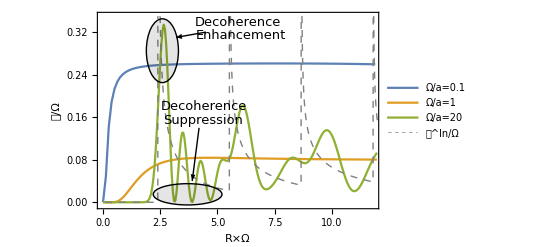

```mathematica
plDRResOa=ListLinePlot[{{Re[#1],Re[#2]}&@@@DROa01Res,{Re[#1],Re[#2]}&@@@DROa1Res,{Re[#1],Re[#2]}&@@@DROa20Res,{Re[#1],Re[#2]}&@@@Indata},PlotRange->{{0,11.8},{-0.005,0.35}},PlotStyle->{,,,{Gray,Dashed,Thickness[0.0025]}},PlotLegends->Placed[{"Ω/a=0.1","Ω/a=1", "Ω/a=20","𝒞^In/Ω"},{0.825,0.725}],Frame->True,FrameLabel->{"R×Ω","𝒞/Ω"},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black},GridLines->{{BesselJZero[0,1],BesselJZero[0,2],BesselJZero[0,3]},{}},Epilog->{{Circle[{2.6,0.285},{0.7,0.06}],{Opacity[0.1],Disk[{2.6,0.285},{0.7,0.06}]}},Text[Style["Decoherence",25,FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black],Scaled[{0.5,0.95}]],Text[Style["Enhancement",25,FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black],Scaled[{0.51,0.88}]],{Arrow[{{4.5,0.32},{3.2,0.31}}]},{Circle[{3.7,0.015},{1.5,0.02}],{Opacity[0.1],Disk[{3.7,0.015},{1.5,0.02}]}},Text[Style["Decoherence",25,FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black],Scaled[{0.38,0.52}]],Text[Style["Suppression",25,FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black],Scaled[{0.375,0.45}]],{Arrow[{{4.2,0.14},{3.9,0.04}}]}}
]
```

```mathematica
DRRO02Res=ParallelTable[{Oa,N[DRRes[2,Oa,40]]},{Oa,1/100,20,1/10}]
```

General::munfl: (2.94294×10^-156+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.05281×10^-160+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.76741×10^-165+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (4.05063×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.87738×10^-160+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.7044×10^-166+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (9.008×10^-156+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.41245×10^-162+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.25334×10^-168+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (9.17978×10^-157+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.64243×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.76603×10^-159+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.96262×10^-156+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.52963×10^-163+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.1926×10^-170+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.03875×10^-158+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.4132×10^-166+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.85723×10^-174+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (3.99352×10^-157+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.18244×10^-166+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.29192×10^-174+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (4.02271×10^-162+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.09998×10^-171+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.0075×10^-181+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (4.22562×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.75861×10^-165+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.31441×10^-176+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (5.25793×10^-156+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.3322×10^-167+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.10932×10^-178+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.8286×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.73259×10^-167+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.63472×10^-179+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.68193×10^-166+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.42346×10^-178+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.08808×10^-191+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{1/100,1.59372+0. ⅈ},{11/100,0.233872+0. ⅈ},{21/100,0.12946+0. ⅈ},{31/100,0.0958133+0. ⅈ},{41/100,0.0806941+0. ⅈ},{51/100,0.0727992+0. ⅈ},{61/100,0.0682854+0. ⅈ},{71/100,0.0655292+0. ⅈ},{81/100,0.0637509+0. ⅈ},{91/100,0.0625425+0. ⅈ},{101/100,0.0616761+0. ⅈ},{111/100,0.0610184+0. ⅈ},{121/100,0.0604879+0. ⅈ},{131/100,0.0600331+0. ⅈ},{141/100,0.0596209+0. ⅈ},{151/100,0.0592298+0. ⅈ},{161/100,0.0588454+0. ⅈ},{171/100,0.0584584+0. ⅈ},{181/100,0.058063+0. ⅈ},{191/100,0.0576556+0. ⅈ},{201/100,0.057234+0. ⅈ},{211/100,0.0567974+0. ⅈ},{221/100,0.0563457+0. ⅈ},{231/100,0.0558792+0. ⅈ},{241/100,0.0553987+0. ⅈ},{251/100,0.0549052+0. ⅈ},{261/100,0.0543996+0. ⅈ},{271/100,0.0538832+0. ⅈ},{281/100,0.0533571+0. ⅈ},{291/100,0.0528224+0. ⅈ},{301/100,0.0522803+0. ⅈ},{311/100,0.0517318+0. ⅈ},{321/100,0.0511778+0. ⅈ},{331/100,0.0506194+0. ⅈ},{341/100,0.0500575+0. ⅈ},{351/100,0.0494927+0. ⅈ},{361/100,0.0489259+0. ⅈ},{371/100,0.0483578+0. ⅈ},{381/100,0.047789+0. ⅈ},{391/100,0.0472201+0. ⅈ},{401/100,0.0466516+0. ⅈ},{411/100,0.046084+0. ⅈ},{421/100,0.0455178+0. ⅈ},{431/100,0.0449534+0. ⅈ},{441/100,0.0443911+0. ⅈ},{451/100,0.0438313+0. ⅈ},{461/100,0.0432744+0. ⅈ},{471/100,0.0427205+0. ⅈ},{481/100,0.04217+0. ⅈ},{491/100,0.041623+0. ⅈ},{501/100,0.0410798+0. ⅈ},{511/100,0.0405406+0. ⅈ},{521/100,0.0400055+0. ⅈ},{531/100,0.0394748+0. ⅈ},{541/100,0.0389484+0. ⅈ},{551/100,0.0384266+0. ⅈ},{561/100,0.0379095+0. ⅈ},{571/100,0.0373971+0. ⅈ},{581/100,0.0368896+0. ⅈ},{591/100,0.036387+0. ⅈ},{601/100,0.0358893+0. ⅈ},{611/100,0.0353968+0. ⅈ},{621/100,0.0349092+0. ⅈ},{631/100,0.0344269+0. ⅈ},{641/100,0.0339497+0. ⅈ},{651/100,0.0334776+0. ⅈ},{661/100,0.0330108+0. ⅈ},{671/100,0.0325492+0. ⅈ},{681/100,0.0320928+0. ⅈ},{691/100,0.0316416+0. ⅈ},{701/100,0.0311957+0. ⅈ},{711/100,0.030755+0. ⅈ},{721/100,0.0303195+0. ⅈ},{731/100,0.0298892+0. ⅈ},{741/100,0.0294641+0. ⅈ},{751/100,0.0290442+0. ⅈ},{761/100,0.0286294+0. ⅈ},{771/100,0.0282197+0. ⅈ},{781/100,0.0278152+0. ⅈ},{791/100,0.0274157+0. ⅈ},{801/100,0.0270213+0. ⅈ},{811/100,0.0266318+0. ⅈ},{821/100,0.0262474+0. ⅈ},{831/100,0.0258679+0. ⅈ},{841/100,0.0254933+0. ⅈ},{851/100,0.0251236+0. ⅈ},{861/100,0.0247587+0. ⅈ},{871/100,0.0243985+0. ⅈ},{881/100,0.0240432+0. ⅈ},{891/100,0.0236925+0. ⅈ},{901/100,0.0233465+0. ⅈ},{911/100,0.0230052+0. ⅈ},{921/100,0.0226684+0. ⅈ},{931/100,0.0223361+0. ⅈ},{941/100,0.0220084+0. ⅈ},{951/100,0.0216851+0. ⅈ},{961/100,0.0213662+0. ⅈ},{971/100,0.0210516+0. ⅈ},{981/100,0.0207413+0. ⅈ},{991/100,0.0204353+0. ⅈ},{1001/100,0.0201336+0. ⅈ},{1011/100,0.019836+0. ⅈ},{1021/100,0.0195425+0. ⅈ},{1031/100,0.0192531+0. ⅈ},{1041/100,0.0189677+0. ⅈ},{1051/100,0.0186863+0. ⅈ},{1061/100,0.0184089+0. ⅈ},{1071/100,0.0181354+0. ⅈ},{1081/100,0.0178657+0. ⅈ},{1091/100,0.0175997+0. ⅈ},{1101/100,0.0173376+0. ⅈ},{1111/100,0.0170792+0. ⅈ},{1121/100,0.0168244+0. ⅈ},{1131/100,0.0165732+0. ⅈ},{1141/100,0.0163257+0. ⅈ},{1151/100,0.0160816+0. ⅈ},{1161/100,0.0158411+0. ⅈ},{1171/100,0.015604+0. ⅈ},{1181/100,0.0153702+0. ⅈ},{1191/100,0.0151399+0. ⅈ},{1201/100,0.0149128+0. ⅈ},{1211/100,0.0146891+0. ⅈ},{1221/100,0.0144685+0. ⅈ},{1231/100,0.0142512+0. ⅈ},{1241/100,0.0140369+0. ⅈ},{1251/100,0.0138258+0. ⅈ},{1261/100,0.0136178+0. ⅈ},{1271/100,0.0134128+0. ⅈ},{1281/100,0.0132107+0. ⅈ},{1291/100,0.0130116+0. ⅈ},{1301/100,0.0128154+0. ⅈ},{1311/100,0.0126221+0. ⅈ},{1321/100,0.0124316+0. ⅈ},{1331/100,0.0122438+0. ⅈ},{1341/100,0.0120589+0. ⅈ},{1351/100,0.0118766+0. ⅈ},{1361/100,0.011697+0. ⅈ},{1371/100,0.0115201+0. ⅈ},{1381/100,0.0113457+0. ⅈ},{1391/100,0.0111739+0. ⅈ},{1401/100,0.0110047+0. ⅈ},{1411/100,0.0108379+0. ⅈ},{1421/100,0.0106737+0. ⅈ},{1431/100,0.0105118+0. ⅈ},{1441/100,0.0103523+0. ⅈ},{1451/100,0.0101952+0. ⅈ},{1461/100,0.0100404+0. ⅈ},{1471/100,0.00988795+0. ⅈ},{1481/100,0.00973773+0. ⅈ},{1491/100,0.00958973+0. ⅈ},{1501/100,0.00944394+0. ⅈ},{1511/100,0.00930031+0. ⅈ},{1521/100,0.00915883+0. ⅈ},{1531/100,0.00901945+0. ⅈ},{1541/100,0.00888214+0. ⅈ},{1551/100,0.00874689+0. ⅈ},{1561/100,0.00861365+0. ⅈ},{1571/100,0.0084824+0. ⅈ},{1581/100,0.00835311+0. ⅈ},{1591/100,0.00822576+0. ⅈ},{1601/100,0.00810031+0. ⅈ},{1611/100,0.00797674+0. ⅈ},{1621/100,0.00785502+0. ⅈ},{1631/100,0.00773513+0. ⅈ},{1641/100,0.00761703+0. ⅈ},{1651/100,0.00750071+0. ⅈ},{1661/100,0.00738613+0. ⅈ},{1671/100,0.00727327+0. ⅈ},{1681/100,0.00716211+0. ⅈ},{1691/100,0.00705262+0. ⅈ},{1701/100,0.00694478+0. ⅈ},{1711/100,0.00683856+0. ⅈ},{1721/100,0.00673394+0. ⅈ},{1731/100,0.00663089+0. ⅈ},{1741/100,0.0065294+0. ⅈ},{1751/100,0.00642944+0. ⅈ},{1761/100,0.00633099+0. ⅈ},{1771/100,0.00623402+0. ⅈ},{1781/100,0.00613852+0. ⅈ},{1791/100,0.00604446+0. ⅈ},{1801/100,0.00595182+0. ⅈ},{1811/100,0.00586059+0. ⅈ},{1821/100,0.00577073+0. ⅈ},{1831/100,0.00568223+0. ⅈ},{1841/100,0.00559508+0. ⅈ},{1851/100,0.00550924+0. ⅈ},{1861/100,0.0054247+0. ⅈ},{1871/100,0.00534145+0. ⅈ},{1881/100,0.00525945+0. ⅈ},{1891/100,0.0051787+0. ⅈ},{1901/100,0.00509918+0. ⅈ},{1911/100,0.00502086+0. ⅈ},{1921/100,0.00494373+0. ⅈ},{1931/100,0.00486777+0. ⅈ},{1941/100,0.00479297+0. ⅈ},{1951/100,0.0047193+0. ⅈ},{1961/100,0.00464676+0. ⅈ},{1971/100,0.00457531+0. ⅈ},{1981/100,0.00450496+0. ⅈ},{1991/100,0.00443567+0. ⅈ}}

```mathematica
DRRsupRes=ParallelTable[{Oa,N[DRRes[3.5,Oa,70]]},{Oa,1/100,20,1/10}]
```

General::munfl: (4.25283×10^-156+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.22412×10^-158+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.52379×10^-161+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.88618×10^-156+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.68878×10^-159+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.51222×10^-162+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.52015×10^-157+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.02086×10^-161+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.9562×10^-164+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (5.94989×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.51387×10^-157+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.28084×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (3.67277×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.1844×10^-159+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.76132×10^-163+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (9.84456×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.90715×10^-159+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.46969×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.58579×10^-164+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.47875×10^-160+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.48792×10^-165+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (4.82312×10^-159+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.65402×10^-164+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.67197×10^-170+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.0061×10^-154+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.17658×10^-160+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.37567×10^-166+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.13005×10^-160+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.49496×10^-167+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.38677×10^-173+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.85625×10^-158+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (3.88802×10^-165+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.28928×10^-172+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.31604×10^-161+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.1141×10^-169+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.83809×10^-176+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{1/100,1.59134+0. ⅈ},{11/100,0.237335+0. ⅈ},{21/100,0.134712+0. ⅈ},{31/100,0.102662+0. ⅈ},{41/100,0.089181+0. ⅈ},{51/100,0.0830313+0. ⅈ},{61/100,0.0803787+0. ⅈ},{71/100,0.0795904+0. ⅈ},{81/100,0.0798734+0. ⅈ},{91/100,0.0808071+0. ⅈ},{101/100,0.082153+0. ⅈ},{111/100,0.0837678+0. ⅈ},{121/100,0.0855614+0. ⅈ},{131/100,0.0874739+0. ⅈ},{141/100,0.0894642+0. ⅈ},{151/100,0.0915024+0. ⅈ},{161/100,0.0935661+0. ⅈ},{171/100,0.0956379+0. ⅈ},{181/100,0.0977037+0. ⅈ},{191/100,0.099752+0. ⅈ},{201/100,0.101773+0. ⅈ},{211/100,0.103758+0. ⅈ},{221/100,0.1057+0. ⅈ},{231/100,0.107593+0. ⅈ},{241/100,0.109429+0. ⅈ},{251/100,0.111205+0. ⅈ},{261/100,0.112915+0. ⅈ},{271/100,0.114555+0. ⅈ},{281/100,0.11612+0. ⅈ},{291/100,0.117607+0. ⅈ},{301/100,0.119013+0. ⅈ},{311/100,0.120334+0. ⅈ},{321/100,0.121567+0. ⅈ},{331/100,0.12271+0. ⅈ},{341/100,0.12376+0. ⅈ},{351/100,0.124716+0. ⅈ},{361/100,0.125574+0. ⅈ},{371/100,0.126334+0. ⅈ},{381/100,0.126994+0. ⅈ},{391/100,0.127552+0. ⅈ},{401/100,0.128008+0. ⅈ},{411/100,0.128361+0. ⅈ},{421/100,0.128609+0. ⅈ},{431/100,0.128753+0. ⅈ},{441/100,0.128792+0. ⅈ},{451/100,0.128726+0. ⅈ},{461/100,0.128555+0. ⅈ},{471/100,0.128279+0. ⅈ},{481/100,0.1279+0. ⅈ},{491/100,0.127416+0. ⅈ},{501/100,0.12683+0. ⅈ},{511/100,0.126143+0. ⅈ},{521/100,0.125354+0. ⅈ},{531/100,0.124467+0. ⅈ},{541/100,0.123482+0. ⅈ},{551/100,0.122401+0. ⅈ},{561/100,0.121226+0. ⅈ},{571/100,0.119959+0. ⅈ},{581/100,0.118602+0. ⅈ},{591/100,0.117157+0. ⅈ},{601/100,0.115627+0. ⅈ},{611/100,0.114014+0. ⅈ},{621/100,0.112321+0. ⅈ},{631/100,0.110551+0. ⅈ},{641/100,0.108706+0. ⅈ},{651/100,0.106791+0. ⅈ},{661/100,0.104807+0. ⅈ},{671/100,0.102759+0. ⅈ},{681/100,0.100649+0. ⅈ},{691/100,0.0984814+0. ⅈ},{701/100,0.0962593+0. ⅈ},{711/100,0.0939864+0. ⅈ},{721/100,0.0916665+0. ⅈ},{731/100,0.0893034+0. ⅈ},{741/100,0.0869008+0. ⅈ},{751/100,0.0844627+0. ⅈ},{761/100,0.0819929+0. ⅈ},{771/100,0.0794956+0. ⅈ},{781/100,0.0769748+0. ⅈ},{791/100,0.0744344+0. ⅈ},{801/100,0.0718786+0. ⅈ},{811/100,0.0693115+0. ⅈ},{821/100,0.0667372+0. ⅈ},{831/100,0.0641598+0. ⅈ},{841/100,0.0615835+0. ⅈ},{851/100,0.0590123+0. ⅈ},{861/100,0.0564503+0. ⅈ},{871/100,0.0539017+0. ⅈ},{881/100,0.0513705+0. ⅈ},{891/100,0.0488607+0. ⅈ},{901/100,0.0463763+0. ⅈ},{911/100,0.0439213+0. ⅈ},{921/100,0.0414994+0. ⅈ},{931/100,0.0391146+0. ⅈ},{941/100,0.0367706+0. ⅈ},{951/100,0.0344711+0. ⅈ},{961/100,0.0322198+0. ⅈ},{971/100,0.0300202+0. ⅈ},{981/100,0.0278757+0. ⅈ},{991/100,0.0257897+0. ⅈ},{1001/100,0.0237655+0. ⅈ},{1011/100,0.0218063+0. ⅈ},{1021/100,0.0199152+0. ⅈ},{1031/100,0.0180951+0. ⅈ},{1041/100,0.0163488+0. ⅈ},{1051/100,0.0146791+0. ⅈ},{1061/100,0.0130886+0. ⅈ},{1071/100,0.0115798+0. ⅈ},{1081/100,0.010155+0. ⅈ},{1091/100,0.00881653+0. ⅈ},{1101/100,0.00756637+0. ⅈ},{1111/100,0.00640649+0. ⅈ},{1121/100,0.00533871+0. ⅈ},{1131/100,0.00436467+0. ⅈ},{1141/100,0.0034859+0. ⅈ},{1151/100,0.00270375+0. ⅈ},{1161/100,0.00201943+0. ⅈ},{1171/100,0.001434+0. ⅈ},{1181/100,0.000948371+0. ⅈ},{1191/100,0.000563277+0. ⅈ},{1201/100,0.000279314+0. ⅈ},{1211/100,0.0000969145+0. ⅈ},{1221/100,0.0000163536+0. ⅈ},{1231/100,0.0000377478+0. ⅈ},{1241/100,0.000161055+0. ⅈ},{1251/100,0.000386076+0. ⅈ},{1261/100,0.000712453+0. ⅈ},{1271/100,0.00113967+0. ⅈ},{1281/100,0.00166706+0. ⅈ},{1291/100,0.00229379+0. ⅈ},{1301/100,0.00301889+0. ⅈ},{1311/100,0.00384123+0. ⅈ},{1321/100,0.00475951+0. ⅈ},{1331/100,0.00577233+0. ⅈ},{1341/100,0.00687809+0. ⅈ},{1351/100,0.00807508+0. ⅈ},{1361/100,0.00936144+0. ⅈ},{1371/100,0.0107352+0. ⅈ},{1381/100,0.0121942+0. ⅈ},{1391/100,0.0137361+0. ⅈ},{1401/100,0.0153587+0. ⅈ},{1411/100,0.0170594+0. ⅈ},{1421/100,0.0188355+0. ⅈ},{1431/100,0.0206843+0. ⅈ},{1441/100,0.022603+0. ⅈ},{1451/100,0.0245885+0. ⅈ},{1461/100,0.0266378+0. ⅈ},{1471/100,0.0287478+0. ⅈ},{1481/100,0.0309152+0. ⅈ},{1491/100,0.0331367+0. ⅈ},{1501/100,0.0354087+0. ⅈ},{1511/100,0.0377279+0. ⅈ},{1521/100,0.0400906+0. ⅈ},{1531/100,0.0424932+0. ⅈ},{1541/100,0.044932+0. ⅈ},{1551/100,0.0474032+0. ⅈ},{1561/100,0.049903+0. ⅈ},{1571/100,0.0524276+0. ⅈ},{1581/100,0.0549732+0. ⅈ},{1591/100,0.0575356+0. ⅈ},{1601/100,0.0601112+0. ⅈ},{1611/100,0.0626957+0. ⅈ},{1621/100,0.0652854+0. ⅈ},{1631/100,0.0678762+0. ⅈ},{1641/100,0.0704641+0. ⅈ},{1651/100,0.0730452+0. ⅈ},{1661/100,0.0756155+0. ⅈ},{1671/100,0.078171+0. ⅈ},{1681/100,0.0807078+0. ⅈ},{1691/100,0.083222+0. ⅈ},{1701/100,0.0857098+0. ⅈ},{1711/100,0.0881674+0. ⅈ},{1721/100,0.0905909+0. ⅈ},{1731/100,0.0929767+0. ⅈ},{1741/100,0.095321+0. ⅈ},{1751/100,0.0976204+0. ⅈ},{1761/100,0.0998712+0. ⅈ},{1771/100,0.10207+0. ⅈ},{1781/100,0.104214+0. ⅈ},{1791/100,0.106299+0. ⅈ},{1801/100,0.108322+0. ⅈ},{1811/100,0.11028+0. ⅈ},{1821/100,0.11217+0. ⅈ},{1831/100,0.113989+0. ⅈ},{1841/100,0.115735+0. ⅈ},{1851/100,0.117405+0. ⅈ},{1861/100,0.118996+0. ⅈ},{1871/100,0.120505+0. ⅈ},{1881/100,0.121931+0. ⅈ},{1891/100,0.123272+0. ⅈ},{1901/100,0.124524+0. ⅈ},{1911/100,0.125687+0. ⅈ},{1921/100,0.126758+0. ⅈ},{1931/100,0.127736+0. ⅈ},{1941/100,0.12862+0. ⅈ},{1951/100,0.129408+0. ⅈ},{1961/100,0.130098+0. ⅈ},{1971/100,0.130691+0. ⅈ},{1981/100,0.131184+0. ⅈ},{1991/100,0.131578+0. ⅈ}}

```mathematica
DRRxi1Res=ParallelTable[{Oa,N[DRRes[BesselJZero[0,1],Oa,40]]},{Oa,1/100,20,1/10}]
```

General::munfl: (6.41116×10^-156+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.34892×10^-160+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.60819×10^-165+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.01364×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.79013×10^-161+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.54982×10^-166+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.63642×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.0174×10^-158+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.76622×10^-156+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (5.77721×10^-160+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.08065×10^-166+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.68042×10^-172+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.97449×10^-158+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.3842×10^-160+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.04657×10^-165+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.33813×10^-167+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.29011×10^-171+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.24707×10^-174+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (5.15048×10^-159+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.73428×10^-167+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.38369×10^-175+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (3.19315×10^-155+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.42761×10^-164+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.72702×10^-172+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (5.06653×10^-158+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.46306×10^-167+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.19649×10^-176+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.84535×10^-159+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.87607×10^-169+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.90499×10^-179+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.54071×10^-159+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.27835×10^-170+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.96297×10^-181+0. ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{1/100,1.39114+0. ⅈ},{11/100,0.235389+0. ⅈ},{21/100,0.131765+0. ⅈ},{31/100,0.0988334+0. ⅈ},{41/100,0.0844681+0. ⅈ},{51/100,0.0773991+0. ⅈ},{61/100,0.073791+0. ⅈ},{71/100,0.0720193+0. ⅈ},{81/100,0.0713004+0. ⅈ},{91/100,0.0712217+0. ⅈ},{101/100,0.0715507+0. ⅈ},{111/100,0.0721491+0. ⅈ},{121/100,0.0729302+0. ⅈ},{131/100,0.0738374+0. ⅈ},{141/100,0.0748323+0. ⅈ},{151/100,0.0758877+0. ⅈ},{161/100,0.0769841+0. ⅈ},{171/100,0.0781069+0. ⅈ},{181/100,0.0792453+0. ⅈ},{191/100,0.0803909+0. ⅈ},{201/100,0.0815373+0. ⅈ},{211/100,0.0826797+0. ⅈ},{221/100,0.0838143+0. ⅈ},{231/100,0.0849382+0. ⅈ},{241/100,0.0860493+0. ⅈ},{251/100,0.0871461+0. ⅈ},{261/100,0.0882274+0. ⅈ},{271/100,0.0892924+0. ⅈ},{281/100,0.0903406+0. ⅈ},{291/100,0.0913718+0. ⅈ},{301/100,0.0923859+0. ⅈ},{311/100,0.0933829+0. ⅈ},{321/100,0.094363+0. ⅈ},{331/100,0.0953265+0. ⅈ},{341/100,0.0962737+0. ⅈ},{351/100,0.0972048+0. ⅈ},{361/100,0.0981204+0. ⅈ},{371/100,0.0990208+0. ⅈ},{381/100,0.0999065+0. ⅈ},{391/100,0.100778+0. ⅈ},{401/100,0.101635+0. ⅈ},{411/100,0.102479+0. ⅈ},{421/100,0.10331+0. ⅈ},{431/100,0.104128+0. ⅈ},{441/100,0.104934+0. ⅈ},{451/100,0.105728+0. ⅈ},{461/100,0.106511+0. ⅈ},{471/100,0.107283+0. ⅈ},{481/100,0.108043+0. ⅈ},{491/100,0.108794+0. ⅈ},{501/100,0.109534+0. ⅈ},{511/100,0.110265+0. ⅈ},{521/100,0.110986+0. ⅈ},{531/100,0.111698+0. ⅈ},{541/100,0.112401+0. ⅈ},{551/100,0.113095+0. ⅈ},{561/100,0.113781+0. ⅈ},{571/100,0.114459+0. ⅈ},{581/100,0.115128+0. ⅈ},{591/100,0.115791+0. ⅈ},{601/100,0.116445+0. ⅈ},{611/100,0.117093+0. ⅈ},{621/100,0.117733+0. ⅈ},{631/100,0.118366+0. ⅈ},{641/100,0.118993+0. ⅈ},{651/100,0.119613+0. ⅈ},{661/100,0.120227+0. ⅈ},{671/100,0.120835+0. ⅈ},{681/100,0.121436+0. ⅈ},{691/100,0.122032+0. ⅈ},{701/100,0.122622+0. ⅈ},{711/100,0.123206+0. ⅈ},{721/100,0.123785+0. ⅈ},{731/100,0.124358+0. ⅈ},{741/100,0.124926+0. ⅈ},{751/100,0.125489+0. ⅈ},{761/100,0.126047+0. ⅈ},{771/100,0.1266+0. ⅈ},{781/100,0.127148+0. ⅈ},{791/100,0.127692+0. ⅈ},{801/100,0.128231+0. ⅈ},{811/100,0.128765+0. ⅈ},{821/100,0.129295+0. ⅈ},{831/100,0.129821+0. ⅈ},{841/100,0.130342+0. ⅈ},{851/100,0.13086+0. ⅈ},{861/100,0.131373+0. ⅈ},{871/100,0.131882+0. ⅈ},{881/100,0.132388+0. ⅈ},{891/100,0.132889+0. ⅈ},{901/100,0.133387+0. ⅈ},{911/100,0.133881+0. ⅈ},{921/100,0.134372+0. ⅈ},{931/100,0.134859+0. ⅈ},{941/100,0.135342+0. ⅈ},{951/100,0.135822+0. ⅈ},{961/100,0.136299+0. ⅈ},{971/100,0.136772+0. ⅈ},{981/100,0.137242+0. ⅈ},{991/100,0.137709+0. ⅈ},{1001/100,0.138172+0. ⅈ},{1011/100,0.138633+0. ⅈ},{1021/100,0.13909+0. ⅈ},{1031/100,0.139545+0. ⅈ},{1041/100,0.139997+0. ⅈ},{1051/100,0.140445+0. ⅈ},{1061/100,0.140891+0. ⅈ},{1071/100,0.141334+0. ⅈ},{1081/100,0.141774+0. ⅈ},{1091/100,0.142212+0. ⅈ},{1101/100,0.142647+0. ⅈ},{1111/100,0.143079+0. ⅈ},{1121/100,0.143509+0. ⅈ},{1131/100,0.143936+0. ⅈ},{1141/100,0.14436+0. ⅈ},{1151/100,0.144782+0. ⅈ},{1161/100,0.145202+0. ⅈ},{1171/100,0.145619+0. ⅈ},{1181/100,0.146034+0. ⅈ},{1191/100,0.146446+0. ⅈ},{1201/100,0.146856+0. ⅈ},{1211/100,0.147264+0. ⅈ},{1221/100,0.14767+0. ⅈ},{1231/100,0.148073+0. ⅈ},{1241/100,0.148475+0. ⅈ},{1251/100,0.148874+0. ⅈ},{1261/100,0.149271+0. ⅈ},{1271/100,0.149665+0. ⅈ},{1281/100,0.150058+0. ⅈ},{1291/100,0.150449+0. ⅈ},{1301/100,0.150837+0. ⅈ},{1311/100,0.151224+0. ⅈ},{1321/100,0.151609+0. ⅈ},{1331/100,0.151992+0. ⅈ},{1341/100,0.152372+0. ⅈ},{1351/100,0.152751+0. ⅈ},{1361/100,0.153128+0. ⅈ},{1371/100,0.153504+0. ⅈ},{1381/100,0.153877+0. ⅈ},{1391/100,0.154249+0. ⅈ},{1401/100,0.154618+0. ⅈ},{1411/100,0.154987+0. ⅈ},{1421/100,0.155353+0. ⅈ},{1431/100,0.155717+0. ⅈ},{1441/100,0.15608+0. ⅈ},{1451/100,0.156441+0. ⅈ},{1461/100,0.156801+0. ⅈ},{1471/100,0.157159+0. ⅈ},{1481/100,0.157515+0. ⅈ},{1491/100,0.15787+0. ⅈ},{1501/100,0.158223+0. ⅈ},{1511/100,0.158574+0. ⅈ},{1521/100,0.158924+0. ⅈ},{1531/100,0.159273+0. ⅈ},{1541/100,0.15962+0. ⅈ},{1551/100,0.159965+0. ⅈ},{1561/100,0.160309+0. ⅈ},{1571/100,0.160651+0. ⅈ},{1581/100,0.160992+0. ⅈ},{1591/100,0.161332+0. ⅈ},{1601/100,0.16167+0. ⅈ},{1611/100,0.162007+0. ⅈ},{1621/100,0.162342+0. ⅈ},{1631/100,0.162676+0. ⅈ},{1641/100,0.163009+0. ⅈ},{1651/100,0.16334+0. ⅈ},{1661/100,0.16367+0. ⅈ},{1671/100,0.163998+0. ⅈ},{1681/100,0.164325+0. ⅈ},{1691/100,0.164651+0. ⅈ},{1701/100,0.164976+0. ⅈ},{1711/100,0.165299+0. ⅈ},{1721/100,0.165622+0. ⅈ},{1731/100,0.165942+0. ⅈ},{1741/100,0.166262+0. ⅈ},{1751/100,0.16658+0. ⅈ},{1761/100,0.166898+0. ⅈ},{1771/100,0.167214+0. ⅈ},{1781/100,0.167528+0. ⅈ},{1791/100,0.167842+0. ⅈ},{1801/100,0.168154+0. ⅈ},{1811/100,0.168466+0. ⅈ},{1821/100,0.168776+0. ⅈ},{1831/100,0.169085+0. ⅈ},{1841/100,0.169393+0. ⅈ},{1851/100,0.169699+0. ⅈ},{1861/100,0.170005+0. ⅈ},{1871/100,0.17031+0. ⅈ},{1881/100,0.170613+0. ⅈ},{1891/100,0.170916+0. ⅈ},{1901/100,0.171217+0. ⅈ},{1911/100,0.171517+0. ⅈ},{1921/100,0.171816+0. ⅈ},{1931/100,0.172115+0. ⅈ},{1941/100,0.172412+0. ⅈ},{1951/100,0.172708+0. ⅈ},{1961/100,0.173003+0. ⅈ},{1971/100,0.173297+0. ⅈ},{1981/100,0.17359+0. ⅈ},{1991/100,0.173882+0. ⅈ}}

```mathematica
DRRO050Res=ParallelTable[{Oa,N[DRRes[50,Oa,250]]},{Oa,1/100,20,1/5}]
```

General::munfl: -(1.99237×10^-305+5.44271×10^-306 ⅈ)/(171.+18.81 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(1.99237×10^-305-5.44271×10^-306 ⅈ)/(171.-18.81 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(1.78236×10^-305+3.31987×10^-306 ⅈ)/(171.+17.61 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(1.78236×10^-305-3.31987×10^-306 ⅈ)/(171.-17.61 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

{{1/100,0.399301+0. ⅈ},{21/100,0.13733+0. ⅈ},{41/100,0.0926985+0. ⅈ},{61/100,0.0831108+0. ⅈ},{81/100,0.0805318+0. ⅈ},{101/100,0.079825+0. ⅈ},{121/100,0.0796932+0. ⅈ},{141/100,0.0796764+0. ⅈ},{161/100,0.0795891+0. ⅈ},{181/100,0.0794694+0. ⅈ},{201/100,0.0794658+0. ⅈ},{221/100,0.0796223+0. ⅈ},{241/100,0.0797823+0. ⅈ},{261/100,0.0797395+0. ⅈ},{281/100,0.0794833+0. ⅈ},{301/100,0.0792548+0. ⅈ},{321/100,0.0793199+0. ⅈ},{341/100,0.0796771+0. ⅈ},{361/100,0.0800154+0. ⅈ},{381/100,0.0799945+0. ⅈ},{401/100,0.0795828+0. ⅈ},{421/100,0.0791132+0. ⅈ},{441/100,0.0789894+0. ⅈ},{461/100,0.0793235+0. ⅈ},{481/100,0.0798473+0. ⅈ},{501/100,0.0801665+0. ⅈ},{521/100,0.080094+0. ⅈ},{541/100,0.0797505+0. ⅈ},{561/100,0.0793845+0. ⅈ},{581/100,0.0791435+0. ⅈ},{601/100,0.0790338+0. ⅈ},{621/100,0.0790564+0. ⅈ},{641/100,0.0792951+0. ⅈ},{661/100,0.0798073+0. ⅈ},{681/100,0.0804301+0. ⅈ},{701/100,0.080768+0. ⅈ},{721/100,0.0804644+0. ⅈ},{741/100,0.0795468+0. ⅈ},{761/100,0.0785013+0. ⅈ},{781/100,0.0779588+0. ⅈ},{801/100,0.0782383+0. ⅈ},{821/100,0.0791388+0. ⅈ},{841/100,0.080139+0. ⅈ},{861/100,0.0807949+0. ⅈ},{881/100,0.0809744+0. ⅈ},{901/100,0.0807798+0. ⅈ},{921/100,0.0803278+0. ⅈ},{941/100,0.0796607+0. ⅈ},{961/100,0.0788585+0. ⅈ},{981/100,0.0781602+0. ⅈ},{1001/100,0.0778863+0. ⅈ},{1021/100,0.078194+0. ⅈ},{1041/100,0.0789179+0. ⅈ},{1061/100,0.0796919+0. ⅈ},{1081/100,0.0802533+0. ⅈ},{1101/100,0.0806254+0. ⅈ},{1121/100,0.0809869+0. ⅈ},{1141/100,0.0813641+0. ⅈ},{1161/100,0.0814845+0. ⅈ},{1181/100,0.0809767+0. ⅈ},{1201/100,0.0797469+0. ⅈ},{1221/100,0.0781674+0. ⅈ},{1241/100,0.0768817+0. ⅈ},{1261/100,0.0763943+0. ⅈ},{1281/100,0.0768003+0. ⅈ},{1301/100,0.0778468+0. ⅈ},{1321/100,0.0791903+0. ⅈ},{1341/100,0.0805681+0. ⅈ},{1361/100,0.0817638+0. ⅈ},{1381/100,0.0825161+0. ⅈ},{1401/100,0.0825777+0. ⅈ},{1421/100,0.081923+0. ⅈ},{1441/100,0.08087+0. ⅈ},{1461/100,0.0799172+0. ⅈ},{1481/100,0.0793785+0. ⅈ},{1501/100,0.0791431+0. ⅈ},{1521/100,0.0788065+0. ⅈ},{1541/100,0.0780736+0. ⅈ},{1561/100,0.0770659+0. ⅈ},{1581/100,0.0762545+0. ⅈ},{1601/100,0.0760942+0. ⅈ},{1621/100,0.0767062+0. ⅈ},{1641/100,0.0778733+0. ⅈ},{1661/100,0.079286+0. ⅈ},{1681/100,0.080751+0. ⅈ},{1701/100,0.0821671+0. ⅈ},{1721/100,0.0833654+0. ⅈ},{1741/100,0.084063+0. ⅈ},{1761/100,0.0840287+0. ⅈ},{1781/100,0.0832947+0. ⅈ},{1801/100,0.0821595+0. ⅈ},{1821/100,0.0809461+0. ⅈ},{1841/100,0.0797529+0. ⅈ},{1861/100,0.0784653+0. ⅈ},{1881/100,0.0770261+0. ⅈ},{1901/100,0.0756763+0. ⅈ},{1921/100,0.0748828+0. ⅈ},{1941/100,0.0749827+0. ⅈ},{1961/100,0.0758722+0. ⅈ},{1981/100,0.0770469+0. ⅈ}}

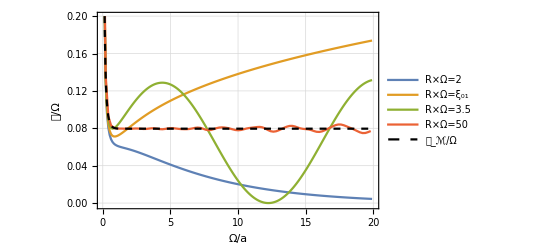

```mathematica
plDRResRO=ListLinePlot[{{Re[#1],Re[#2]}&@@@DRRO02Res,{Re[#1],Re[#2]}&@@@DRRxi1Res,{Re[#1],Re[#2]}&@@@DRRsupRes,{Re[#1],Re[#2]}&@@@DRRO050Res,Rindlerdata},PlotRange->{{0,20},{-0.002,0.2}},PlotLegends->Placed[LineLegend[{"R×Ω=2","R×Ω=ξ_01", "R×Ω=3.5", "R×Ω=50","𝒞_ℳ/Ω"},LegendLayout->"Row",LabelStyle->{FontSize->12}
],{0.5,0.85}],PlotStyle->{,,,,{Black,Dashed}},Frame->True,FrameLabel->{"Ω/a","𝒞/Ω"},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black},GridLines->Automatic]
```

Using Asymptotic expansion

```mathematica
βmnl[n_,RΩ_]:=3/2(ArcSech[BesselJZero[0,n]/RΩ]-√(1-(BesselJZero[0,n]/RΩ)^2))
βmng[n_,RΩ_]:=3/2(-ArcSec[BesselJZero[0,n]/RΩ]+√(-1+(BesselJZero[0,n]/RΩ)^2))
```

```mathematica
βl[x_]:=3/2(ArcSech[x]-√(1-(x)^2))
βg[x_]:=3/2(-ArcSec[x]+√(-1+(x)^2))
```

```mathematica
f[x_,α_]:=Piecewise[{{((βg[x]α)^(1/3)AiryAi[(βg[x]α)^(2/3)]^2)/(√((x)^2-1)),x>1},{((βl[x]α)^(1/3)AiryAi[-(βl[x]α)^(2/3)]^2)/(√(-(x)^2+1)),x<1},{α^(1/3)/(Gamma[2/3]^2 2^(1/3)3^(4/3)),x==1}},{x,0,∞}]
```

```mathematica
Ser[RΩ_,Ωa_,n_]:=Piecewise[{{((βmng[n,RΩ]Ωa)^(1/3)AiryAi[(βmng[n,RΩ]Ωa)^(2/3)]^2)/(√((BesselJZero[0,n]/RΩ)^2-1)BesselJ[1,BesselJZero[0,n]]^2),RΩ<BesselJZero[0,n]},{((βmnl[n,RΩ]Ωa)^(1/3)AiryAi[-(βmnl[n,RΩ]Ωa)^(2/3)]^2)/(√(-(BesselJZero[0,n]/RΩ)^2+1)BesselJ[1,BesselJZero[0,n]]^2),RΩ>BesselJZero[0,n]},{(Ωa/2)^(1/3)/(Gamma[2/3]^2 3^(4/3)BesselJ[1,BesselJZero[0,n]]^2),RΩ==BesselJZero[0,n]}},{RΩ,0,∞}]
```

```mathematica
DRAs[RΩ_,Ωa_,n0_]:=2/RΩ^2 N[ⅇ^(-π Ωa),20]Cosh[π Ωa]Sum[Ser[RΩ,Ωa,n],{n,1,n0}]
```

```mathematica
RTDRAs[RΩ_,Ωa_,n0_]:=(DRAs[RΩ,Ωa,n0]-DRAs[RΩ,Ωa,n0-1])/DRAs[RΩ,Ωa,n0]
```

```mathematica
s1=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,1],10^Oa,3]]},{Oa,3,6,1/10}]
```

{{1000,0.64185},{1000 10^(1/10),0.693053},{1000 10^(1/5),0.748342},{1000 10^(3/10),0.808041},{1000 10^(2/5),0.872502},{1000 √10,0.942106},{1000 10^(3/5),1.01726},{1000 10^(7/10),1.09842},{1000 10^(4/5),1.18604},{1000 10^(9/10),1.28066},{10000,1.38282},{10000 10^(1/10),1.49314},{10000 10^(1/5),1.61225},{10000 10^(3/10),1.74087},{10000 10^(2/5),1.87975},{10000 √10,2.02971},{10000 10^(3/5),2.19163},{10000 10^(7/10),2.36646},{10000 10^(4/5),2.55525},{10000 10^(9/10),2.7591},{100000,2.9792},{100000 10^(1/10),3.21687},{100000 10^(1/5),3.47349},{100000 10^(3/10),3.75059},{100000 10^(2/5),4.0498},{100000 √10,4.37287},{100000 10^(3/5),4.72172},{100000 10^(7/10),5.09839},{100000 10^(4/5),5.50512},{100000 10^(9/10),5.94429},{1000000,6.4185}}

```mathematica
s2=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,1]+1/200,10^Oa,3]]},{Oa,3,6,1/100}]
```

{{1000,0.901994},{1000 10^(1/100),0.913222},{1000 10^(1/50),0.924638},{1000 10^(3/100),0.936247},{1000 10^(1/25),0.948051},{1000 10^(1/20),0.960055},{1000 10^(3/50),0.972262},{1000 10^(7/100),0.984677},{1000 10^(2/25),0.997303},{1000 10^(9/100),1.01014},{1000 10^(1/10),1.02321},{1000 10^(11/100),1.03649},{1000 10^(3/25),1.05},{1000 10^(13/100),1.06375},{1000 10^(7/50),1.07773},{1000 10^(3/20),1.09195},{1000 10^(4/25),1.10642},{1000 10^(17/100),1.12114},{1000 10^(9/50),1.13611},{1000 10^(19/100),1.15134},{1000 10^(1/5),1.16683},{1000 10^(21/100),1.1826},{1000 10^(11/50),1.19863},{1000 10^(23/100),1.21494},{1000 10^(6/25),1.23154},{1000 10^(1/4),1.24841},{1000 10^(13/50),1.26559},{1000 10^(27/100),1.28305},{1000 10^(7/25),1.30082},{1000 10^(29/100),1.31889},{1000 10^(3/10),1.33727},{1000 10^(31/100),1.35596},{1000 10^(8/25),1.37497},{1000 10^(33/100),1.3943},{1000 10^(17/50),1.41396},{1000 10^(7/20),1.43395},{1000 10^(9/25),1.45427},{1000 10^(37/100),1.47493},{1000 10^(19/50),1.49593},{1000 10^(39/100),1.51728},{1000 10^(2/5),1.53897},{1000 10^(41/100),1.56102},{1000 10^(21/50),1.58341},{1000 10^(43/100),1.60616},{1000 10^(11/25),1.62927},{1000 10^(9/20),1.65274},{1000 10^(23/50),1.67656},{1000 10^(47/100),1.70075},{1000 10^(12/25),1.7253},{1000 10^(49/100),1.7502},{1000 √10,1.77547},{1000 10^(51/100),1.80109},{1000 10^(13/25),1.82706},{1000 10^(53/100),1.85339},{1000 10^(27/50),1.88007},{1000 10^(11/20),1.90708},{1000 10^(14/25),1.93444},{1000 10^(57/100),1.96212},{1000 10^(29/50),1.99012},{1000 10^(59/100),2.01844},{1000 10^(3/5),2.04705},{1000 10^(61/100),2.07596},{1000 10^(31/50),2.10514},{1000 10^(63/100),2.13458},{1000 10^(16/25),2.16426},{1000 10^(13/20),2.19417},{1000 10^(33/50),2.22428},{1000 10^(67/100),2.25458},{1000 10^(17/25),2.28503},{1000 10^(69/100),2.31561},{1000 10^(7/10),2.34628},{1000 10^(71/100),2.37702},{1000 10^(18/25),2.40779},{1000 10^(73/100),2.43856},{1000 10^(37/50),2.46927},{1000 10^(3/4),2.49988},{1000 10^(19/25),2.53035},{1000 10^(77/100),2.56062},{1000 10^(39/50),2.59064},{1000 10^(79/100),2.62034},{1000 10^(4/5),2.64966},{1000 10^(81/100),2.67854},{1000 10^(41/50),2.70688},{1000 10^(83/100),2.73462},{1000 10^(21/25),2.76168},{1000 10^(17/20),2.78795},{1000 10^(43/50),2.81335},{1000 10^(87/100),2.83778},{1000 10^(22/25),2.86112},{1000 10^(89/100),2.88326},{1000 10^(9/10),2.90409},{1000 10^(91/100),2.92348},{1000 10^(23/25),2.9413},{1000 10^(93/100),2.95741},{1000 10^(47/50),2.97166},{1000 10^(19/20),2.98391},{1000 10^(24/25),2.994},{1000 10^(97/100),3.00177},{1000 10^(49/50),3.00705},{1000 10^(99/100),3.00966},{10000,3.00944},{10000 10^(1/100),3.0062},{10000 10^(1/50),2.99975},{10000 10^(3/100),2.9899},{10000 10^(1/25),2.97648},{10000 10^(1/20),2.95929},{10000 10^(3/50),2.93814},{10000 10^(7/100),2.91285},{10000 10^(2/25),2.88324},{10000 10^(9/100),2.84913},{10000 10^(1/10),2.81036},{10000 10^(11/100),2.76677},{10000 10^(3/25),2.71823},{10000 10^(13/100),2.66461},{10000 10^(7/50),2.6058},{10000 10^(3/20),2.54174},{10000 10^(4/25),2.47237},{10000 10^(17/100),2.39766},{10000 10^(9/50),2.31766},{10000 10^(19/100),2.2324},{10000 10^(1/5),2.14201},{10000 10^(21/100),2.04665},{10000 10^(11/50),1.94654},{10000 10^(23/100),1.84195},{10000 10^(6/25),1.73326},{10000 10^(1/4),1.62089},{10000 10^(13/50),1.50534},{10000 10^(27/100),1.38723},{10000 10^(7/25),1.26724},{10000 10^(29/100),1.14616},{10000 10^(3/10),1.02487},{10000 10^(31/100),0.904355},{10000 10^(8/25),0.785713},{10000 10^(33/100),0.670128},{10000 10^(17/50),0.558886},{10000 10^(7/20),0.453367},{10000 10^(9/25),0.355032},{10000 10^(37/100),0.265414},{10000 10^(19/50),0.186105},{10000 10^(39/100),0.11873},{10000 10^(2/5),0.0649301},{10000 10^(41/100),0.0263289},{10000 10^(21/50),0.00450062},{10000 10^(43/100),0.000930627},{10000 10^(11/25),0.0169712},{10000 10^(9/20),0.0537919},{10000 10^(23/50),0.112326},{10000 10^(47/100),0.19321},{10000 10^(12/25),0.296728},{10000 10^(49/100),0.42274},{10000 √10,0.570626},{10000 10^(51/100),0.739223},{10000 10^(13/25),0.926767},{10000 10^(53/100),1.13085},{10000 10^(27/50),1.34838},{10000 10^(11/20),1.57556},{10000 10^(14/25),1.8079},{10000 10^(57/100),2.04024},{10000 10^(29/50),2.2668},{10000 10^(59/100),2.48129},{10000 10^(3/5),2.67705},{10000 10^(61/100),2.8472},{10000 10^(31/50),2.98489},{10000 10^(63/100),3.08356},{10000 10^(16/25),3.13727},{10000 10^(13/20),3.14102},{10000 10^(33/50),3.09115},{10000 10^(67/100),2.98571},{10000 10^(17/25),2.82485},{10000 10^(69/100),2.61114},{10000 10^(7/10),2.34986},{10000 10^(71/100),2.04918},{10000 10^(18/25),1.72018},{10000 10^(73/100),1.37672},{10000 10^(37/50),1.03511},{10000 10^(3/4),0.713489},{10000 10^(19/25),0.431006},{10000 10^(77/100),0.206718},{10000 10^(39/50),0.0582666},{10000 10^(79/100),0.00037684},{10000 10^(4/5),0.0432716},{10000 10^(81/100),0.19112},{10000 10^(41/50),0.44068},{10000 10^(83/100),0.780316},{10000 10^(21/25),1.1896},{10000 10^(17/20),1.63969},{10000 10^(43/50),2.09462},{10000 10^(87/100),2.51368},{10000 10^(22/25),2.85481},{10000 10^(89/100),3.07883},{10000 10^(9/10),3.15439},{10000 10^(91/100),3.06293},{10000 10^(23/25),2.80308},{10000 10^(93/100),2.39379},{10000 10^(47/50),1.87525},{10000 10^(19/20),1.30693},{10000 10^(24/25),0.762296},{10000 10^(97/100),0.320141},{10000 10^(49/50),0.0531095},{10000 10^(99/100),0.014778},{100000,0.227269},{100000 10^(1/100),0.67198},{100000 10^(1/50),1.28615},{100000 10^(3/100),1.9676},{100000 10^(1/25),2.58875},{100000 10^(1/20),3.01939},{100000 10^(3/50),3.15499},{100000 10^(7/100),2.94516},{100000 10^(2/25),2.41493},{100000 10^(9/100),1.67112},{100000 10^(1/10),0.888042},{100000 10^(11/100),0.271028},{100000 10^(3/25),0.00276447},{100000 10^(13/100),0.184862},{100000 10^(7/50),0.792537},{100000 10^(3/20),1.66159},{100000 10^(4/25),2.52113},{100000 10^(17/100),3.07216},{100000 10^(9/50),3.0941},{100000 10^(19/100),2.54331},{100000 10^(1/5),1.60008},{100000 10^(21/100),0.629306},{100000 10^(11/50),0.0496551},{100000 10^(23/100),0.149244},{100000 10^(6/25),0.925473},{100000 10^(1/4),2.03884},{100000 10^(13/50),2.93634},{100000 10^(27/100),3.11988},{100000 10^(7/25),2.44016},{100000 10^(29/100),1.24208},{100000 10^(3/10),0.229114},{100000 10^(31/100),0.0631451},{100000 10^(8/25),0.908558},{100000 10^(33/100),2.23693},{100000 10^(17/50),3.10806},{100000 10^(7/20),2.82993},{100000 10^(9/25),1.55374},{100000 10^(37/100),0.278265},{100000 10^(19/50),0.107674},{100000 10^(39/100),1.26149},{100000 10^(2/5),2.73107},{100000 10^(41/100),3.09216},{100000 10^(21/50),1.91171},{100000 10^(43/100),0.361214},{100000 10^(11/25),0.142756},{100000 10^(9/20),1.58261},{100000 10^(23/50),3.03529},{100000 10^(47/100),2.67844},{100000 10^(12/25),0.883178},{100000 10^(49/100),0.015566},{100000 √10,1.34922},{100000 10^(51/100),3.032},{100000 10^(13/25),2.50857},{100000 10^(53/100),0.506498},{100000 10^(27/50),0.261703},{100000 10^(11/20),2.27177},{100000 10^(14/25),3.05872},{100000 10^(57/100),1.11966},{100000 10^(29/50),0.0564998},{100000 10^(59/100),2.01154},{100000 10^(3/5),3.07692},{100000 10^(61/100),0.955024},{100000 10^(31/50),0.215309},{100000 10^(63/100),2.58414},{100000 10^(16/25),2.57171},{100000 10^(13/20),0.148083},{100000 10^(33/50),1.34128},{100000 10^(67/100),3.13391},{100000 10^(17/25),0.754063},{100000 10^(69/100),0.683625},{100000 10^(7/10),3.14346},{100000 10^(71/100),1.00396},{100000 10^(18/25),0.63903},{100000 10^(73/100),3.15804},{100000 10^(37/50),0.645498},{100000 10^(3/4),1.22607},{100000 10^(19/25),2.93382},{100000 10^(77/100),0.0348525},{100000 10^(39/50),2.55436},{100000 10^(79/100),1.53603},{100000 10^(4/5),0.750866},{100000 10^(81/100),2.96639},{100000 10^(41/50),0.00124544},{100000 10^(83/100),3.05928},{100000 10^(21/25),0.360457},{100000 10^(17/20),2.49001},{100000 10^(43/50),0.943327},{100000 10^(87/100),2.02021},{100000 10^(22/25),1.23249},{100000 10^(89/100),1.94203},{100000 10^(9/10),1.08945},{100000 10^(91/100),2.30054},{100000 10^(23/25),0.550004},{100000 10^(93/100),2.92864},{100000 10^(47/50),0.0181376},{100000 10^(19/20),3.07577},{100000 10^(24/25),0.58166},{100000 10^(97/100),1.63619},{100000 10^(49/50),2.59686},{100000 10^(99/100),0.00155676},{1000000,2.59249}}

```mathematica
s3=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,1]+1/100,10^Oa,3]]},{Oa,3,6,1/100}]
```

{{1000,1.16664},{1000 10^(1/100),1.18346},{1000 10^(1/50),1.20053},{1000 10^(3/100),1.21786},{1000 10^(1/25),1.23544},{1000 10^(1/20),1.25327},{1000 10^(3/50),1.27136},{1000 10^(7/100),1.28969},{1000 10^(2/25),1.30828},{1000 10^(9/100),1.3271},{1000 10^(1/10),1.34617},{1000 10^(11/100),1.36548},{1000 10^(3/25),1.38501},{1000 10^(13/100),1.40478},{1000 10^(7/50),1.42476},{1000 10^(3/20),1.44495},{1000 10^(4/25),1.46535},{1000 10^(17/100),1.48594},{1000 10^(9/50),1.50672},{1000 10^(19/100),1.52766},{1000 10^(1/5),1.54877},{1000 10^(21/100),1.57001},{1000 10^(11/50),1.59139},{1000 10^(23/100),1.61287},{1000 10^(6/25),1.63444},{1000 10^(1/4),1.65608},{1000 10^(13/50),1.67776},{1000 10^(27/100),1.69946},{1000 10^(7/25),1.72116},{1000 10^(29/100),1.74281},{1000 10^(3/10),1.7644},{1000 10^(31/100),1.78588},{1000 10^(8/25),1.80722},{1000 10^(33/100),1.82838},{1000 10^(17/50),1.84931},{1000 10^(7/20),1.86998},{1000 10^(9/25),1.89032},{1000 10^(37/100),1.91029},{1000 10^(19/50),1.92983},{1000 10^(39/100),1.94887},{1000 10^(2/5),1.96737},{1000 10^(41/100),1.98524},{1000 10^(21/50),2.00243},{1000 10^(43/100),2.01884},{1000 10^(11/25),2.03441},{1000 10^(9/20),2.04904},{1000 10^(23/50),2.06265},{1000 10^(47/100),2.07515},{1000 10^(12/25),2.08643},{1000 10^(49/100),2.0964},{1000 √10,2.10496},{1000 10^(51/100),2.11198},{1000 10^(13/25),2.11735},{1000 10^(53/100),2.12097},{1000 10^(27/50),2.12269},{1000 10^(11/20),2.12241},{1000 10^(14/25),2.11999},{1000 10^(57/100),2.1153},{1000 10^(29/50),2.10821},{1000 10^(59/100),2.09859},{1000 10^(3/5),2.0863},{1000 10^(61/100),2.07122},{1000 10^(31/50),2.0532},{1000 10^(63/100),2.03213},{1000 10^(16/25),2.00788},{1000 10^(13/20),1.98033},{1000 10^(33/50),1.94938},{1000 10^(67/100),1.91494},{1000 10^(17/25),1.8769},{1000 10^(69/100),1.83521},{1000 10^(7/10),1.7898},{1000 10^(71/100),1.74065},{1000 10^(18/25),1.68774},{1000 10^(73/100),1.63109},{1000 10^(37/50),1.57074},{1000 10^(3/4),1.50678},{1000 10^(19/25),1.43931},{1000 10^(77/100),1.36851},{1000 10^(39/50),1.29457},{1000 10^(79/100),1.21775},{1000 10^(4/5),1.13834},{1000 10^(81/100),1.05673},{1000 10^(41/50),0.973337},{1000 10^(83/100),0.888648},{1000 10^(21/25),0.803224},{1000 10^(17/20),0.717693},{1000 10^(43/50),0.632757},{1000 10^(87/100),0.549186},{1000 10^(22/25),0.467824},{1000 10^(89/100),0.389582},{1000 10^(9/10),0.315436},{1000 10^(91/100),0.246421},{1000 10^(23/25),0.18362},{1000 10^(93/100),0.128157},{1000 10^(47/50),0.0811805},{1000 10^(19/20),0.0438475},{1000 10^(24/25),0.0173016},{1000 10^(97/100),0.00265018},{1000 10^(49/50),0.000936046},{1000 10^(99/100),0.0131062},{10000,0.0399767},{10000 10^(1/100),0.0821942},{10000 10^(1/50),0.140195},{10000 10^(3/100),0.214161},{10000 10^(1/25),0.303975},{10000 10^(1/20),0.409179},{10000 10^(3/50),0.528927},{10000 10^(7/100),0.66195},{10000 10^(2/25),0.806519},{10000 10^(9/100),0.960425},{10000 10^(1/10),1.12096},{10000 10^(11/100),1.28493},{10000 10^(3/25),1.44867},{10000 10^(13/100),1.60808},{10000 10^(7/50),1.7587},{10000 10^(3/20),1.89582},{10000 10^(4/25),2.01458},{10000 10^(17/100),2.11016},{10000 10^(9/50),2.17797},{10000 10^(19/100),2.21382},{10000 10^(1/5),2.21426},{10000 10^(21/100),2.17677},{10000 10^(11/50),2.10004},{10000 10^(23/100),1.98429},{10000 10^(6/25),1.83142},{10000 10^(1/4),1.6453},{10000 10^(13/50),1.4318},{10000 10^(27/100),1.19885},{10000 10^(7/25),0.956362},{10000 10^(29/100),0.715906},{10000 10^(3/10),0.490345},{10000 10^(31/100),0.293204},{10000 10^(8/25),0.137891},{10000 10^(33/100),0.0367557},{10000 10^(17/50),0.0000244826},{10000 10^(7/20),0.0346814},{10000 10^(9/25),0.143378},{10000 10^(37/100),0.32349},{10000 10^(19/50),0.566441},{10000 10^(39/100),0.857455},{10000 10^(2/5),1.17585},{10000 10^(41/100),1.49602},{10000 10^(21/50),1.78911},{10000 10^(43/100),2.02548},{10000 10^(11/25),2.17775},{10000 10^(9/20),2.22424},{10000 10^(23/50),2.15251},{10000 10^(47/100),1.96239},{10000 10^(12/25),1.66817},{10000 10^(49/100),1.29904},{10000 √10,0.897688},{10000 10^(51/100),0.516342},{10000 10^(13/25),0.210552},{10000 10^(53/100),0.0310104},{10000 10^(27/50),0.0144063},{10000 10^(11/20),0.174772},{10000 10^(14/25),0.497138},{10000 10^(57/100),0.935416},{10000 10^(29/50),1.41611},{10000 10^(59/100),1.84865},{10000 10^(3/5),2.14168},{10000 10^(61/100),2.22323},{10000 10^(31/50),2.06062},{10000 10^(63/100),1.67495},{10000 10^(16/25),1.14485},{10000 10^(13/20),0.595472},{10000 10^(33/50),0.171801},{10000 10^(67/100),0.000396227},{10000 10^(17/25),0.148311},{10000 10^(69/100),0.592141},{10000 10^(7/10),1.21057},{10000 10^(71/100),1.8095},{10000 10^(18/25),2.17919},{10000 10^(73/100),2.16979},{10000 10^(37/50),1.75958},{10000 10^(3/4),1.08499},{10000 10^(19/25),0.408804},{10000 10^(77/100),0.0245888},{10000 10^(39/50),0.125925},{10000 10^(79/100),0.696561},{10000 10^(4/5),1.48433},{10000 10^(81/100),2.09549},{10000 10^(41/50),2.18808},{10000 10^(83/100),1.67648},{10000 10^(21/25),0.823999},{10000 10^(17/20),0.134331},{10000 10^(43/50),0.061577},{10000 10^(87/100),0.693326},{10000 10^(22/25),1.63035},{10000 10^(89/100),2.20548},{10000 10^(9/10),1.95704},{10000 10^(91/100),1.03299},{10000 10^(23/25),0.161318},{10000 10^(93/100),0.101645},{10000 10^(47/50),0.95609},{10000 10^(19/20),1.97175},{10000 10^(24/25),2.15848},{10000 10^(97/100),1.27724},{10000 10^(49/50),0.209642},{10000 10^(99/100),0.134412},{100000,1.1935},{100000 10^(1/100),2.16876},{100000 10^(1/50),1.82886},{100000 10^(3/100),0.549884},{100000 10^(1/25),0.0260492},{100000 10^(1/20),1.03788},{100000 10^(3/50),2.16994},{100000 10^(7/100),1.69362},{100000 10^(2/25),0.291661},{100000 10^(9/100),0.24039},{100000 10^(1/10),1.6878},{100000 10^(11/100),2.11824},{100000 10^(3/25),0.693572},{100000 10^(13/100),0.0721925},{100000 10^(7/50),1.51988},{100000 10^(3/20),2.13036},{100000 10^(4/25),0.573203},{100000 10^(17/100),0.21452},{100000 10^(9/50),1.90881},{100000 10^(19/100),1.71667},{100000 10^(1/5),0.0588063},{100000 10^(21/100),1.07085},{100000 10^(11/50),2.18041},{100000 10^(23/100),0.424081},{100000 10^(6/25),0.597233},{100000 10^(1/4),2.22759},{100000 10^(13/50),0.580516},{100000 10^(27/100),0.571684},{100000 10^(7/25),2.22166},{100000 10^(29/100),0.339976},{100000 10^(3/10),1.01712},{100000 10^(31/100),1.97858},{100000 10^(8/25),0.0023757},{100000 10^(33/100),1.92363},{100000 10^(17/50),0.915093},{100000 10^(7/20),0.683518},{100000 10^(9/25),1.99534},{100000 10^(37/100),0.0227769},{100000 10^(19/50),2.2077},{100000 10^(39/100),0.146484},{100000 10^(2/5),1.9044},{100000 10^(41/100),0.491341},{100000 10^(21/50),1.614},{100000 10^(43/100),0.671494},{100000 10^(11/25),1.57118},{100000 10^(9/20),0.56895},{100000 10^(23/50),1.80957},{100000 10^(47/100),0.231114},{100000 10^(12/25),2.16521},{100000 10^(49/100),0.00220911},{100000 √10,2.06627},{100000 10^(51/100),0.620424},{100000 10^(13/25),0.899088},{100000 10^(53/100),2.01041},{100000 10^(27/50),0.0214315},{100000 10^(11/20),1.59832},{100000 10^(14/25),1.71419},{100000 10^(57/100),0.00727757},{100000 10^(29/50),1.38001},{100000 10^(59/100),2.09387},{100000 10^(3/5),0.443616},{100000 10^(61/100),0.254601},{100000 10^(31/50),1.76563},{100000 10^(63/100),2.11736},{100000 10^(16/25),0.937328},{100000 10^(13/20),0.0338544},{100000 10^(33/50),0.336265},{100000 10^(67/100),1.28083},{100000 10^(17/25),2.01916},{100000 10^(69/100),2.22647},{100000 10^(7/10),2.04043},{100000 10^(71/100),1.72084},{100000 10^(18/25),1.45058},{100000 10^(73/100),1.31107},{100000 10^(37/50),1.32666},{100000 10^(3/4),1.4991},{100000 10^(19/25),1.80048},{100000 10^(77/100),2.12072},{100000 10^(39/50),2.20984},{100000 10^(79/100),1.75055},{100000 10^(4/5),0.743669},{100000 10^(81/100),0.00753081},{100000 10^(41/50),0.680974},{100000 10^(83/100),2.0884},{100000 10^(21/25),1.57991},{100000 10^(17/20),0.0166253},{100000 10^(43/50),1.41598},{100000 10^(87/100),1.79258},{100000 10^(22/25),0.0187415},{100000 10^(89/100),2.16187},{100000 10^(9/10),0.239419},{100000 10^(91/100),1.90717},{100000 10^(23/25),0.241832},{100000 10^(93/100),2.163},{100000 10^(47/50),0.025221},{100000 10^(19/20),1.71421},{100000 10^(24/25),1.60556},{100000 10^(97/100),0.0135446},{100000 10^(49/50),0.998071},{100000 10^(99/100),2.17566},{1000000,1.89009},{1000000 10^(1/100),1.037},{1000000 10^(1/50),0.452262},{1000000 10^(3/100),0.225384},{1000000 10^(1/25),0.224447},{1000000 10^(1/20),0.454482},{1000000 10^(3/50),1.06629},{1000000 10^(7/100),1.95404},{1000000 10^(2/25),2.09433},{1000000 10^(9/100),0.623876},{1000000 10^(1/10),0.294976},{1000000 10^(11/100),2.20547},{1000000 10^(3/25),0.339515},{1000000 10^(13/100),1.66643},{1000000 10^(7/50),0.458169},{1000000 10^(3/20),2.11076},{1000000 10^(4/25),0.0850784},{1000000 10^(17/100),1.04233},{1000000 10^(9/50),2.21839},{1000000 10^(19/100),1.74262},{1000000 10^(1/5),1.01611},{1000000 10^(21/100),0.729322},{1000000 10^(11/50),0.90986},{1000000 10^(23/100),1.57527},{1000000 10^(6/25),2.22431},{1000000 10^(1/4),1.24892},{1000000 10^(13/50),0.0533621},{1000000 10^(27/100),2.16329},{1000000 10^(7/25),0.135149},{1000000 10^(29/100),2.21613},{1000000 10^(3/10),0.28272},{1000000 10^(31/100),0.518821},{1000000 10^(8/25),1.76753},{1000000 10^(33/100),2.17446},{1000000 10^(17/50),2.19362},{1000000 10^(7/20),1.91359},{1000000 10^(9/25),0.76522},{1000000 10^(37/100),0.124982},{1000000 10^(19/50),2.17574},{1000000 10^(39/100),0.111768},{1000000 10^(2/5),2.22589},{1000000 10^(41/100),0.751426},{1000000 10^(21/50),0.000694779},{1000000 10^(43/100),0.199566},{1000000 10^(11/25),0.116816},{1000000 10^(9/20),0.0963239},{1000000 10^(23/50),1.62968},{1000000 10^(47/100),1.39708},{1000000 10^(12/25),0.884111},{1000000 10^(49/100),0.441929},{1000000 √10,1.92357},{1000000 10^(51/100),2.21693},{1000000 10^(13/25),2.14574},{1000000 10^(53/100),1.17428},{1000000 10^(27/50),0.0922132},{1000000 10^(11/20),2.19884},{1000000 10^(14/25),0.506711},{1000000 10^(57/100),0.093371},{1000000 10^(29/50),0.359938},{1000000 10^(59/100),0.0286818},{1000000 10^(3/5),0.936556},{1000000 10^(61/100),1.74332},{1000000 10^(31/50),1.16541},{1000000 10^(63/100),0.0306048},{1000000 10^(16/25),0.0000402783},{1000000 10^(13/20),0.433063},{1000000 10^(33/50),2.22051},{1000000 10^(67/100),0.00339518},{1000000 10^(17/25),1.17148},{1000000 10^(69/100),1.62308},{1000000 10^(7/10),0.670355},{1000000 10^(71/100),0.570149},{1000000 10^(18/25),1.18128},{1000000 10^(73/100),2.2012},{1000000 10^(37/50),2.15596},{1000000 10^(3/4),0.680864},{1000000 10^(19/25),1.51431},{1000000 10^(77/100),0.050182},{1000000 10^(39/50),0.0308448},{1000000 10^(79/100),1.34395},{1000000 10^(4/5),0.832691},{1000000 10^(81/100),2.13289},{1000000 10^(41/50),1.94473},{1000000 10^(83/100),0.0622639},{1000000 10^(21/25),2.1382},{1000000 10^(17/20),2.21505},{1000000 10^(43/50),1.53502},{1000000 10^(87/100),0.826329},{1000000 10^(22/25),0.0413685},{1000000 10^(89/100),0.775288},{1000000 10^(9/10),1.53733},{1000000 10^(91/100),2.22437},{1000000 10^(23/25),1.57333},{1000000 10^(93/100),0.806751},{1000000 10^(47/50),0.17462},{1000000 10^(19/20),1.74066},{1000000 10^(24/25),0.0101234},{1000000 10^(97/100),8.43203×10^-6},{1000000 10^(49/50),2.07868},{1000000 10^(99/100),1.04203},{10000000,2.21707},{10000000 10^(1/100),0.408704},{10000000 10^(1/50),1.03422},{10000000 10^(3/100),0.89719},{10000000 10^(1/25),0.912588},{10000000 10^(1/20),1.06135},{10000000 10^(3/50),0.656887},{10000000 10^(7/100),1.96903},{10000000 10^(2/25),2.19651},{10000000 10^(9/100),0.0129953},{10000000 10^(1/10),0.0883999},{10000000 10^(11/100),2.12616},{10000000 10^(3/25),2.21306},{10000000 10^(13/100),0.126867},{10000000 10^(7/50),1.13062},{10000000 10^(3/20),0.004616},{10000000 10^(4/25),1.90979},{10000000 10^(17/100),1.78501},{10000000 10^(9/50),0.0394694},{10000000 10^(19/100),0.80375},{10000000 10^(1/5),0.258531},{10000000 10^(21/100),1.52717},{10000000 10^(11/50),0.0397771},{10000000 10^(23/100),0.105411},{10000000 10^(6/25),1.90393},{10000000 10^(1/4),0.0708852},{10000000 10^(13/50),1.07965},{10000000 10^(27/100),0.811032},{10000000 10^(7/25),0.0380185},{10000000 10^(29/100),2.2191},{10000000 10^(3/10),0.173987},{10000000 10^(31/100),0.444619},{10000000 10^(8/25),1.13043},{10000000 10^(33/100),1.07811},{10000000 10^(17/50),0.434854},{10000000 10^(7/20),0.0128008},{10000000 10^(9/25),1.06429},{10000000 10^(37/100),2.22487},{10000000 10^(19/50),1.19693},{10000000 10^(39/100),0.0214487},{10000000 10^(2/5),0.496477},{10000000 10^(41/100),1.30313},{10000000 10^(21/50),1.49704},{10000000 10^(43/100),0.885996},{10000000 10^(11/25),0.0048754},{10000000 10^(9/20),2.07991},{10000000 10^(23/50),0.00599665},{10000000 10^(47/100),0.510032},{10000000 10^(12/25),0.139156},{10000000 10^(49/100),1.32907},{10000000 √10,0.0440176},{10000000 10^(51/100),0.0163685},{10000000 10^(13/25),1.85028},{10000000 10^(53/100),0.54049},{10000000 10^(27/50),2.02486},{10000000 10^(11/20),0.273233},{10000000 10^(14/25),1.66698},{10000000 10^(57/100),0.188455},{10000000 10^(29/50),2.13208},{10000000 10^(59/100),1.9644},{10000000 10^(3/5),0.00039748},{10000000 10^(61/100),1.42111},{10000000 10^(31/50),1.61231},{10000000 10^(63/100),0.322049},{10000000 10^(16/25),1.20712},{10000000 10^(13/20),0.793695},{10000000 10^(33/50),2.12728},{10000000 10^(67/100),0.328825},{10000000 10^(17/25),0.564253},{10000000 10^(69/100),2.22715},{10000000 10^(7/10),0.204658},{10000000 10^(71/100),2.14574},{10000000 10^(18/25),0.481027},{10000000 10^(73/100),0.207094},{10000000 10^(37/50),1.6186},{10000000 10^(3/4),0.275448},{10000000 10^(19/25),0.544683},{10000000 10^(77/100),0.972164},{10000000 10^(39/50),0.329022},{10000000 10^(79/100),2.08585},{10000000 10^(4/5),1.73231},{10000000 10^(81/100),2.06132},{10000000 10^(41/50),0.172339},{10000000 10^(83/100),0.874134},{10000000 10^(21/25),1.98456},{10000000 10^(17/20),2.22594},{10000000 10^(43/50),1.86056},{10000000 10^(87/100),0.549713},{10000000 10^(22/25),0.672969},{10000000 10^(89/100),1.05426},{10000000 10^(9/10),1.87902},{10000000 10^(91/100),0.326594},{10000000 10^(23/25),2.11125},{10000000 10^(93/100),0.733364},{10000000 10^(47/50),1.74957},{10000000 10^(19/20),0.777927},{10000000 10^(24/25),2.20042},{10000000 10^(97/100),1.15658},{10000000 10^(49/50),0.147692},{10000000 10^(99/100),0.444146},{100000000,2.20927},{100000000 10^(1/100),0.511284},{100000000 10^(1/50),0.383312},{100000000 10^(3/100),2.14513},{100000000 10^(1/25),2.19401},{100000000 10^(1/20),0.608055},{100000000 10^(3/50),2.0992},{100000000 10^(7/100),0.419692},{100000000 10^(2/25),0.342074},{100000000 10^(9/100),2.2268},{100000000 10^(1/10),0.26338},{100000000 10^(11/100),0.0913892},{100000000 10^(3/25),2.22596},{100000000 10^(13/100),2.22139},{100000000 10^(7/50),1.2809},{100000000 10^(3/20),0.233729},{100000000 10^(4/25),2.22158},{100000000 10^(17/100),1.31698},{100000000 10^(9/50),1.62029},{100000000 10^(19/100),0.763176},{100000000 10^(1/5),0.422621},{100000000 10^(21/100),1.79607},{100000000 10^(11/50),1.60986},{100000000 10^(23/100),0.0590892},{100000000 10^(6/25),0.00050491},{100000000 10^(1/4),1.59385},{100000000 10^(13/50),0.777033},{100000000 10^(27/100),0.692213},{100000000 10^(7/25),1.669},{100000000 10^(29/100),0.0565337},{100000000 10^(3/10),0.467771},{100000000 10^(31/100),0.93412},{100000000 10^(8/25),1.27888},{100000000 10^(33/100),0.762384},{100000000 10^(17/50),0.814368},{100000000 10^(7/20),2.2262},{100000000 10^(9/25),1.59416},{100000000 10^(37/100),0.374788},{100000000 10^(19/50),1.87021},{100000000 10^(39/100),0.0857791},{100000000 10^(2/5),0.672038},{100000000 10^(41/100),0.0103073},{100000000 10^(21/50),1.51626},{100000000 10^(43/100),2.09676},{100000000 10^(11/25),0.216892},{100000000 10^(9/20),0.135861},{100000000 10^(23/50),0.15423},{100000000 10^(47/100),0.528419},{100000000 10^(12/25),0.0635913},{100000000 10^(49/100),2.15107},{100000000 √10,1.46549},{100000000 10^(51/100),2.21603},{100000000 10^(13/25),2.01317},{100000000 10^(53/100),1.9695},{100000000 10^(27/50),0.945889},{100000000 10^(11/20),0.260447},{100000000 10^(14/25),0.127809},{100000000 10^(57/100),1.52786},{100000000 10^(29/50),0.156648},{100000000 10^(59/100),1.86239},{100000000 10^(3/5),1.40781},{100000000 10^(61/100),1.49297},{100000000 10^(31/50),0.00297698},{100000000 10^(63/100),0.00158735},{100000000 10^(16/25),0.286099},{100000000 10^(13/20),0.864331},{100000000 10^(33/50),2.12576},{100000000 10^(67/100),2.22721},{100000000 10^(17/25),2.11791},{100000000 10^(69/100),1.48572},{100000000 10^(7/10),0.975524},{100000000 10^(71/100),0.378989},{100000000 10^(18/25),1.37935},{100000000 10^(73/100),1.21022},{100000000 10^(37/50),0.0000550344},{100000000 10^(3/4),1.98844},{100000000 10^(19/25),0.228031},{100000000 10^(77/100),0.0481244},{100000000 10^(39/50),0.000689488},{100000000 10^(79/100),2.14359},{100000000 10^(4/5),1.54503},{100000000 10^(81/100),0.358254},{100000000 10^(41/50),0.443119},{100000000 10^(83/100),0.193662},{100000000 10^(21/25),1.60027},{100000000 10^(17/20),0.505797},{100000000 10^(43/50),0.140511},{100000000 10^(87/100),0.19383},{100000000 10^(22/25),2.00561},{100000000 10^(89/100),1.68247},{100000000 10^(9/10),0.0440319},{100000000 10^(91/100),2.22778},{100000000 10^(23/25),2.22255},{100000000 10^(93/100),0.737283},{100000000 10^(47/50),1.34613},{100000000 10^(19/20),1.02735},{100000000 10^(24/25),0.227771},{100000000 10^(97/100),0.697436},{100000000 10^(49/50),0.134125},{100000000 10^(99/100),0.928044},{1000000000,0.0362266},{1000000000 10^(1/100),1.71221},{1000000000 10^(1/50),0.262323},{1000000000 10^(3/100),1.86111},{1000000000 10^(1/25),0.420276},{1000000000 10^(1/20),2.22779},{1000000000 10^(3/50),2.21687},{1000000000 10^(7/100),1.5938},{1000000000 10^(2/25),0.0219705},{1000000000 10^(9/100),0.657232},{1000000000 10^(1/10),0.36538},{1000000000 10^(11/100),2.01176},{1000000000 10^(3/25),1.7181},{1000000000 10^(13/100),0.135411},{1000000000 10^(7/50),2.22538},{1000000000 10^(3/20),1.4578},{1000000000 10^(4/25),0.143833},{1000000000 10^(17/100),2.18958},{1000000000 10^(9/50),0.0000277017},{1000000000 10^(19/100),1.04541},{1000000000 10^(1/5),1.55977},{1000000000 10^(21/100),0.776269},{1000000000 10^(11/50),0.00532217},{1000000000 10^(23/100),1.25855},{1000000000 10^(6/25),1.44422},{1000000000 10^(1/4),0.0367936},{1000000000 10^(13/50),1.03673},{1000000000 10^(27/100),0.362064},{1000000000 10^(7/25),0.138779},{1000000000 10^(29/100),1.04931},{1000000000 10^(3/10),1.00807},{1000000000 10^(31/100),0.00140401},{1000000000 10^(8/25),2.22385},{1000000000 10^(33/100),1.19065},{1000000000 10^(17/50),0.660617},{1000000000 10^(7/20),0.545524},{1000000000 10^(9/25),0.0359276},{1000000000 10^(37/100),2.0341},{1000000000 10^(19/50),2.14407},{1000000000 10^(39/100),1.91956},{1000000000 10^(2/5),2.01168},{1000000000 10^(41/100),2.20347},{1000000000 10^(21/50),1.70006},{1000000000 10^(43/100),2.20838},{1000000000 10^(11/25),1.18425},{1000000000 10^(9/20),0.0428364},{1000000000 10^(23/50),0.202555},{1000000000 10^(47/100),1.87224},{1000000000 10^(12/25),0.834325},{1000000000 10^(49/100),1.73504},{1000000000 √10,1.03623},{1000000000 10^(51/100),2.22031},{1000000000 10^(13/25),1.14599},{1000000000 10^(53/100),1.80197},{1000000000 10^(27/50),2.226},{1000000000 10^(11/20),1.82803},{1000000000 10^(14/25),2.21909},{1000000000 10^(57/100),1.80217},{1000000000 10^(29/50),1.99711},{1000000000 10^(59/100),0.128683},{1000000000 10^(3/5),0.608007},{1000000000 10^(61/100),1.47574},{1000000000 10^(31/50),1.85776},{1000000000 10^(63/100),1.68076},{1000000000 10^(16/25),0.149309},{1000000000 10^(13/20),1.97378},{1000000000 10^(33/50),0.0874532},{1000000000 10^(67/100),1.46946},{1000000000 10^(17/25),0.0301375},{1000000000 10^(69/100),1.40213},{1000000000 10^(7/10),2.16937},{1000000000 10^(71/100),0.226439},{1000000000 10^(18/25),1.86117},{1000000000 10^(73/100),0.265552},{1000000000 10^(37/50),1.22443},{1000000000 10^(3/4),0.684326},{1000000000 10^(19/25),0.859951},{1000000000 10^(77/100),0.902013},{1000000000 10^(39/50),0.729982},{1000000000 10^(79/100),1.89067},{1000000000 10^(4/5),0.289863},{1000000000 10^(81/100),2.14054},{1000000000 10^(41/50),1.31248},{1000000000 10^(83/100),0.78742},{1000000000 10^(21/25),2.20695},{1000000000 10^(17/20),0.57178},{1000000000 10^(43/50),2.1545},{1000000000 10^(87/100),1.4375},{1000000000 10^(22/25),0.955216},{1000000000 10^(89/100),0.223482},{1000000000 10^(9/10),0.76298},{1000000000 10^(91/100),1.1613},{1000000000 10^(23/25),2.0334},{1000000000 10^(93/100),0.77681},{1000000000 10^(47/50),2.07527},{1000000000 10^(19/20),1.89551},{1000000000 10^(24/25),0.86413},{1000000000 10^(97/100),1.82316},{1000000000 10^(49/50),0.0334225},{1000000000 10^(99/100),0.00619662},{10000000000,0.499514},{10000000000 10^(1/100),0.473224},{10000000000 10^(1/50),0.377623},{10000000000 10^(3/100),2.0909},{10000000000 10^(1/25),0.640791},{10000000000 10^(1/20),1.12948},{10000000000 10^(3/50),0.0158904},{10000000000 10^(7/100),0.0369312},{10000000000 10^(2/25),0.0961922},{10000000000 10^(9/100),0.130112},{10000000000 10^(1/10),2.09924},{10000000000 10^(11/100),1.16974},{10000000000 10^(3/25),1.69616},{10000000000 10^(13/100),0.0402939},{10000000000 10^(7/50),1.79547},{10000000000 10^(3/20),1.11068},{10000000000 10^(4/25),0.0994597},{10000000000 10^(17/100),0.56567},{10000000000 10^(9/50),1.0354},{10000000000 10^(19/100),1.75681},{10000000000 10^(1/5),0.190889},{10000000000 10^(21/100),1.04476},{10000000000 10^(11/50),2.0377},{10000000000 10^(23/100),2.18788},{10000000000 10^(6/25),0.968531},{10000000000 10^(1/4),1.70954},{10000000000 10^(13/50),1.82575},{10000000000 10^(27/100),2.11935},{10000000000 10^(7/25),2.1667},{10000000000 10^(29/100),0.50334},{10000000000 10^(3/10),0.206891},{10000000000 10^(31/100),1.65001},{10000000000 10^(8/25),1.94452},{10000000000 10^(33/100),0.405229},{10000000000 10^(17/50),0.148045},{10000000000 10^(7/20),0.222071},{10000000000 10^(9/25),1.73813},{10000000000 10^(37/100),0.787936},{10000000000 10^(19/50),0.34623},{10000000000 10^(39/100),2.19807},{10000000000 10^(2/5),1.05667},{10000000000 10^(41/100),0.148875},{10000000000 10^(21/50),1.86634},{10000000000 10^(43/100),0.0494709},{10000000000 10^(11/25),0.45588},{10000000000 10^(9/20),1.50558},{10000000000 10^(23/50),0.939518},{10000000000 10^(47/100),2.15426},{10000000000 10^(12/25),0.48071},{10000000000 10^(49/100),0.713323},{10000000000 √10,1.82962},{10000000000 10^(51/100),0.0925776},{10000000000 10^(13/25),0.797311},{10000000000 10^(53/100),0.705668},{10000000000 10^(27/50),1.71232},{10000000000 10^(11/20),0.416724},{10000000000 10^(14/25),0.0565499},{10000000000 10^(57/100),0.703339},{10000000000 10^(29/50),0.817702},{10000000000 10^(59/100),2.2166},{10000000000 10^(3/5),2.06436×10^-6},{10000000000 10^(61/100),1.29888},{10000000000 10^(31/50),0.159313},{10000000000 10^(63/100),2.0161},{10000000000 10^(16/25),0.149988},{10000000000 10^(13/20),0.479858},{10000000000 10^(33/50),1.94884},{10000000000 10^(67/100),1.23325},{10000000000 10^(17/25),0.307024},{10000000000 10^(69/100),0.556342},{10000000000 10^(7/10),0.989739},{10000000000 10^(71/100),0.885633},{10000000000 10^(18/25),0.136514},{10000000000 10^(73/100),0.340897},{10000000000 10^(37/50),0.180239},{10000000000 10^(3/4),0.301381},{10000000000 10^(19/25),1.94452},{10000000000 10^(77/100),0.0649028},{10000000000 10^(39/50),0.703663},{10000000000 10^(79/100),2.21734},{10000000000 10^(4/5),2.1053},{10000000000 10^(81/100),0.282318},{10000000000 10^(41/50),2.20056},{10000000000 10^(83/100),1.29903},{10000000000 10^(21/25),0.0741074},{10000000000 10^(17/20),2.1522},{10000000000 10^(43/50),1.65408},{10000000000 10^(87/100),0.899191},{10000000000 10^(22/25),2.21668},{10000000000 10^(89/100),0.933868},{10000000000 10^(9/10),1.18441},{10000000000 10^(91/100),0.653912},{10000000000 10^(23/25),1.42787},{10000000000 10^(93/100),1.18869},{10000000000 10^(47/50),2.04422},{10000000000 10^(19/20),2.22456},{10000000000 10^(24/25),1.97248},{10000000000 10^(97/100),0.467189},{10000000000 10^(49/50),1.81926},{10000000000 10^(99/100),2.08303},{100000000000,1.58918},{100000000000 10^(1/100),1.28602},{100000000000 10^(1/50),2.01223},{100000000000 10^(3/100),0.0489796},{100000000000 10^(1/25),2.16921},{100000000000 10^(1/20),0.958589},{100000000000 10^(3/50),2.21974},{100000000000 10^(7/100),1.70498},{100000000000 10^(2/25),2.07721},{100000000000 10^(9/100),0.0159296},{100000000000 10^(1/10),0.010808},{100000000000 10^(11/100),0.57834},{100000000000 10^(3/25),0.328398},{100000000000 10^(13/100),1.59204},{100000000000 10^(7/50),0.783397},{100000000000 10^(3/20),1.14606},{100000000000 10^(4/25),0.113047},{100000000000 10^(17/100),2.12479},{100000000000 10^(9/50),1.83599},{100000000000 10^(19/100),0.968933},{100000000000 10^(1/5),0.740563},{100000000000 10^(21/100),1.76206},{100000000000 10^(11/50),1.50059},{100000000000 10^(23/100),1.60489},{100000000000 10^(6/25),2.18977},{100000000000 10^(1/4),0.44762},{100000000000 10^(13/50),1.78769},{100000000000 10^(27/100),0.0383755},{100000000000 10^(7/25),1.31952},{100000000000 10^(29/100),1.6302},{100000000000 10^(3/10),1.21382},{100000000000 10^(31/100),2.17505},{100000000000 10^(8/25),0.171129},{100000000000 10^(33/100),0.473482},{100000000000 10^(17/50),0.137545},{100000000000 10^(7/20),0.957114},{100000000000 10^(9/25),0.748308},{100000000000 10^(37/100),1.30435},{100000000000 10^(19/50),0.0347705},{100000000000 10^(39/100),0.294648},{100000000000 10^(2/5),1.66155},{100000000000 10^(41/100),2.08213},{100000000000 10^(21/50),2.1229},{100000000000 10^(43/100),0.947329},{100000000000 10^(11/25),1.07325},{100000000000 10^(9/20),0.627836},{100000000000 10^(23/50),2.22779},{100000000000 10^(47/100),0.567989},{100000000000 10^(12/25),0.852304},{100000000000 10^(49/100),1.68369},{100000000000 √10,1.82716},{100000000000 10^(51/100),0.198708},{100000000000 10^(13/25),0.827837},{100000000000 10^(53/100),1.75267},{100000000000 10^(27/50),1.75348},{100000000000 10^(11/20),0.600029},{100000000000 10^(14/25),1.04877},{100000000000 10^(57/100),1.77302},{100000000000 10^(29/50),1.59853},{100000000000 10^(59/100),0.0127985},{100000000000 10^(3/5),1.09245},{100000000000 10^(61/100),0.00530646},{100000000000 10^(31/50),1.96454},{100000000000 10^(63/100),1.0962},{100000000000 10^(16/25),0.156856},{100000000000 10^(13/20),0.862382},{100000000000 10^(33/50),2.02043},{100000000000 10^(67/100),0.134888},{100000000000 10^(17/25),0.0338653},{100000000000 10^(69/100),0.152758},{100000000000 10^(7/10),0.112763},{100000000000 10^(71/100),2.09512},{100000000000 10^(18/25),2.18113},{100000000000 10^(73/100),2.20894},{100000000000 10^(37/50),1.66232},{100000000000 10^(3/4),2.1709},{100000000000 10^(19/25),0.171133},{100000000000 10^(77/100),0.796556},{100000000000 10^(39/50),0.457588},{100000000000 10^(79/100),2.20563},{100000000000 10^(4/5),2.22754},{100000000000 10^(81/100),0.178892},{100000000000 10^(41/50),0.223682},{100000000000 10^(83/100),0.00545194},{100000000000 10^(21/25),1.67381},{100000000000 10^(17/20),0.518759},{100000000000 10^(43/50),0.0677656},{100000000000 10^(87/100),2.15287},{100000000000 10^(22/25),2.21409},{100000000000 10^(89/100),2.22626},{100000000000 10^(9/10),0.45456},{100000000000 10^(91/100),2.11424},{100000000000 10^(23/25),0.801564},{100000000000 10^(93/100),0.420502},{100000000000 10^(47/50),1.60856},{100000000000 10^(19/20),1.88304},{100000000000 10^(24/25),0.46311},{100000000000 10^(97/100),1.21263},{100000000000 10^(49/50),1.71886},{100000000000 10^(99/100),2.12042},{1000000000000,0.0511106}}

{{1000,1.16664},{1000 10^(1/100),1.18346},{1000 10^(1/50),1.20053},{1000 10^(3/100),1.21786},{1000 10^(1/25),1.23544},{1000 10^(1/20),1.25327},{1000 10^(3/50),1.27136},{1000 10^(7/100),1.28969},{1000 10^(2/25),1.30828},{1000 10^(9/100),1.3271},{1000 10^(1/10),1.34617},{1000 10^(11/100),1.36548},{1000 10^(3/25),1.38501},{1000 10^(13/100),1.40478},{1000 10^(7/50),1.42476},{1000 10^(3/20),1.44495},{1000 10^(4/25),1.46535},{1000 10^(17/100),1.48594},{1000 10^(9/50),1.50672},{1000 10^(19/100),1.52766},{1000 10^(1/5),1.54877},{1000 10^(21/100),1.57001},{1000 10^(11/50),1.59139},{1000 10^(23/100),1.61287},{1000 10^(6/25),1.63444},{1000 10^(1/4),1.65608},{1000 10^(13/50),1.67776},{1000 10^(27/100),1.69946},{1000 10^(7/25),1.72116},{1000 10^(29/100),1.74281},{1000 10^(3/10),1.7644},{1000 10^(31/100),1.78588},{1000 10^(8/25),1.80722},{1000 10^(33/100),1.82838},{1000 10^(17/50),1.84931},{1000 10^(7/20),1.86998},{1000 10^(9/25),1.89032},{1000 10^(37/100),1.91029},{1000 10^(19/50),1.92983},{1000 10^(39/100),1.94887},{1000 10^(2/5),1.96737},{1000 10^(41/100),1.98524},{1000 10^(21/50),2.00243},{1000 10^(43/100),2.01884},{1000 10^(11/25),2.03441},{1000 10^(9/20),2.04904},{1000 10^(23/50),2.06265},{1000 10^(47/100),2.07515},{1000 10^(12/25),2.08643},{1000 10^(49/100),2.0964},{1000 √10,2.10496},{1000 10^(51/100),2.11198},{1000 10^(13/25),2.11735},{1000 10^(53/100),2.12097},{1000 10^(27/50),2.12269},{1000 10^(11/20),2.12241},{1000 10^(14/25),2.11999},{1000 10^(57/100),2.1153},{1000 10^(29/50),2.10821},{1000 10^(59/100),2.09859},{1000 10^(3/5),2.0863},{1000 10^(61/100),2.07122},{1000 10^(31/50),2.0532},{1000 10^(63/100),2.03213},{1000 10^(16/25),2.00788},{1000 10^(13/20),1.98033},{1000 10^(33/50),1.94938},{1000 10^(67/100),1.91494},{1000 10^(17/25),1.8769},{1000 10^(69/100),1.83521},{1000 10^(7/10),1.7898},{1000 10^(71/100),1.74065},{1000 10^(18/25),1.68774},{1000 10^(73/100),1.63109},{1000 10^(37/50),1.57074},{1000 10^(3/4),1.50678},{1000 10^(19/25),1.43931},{1000 10^(77/100),1.36851},{1000 10^(39/50),1.29457},{1000 10^(79/100),1.21775},{1000 10^(4/5),1.13834},{1000 10^(81/100),1.05673},{1000 10^(41/50),0.973337},{1000 10^(83/100),0.888648},{1000 10^(21/25),0.803224},{1000 10^(17/20),0.717693},{1000 10^(43/50),0.632757},{1000 10^(87/100),0.549186},{1000 10^(22/25),0.467824},{1000 10^(89/100),0.389582},{1000 10^(9/10),0.315436},{1000 10^(91/100),0.246421},{1000 10^(23/25),0.18362},{1000 10^(93/100),0.128157},{1000 10^(47/50),0.0811805},{1000 10^(19/20),0.0438475},{1000 10^(24/25),0.0173016},{1000 10^(97/100),0.00265018},{1000 10^(49/50),0.000936046},{1000 10^(99/100),0.0131062},{10000,0.0399767},{10000 10^(1/100),0.0821942},{10000 10^(1/50),0.140195},{10000 10^(3/100),0.214161},{10000 10^(1/25),0.303975},{10000 10^(1/20),0.409179},{10000 10^(3/50),0.528927},{10000 10^(7/100),0.66195},{10000 10^(2/25),0.806519},{10000 10^(9/100),0.960425},{10000 10^(1/10),1.12096},{10000 10^(11/100),1.28493},{10000 10^(3/25),1.44867},{10000 10^(13/100),1.60808},{10000 10^(7/50),1.7587},{10000 10^(3/20),1.89582},{10000 10^(4/25),2.01458},{10000 10^(17/100),2.11016},{10000 10^(9/50),2.17797},{10000 10^(19/100),2.21382},{10000 10^(1/5),2.21426},{10000 10^(21/100),2.17677},{10000 10^(11/50),2.10004},{10000 10^(23/100),1.98429},{10000 10^(6/25),1.83142},{10000 10^(1/4),1.6453},{10000 10^(13/50),1.4318},{10000 10^(27/100),1.19885},{10000 10^(7/25),0.956362},{10000 10^(29/100),0.715906},{10000 10^(3/10),0.490345},{10000 10^(31/100),0.293204},{10000 10^(8/25),0.137891},{10000 10^(33/100),0.0367557},{10000 10^(17/50),0.0000244826},{10000 10^(7/20),0.0346814},{10000 10^(9/25),0.143378},{10000 10^(37/100),0.32349},{10000 10^(19/50),0.566441},{10000 10^(39/100),0.857455},{10000 10^(2/5),1.17585},{10000 10^(41/100),1.49602},{10000 10^(21/50),1.78911},{10000 10^(43/100),2.02548},{10000 10^(11/25),2.17775},{10000 10^(9/20),2.22424},{10000 10^(23/50),2.15251},{10000 10^(47/100),1.96239},{10000 10^(12/25),1.66817},{10000 10^(49/100),1.29904},{10000 √10,0.897688},{10000 10^(51/100),0.516342},{10000 10^(13/25),0.210552},{10000 10^(53/100),0.0310104},{10000 10^(27/50),0.0144063},{10000 10^(11/20),0.174772},{10000 10^(14/25),0.497138},{10000 10^(57/100),0.935416},{10000 10^(29/50),1.41611},{10000 10^(59/100),1.84865},{10000 10^(3/5),2.14168},{10000 10^(61/100),2.22323},{10000 10^(31/50),2.06062},{10000 10^(63/100),1.67495},{10000 10^(16/25),1.14485},{10000 10^(13/20),0.595472},{10000 10^(33/50),0.171801},{10000 10^(67/100),0.000396227},{10000 10^(17/25),0.148311},{10000 10^(69/100),0.592141},{10000 10^(7/10),1.21057},{10000 10^(71/100),1.8095},{10000 10^(18/25),2.17919},{10000 10^(73/100),2.16979},{10000 10^(37/50),1.75958},{10000 10^(3/4),1.08499},{10000 10^(19/25),0.408804},{10000 10^(77/100),0.0245888},{10000 10^(39/50),0.125925},{10000 10^(79/100),0.696561},{10000 10^(4/5),1.48433},{10000 10^(81/100),2.09549},{10000 10^(41/50),2.18808},{10000 10^(83/100),1.67648},{10000 10^(21/25),0.823999},{10000 10^(17/20),0.134331},{10000 10^(43/50),0.061577},{10000 10^(87/100),0.693326},{10000 10^(22/25),1.63035},{10000 10^(89/100),2.20548},{10000 10^(9/10),1.95704},{10000 10^(91/100),1.03299},{10000 10^(23/25),0.161318},{10000 10^(93/100),0.101645},{10000 10^(47/50),0.95609},{10000 10^(19/20),1.97175},{10000 10^(24/25),2.15848},{10000 10^(97/100),1.27724},{10000 10^(49/50),0.209642},{10000 10^(99/100),0.134412},{100000,1.1935},{100000 10^(1/100),2.16876},{100000 10^(1/50),1.82886},{100000 10^(3/100),0.549884},{100000 10^(1/25),0.0260492},{100000 10^(1/20),1.03788},{100000 10^(3/50),2.16994},{100000 10^(7/100),1.69362},{100000 10^(2/25),0.291661},{100000 10^(9/100),0.24039},{100000 10^(1/10),1.6878},{100000 10^(11/100),2.11824},{100000 10^(3/25),0.693572},{100000 10^(13/100),0.0721925},{100000 10^(7/50),1.51988},{100000 10^(3/20),2.13036},{100000 10^(4/25),0.573203},{100000 10^(17/100),0.21452},{100000 10^(9/50),1.90881},{100000 10^(19/100),1.71667},{100000 10^(1/5),0.0588063},{100000 10^(21/100),1.07085},{100000 10^(11/50),2.18041},{100000 10^(23/100),0.424081},{100000 10^(6/25),0.597233},{100000 10^(1/4),2.22759},{100000 10^(13/50),0.580516},{100000 10^(27/100),0.571684},{100000 10^(7/25),2.22166},{100000 10^(29/100),0.339976},{100000 10^(3/10),1.01712},{100000 10^(31/100),1.97858},{100000 10^(8/25),0.0023757},{100000 10^(33/100),1.92363},{100000 10^(17/50),0.915093},{100000 10^(7/20),0.683518},{100000 10^(9/25),1.99534},{100000 10^(37/100),0.0227769},{100000 10^(19/50),2.2077},{100000 10^(39/100),0.146484},{100000 10^(2/5),1.9044},{100000 10^(41/100),0.491341},{100000 10^(21/50),1.614},{100000 10^(43/100),0.671494},{100000 10^(11/25),1.57118},{100000 10^(9/20),0.56895},{100000 10^(23/50),1.80957},{100000 10^(47/100),0.231114},{100000 10^(12/25),2.16521},{100000 10^(49/100),0.00220911},{100000 √10,2.06627},{100000 10^(51/100),0.620424},{100000 10^(13/25),0.899088},{100000 10^(53/100),2.01041},{100000 10^(27/50),0.0214315},{100000 10^(11/20),1.59832},{100000 10^(14/25),1.71419},{100000 10^(57/100),0.00727757},{100000 10^(29/50),1.38001},{100000 10^(59/100),2.09387},{100000 10^(3/5),0.443616},{100000 10^(61/100),0.254601},{100000 10^(31/50),1.76563},{100000 10^(63/100),2.11736},{100000 10^(16/25),0.937328},{100000 10^(13/20),0.0338544},{100000 10^(33/50),0.336265},{100000 10^(67/100),1.28083},{100000 10^(17/25),2.01916},{100000 10^(69/100),2.22647},{100000 10^(7/10),2.04043},{100000 10^(71/100),1.72084},{100000 10^(18/25),1.45058},{100000 10^(73/100),1.31107},{100000 10^(37/50),1.32666},{100000 10^(3/4),1.4991},{100000 10^(19/25),1.80048},{100000 10^(77/100),2.12072},{100000 10^(39/50),2.20984},{100000 10^(79/100),1.75055},{100000 10^(4/5),0.743669},{100000 10^(81/100),0.00753081},{100000 10^(41/50),0.680974},{100000 10^(83/100),2.0884},{100000 10^(21/25),1.57991},{100000 10^(17/20),0.0166253},{100000 10^(43/50),1.41598},{100000 10^(87/100),1.79258},{100000 10^(22/25),0.0187415},{100000 10^(89/100),2.16187},{100000 10^(9/10),0.239419},{100000 10^(91/100),1.90717},{100000 10^(23/25),0.241832},{100000 10^(93/100),2.163},{100000 10^(47/50),0.025221},{100000 10^(19/20),1.71421},{100000 10^(24/25),1.60556},{100000 10^(97/100),0.0135446},{100000 10^(49/50),0.998071},{100000 10^(99/100),2.17566},{1000000,1.89009},{1000000 10^(1/100),1.037},{1000000 10^(1/50),0.452262},{1000000 10^(3/100),0.225384},{1000000 10^(1/25),0.224447},{1000000 10^(1/20),0.454482},{1000000 10^(3/50),1.06629},{1000000 10^(7/100),1.95404},{1000000 10^(2/25),2.09433},{1000000 10^(9/100),0.623876},{1000000 10^(1/10),0.294976},{1000000 10^(11/100),2.20547},{1000000 10^(3/25),0.339515},{1000000 10^(13/100),1.66643},{1000000 10^(7/50),0.458169},{1000000 10^(3/20),2.11076},{1000000 10^(4/25),0.0850784},{1000000 10^(17/100),1.04233},{1000000 10^(9/50),2.21839},{1000000 10^(19/100),1.74262},{1000000 10^(1/5),1.01611},{1000000 10^(21/100),0.729322},{1000000 10^(11/50),0.90986},{1000000 10^(23/100),1.57527},{1000000 10^(6/25),2.22431},{1000000 10^(1/4),1.24892},{1000000 10^(13/50),0.0533621},{1000000 10^(27/100),2.16329},{1000000 10^(7/25),0.135149},{1000000 10^(29/100),2.21613},{1000000 10^(3/10),0.28272},{1000000 10^(31/100),0.518821},{1000000 10^(8/25),1.76753},{1000000 10^(33/100),2.17446},{1000000 10^(17/50),2.19362},{1000000 10^(7/20),1.91359},{1000000 10^(9/25),0.76522},{1000000 10^(37/100),0.124982},{1000000 10^(19/50),2.17574},{1000000 10^(39/100),0.111768},{1000000 10^(2/5),2.22589},{1000000 10^(41/100),0.751426},{1000000 10^(21/50),0.000694779},{1000000 10^(43/100),0.199566},{1000000 10^(11/25),0.116816},{1000000 10^(9/20),0.0963239},{1000000 10^(23/50),1.62968},{1000000 10^(47/100),1.39708},{1000000 10^(12/25),0.884111},{1000000 10^(49/100),0.441929},{1000000 √10,1.92357},{1000000 10^(51/100),2.21693},{1000000 10^(13/25),2.14574},{1000000 10^(53/100),1.17428},{1000000 10^(27/50),0.0922132},{1000000 10^(11/20),2.19884},{1000000 10^(14/25),0.506711},{1000000 10^(57/100),0.093371},{1000000 10^(29/50),0.359938},{1000000 10^(59/100),0.0286818},{1000000 10^(3/5),0.936556},{1000000 10^(61/100),1.74332},{1000000 10^(31/50),1.16541},{1000000 10^(63/100),0.0306048},{1000000 10^(16/25),0.0000402783},{1000000 10^(13/20),0.433063},{1000000 10^(33/50),2.22051},{1000000 10^(67/100),0.00339518},{1000000 10^(17/25),1.17148},{1000000 10^(69/100),1.62308},{1000000 10^(7/10),0.670355},{1000000 10^(71/100),0.570149},{1000000 10^(18/25),1.18128},{1000000 10^(73/100),2.2012},{1000000 10^(37/50),2.15596},{1000000 10^(3/4),0.680864},{1000000 10^(19/25),1.51431},{1000000 10^(77/100),0.050182},{1000000 10^(39/50),0.0308448},{1000000 10^(79/100),1.34395},{1000000 10^(4/5),0.832691},{1000000 10^(81/100),2.13289},{1000000 10^(41/50),1.94473},{1000000 10^(83/100),0.0622639},{1000000 10^(21/25),2.1382},{1000000 10^(17/20),2.21505},{1000000 10^(43/50),1.53502},{1000000 10^(87/100),0.826329},{1000000 10^(22/25),0.0413685},{1000000 10^(89/100),0.775288},{1000000 10^(9/10),1.53733},{1000000 10^(91/100),2.22437},{1000000 10^(23/25),1.57333},{1000000 10^(93/100),0.806751},{1000000 10^(47/50),0.17462},{1000000 10^(19/20),1.74066},{1000000 10^(24/25),0.0101234},{1000000 10^(97/100),8.43203×10^-6},{1000000 10^(49/50),2.07868},{1000000 10^(99/100),1.04203},{10000000,2.21707},{10000000 10^(1/100),0.408704},{10000000 10^(1/50),1.03422},{10000000 10^(3/100),0.89719},{10000000 10^(1/25),0.912588},{10000000 10^(1/20),1.06135},{10000000 10^(3/50),0.656887},{10000000 10^(7/100),1.96903},{10000000 10^(2/25),2.19651},{10000000 10^(9/100),0.0129953},{10000000 10^(1/10),0.0883999},{10000000 10^(11/100),2.12616},{10000000 10^(3/25),2.21306},{10000000 10^(13/100),0.126867},{10000000 10^(7/50),1.13062},{10000000 10^(3/20),0.004616},{10000000 10^(4/25),1.90979},{10000000 10^(17/100),1.78501},{10000000 10^(9/50),0.0394694},{10000000 10^(19/100),0.80375},{10000000 10^(1/5),0.258531},{10000000 10^(21/100),1.52717},{10000000 10^(11/50),0.0397771},{10000000 10^(23/100),0.105411},{10000000 10^(6/25),1.90393},{10000000 10^(1/4),0.0708852},{10000000 10^(13/50),1.07965},{10000000 10^(27/100),0.811032},{10000000 10^(7/25),0.0380185},{10000000 10^(29/100),2.2191},{10000000 10^(3/10),0.173987},{10000000 10^(31/100),0.444619},{10000000 10^(8/25),1.13043},{10000000 10^(33/100),1.07811},{10000000 10^(17/50),0.434854},{10000000 10^(7/20),0.0128008},{10000000 10^(9/25),1.06429},{10000000 10^(37/100),2.22487},{10000000 10^(19/50),1.19693},{10000000 10^(39/100),0.0214487},{10000000 10^(2/5),0.496477},{10000000 10^(41/100),1.30313},{10000000 10^(21/50),1.49704},{10000000 10^(43/100),0.885996},{10000000 10^(11/25),0.0048754},{10000000 10^(9/20),2.07991},{10000000 10^(23/50),0.00599665},{10000000 10^(47/100),0.510032},{10000000 10^(12/25),0.139156},{10000000 10^(49/100),1.32907},{10000000 √10,0.0440176},{10000000 10^(51/100),0.0163685},{10000000 10^(13/25),1.85028},{10000000 10^(53/100),0.54049},{10000000 10^(27/50),2.02486},{10000000 10^(11/20),0.273233},{10000000 10^(14/25),1.66698},{10000000 10^(57/100),0.188455},{10000000 10^(29/50),2.13208},{10000000 10^(59/100),1.9644},{10000000 10^(3/5),0.00039748},{10000000 10^(61/100),1.42111},{10000000 10^(31/50),1.61231},{10000000 10^(63/100),0.322049},{10000000 10^(16/25),1.20712},{10000000 10^(13/20),0.793695},{10000000 10^(33/50),2.12728},{10000000 10^(67/100),0.328825},{10000000 10^(17/25),0.564253},{10000000 10^(69/100),2.22715},{10000000 10^(7/10),0.204658},{10000000 10^(71/100),2.14574},{10000000 10^(18/25),0.481027},{10000000 10^(73/100),0.207094},{10000000 10^(37/50),1.6186},{10000000 10^(3/4),0.275448},{10000000 10^(19/25),0.544683},{10000000 10^(77/100),0.972164},{10000000 10^(39/50),0.329022},{10000000 10^(79/100),2.08585},{10000000 10^(4/5),1.73231},{10000000 10^(81/100),2.06132},{10000000 10^(41/50),0.172339},{10000000 10^(83/100),0.874134},{10000000 10^(21/25),1.98456},{10000000 10^(17/20),2.22594},{10000000 10^(43/50),1.86056},{10000000 10^(87/100),0.549713},{10000000 10^(22/25),0.672969},{10000000 10^(89/100),1.05426},{10000000 10^(9/10),1.87902},{10000000 10^(91/100),0.326594},{10000000 10^(23/25),2.11125},{10000000 10^(93/100),0.733364},{10000000 10^(47/50),1.74957},{10000000 10^(19/20),0.777927},{10000000 10^(24/25),2.20042},{10000000 10^(97/100),1.15658},{10000000 10^(49/50),0.147692},{10000000 10^(99/100),0.444146},{100000000,2.20927},{100000000 10^(1/100),0.511284},{100000000 10^(1/50),0.383312},{100000000 10^(3/100),2.14513},{100000000 10^(1/25),2.19401},{100000000 10^(1/20),0.608055},{100000000 10^(3/50),2.0992},{100000000 10^(7/100),0.419692},{100000000 10^(2/25),0.342074},{100000000 10^(9/100),2.2268},{100000000 10^(1/10),0.26338},{100000000 10^(11/100),0.0913892},{100000000 10^(3/25),2.22596},{100000000 10^(13/100),2.22139},{100000000 10^(7/50),1.2809},{100000000 10^(3/20),0.233729},{100000000 10^(4/25),2.22158},{100000000 10^(17/100),1.31698},{100000000 10^(9/50),1.62029},{100000000 10^(19/100),0.763176},{100000000 10^(1/5),0.422621},{100000000 10^(21/100),1.79607},{100000000 10^(11/50),1.60986},{100000000 10^(23/100),0.0590892},{100000000 10^(6/25),0.00050491},{100000000 10^(1/4),1.59385},{100000000 10^(13/50),0.777033},{100000000 10^(27/100),0.692213},{100000000 10^(7/25),1.669},{100000000 10^(29/100),0.0565337},{100000000 10^(3/10),0.467771},{100000000 10^(31/100),0.93412},{100000000 10^(8/25),1.27888},{100000000 10^(33/100),0.762384},{100000000 10^(17/50),0.814368},{100000000 10^(7/20),2.2262},{100000000 10^(9/25),1.59416},{100000000 10^(37/100),0.374788},{100000000 10^(19/50),1.87021},{100000000 10^(39/100),0.0857791},{100000000 10^(2/5),0.672038},{100000000 10^(41/100),0.0103073},{100000000 10^(21/50),1.51626},{100000000 10^(43/100),2.09676},{100000000 10^(11/25),0.216892},{100000000 10^(9/20),0.135861},{100000000 10^(23/50),0.15423},{100000000 10^(47/100),0.528419},{100000000 10^(12/25),0.0635913},{100000000 10^(49/100),2.15107},{100000000 √10,1.46549},{100000000 10^(51/100),2.21603},{100000000 10^(13/25),2.01317},{100000000 10^(53/100),1.9695},{100000000 10^(27/50),0.945889},{100000000 10^(11/20),0.260447},{100000000 10^(14/25),0.127809},{100000000 10^(57/100),1.52786},{100000000 10^(29/50),0.156648},{100000000 10^(59/100),1.86239},{100000000 10^(3/5),1.40781},{100000000 10^(61/100),1.49297},{100000000 10^(31/50),0.00297698},{100000000 10^(63/100),0.00158735},{100000000 10^(16/25),0.286099},{100000000 10^(13/20),0.864331},{100000000 10^(33/50),2.12576},{100000000 10^(67/100),2.22721},{100000000 10^(17/25),2.11791},{100000000 10^(69/100),1.48572},{100000000 10^(7/10),0.975524},{100000000 10^(71/100),0.378989},{100000000 10^(18/25),1.37935},{100000000 10^(73/100),1.21022},{100000000 10^(37/50),0.0000550344},{100000000 10^(3/4),1.98844},{100000000 10^(19/25),0.228031},{100000000 10^(77/100),0.0481244},{100000000 10^(39/50),0.000689488},{100000000 10^(79/100),2.14359},{100000000 10^(4/5),1.54503},{100000000 10^(81/100),0.358254},{100000000 10^(41/50),0.443119},{100000000 10^(83/100),0.193662},{100000000 10^(21/25),1.60027},{100000000 10^(17/20),0.505797},{100000000 10^(43/50),0.140511},{100000000 10^(87/100),0.19383},{100000000 10^(22/25),2.00561},{100000000 10^(89/100),1.68247},{100000000 10^(9/10),0.0440319},{100000000 10^(91/100),2.22778},{100000000 10^(23/25),2.22255},{100000000 10^(93/100),0.737283},{100000000 10^(47/50),1.34613},{100000000 10^(19/20),1.02735},{100000000 10^(24/25),0.227771},{100000000 10^(97/100),0.697436},{100000000 10^(49/50),0.134125},{100000000 10^(99/100),0.928044},{1000000000,0.0362266},{1000000000 10^(1/100),1.71221},{1000000000 10^(1/50),0.262323},{1000000000 10^(3/100),1.86111},{1000000000 10^(1/25),0.420276},{1000000000 10^(1/20),2.22779},{1000000000 10^(3/50),2.21687},{1000000000 10^(7/100),1.5938},{1000000000 10^(2/25),0.0219705},{1000000000 10^(9/100),0.657232},{1000000000 10^(1/10),0.36538},{1000000000 10^(11/100),2.01176},{1000000000 10^(3/25),1.7181},{1000000000 10^(13/100),0.135411},{1000000000 10^(7/50),2.22538},{1000000000 10^(3/20),1.4578},{1000000000 10^(4/25),0.143833},{1000000000 10^(17/100),2.18958},{1000000000 10^(9/50),0.0000277017},{1000000000 10^(19/100),1.04541},{1000000000 10^(1/5),1.55977},{1000000000 10^(21/100),0.776269},{1000000000 10^(11/50),0.00532217},{1000000000 10^(23/100),1.25855},{1000000000 10^(6/25),1.44422},{1000000000 10^(1/4),0.0367936},{1000000000 10^(13/50),1.03673},{1000000000 10^(27/100),0.362064},{1000000000 10^(7/25),0.138779},{1000000000 10^(29/100),1.04931},{1000000000 10^(3/10),1.00807},{1000000000 10^(31/100),0.00140401},{1000000000 10^(8/25),2.22385},{1000000000 10^(33/100),1.19065},{1000000000 10^(17/50),0.660617},{1000000000 10^(7/20),0.545524},{1000000000 10^(9/25),0.0359276},{1000000000 10^(37/100),2.0341},{1000000000 10^(19/50),2.14407},{1000000000 10^(39/100),1.91956},{1000000000 10^(2/5),2.01168},{1000000000 10^(41/100),2.20347},{1000000000 10^(21/50),1.70006},{1000000000 10^(43/100),2.20838},{1000000000 10^(11/25),1.18425},{1000000000 10^(9/20),0.0428364},{1000000000 10^(23/50),0.202555},{1000000000 10^(47/100),1.87224},{1000000000 10^(12/25),0.834325},{1000000000 10^(49/100),1.73504},{1000000000 √10,1.03623},{1000000000 10^(51/100),2.22031},{1000000000 10^(13/25),1.14599},{1000000000 10^(53/100),1.80197},{1000000000 10^(27/50),2.226},{1000000000 10^(11/20),1.82803},{1000000000 10^(14/25),2.21909},{1000000000 10^(57/100),1.80217},{1000000000 10^(29/50),1.99711},{1000000000 10^(59/100),0.128683},{1000000000 10^(3/5),0.608007},{1000000000 10^(61/100),1.47574},{1000000000 10^(31/50),1.85776},{1000000000 10^(63/100),1.68076},{1000000000 10^(16/25),0.149309},{1000000000 10^(13/20),1.97378},{1000000000 10^(33/50),0.0874532},{1000000000 10^(67/100),1.46946},{1000000000 10^(17/25),0.0301375},{1000000000 10^(69/100),1.40213},{1000000000 10^(7/10),2.16937},{1000000000 10^(71/100),0.226439},{1000000000 10^(18/25),1.86117},{1000000000 10^(73/100),0.265552},{1000000000 10^(37/50),1.22443},{1000000000 10^(3/4),0.684326},{1000000000 10^(19/25),0.859951},{1000000000 10^(77/100),0.902013},{1000000000 10^(39/50),0.729982},{1000000000 10^(79/100),1.89067},{1000000000 10^(4/5),0.289863},{1000000000 10^(81/100),2.14054},{1000000000 10^(41/50),1.31248},{1000000000 10^(83/100),0.78742},{1000000000 10^(21/25),2.20695},{1000000000 10^(17/20),0.57178},{1000000000 10^(43/50),2.1545},{1000000000 10^(87/100),1.4375},{1000000000 10^(22/25),0.955216},{1000000000 10^(89/100),0.223482},{1000000000 10^(9/10),0.76298},{1000000000 10^(91/100),1.1613},{1000000000 10^(23/25),2.0334},{1000000000 10^(93/100),0.77681},{1000000000 10^(47/50),2.07527},{1000000000 10^(19/20),1.89551},{1000000000 10^(24/25),0.86413},{1000000000 10^(97/100),1.82316},{1000000000 10^(49/50),0.0334225},{1000000000 10^(99/100),0.00619662},{10000000000,0.499514},{10000000000 10^(1/100),0.473224},{10000000000 10^(1/50),0.377623},{10000000000 10^(3/100),2.0909},{10000000000 10^(1/25),0.640791},{10000000000 10^(1/20),1.12948},{10000000000 10^(3/50),0.0158904},{10000000000 10^(7/100),0.0369312},{10000000000 10^(2/25),0.0961922},{10000000000 10^(9/100),0.130112},{10000000000 10^(1/10),2.09924},{10000000000 10^(11/100),1.16974},{10000000000 10^(3/25),1.69616},{10000000000 10^(13/100),0.0402939},{10000000000 10^(7/50),1.79547},{10000000000 10^(3/20),1.11068},{10000000000 10^(4/25),0.0994597},{10000000000 10^(17/100),0.56567},{10000000000 10^(9/50),1.0354},{10000000000 10^(19/100),1.75681},{10000000000 10^(1/5),0.190889},{10000000000 10^(21/100),1.04476},{10000000000 10^(11/50),2.0377},{10000000000 10^(23/100),2.18788},{10000000000 10^(6/25),0.968531},{10000000000 10^(1/4),1.70954},{10000000000 10^(13/50),1.82575},{10000000000 10^(27/100),2.11935},{10000000000 10^(7/25),2.1667},{10000000000 10^(29/100),0.50334},{10000000000 10^(3/10),0.206891},{10000000000 10^(31/100),1.65001},{10000000000 10^(8/25),1.94452},{10000000000 10^(33/100),0.405229},{10000000000 10^(17/50),0.148045},{10000000000 10^(7/20),0.222071},{10000000000 10^(9/25),1.73813},{10000000000 10^(37/100),0.787936},{10000000000 10^(19/50),0.34623},{10000000000 10^(39/100),2.19807},{10000000000 10^(2/5),1.05667},{10000000000 10^(41/100),0.148875},{10000000000 10^(21/50),1.86634},{10000000000 10^(43/100),0.0494709},{10000000000 10^(11/25),0.45588},{10000000000 10^(9/20),1.50558},{10000000000 10^(23/50),0.939518},{10000000000 10^(47/100),2.15426},{10000000000 10^(12/25),0.48071},{10000000000 10^(49/100),0.713323},{10000000000 √10,1.82962},{10000000000 10^(51/100),0.0925776},{10000000000 10^(13/25),0.797311},{10000000000 10^(53/100),0.705668},{10000000000 10^(27/50),1.71232},{10000000000 10^(11/20),0.416724},{10000000000 10^(14/25),0.0565499},{10000000000 10^(57/100),0.703339},{10000000000 10^(29/50),0.817702},{10000000000 10^(59/100),2.2166},{10000000000 10^(3/5),2.06436×10^-6},{10000000000 10^(61/100),1.29888},{10000000000 10^(31/50),0.159313},{10000000000 10^(63/100),2.0161},{10000000000 10^(16/25),0.149988},{10000000000 10^(13/20),0.479858},{10000000000 10^(33/50),1.94884},{10000000000 10^(67/100),1.23325},{10000000000 10^(17/25),0.307024},{10000000000 10^(69/100),0.556342},{10000000000 10^(7/10),0.989739},{10000000000 10^(71/100),0.885633},{10000000000 10^(18/25),0.136514},{10000000000 10^(73/100),0.340897},{10000000000 10^(37/50),0.180239},{10000000000 10^(3/4),0.301381},{10000000000 10^(19/25),1.94452},{10000000000 10^(77/100),0.0649028},{10000000000 10^(39/50),0.703663},{10000000000 10^(79/100),2.21734},{10000000000 10^(4/5),2.1053},{10000000000 10^(81/100),0.282318},{10000000000 10^(41/50),2.20056},{10000000000 10^(83/100),1.29903},{10000000000 10^(21/25),0.0741074},{10000000000 10^(17/20),2.1522},{10000000000 10^(43/50),1.65408},{10000000000 10^(87/100),0.899191},{10000000000 10^(22/25),2.21668},{10000000000 10^(89/100),0.933868},{10000000000 10^(9/10),1.18441},{10000000000 10^(91/100),0.653912},{10000000000 10^(23/25),1.42787},{10000000000 10^(93/100),1.18869},{10000000000 10^(47/50),2.04422},{10000000000 10^(19/20),2.22456},{10000000000 10^(24/25),1.97248},{10000000000 10^(97/100),0.467189},{10000000000 10^(49/50),1.81926},{10000000000 10^(99/100),2.08303},{100000000000,1.58918},{100000000000 10^(1/100),1.28602},{100000000000 10^(1/50),2.01223},{100000000000 10^(3/100),0.0489796},{100000000000 10^(1/25),2.16921},{100000000000 10^(1/20),0.958589},{100000000000 10^(3/50),2.21974},{100000000000 10^(7/100),1.70498},{100000000000 10^(2/25),2.07721},{100000000000 10^(9/100),0.0159296},{100000000000 10^(1/10),0.010808},{100000000000 10^(11/100),0.57834},{100000000000 10^(3/25),0.328398},{100000000000 10^(13/100),1.59204},{100000000000 10^(7/50),0.783397},{100000000000 10^(3/20),1.14606},{100000000000 10^(4/25),0.113047},{100000000000 10^(17/100),2.12479},{100000000000 10^(9/50),1.83599},{100000000000 10^(19/100),0.968933},{100000000000 10^(1/5),0.740563},{100000000000 10^(21/100),1.76206},{100000000000 10^(11/50),1.50059},{100000000000 10^(23/100),1.60489},{100000000000 10^(6/25),2.18977},{100000000000 10^(1/4),0.44762},{100000000000 10^(13/50),1.78769},{100000000000 10^(27/100),0.0383755},{100000000000 10^(7/25),1.31952},{100000000000 10^(29/100),1.6302},{100000000000 10^(3/10),1.21382},{100000000000 10^(31/100),2.17505},{100000000000 10^(8/25),0.171129},{100000000000 10^(33/100),0.473482},{100000000000 10^(17/50),0.137545},{100000000000 10^(7/20),0.957114},{100000000000 10^(9/25),0.748308},{100000000000 10^(37/100),1.30435},{100000000000 10^(19/50),0.0347705},{100000000000 10^(39/100),0.294648},{100000000000 10^(2/5),1.66155},{100000000000 10^(41/100),2.08213},{100000000000 10^(21/50),2.1229},{100000000000 10^(43/100),0.947329},{100000000000 10^(11/25),1.07325},{100000000000 10^(9/20),0.627836},{100000000000 10^(23/50),2.22779},{100000000000 10^(47/100),0.567989},{100000000000 10^(12/25),0.852304},{100000000000 10^(49/100),1.68369},{100000000000 √10,1.82716},{100000000000 10^(51/100),0.198708},{100000000000 10^(13/25),0.827837},{100000000000 10^(53/100),1.75267},{100000000000 10^(27/50),1.75348},{100000000000 10^(11/20),0.600029},{100000000000 10^(14/25),1.04877},{100000000000 10^(57/100),1.77302},{100000000000 10^(29/50),1.59853},{100000000000 10^(59/100),0.0127985},{100000000000 10^(3/5),1.09245},{100000000000 10^(61/100),0.00530646},{100000000000 10^(31/50),1.96454},{100000000000 10^(63/100),1.0962},{100000000000 10^(16/25),0.156856},{100000000000 10^(13/20),0.862382},{100000000000 10^(33/50),2.02043},{100000000000 10^(67/100),0.134888},{100000000000 10^(17/25),0.0338653},{100000000000 10^(69/100),0.152758},{100000000000 10^(7/10),0.112763},{100000000000 10^(71/100),2.09512},{100000000000 10^(18/25),2.18113},{100000000000 10^(73/100),2.20894},{100000000000 10^(37/50),1.66232},{100000000000 10^(3/4),2.1709},{100000000000 10^(19/25),0.171133},{100000000000 10^(77/100),0.796556},{100000000000 10^(39/50),0.457588},{100000000000 10^(79/100),2.20563},{100000000000 10^(4/5),2.22754},{100000000000 10^(81/100),0.178892},{100000000000 10^(41/50),0.223682},{100000000000 10^(83/100),0.00545194},{100000000000 10^(21/25),1.67381},{100000000000 10^(17/20),0.518759},{100000000000 10^(43/50),0.0677656},{100000000000 10^(87/100),2.15287},{100000000000 10^(22/25),2.21409},{100000000000 10^(89/100),2.22626},{100000000000 10^(9/10),0.45456},{100000000000 10^(91/100),2.11424},{100000000000 10^(23/25),0.801564},{100000000000 10^(93/100),0.420502},{100000000000 10^(47/50),1.60856},{100000000000 10^(19/20),1.88304},{100000000000 10^(24/25),0.46311},{100000000000 10^(97/100),1.21263},{100000000000 10^(49/50),1.71886},{100000000000 10^(99/100),2.12042},{1000000000000,0.0511106}}

{{1000,1.16664},{1000 10^(1/100),1.18346},{1000 10^(1/50),1.20053},{1000 10^(3/100),1.21786},{1000 10^(1/25),1.23544},{1000 10^(1/20),1.25327},{1000 10^(3/50),1.27136},{1000 10^(7/100),1.28969},{1000 10^(2/25),1.30828},{1000 10^(9/100),1.3271},{1000 10^(1/10),1.34617},{1000 10^(11/100),1.36548},{1000 10^(3/25),1.38501},{1000 10^(13/100),1.40478},{1000 10^(7/50),1.42476},{1000 10^(3/20),1.44495},{1000 10^(4/25),1.46535},{1000 10^(17/100),1.48594},{1000 10^(9/50),1.50672},{1000 10^(19/100),1.52766},{1000 10^(1/5),1.54877},{1000 10^(21/100),1.57001},{1000 10^(11/50),1.59139},{1000 10^(23/100),1.61287},{1000 10^(6/25),1.63444},{1000 10^(1/4),1.65608},{1000 10^(13/50),1.67776},{1000 10^(27/100),1.69946},{1000 10^(7/25),1.72116},{1000 10^(29/100),1.74281},{1000 10^(3/10),1.7644},{1000 10^(31/100),1.78588},{1000 10^(8/25),1.80722},{1000 10^(33/100),1.82838},{1000 10^(17/50),1.84931},{1000 10^(7/20),1.86998},{1000 10^(9/25),1.89032},{1000 10^(37/100),1.91029},{1000 10^(19/50),1.92983},{1000 10^(39/100),1.94887},{1000 10^(2/5),1.96737},{1000 10^(41/100),1.98524},{1000 10^(21/50),2.00243},{1000 10^(43/100),2.01884},{1000 10^(11/25),2.03441},{1000 10^(9/20),2.04904},{1000 10^(23/50),2.06265},{1000 10^(47/100),2.07515},{1000 10^(12/25),2.08643},{1000 10^(49/100),2.0964},{1000 √10,2.10496},{1000 10^(51/100),2.11198},{1000 10^(13/25),2.11735},{1000 10^(53/100),2.12097},{1000 10^(27/50),2.12269},{1000 10^(11/20),2.12241},{1000 10^(14/25),2.11999},{1000 10^(57/100),2.1153},{1000 10^(29/50),2.10821},{1000 10^(59/100),2.09859},{1000 10^(3/5),2.0863},{1000 10^(61/100),2.07122},{1000 10^(31/50),2.0532},{1000 10^(63/100),2.03213},{1000 10^(16/25),2.00788},{1000 10^(13/20),1.98033},{1000 10^(33/50),1.94938},{1000 10^(67/100),1.91494},{1000 10^(17/25),1.8769},{1000 10^(69/100),1.83521},{1000 10^(7/10),1.7898},{1000 10^(71/100),1.74065},{1000 10^(18/25),1.68774},{1000 10^(73/100),1.63109},{1000 10^(37/50),1.57074},{1000 10^(3/4),1.50678},{1000 10^(19/25),1.43931},{1000 10^(77/100),1.36851},{1000 10^(39/50),1.29457},{1000 10^(79/100),1.21775},{1000 10^(4/5),1.13834},{1000 10^(81/100),1.05673},{1000 10^(41/50),0.973337},{1000 10^(83/100),0.888648},{1000 10^(21/25),0.803224},{1000 10^(17/20),0.717693},{1000 10^(43/50),0.632757},{1000 10^(87/100),0.549186},{1000 10^(22/25),0.467824},{1000 10^(89/100),0.389582},{1000 10^(9/10),0.315436},{1000 10^(91/100),0.246421},{1000 10^(23/25),0.18362},{1000 10^(93/100),0.128157},{1000 10^(47/50),0.0811805},{1000 10^(19/20),0.0438475},{1000 10^(24/25),0.0173016},{1000 10^(97/100),0.00265018},{1000 10^(49/50),0.000936046},{1000 10^(99/100),0.0131062},{10000,0.0399767},{10000 10^(1/100),0.0821942},{10000 10^(1/50),0.140195},{10000 10^(3/100),0.214161},{10000 10^(1/25),0.303975},{10000 10^(1/20),0.409179},{10000 10^(3/50),0.528927},{10000 10^(7/100),0.66195},{10000 10^(2/25),0.806519},{10000 10^(9/100),0.960425},{10000 10^(1/10),1.12096},{10000 10^(11/100),1.28493},{10000 10^(3/25),1.44867},{10000 10^(13/100),1.60808},{10000 10^(7/50),1.7587},{10000 10^(3/20),1.89582},{10000 10^(4/25),2.01458},{10000 10^(17/100),2.11016},{10000 10^(9/50),2.17797},{10000 10^(19/100),2.21382},{10000 10^(1/5),2.21426},{10000 10^(21/100),2.17677},{10000 10^(11/50),2.10004},{10000 10^(23/100),1.98429},{10000 10^(6/25),1.83142},{10000 10^(1/4),1.6453},{10000 10^(13/50),1.4318},{10000 10^(27/100),1.19885},{10000 10^(7/25),0.956362},{10000 10^(29/100),0.715906},{10000 10^(3/10),0.490345},{10000 10^(31/100),0.293204},{10000 10^(8/25),0.137891},{10000 10^(33/100),0.0367557},{10000 10^(17/50),0.0000244826},{10000 10^(7/20),0.0346814},{10000 10^(9/25),0.143378},{10000 10^(37/100),0.32349},{10000 10^(19/50),0.566441},{10000 10^(39/100),0.857455},{10000 10^(2/5),1.17585},{10000 10^(41/100),1.49602},{10000 10^(21/50),1.78911},{10000 10^(43/100),2.02548},{10000 10^(11/25),2.17775},{10000 10^(9/20),2.22424},{10000 10^(23/50),2.15251},{10000 10^(47/100),1.96239},{10000 10^(12/25),1.66817},{10000 10^(49/100),1.29904},{10000 √10,0.897688},{10000 10^(51/100),0.516342},{10000 10^(13/25),0.210552},{10000 10^(53/100),0.0310104},{10000 10^(27/50),0.0144063},{10000 10^(11/20),0.174772},{10000 10^(14/25),0.497138},{10000 10^(57/100),0.935416},{10000 10^(29/50),1.41611},{10000 10^(59/100),1.84865},{10000 10^(3/5),2.14168},{10000 10^(61/100),2.22323},{10000 10^(31/50),2.06062},{10000 10^(63/100),1.67495},{10000 10^(16/25),1.14485},{10000 10^(13/20),0.595472},{10000 10^(33/50),0.171801},{10000 10^(67/100),0.000396227},{10000 10^(17/25),0.148311},{10000 10^(69/100),0.592141},{10000 10^(7/10),1.21057},{10000 10^(71/100),1.8095},{10000 10^(18/25),2.17919},{10000 10^(73/100),2.16979},{10000 10^(37/50),1.75958},{10000 10^(3/4),1.08499},{10000 10^(19/25),0.408804},{10000 10^(77/100),0.0245888},{10000 10^(39/50),0.125925},{10000 10^(79/100),0.696561},{10000 10^(4/5),1.48433},{10000 10^(81/100),2.09549},{10000 10^(41/50),2.18808},{10000 10^(83/100),1.67648},{10000 10^(21/25),0.823999},{10000 10^(17/20),0.134331},{10000 10^(43/50),0.061577},{10000 10^(87/100),0.693326},{10000 10^(22/25),1.63035},{10000 10^(89/100),2.20548},{10000 10^(9/10),1.95704},{10000 10^(91/100),1.03299},{10000 10^(23/25),0.161318},{10000 10^(93/100),0.101645},{10000 10^(47/50),0.95609},{10000 10^(19/20),1.97175},{10000 10^(24/25),2.15848},{10000 10^(97/100),1.27724},{10000 10^(49/50),0.209642},{10000 10^(99/100),0.134412},{100000,1.1935},{100000 10^(1/100),2.16876},{100000 10^(1/50),1.82886},{100000 10^(3/100),0.549884},{100000 10^(1/25),0.0260492},{100000 10^(1/20),1.03788},{100000 10^(3/50),2.16994},{100000 10^(7/100),1.69362},{100000 10^(2/25),0.291661},{100000 10^(9/100),0.24039},{100000 10^(1/10),1.6878},{100000 10^(11/100),2.11824},{100000 10^(3/25),0.693572},{100000 10^(13/100),0.0721925},{100000 10^(7/50),1.51988},{100000 10^(3/20),2.13036},{100000 10^(4/25),0.573203},{100000 10^(17/100),0.21452},{100000 10^(9/50),1.90881},{100000 10^(19/100),1.71667},{100000 10^(1/5),0.0588063},{100000 10^(21/100),1.07085},{100000 10^(11/50),2.18041},{100000 10^(23/100),0.424081},{100000 10^(6/25),0.597233},{100000 10^(1/4),2.22759},{100000 10^(13/50),0.580516},{100000 10^(27/100),0.571684},{100000 10^(7/25),2.22166},{100000 10^(29/100),0.339976},{100000 10^(3/10),1.01712},{100000 10^(31/100),1.97858},{100000 10^(8/25),0.0023757},{100000 10^(33/100),1.92363},{100000 10^(17/50),0.915093},{100000 10^(7/20),0.683518},{100000 10^(9/25),1.99534},{100000 10^(37/100),0.0227769},{100000 10^(19/50),2.2077},{100000 10^(39/100),0.146484},{100000 10^(2/5),1.9044},{100000 10^(41/100),0.491341},{100000 10^(21/50),1.614},{100000 10^(43/100),0.671494},{100000 10^(11/25),1.57118},{100000 10^(9/20),0.56895},{100000 10^(23/50),1.80957},{100000 10^(47/100),0.231114},{100000 10^(12/25),2.16521},{100000 10^(49/100),0.00220911},{100000 √10,2.06627},{100000 10^(51/100),0.620424},{100000 10^(13/25),0.899088},{100000 10^(53/100),2.01041},{100000 10^(27/50),0.0214315},{100000 10^(11/20),1.59832},{100000 10^(14/25),1.71419},{100000 10^(57/100),0.00727757},{100000 10^(29/50),1.38001},{100000 10^(59/100),2.09387},{100000 10^(3/5),0.443616},{100000 10^(61/100),0.254601},{100000 10^(31/50),1.76563},{100000 10^(63/100),2.11736},{100000 10^(16/25),0.937328},{100000 10^(13/20),0.0338544},{100000 10^(33/50),0.336265},{100000 10^(67/100),1.28083},{100000 10^(17/25),2.01916},{100000 10^(69/100),2.22647},{100000 10^(7/10),2.04043},{100000 10^(71/100),1.72084},{100000 10^(18/25),1.45058},{100000 10^(73/100),1.31107},{100000 10^(37/50),1.32666},{100000 10^(3/4),1.4991},{100000 10^(19/25),1.80048},{100000 10^(77/100),2.12072},{100000 10^(39/50),2.20984},{100000 10^(79/100),1.75055},{100000 10^(4/5),0.743669},{100000 10^(81/100),0.00753081},{100000 10^(41/50),0.680974},{100000 10^(83/100),2.0884},{100000 10^(21/25),1.57991},{100000 10^(17/20),0.0166253},{100000 10^(43/50),1.41598},{100000 10^(87/100),1.79258},{100000 10^(22/25),0.0187415},{100000 10^(89/100),2.16187},{100000 10^(9/10),0.239419},{100000 10^(91/100),1.90717},{100000 10^(23/25),0.241832},{100000 10^(93/100),2.163},{100000 10^(47/50),0.025221},{100000 10^(19/20),1.71421},{100000 10^(24/25),1.60556},{100000 10^(97/100),0.0135446},{100000 10^(49/50),0.998071},{100000 10^(99/100),2.17566},{1000000,1.89009}}

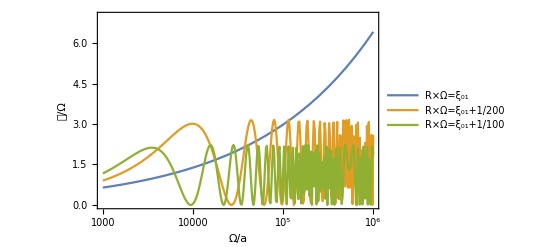

```mathematica
DRResAsyOa=ListLinePlot[{{Re[#1],Re[#2]}&@@@s1,{Re[#1],Re[#2]}&@@@s2,{Re[#1],Re[#2]}&@@@s3},PlotRange->{{10^3,10^6},{0,7}},ScalingFunctions->{"Log","Linear"},PlotLegends->Placed[{"R×Ω=ξ_01","R×Ω=ξ_01+1/200", "R×Ω=ξ_01+1/100","R×Ω=50","𝒞_ℳ/Ω"}
,{0.2,0.7}],FrameLabel->{"Ω/a","𝒞/Ω"},ScalingFunctions->{"Linear","Linear"},Frame->True,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black},GridLines->Automatic]
```

```mathematica
Export["DRRes_Asy_Oa.pdf",DRResAsyOa]
```

DRRes_Asy_Oa.pdf

Higher Ω/a

```mathematica
s11=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,2],10^Oa,3]]},{Oa,3,12,1/10}]
```

{{1000,0.0748224},{1000 10^(1/10),0.0566294},{1000 10^(1/5),0.0502362},{1000 10^(3/10),0.0414028},{1000 10^(2/5),0.0555437},{1000 √10,0.0718099},{1000 10^(3/5),0.052035},{1000 10^(7/10),0.0590869},{1000 10^(4/5),0.103666},{1000 10^(9/10),0.0954262},{10000,0.0928299},{10000 10^(1/10),0.101448},{10000 10^(1/5),0.125408},{10000 10^(3/10),0.126128},{10000 10^(2/5),0.137134},{10000 √10,0.107578},{10000 10^(3/5),0.13223},{10000 10^(7/10),0.124097},{10000 10^(4/5),0.167089},{10000 10^(9/10),0.146335},{100000,0.179523},{100000 10^(1/10),0.207536},{100000 10^(1/5),0.180384},{100000 10^(3/10),0.19235},{100000 10^(2/5),0.208004},{100000 √10,0.251316},{100000 10^(3/5),0.276139},{100000 10^(7/10),0.265504},{100000 10^(4/5),0.282213},{100000 10^(9/10),0.341287},{1000000,0.360343},{1000000 10^(1/10),0.360344},{1000000 10^(1/5),0.384156},{1000000 10^(3/10),0.452732},{1000000 10^(2/5),0.46102},{1000000 √10,0.497782},{1000000 10^(3/5),0.547198},{1000000 10^(7/10),0.592969},{1000000 10^(4/5),0.613701},{1000000 10^(9/10),0.656143},{10000000,0.748854},{10000000 10^(1/10),0.805775},{10000000 10^(1/5),0.837009},{10000000 10^(3/10),0.904191},{10000000 10^(2/5),0.984676},{10000000 √10,1.06982},{10000000 10^(3/5),1.1555},{10000000 10^(7/10),1.25344},{10000000 10^(4/5),1.30929},{10000000 10^(9/10),1.4324},{100000000,1.53215},{100000000 10^(1/10),1.66682},{100000000 10^(1/5),1.8189},{100000000 10^(3/10),1.92829},{100000000 10^(2/5),2.0783},{100000000 √10,2.2796},{100000000 10^(3/5),2.43345},{100000000 10^(7/10),2.61138},{100000000 10^(4/5),2.85889},{100000000 10^(9/10),3.05771},{1000000000,3.29693},{1000000000 10^(1/10),3.5647},{1000000000 10^(1/5),3.84444},{1000000000 10^(3/10),4.14401},{1000000000 10^(2/5),4.46392},{1000000000 √10,4.86205},{1000000000 10^(3/5),5.20346},{1000000000 10^(7/10),5.62938},{1000000000 10^(4/5),6.10728},{1000000000 10^(9/10),6.55332},{10000000000,7.10605},{10000000000 10^(1/10),7.64251},{10000000000 10^(1/5),8.25285},{10000000000 10^(3/10),8.94497},{10000000000 10^(2/5),9.63295},{10000000000 √10,10.3941},{10000000000 10^(3/5),11.2261},{10000000000 10^(7/10),12.1074},{10000000000 10^(4/5),13.1131},{10000000000 10^(9/10),14.1137},{100000000000,15.2764},{100000000000 10^(1/10),16.4643},{100000000000 10^(1/5),17.8098},{100000000000 10^(3/10),19.1879},{100000000000 10^(2/5),20.7157},{100000000000 √10,22.3679},{100000000000 10^(3/5),24.1814},{100000000000 10^(7/10),26.1215},{100000000000 10^(4/5),28.1626},{100000000000 10^(9/10),30.4448},{1000000000000,32.873}}

```mathematica
s22=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,2]+1/200,10^Oa,3]]},{Oa,3,12,1/100}]
```

{{1000,0.345643},{1000 10^(1/100),0.337007},{1000 10^(1/50),0.378663},{1000 10^(3/100),0.349355},{1000 10^(1/25),0.386197},{1000 10^(1/20),0.352255},{1000 10^(3/50),0.360942},{1000 10^(7/100),0.379394},{1000 10^(2/25),0.383597},{1000 10^(9/100),0.372956},{1000 10^(1/10),0.370227},{1000 10^(11/100),0.41253},{1000 10^(3/25),0.378634},{1000 10^(13/100),0.422142},{1000 10^(7/50),0.405134},{1000 10^(3/20),0.393402},{1000 10^(4/25),0.39815},{1000 10^(17/100),0.42057},{1000 10^(9/50),0.44103},{1000 10^(19/100),0.404144},{1000 10^(1/5),0.448281},{1000 10^(21/100),0.444444},{1000 10^(11/50),0.435382},{1000 10^(23/100),0.447608},{1000 10^(6/25),0.469539},{1000 10^(1/4),0.435981},{1000 10^(13/50),0.478105},{1000 10^(27/100),0.454709},{1000 10^(7/25),0.450723},{1000 10^(29/100),0.467293},{1000 10^(3/10),0.49873},{1000 10^(31/100),0.460942},{1000 10^(8/25),0.497752},{1000 10^(33/100),0.513043},{1000 10^(17/50),0.511153},{1000 10^(7/20),0.483236},{1000 10^(9/25),0.53035},{1000 10^(37/100),0.509781},{1000 10^(19/50),0.511489},{1000 10^(39/100),0.542153},{1000 10^(2/5),0.523168},{1000 10^(41/100),0.559742},{1000 10^(21/50),0.563857},{1000 10^(43/100),0.566535},{1000 10^(11/25),0.536906},{1000 10^(9/20),0.56002},{1000 10^(23/50),0.568549},{1000 10^(47/100),0.554992},{1000 10^(12/25),0.602299},{1000 10^(49/100),0.608195},{1000 √10,0.616922},{1000 10^(51/100),0.582254},{1000 10^(13/25),0.609211},{1000 10^(53/100),0.606269},{1000 10^(27/50),0.625864},{1000 10^(11/20),0.611593},{1000 10^(14/25),0.622206},{1000 10^(57/100),0.66973},{1000 10^(29/50),0.665929},{1000 10^(59/100),0.685876},{1000 10^(3/5),0.651599},{1000 10^(61/100),0.66001},{1000 10^(31/50),0.6942},{1000 10^(63/100),0.676547},{1000 10^(16/25),0.694368},{1000 10^(13/20),0.720303},{1000 10^(33/50),0.730056},{1000 10^(67/100),0.720848},{1000 10^(17/25),0.722282},{1000 10^(69/100),0.769241},{1000 10^(7/10),0.757948},{1000 10^(71/100),0.793402},{1000 10^(18/25),0.793543},{1000 10^(73/100),0.804629},{1000 10^(37/50),0.824314},{1000 10^(3/4),0.799772},{1000 10^(19/25),0.82115},{1000 10^(77/100),0.834001},{1000 10^(39/50),0.850451},{1000 10^(79/100),0.839712},{1000 10^(4/5),0.853757},{1000 10^(81/100),0.860016},{1000 10^(41/50),0.91077},{1000 10^(83/100),0.926127},{1000 10^(21/25),0.917714},{1000 10^(17/20),0.939259},{1000 10^(43/50),0.938282},{1000 10^(87/100),0.973649},{1000 10^(22/25),0.951586},{1000 10^(89/100),0.995955},{1000 10^(9/10),1.01043},{1000 10^(91/100),0.996734},{1000 10^(23/25),1.02765},{1000 10^(93/100),1.01907},{1000 10^(47/50),1.056},{1000 10^(19/20),1.07546},{1000 10^(24/25),1.07715},{1000 10^(97/100),1.0755},{1000 10^(49/50),1.12124},{1000 10^(99/100),1.13388},{10000,1.13166},{10000 10^(1/100),1.17524},{10000 10^(1/50),1.16052},{10000 10^(3/100),1.21186},{10000 10^(1/25),1.18905},{10000 10^(1/20),1.24447},{10000 10^(3/50),1.25375},{10000 10^(7/100),1.24896},{10000 10^(2/25),1.26318},{10000 10^(9/100),1.29537},{10000 10^(1/10),1.33754},{10000 10^(11/100),1.31629},{10000 10^(3/25),1.34066},{10000 10^(13/100),1.3546},{10000 10^(7/50),1.39592},{10000 10^(3/20),1.39034},{10000 10^(4/25),1.41042},{10000 10^(17/100),1.47232},{10000 10^(9/50),1.48853},{10000 10^(19/100),1.48846},{10000 10^(1/5),1.52581},{10000 10^(21/100),1.51002},{10000 10^(11/50),1.53023},{10000 10^(23/100),1.59208},{10000 10^(6/25),1.58914},{10000 10^(1/4),1.62317},{10000 10^(13/50),1.6397},{10000 10^(27/100),1.66451},{10000 10^(7/25),1.66186},{10000 10^(29/100),1.67972},{10000 10^(3/10),1.70975},{10000 10^(31/100),1.74973},{10000 10^(8/25),1.77756},{10000 10^(33/100),1.78445},{10000 10^(17/50),1.79272},{10000 10^(7/20),1.81635},{10000 10^(9/25),1.85519},{10000 10^(37/100),1.83843},{10000 10^(19/50),1.89156},{10000 10^(39/100),1.90886},{10000 10^(2/5),1.88584},{10000 10^(41/100),1.92108},{10000 10^(21/50),1.91842},{10000 10^(43/100),1.93486},{10000 10^(11/25),1.98146},{10000 10^(9/20),2.00165},{10000 10^(23/50),2.00305},{10000 10^(47/100),1.98198},{10000 10^(12/25),2.0339},{10000 10^(49/100),2.00469},{10000 √10,2.03457},{10000 10^(51/100),2.03052},{10000 10^(13/25),2.05218},{10000 10^(53/100),2.03022},{10000 10^(27/50),2.04196},{10000 10^(11/20),2.04118},{10000 10^(14/25),2.0503},{10000 10^(57/100),2.00485},{10000 10^(29/50),1.99614},{10000 10^(59/100),2.01854},{10000 10^(3/5),1.97395},{10000 10^(61/100),1.99096},{10000 10^(31/50),1.97228},{10000 10^(63/100),1.9176},{10000 10^(16/25),1.91101},{10000 10^(13/20),1.86118},{10000 10^(33/50),1.8341},{10000 10^(67/100),1.80592},{10000 10^(17/25),1.75513},{10000 10^(69/100),1.74187},{10000 10^(7/10),1.66384},{10000 10^(71/100),1.61182},{10000 10^(18/25),1.56429},{10000 10^(73/100),1.52832},{10000 10^(37/50),1.47358},{10000 10^(3/4),1.41044},{10000 10^(19/25),1.35269},{10000 10^(77/100),1.25139},{10000 10^(39/50),1.20848},{10000 10^(79/100),1.10728},{10000 10^(4/5),1.01502},{10000 10^(81/100),0.964592},{10000 10^(41/50),0.863425},{10000 10^(83/100),0.787964},{10000 10^(21/25),0.72203},{10000 10^(17/20),0.655281},{10000 10^(43/50),0.574886},{10000 10^(87/100),0.493967},{10000 10^(22/25),0.391205},{10000 10^(89/100),0.348429},{10000 10^(9/10),0.285756},{10000 10^(91/100),0.206656},{10000 10^(23/25),0.131375},{10000 10^(93/100),0.120463},{10000 10^(47/50),0.0879085},{10000 10^(19/20),0.0223054},{10000 10^(24/25),0.00733121},{10000 10^(97/100),0.0249956},{10000 10^(49/50),0.0503739},{10000 10^(99/100),0.064552},{100000,0.0912706},{100000 10^(1/100),0.167505},{100000 10^(1/50),0.230886},{100000 10^(3/100),0.281347},{100000 10^(1/25),0.416809},{100000 10^(1/20),0.501071},{100000 10^(3/50),0.613621},{100000 10^(7/100),0.757554},{100000 10^(2/25),0.911133},{100000 10^(9/100),1.04458},{100000 10^(1/10),1.21159},{100000 10^(11/100),1.3988},{100000 10^(3/25),1.5395},{100000 10^(13/100),1.65719},{100000 10^(7/50),1.82783},{100000 10^(3/20),1.94352},{100000 10^(4/25),2.00669},{100000 10^(17/100),2.07407},{100000 10^(9/50),2.11608},{100000 10^(19/100),2.14709},{100000 10^(1/5),2.07649},{100000 10^(21/100),2.00813},{100000 10^(11/50),1.93783},{100000 10^(23/100),1.79763},{100000 10^(6/25),1.63234},{100000 10^(1/4),1.43263},{100000 10^(13/50),1.20071},{100000 10^(27/100),0.983298},{100000 10^(7/25),0.740614},{100000 10^(29/100),0.533925},{100000 10^(3/10),0.326381},{100000 10^(31/100),0.161577},{100000 10^(8/25),0.0841345},{100000 10^(33/100),0.00932351},{100000 10^(17/50),0.0243867},{100000 10^(7/20),0.147501},{100000 10^(9/25),0.308031},{100000 10^(37/100),0.546133},{100000 10^(19/50),0.804528},{100000 10^(39/100),1.1129},{100000 10^(2/5),1.39775},{100000 10^(41/100),1.70006},{100000 10^(21/50),1.93622},{100000 10^(43/100),2.06259},{100000 10^(11/25),2.15397},{100000 10^(9/20),2.10018},{100000 10^(23/50),1.89902},{100000 10^(47/100),1.67126},{100000 10^(12/25),1.32676},{100000 10^(49/100),0.940534},{100000 √10,0.559267},{100000 10^(51/100),0.275802},{100000 10^(13/25),0.0871163},{100000 10^(53/100),0.0457354},{100000 10^(27/50),0.178518},{100000 10^(11/20),0.425253},{100000 10^(14/25),0.853161},{100000 10^(57/100),1.31692},{100000 10^(29/50),1.74815},{100000 10^(59/100),2.03298},{100000 10^(3/5),2.15162},{100000 10^(61/100),2.0355},{100000 10^(31/50),1.65954},{100000 10^(63/100),1.20279},{100000 10^(16/25),0.675797},{100000 10^(13/20),0.229017},{100000 10^(33/50),0.020355},{100000 10^(67/100),0.107416},{100000 10^(17/25),0.497429},{100000 10^(69/100),1.08191},{100000 10^(7/10),1.65406},{100000 10^(71/100),2.05111},{100000 10^(18/25),2.08713},{100000 10^(73/100),1.77332},{100000 10^(37/50),1.15884},{100000 10^(3/4),0.479937},{100000 10^(19/25),0.0910333},{100000 10^(77/100),0.119939},{100000 10^(39/50),0.610291},{100000 10^(79/100),1.33288},{100000 10^(4/5),1.96065},{100000 10^(81/100),2.11922},{100000 10^(41/50),1.72108},{100000 10^(83/100),0.903848},{100000 10^(21/25),0.203156},{100000 10^(17/20),0.0502077},{100000 10^(43/50),0.558921},{100000 10^(87/100),1.45781},{100000 10^(22/25),2.06451},{100000 10^(89/100),1.95382},{100000 10^(9/10),1.14588},{100000 10^(91/100),0.275112},{100000 10^(23/25),0.0489533},{100000 10^(93/100),0.772665},{100000 10^(47/50),1.79099},{100000 10^(19/20),2.09887},{100000 10^(24/25),1.37861},{100000 10^(97/100),0.301464},{100000 10^(49/50),0.103343},{100000 10^(99/100),1.01072},{1000000,1.99815},{1000000 10^(1/100),1.90451},{1000000 10^(1/50),0.688962},{1000000 10^(3/100),0.0347042},{1000000 10^(1/25),0.810657},{1000000 10^(1/20),2.00442},{1000000 10^(3/50),1.76631},{1000000 10^(7/100),0.461658},{1000000 10^(2/25),0.160184},{1000000 10^(9/100),1.41708},{1000000 10^(1/10),2.12868},{1000000 10^(11/100),0.873896},{1000000 10^(3/25),0.0118914},{1000000 10^(13/100),1.24989},{1000000 10^(7/50),2.0964},{1000000 10^(3/20),0.771157},{1000000 10^(4/25),0.125819},{1000000 10^(17/100),1.61955},{1000000 10^(9/50),1.84873},{1000000 10^(19/100),0.170685},{1000000 10^(1/5),0.757675},{1000000 10^(21/100),2.14994},{1000000 10^(11/50),0.658802},{1000000 10^(23/100),0.367745},{1000000 10^(6/25),2.07509},{1000000 10^(1/4),0.866005},{1000000 10^(13/50),0.339593},{1000000 10^(27/100),2.13622},{1000000 10^(7/25),0.593517},{1000000 10^(29/100),0.685608},{1000000 10^(3/10),2.04975},{1000000 10^(31/100),0.117778},{1000000 10^(8/25),1.55566},{1000000 10^(33/100),1.25871},{1000000 10^(17/50),0.368224},{1000000 10^(7/20),2.08007},{1000000 10^(9/25),0.0418673},{1000000 10^(37/100),1.98132},{1000000 10^(19/50),0.415539},{1000000 10^(39/100),1.50761},{1000000 10^(2/5),0.867361},{1000000 10^(41/100),1.14459},{1000000 10^(21/50),1.11437},{1000000 10^(43/100),1.08984},{1000000 10^(11/25),0.997605},{1000000 10^(9/20),1.30386},{1000000 10^(23/50),0.635196},{1000000 10^(47/100),1.82882},{1000000 10^(12/25),0.106057},{1000000 10^(49/100),2.12217},{1000000 √10,0.20005},{1000000 10^(51/100),1.4318},{1000000 10^(13/25),1.49797},{1000000 10^(53/100),0.0993523},{1000000 10^(27/50),1.99656},{1000000 10^(11/20),1.05793},{1000000 10^(14/25),0.114579},{1000000 10^(57/100),1.8857},{1000000 10^(29/50),1.57412},{1000000 10^(59/100),0.0899905},{1000000 10^(3/5),0.810699},{1000000 10^(61/100),2.0754},{1000000 10^(31/50),1.55699},{1000000 10^(63/100),0.279207},{1000000 10^(16/25),0.111695},{1000000 10^(13/20),1.00975},{1000000 10^(33/50),1.89782},{1000000 10^(67/100),2.12025},{1000000 10^(17/25),1.81839},{1000000 10^(69/100),1.28767},{1000000 10^(7/10),0.820647},{1000000 10^(71/100),0.55296},{1000000 10^(18/25),0.405086},{1000000 10^(73/100),0.428905},{1000000 10^(37/50),0.544039},{1000000 10^(3/4),0.830699},{1000000 10^(19/25),1.31483},{1000000 10^(77/100),1.85455},{1000000 10^(39/50),2.12409},{1000000 10^(79/100),1.71212},{1000000 10^(4/5),0.60851},{1000000 10^(81/100),0.044053},{1000000 10^(41/50),1.07903},{1000000 10^(83/100),2.14648},{1000000 10^(21/25),0.771285},{1000000 10^(17/20),0.253796},{1000000 10^(43/50),2.12679},{1000000 10^(87/100),0.499885},{1000000 10^(22/25),1.09671},{1000000 10^(89/100),1.42903},{1000000 10^(9/10),0.594977},{1000000 10^(91/100),1.51928},{1000000 10^(23/25),0.944122},{1000000 10^(93/100),0.671991},{1000000 10^(47/50),2.03671},{1000000 10^(19/20),0.217942},{1000000 10^(24/25),0.792674},{1000000 10^(97/100),2.10506},{1000000 10^(49/50),1.44031},{1000000 10^(99/100),0.30024},{10000000,0.0268798},{10000000 10^(1/100),0.295778},{10000000 10^(1/50),0.561067},{10000000 10^(3/100),0.584099},{10000000 10^(1/25),0.356657},{10000000 10^(1/20),0.0825487},{10000000 10^(3/50),0.189349},{10000000 10^(7/100),1.28652},{10000000 10^(2/25),2.15203},{10000000 10^(9/100),0.711037},{10000000 10^(1/10),0.453274},{10000000 10^(11/100),2.10718},{10000000 10^(3/25),0.017887},{10000000 10^(13/100),2.12359},{10000000 10^(7/50),0.137895},{10000000 10^(3/20),1.40988},{10000000 10^(4/25),1.87743},{10000000 10^(17/100),0.424316},{10000000 10^(9/50),0.0755527},{10000000 10^(19/100),0.535532},{10000000 10^(1/5),0.811546},{10000000 10^(21/100),0.72929},{10000000 10^(11/50),0.266142},{10000000 10^(23/100),0.0884801},{10000000 10^(6/25),1.30479},{10000000 10^(1/4),1.97976},{10000000 10^(13/50),0.0485588},{10000000 10^(27/100),2.07554},{10000000 10^(7/25),0.0453218},{10000000 10^(29/100),1.88023},{10000000 10^(3/10),1.57161},{10000000 10^(31/100),0.322508},{10000000 10^(8/25),0.0124936},{10000000 10^(33/100),0.0360807},{10000000 10^(17/50),0.119763},{10000000 10^(7/20),0.927094},{10000000 10^(9/25),2.1287},{10000000 10^(37/100),0.437133},{10000000 10^(19/50),1.47436},{10000000 10^(39/100),0.294062},{10000000 10^(2/5),2.09181},{10000000 10^(41/100),1.60727},{10000000 10^(21/50),0.967518},{10000000 10^(43/100),0.98629},{10000000 10^(11/25),1.74348},{10000000 10^(9/20),1.89727},{10000000 10^(23/50),0.0265999},{10000000 10^(47/100),2.12561},{10000000 10^(12/25),0.170588},{10000000 10^(49/100),0.551884},{10000000 √10,1.34102},{10000000 10^(51/100),1.18644},{10000000 10^(13/25),0.228079},{10000000 10^(53/100),0.722386},{10000000 10^(27/50),1.68702},{10000000 10^(11/20),1.07136},{10000000 10^(14/25),0.0169458},{10000000 10^(57/100),0.149917},{10000000 10^(29/50),0.0145627},{10000000 10^(59/100),0.956955},{10000000 10^(3/5),1.77116},{10000000 10^(61/100),0.868509},{10000000 10^(31/50),0.0610569},{10000000 10^(63/100),0.217547},{10000000 10^(16/25),0.0372082},{10000000 10^(13/20),1.63606},{10000000 10^(33/50),0.516609},{10000000 10^(67/100),2.07615},{10000000 10^(17/25),2.06569},{10000000 10^(69/100),2.04028},{10000000 10^(7/10),0.264806},{10000000 10^(71/100),2.01002},{10000000 10^(18/25),0.717339},{10000000 10^(73/100),0.654604},{10000000 10^(37/50),1.95977},{10000000 10^(3/4),0.340089},{10000000 10^(19/25),2.00953},{10000000 10^(77/100),2.1151},{10000000 10^(39/50),1.12033},{10000000 10^(79/100),0.848491},{10000000 10^(4/5),0.0530273},{10000000 10^(81/100),0.0425613},{10000000 10^(41/50),1.09593},{10000000 10^(83/100),0.52819},{10000000 10^(21/25),1.35794},{10000000 10^(17/20),0.307967},{10000000 10^(43/50),1.73206},{10000000 10^(87/100),0.417787},{10000000 10^(22/25),1.12554},{10000000 10^(89/100),1.37881},{10000000 10^(9/10),2.14534},{10000000 10^(91/100),1.90783},{10000000 10^(23/25),0.137265},{10000000 10^(93/100),0.200462},{10000000 10^(47/50),0.311116},{10000000 10^(19/20),1.40356},{10000000 10^(24/25),1.64021},{10000000 10^(97/100),0.0301493},{10000000 10^(49/50),0.798109},{10000000 10^(99/100),0.0444953},{100000000,2.00949},{100000000 10^(1/100),1.84606},{100000000 10^(1/50),0.241676},{100000000 10^(3/100),0.0603008},{100000000 10^(1/25),2.0478},{100000000 10^(1/20),1.49026},{100000000 10^(3/50),1.5966},{100000000 10^(7/100),2.13944},{100000000 10^(2/25),0.224711},{100000000 10^(9/100),0.855657},{100000000 10^(1/10),0.813307},{100000000 10^(11/100),0.603512},{100000000 10^(3/25),1.41117},{100000000 10^(13/100),0.775854},{100000000 10^(7/50),2.13293},{100000000 10^(3/20),1.02623},{100000000 10^(4/25),1.66644},{100000000 10^(17/100),0.565945},{100000000 10^(9/50),1.59448},{100000000 10^(19/100),0.44306},{100000000 10^(1/5),1.80105},{100000000 10^(21/100),0.699161},{100000000 10^(11/50),1.49476},{100000000 10^(23/100),1.24317},{100000000 10^(6/25),1.89171},{100000000 10^(1/4),1.46756},{100000000 10^(13/50),2.07172},{100000000 10^(27/100),0.693886},{100000000 10^(7/25),1.75604},{100000000 10^(29/100),0.137955},{100000000 10^(3/10),0.0532043},{100000000 10^(31/100),0.0505022},{100000000 10^(8/25),0.223956},{100000000 10^(33/100),1.56085},{100000000 10^(17/50),1.83611},{100000000 10^(7/20),0.0215173},{100000000 10^(9/25),1.6996},{100000000 10^(37/100),1.17856},{100000000 10^(19/50),0.245265},{100000000 10^(39/100),2.08452},{100000000 10^(2/5),1.38204},{100000000 10^(41/100),0.282482},{100000000 10^(21/50),0.0895349},{100000000 10^(43/100),0.351047},{100000000 10^(11/25),1.79534},{100000000 10^(9/20),0.718496},{100000000 10^(23/50),2.10332},{100000000 10^(47/100),1.78402},{100000000 10^(12/25),2.09185},{100000000 10^(49/100),0.0847415},{100000000 √10,0.295198},{100000000 10^(51/100),0.146353},{100000000 10^(13/25),1.48105},{100000000 10^(53/100),1.21952},{100000000 10^(27/50),0.999272},{100000000 10^(11/20),1.10915},{100000000 10^(14/25),0.762299},{100000000 10^(57/100),0.123339},{100000000 10^(29/50),1.6815},{100000000 10^(59/100),0.0532741},{100000000 10^(3/5),0.240456},{100000000 10^(61/100),0.224563},{100000000 10^(31/50),2.11584},{100000000 10^(63/100),0.657803},{100000000 10^(16/25),0.0482013},{100000000 10^(13/20),0.359759},{100000000 10^(33/50),0.595723},{100000000 10^(67/100),0.735912},{100000000 10^(17/25),1.04947},{100000000 10^(69/100),1.78738},{100000000 10^(7/10),1.9044},{100000000 10^(71/100),0.0285693},{100000000 10^(18/25),1.61885},{100000000 10^(73/100),2.01896},{100000000 10^(37/50),0.607952},{100000000 10^(3/4),2.09089},{100000000 10^(19/25),2.12645},{100000000 10^(77/100),0.0637141},{100000000 10^(39/50),0.494487},{100000000 10^(79/100),0.353326},{100000000 10^(4/5),1.16934},{100000000 10^(81/100),1.87351},{100000000 10^(41/50),1.44588},{100000000 10^(83/100),0.165361},{100000000 10^(21/25),0.73182},{100000000 10^(17/20),2.13237},{100000000 10^(43/50),1.35499},{100000000 10^(87/100),0.803822},{100000000 10^(22/25),1.64433},{100000000 10^(89/100),1.0024},{100000000 10^(9/10),2.07745},{100000000 10^(91/100),0.959031},{100000000 10^(23/25),2.1152},{100000000 10^(93/100),0.359188},{100000000 10^(47/50),0.169634},{100000000 10^(19/20),1.25206},{100000000 10^(24/25),1.94767},{100000000 10^(97/100),0.0298287},{100000000 10^(49/50),1.36194},{100000000 10^(99/100),2.12169},{1000000000,2.06197},{1000000000 10^(1/100),0.0686106},{1000000000 10^(1/50),1.02823},{1000000000 10^(3/100),0.293811},{1000000000 10^(1/25),0.265014},{1000000000 10^(1/20),0.432034},{1000000000 10^(3/50),2.12892},{1000000000 10^(7/100),0.0769901},{1000000000 10^(2/25),1.1978},{1000000000 10^(9/100),1.81956},{1000000000 10^(1/10),0.486947},{1000000000 10^(11/100),2.13278},{1000000000 10^(3/25),0.913847},{1000000000 10^(13/100),1.11387},{1000000000 10^(7/50),2.04318},{1000000000 10^(3/20),1.75534},{1000000000 10^(4/25),1.31173},{1000000000 10^(17/100),2.13273},{1000000000 10^(9/50),0.116317},{1000000000 10^(19/100),0.863664},{1000000000 10^(1/5),0.170482},{1000000000 10^(21/100),0.654112},{1000000000 10^(11/50),2.00954},{1000000000 10^(23/100),2.14329},{1000000000 10^(6/25),0.516863},{1000000000 10^(1/4),1.51435},{1000000000 10^(13/50),0.974521},{1000000000 10^(27/100),1.59578},{1000000000 10^(7/25),0.598883},{1000000000 10^(29/100),0.0878807},{1000000000 10^(3/10),0.465833},{1000000000 10^(31/100),0.00741843},{1000000000 10^(8/25),1.27977},{1000000000 10^(33/100),2.15354},{1000000000 10^(17/50),2.12138},{1000000000 10^(7/20),0.0516081},{1000000000 10^(9/25),0.959466},{1000000000 10^(37/100),1.78571},{1000000000 10^(19/50),1.61662},{1000000000 10^(39/100),1.73015},{1000000000 10^(2/5),1.51574},{1000000000 10^(41/100),0.198555},{1000000000 10^(21/50),1.13909},{1000000000 10^(43/100),0.0441237},{1000000000 10^(11/25),2.04423},{1000000000 10^(9/20),0.902948},{1000000000 10^(23/50),1.65922},{1000000000 10^(47/100),1.97858},{1000000000 10^(12/25),1.17521},{1000000000 10^(49/100),0.779877},{1000000000 √10,2.08857},{1000000000 10^(51/100),2.04088},{1000000000 10^(13/25),1.79578},{1000000000 10^(53/100),0.0452762},{1000000000 10^(27/50),0.393506},{1000000000 10^(11/20),1.13615},{1000000000 10^(14/25),1.00178},{1000000000 10^(57/100),0.010922},{1000000000 10^(29/50),1.5631},{1000000000 10^(59/100),0.342527},{1000000000 10^(3/5),0.783786},{1000000000 10^(61/100),1.27775},{1000000000 10^(31/50),1.36476},{1000000000 10^(63/100),0.106547},{1000000000 10^(16/25),0.0902743},{1000000000 10^(13/20),0.209788},{1000000000 10^(33/50),2.15407},{1000000000 10^(67/100),1.34827},{1000000000 10^(17/25),0.664752},{1000000000 10^(69/100),1.99158},{1000000000 10^(7/10),0.448961},{1000000000 10^(71/100),0.0154838},{1000000000 10^(18/25),1.96672},{1000000000 10^(73/100),2.119},{1000000000 10^(37/50),0.0782936},{1000000000 10^(3/4),0.597547},{1000000000 10^(19/25),1.00478},{1000000000 10^(77/100),1.33005},{1000000000 10^(39/50),1.64338},{1000000000 10^(79/100),2.15961},{1000000000 10^(4/5),1.82614},{1000000000 10^(81/100),1.94306},{1000000000 10^(41/50),0.748947},{1000000000 10^(83/100),1.76898},{1000000000 10^(21/25),0.956623},{1000000000 10^(17/20),0.327843},{1000000000 10^(43/50),1.58605},{1000000000 10^(87/100),0.378936},{1000000000 10^(22/25),0.602259},{1000000000 10^(89/100),1.78933},{1000000000 10^(9/10),0.700053},{1000000000 10^(91/100),2.04065},{1000000000 10^(23/25),0.163047},{1000000000 10^(93/100),2.02843},{1000000000 10^(47/50),0.550166},{1000000000 10^(19/20),0.00438581},{1000000000 10^(24/25),1.04263},{1000000000 10^(97/100),0.0595829},{1000000000 10^(49/50),0.7935},{1000000000 10^(99/100),0.182741},{10000000000,1.88999},{10000000000 10^(1/100),0.752846},{10000000000 10^(1/50),1.73267},{10000000000 10^(3/100),0.303754},{10000000000 10^(1/25),0.448027},{10000000000 10^(1/20),1.66048},{10000000000 10^(3/50),2.10317},{10000000000 10^(7/100),1.51419},{10000000000 10^(2/25),0.184333},{10000000000 10^(9/100),0.0449424},{10000000000 10^(1/10),0.597344},{10000000000 10^(11/100),0.122443},{10000000000 10^(3/25),2.14684},{10000000000 10^(13/100),0.883761},{10000000000 10^(7/50),1.89274},{10000000000 10^(3/20),1.82998},{10000000000 10^(4/25),1.99319},{10000000000 10^(17/100),2.02014},{10000000000 10^(9/50),1.74576},{10000000000 10^(19/100),0.275325},{10000000000 10^(1/5),2.08771},{10000000000 10^(21/100),0.337521},{10000000000 10^(11/50),2.15986},{10000000000 10^(23/100),0.0623435},{10000000000 10^(6/25),0.545005},{10000000000 10^(1/4),1.91108},{10000000000 10^(13/50),0.278534},{10000000000 10^(27/100),2.11234},{10000000000 10^(7/25),2.12229},{10000000000 10^(29/100),0.576483},{10000000000 10^(3/10),1.42772},{10000000000 10^(31/100),0.247543},{10000000000 10^(8/25),0.0177328},{10000000000 10^(33/100),1.95719},{10000000000 10^(17/50),0.32529},{10000000000 10^(7/20),0.0653476},{10000000000 10^(9/25),0.0589547},{10000000000 10^(37/100),2.04213},{10000000000 10^(19/50),1.90957},{10000000000 10^(39/100),1.49618},{10000000000 10^(2/5),1.87496},{10000000000 10^(41/100),0.986271},{10000000000 10^(21/50),1.46246},{10000000000 10^(43/100),0.519771},{10000000000 10^(11/25),0.00136746},{10000000000 10^(9/20),2.13623},{10000000000 10^(23/50),0.713605},{10000000000 10^(47/100),0.497607},{10000000000 10^(12/25),1.87006},{10000000000 10^(49/100),0.798418},{10000000000 √10,0.352425},{10000000000 10^(51/100),2.14082},{10000000000 10^(13/25),0.231042},{10000000000 10^(53/100),0.822158},{10000000000 10^(27/50),0.520335},{10000000000 10^(11/20),1.78408},{10000000000 10^(14/25),1.62547},{10000000000 10^(57/100),1.69726},{10000000000 10^(29/50),0.0485039},{10000000000 10^(59/100),0.0617678},{10000000000 10^(3/5),1.17808},{10000000000 10^(61/100),0.126028},{10000000000 10^(31/50),1.56553},{10000000000 10^(63/100),0.123557},{10000000000 10^(16/25),1.64906},{10000000000 10^(13/20),0.9795},{10000000000 10^(33/50),0.925458},{10000000000 10^(67/100),0.438311},{10000000000 10^(17/25),1.75007},{10000000000 10^(69/100),0.45546},{10000000000 10^(7/10),1.40206},{10000000000 10^(71/100),0.0888696},{10000000000 10^(18/25),0.411508},{10000000000 10^(73/100),0.692596},{10000000000 10^(37/50),1.06432},{10000000000 10^(3/4),2.08521},{10000000000 10^(19/25),1.81085},{10000000000 10^(77/100),1.70562},{10000000000 10^(39/50),0.245424},{10000000000 10^(79/100),1.43467},{10000000000 10^(4/5),2.11404},{10000000000 10^(81/100),1.355},{10000000000 10^(41/50),1.1688},{10000000000 10^(83/100),0.131846},{10000000000 10^(21/25),1.96579},{10000000000 10^(17/20),2.09997},{10000000000 10^(43/50),2.13938},{10000000000 10^(87/100),1.79059},{10000000000 10^(22/25),2.14126},{10000000000 10^(89/100),1.85358},{10000000000 10^(9/10),1.72832},{10000000000 10^(91/100),0.38811},{10000000000 10^(23/25),0.313311},{10000000000 10^(93/100),0.146946},{10000000000 10^(47/50),0.294158},{10000000000 10^(19/20),1.88493},{10000000000 10^(24/25),1.56152},{10000000000 10^(97/100),1.26011},{10000000000 10^(49/50),1.68714},{10000000000 10^(99/100),0.237557},{100000000000,1.791},{100000000000 10^(1/100),1.26825},{100000000000 10^(1/50),1.228},{100000000000 10^(3/100),1.92249},{100000000000 10^(1/25),1.29416},{100000000000 10^(1/20),0.385403},{100000000000 10^(3/50),0.977318},{100000000000 10^(7/100),0.28502},{100000000000 10^(2/25),1.44363},{100000000000 10^(9/100),2.12808},{100000000000 10^(1/10),2.15706},{100000000000 10^(11/100),0.0273527},{100000000000 10^(3/25),0.494142},{100000000000 10^(13/100),0.0867343},{100000000000 10^(7/50),1.82098},{100000000000 10^(3/20),2.11667},{100000000000 10^(4/25),2.10137},{100000000000 10^(17/100),0.074598},{100000000000 10^(9/50),1.68955},{100000000000 10^(19/100),1.56995},{100000000000 10^(1/5),0.689673},{100000000000 10^(21/100),2.09766},{100000000000 10^(11/50),1.35965},{100000000000 10^(23/100),0.117784},{100000000000 10^(6/25),1.93486},{100000000000 10^(1/4),0.690773},{100000000000 10^(13/50),0.37862},{100000000000 10^(27/100),2.13239},{100000000000 10^(7/25),0.168087},{100000000000 10^(29/100),2.00091},{100000000000 10^(3/10),1.09969},{100000000000 10^(31/100),1.1756},{100000000000 10^(8/25),2.10335},{100000000000 10^(33/100),1.08999},{100000000000 10^(17/50),2.14414},{100000000000 10^(7/20),1.31665},{100000000000 10^(9/25),1.19639},{100000000000 10^(37/100),0.0251235},{100000000000 10^(19/50),1.61236},{100000000000 10^(39/100),0.344398},{100000000000 10^(2/5),0.438989},{100000000000 10^(41/100),1.86238},{100000000000 10^(21/50),0.647529},{100000000000 10^(43/100),0.220715},{100000000000 10^(11/25),0.797838},{100000000000 10^(9/20),0.0782741},{100000000000 10^(23/50),1.42563},{100000000000 10^(47/100),0.483112},{100000000000 10^(12/25),2.07528},{100000000000 10^(49/100),1.53977},{100000000000 √10,0.035164},{100000000000 10^(51/100),1.08523},{100000000000 10^(13/25),0.705115},{100000000000 10^(53/100),0.374422},{100000000000 10^(27/50),1.60766},{100000000000 10^(11/20),2.01296},{100000000000 10^(14/25),0.292395},{100000000000 10^(57/100),1.1407},{100000000000 10^(29/50),2.13824},{100000000000 10^(59/100),1.38242},{100000000000 10^(3/5),0.153105},{100000000000 10^(61/100),0.207419},{100000000000 10^(31/50),2.11979},{100000000000 10^(63/100),2.14679},{100000000000 10^(16/25),0.281408},{100000000000 10^(13/20),1.98204},{100000000000 10^(33/50),2.096},{100000000000 10^(67/100),1.58126},{100000000000 10^(17/25),0.652526},{100000000000 10^(69/100),0.939491},{100000000000 10^(7/10),0.934773},{100000000000 10^(71/100),1.18767},{100000000000 10^(18/25),1.39737},{100000000000 10^(73/100),1.77871},{100000000000 10^(37/50),1.09727},{100000000000 10^(3/4),1.74907},{100000000000 10^(19/25),1.99561},{100000000000 10^(77/100),0.829233},{100000000000 10^(39/50),0.626101},{100000000000 10^(79/100),1.53484},{100000000000 10^(4/5),1.90486},{100000000000 10^(81/100),0.415828},{100000000000 10^(41/50),0.28475},{100000000000 10^(83/100),2.06159},{100000000000 10^(21/25),0.39499},{100000000000 10^(17/20),1.34961},{100000000000 10^(43/50),1.61595},{100000000000 10^(87/100),2.12924},{100000000000 10^(22/25),0.770681},{100000000000 10^(89/100),2.14983},{100000000000 10^(9/10),0.506955},{100000000000 10^(91/100),0.290689},{100000000000 10^(23/25),2.11657},{100000000000 10^(93/100),2.14064},{100000000000 10^(47/50),0.0275488},{100000000000 10^(19/20),0.576551},{100000000000 10^(24/25),0.0402372},{100000000000 10^(97/100),2.14492},{100000000000 10^(49/50),1.50016},{100000000000 10^(99/100),1.41575},{1000000000000,0.0359371}}

```mathematica
s33=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,2]+1/100,10^Oa,3]]},{Oa,3,12,1/100}]
```

{{1000,0.385111},{1000 10^(1/100),0.419187},{1000 10^(1/50),0.42233},{1000 10^(3/100),0.405331},{1000 10^(1/25),0.42909},{1000 10^(1/20),0.443574},{1000 10^(3/50),0.421138},{1000 10^(7/100),0.417682},{1000 10^(2/25),0.422948},{1000 10^(9/100),0.437971},{1000 10^(1/10),0.471799},{1000 10^(11/100),0.457196},{1000 10^(3/25),0.465263},{1000 10^(13/100),0.456223},{1000 10^(7/50),0.49268},{1000 10^(3/20),0.503381},{1000 10^(4/25),0.509309},{1000 10^(17/100),0.50543},{1000 10^(9/50),0.479241},{1000 10^(19/100),0.523727},{1000 10^(1/5),0.490977},{1000 10^(21/100),0.519112},{1000 10^(11/50),0.53748},{1000 10^(23/100),0.535796},{1000 10^(6/25),0.518174},{1000 10^(1/4),0.558524},{1000 10^(13/50),0.533352},{1000 10^(27/100),0.569342},{1000 10^(7/25),0.583808},{1000 10^(29/100),0.578346},{1000 10^(3/10),0.560401},{1000 10^(31/100),0.610532},{1000 10^(8/25),0.592053},{1000 10^(33/100),0.588328},{1000 10^(17/50),0.608091},{1000 10^(7/20),0.641995},{1000 10^(9/25),0.609517},{1000 10^(37/100),0.628544},{1000 10^(19/50),0.639268},{1000 10^(39/100),0.633605},{1000 10^(2/5),0.684856},{1000 10^(41/100),0.662147},{1000 10^(21/50),0.665695},{1000 10^(43/100),0.699639},{1000 10^(11/25),0.697286},{1000 10^(9/20),0.731785},{1000 10^(23/50),0.741565},{1000 10^(47/100),0.725092},{1000 10^(12/25),0.753326},{1000 10^(49/100),0.745801},{1000 √10,0.776058},{1000 10^(51/100),0.759925},{1000 10^(13/25),0.797852},{1000 10^(53/100),0.79703},{1000 10^(27/50),0.791897},{1000 10^(11/20),0.797089},{1000 10^(14/25),0.805959},{1000 10^(57/100),0.86012},{1000 10^(29/50),0.85829},{1000 10^(59/100),0.883953},{1000 10^(3/5),0.855019},{1000 10^(61/100),0.865661},{1000 10^(31/50),0.913791},{1000 10^(63/100),0.89632},{1000 10^(16/25),0.929444},{1000 10^(13/20),0.922849},{1000 10^(33/50),0.934021},{1000 10^(67/100),0.977772},{1000 10^(17/25),0.981251},{1000 10^(69/100),1.00273},{1000 10^(7/10),1.02618},{1000 10^(71/100),1.00515},{1000 10^(18/25),1.03946},{1000 10^(73/100),1.02614},{1000 10^(37/50),1.04233},{1000 10^(3/4),1.0839},{1000 10^(19/25),1.09134},{1000 10^(77/100),1.10135},{1000 10^(39/50),1.10639},{1000 10^(79/100),1.1543},{1000 10^(4/5),1.146},{1000 10^(81/100),1.17674},{1000 10^(41/50),1.16128},{1000 10^(83/100),1.19228},{1000 10^(21/25),1.18516},{1000 10^(17/20),1.24141},{1000 10^(43/50),1.24613},{1000 10^(87/100),1.26997},{1000 10^(22/25),1.24347},{1000 10^(89/100),1.29192},{1000 10^(9/10),1.30975},{1000 10^(91/100),1.30482},{1000 10^(23/25),1.30169},{1000 10^(93/100),1.33518},{1000 10^(47/50),1.36273},{1000 10^(19/20),1.36888},{1000 10^(24/25),1.38424},{1000 10^(97/100),1.39508},{1000 10^(49/50),1.37532},{1000 10^(99/100),1.38689},{10000,1.42592},{10000 10^(1/100),1.39316},{10000 10^(1/50),1.4392},{10000 10^(3/100),1.421},{10000 10^(1/25),1.42509},{10000 10^(1/20),1.46051},{10000 10^(3/50),1.44865},{10000 10^(7/100),1.43699},{10000 10^(2/25),1.44228},{10000 10^(9/100),1.46481},{10000 10^(1/10),1.43727},{10000 10^(11/100),1.46011},{10000 10^(3/25),1.44021},{10000 10^(13/100),1.44866},{10000 10^(7/50),1.40895},{10000 10^(3/20),1.42596},{10000 10^(4/25),1.39475},{10000 10^(17/100),1.39777},{10000 10^(9/50),1.37997},{10000 10^(19/100),1.34694},{10000 10^(1/5),1.33227},{10000 10^(21/100),1.30465},{10000 10^(11/50),1.28761},{10000 10^(23/100),1.23321},{10000 10^(6/25),1.22794},{10000 10^(1/4),1.19534},{10000 10^(13/50),1.13388},{10000 10^(27/100),1.13874},{10000 10^(7/25),1.07071},{10000 10^(29/100),1.0141},{10000 10^(3/10),0.967641},{10000 10^(31/100),0.921454},{10000 10^(8/25),0.875793},{10000 10^(33/100),0.827176},{10000 10^(17/50),0.76981},{10000 10^(7/20),0.712149},{10000 10^(9/25),0.692964},{10000 10^(37/100),0.598981},{10000 10^(19/50),0.558625},{10000 10^(39/100),0.485318},{10000 10^(2/5),0.468208},{10000 10^(41/100),0.410445},{10000 10^(21/50),0.320867},{10000 10^(43/100),0.26763},{10000 10^(11/25),0.255714},{10000 10^(9/20),0.182229},{10000 10^(23/50),0.137653},{10000 10^(47/100),0.123494},{10000 10^(12/25),0.0830325},{10000 10^(49/100),0.0339902},{10000 √10,0.0548157},{10000 10^(51/100),0.0118816},{10000 10^(13/25),0.0012468},{10000 10^(53/100),0.00892767},{10000 10^(27/50),0.0493723},{10000 10^(11/20),0.057306},{10000 10^(14/25),0.0931648},{10000 10^(57/100),0.179262},{10000 10^(29/50),0.212724},{10000 10^(59/100),0.295989},{10000 10^(3/5),0.392678},{10000 10^(61/100),0.443796},{10000 10^(31/50),0.57931},{10000 10^(63/100),0.643944},{10000 10^(16/25),0.789364},{10000 10^(13/20),0.90281},{10000 10^(33/50),0.998733},{10000 10^(67/100),1.11031},{10000 10^(17/25),1.22112},{10000 10^(69/100),1.30394},{10000 10^(7/10),1.35412},{10000 10^(71/100),1.44778},{10000 10^(18/25),1.48505},{10000 10^(73/100),1.50292},{10000 10^(37/50),1.4903},{10000 10^(3/4),1.46457},{10000 10^(19/25),1.44931},{10000 10^(77/100),1.37533},{10000 10^(39/50),1.24561},{10000 10^(79/100),1.12439},{10000 10^(4/5),0.999223},{10000 10^(81/100),0.809195},{10000 10^(41/50),0.645762},{10000 10^(83/100),0.516893},{10000 10^(21/25),0.352737},{10000 10^(17/20),0.208241},{10000 10^(43/50),0.125506},{10000 10^(87/100),0.0383984},{10000 10^(22/25),0.0429403},{10000 10^(89/100),0.0647154},{10000 10^(9/10),0.0972226},{10000 10^(91/100),0.247386},{10000 10^(23/25),0.41891},{10000 10^(93/100),0.601628},{10000 10^(47/50),0.791049},{10000 10^(19/20),0.999742},{10000 10^(24/25),1.23879},{10000 10^(97/100),1.35928},{10000 10^(49/50),1.49317},{10000 10^(99/100),1.49339},{100000,1.45696},{100000 10^(1/100),1.32108},{100000 10^(1/50),1.14504},{100000 10^(3/100),0.909816},{100000 10^(1/25),0.609184},{100000 10^(1/20),0.356844},{100000 10^(3/50),0.174314},{100000 10^(7/100),0.0593238},{100000 10^(2/25),0.0100991},{100000 10^(9/100),0.116736},{100000 10^(1/10),0.341228},{100000 10^(11/100),0.623949},{100000 10^(3/25),0.986387},{100000 10^(13/100),1.24223},{100000 10^(7/50),1.46421},{100000 10^(3/20),1.50026},{100000 10^(4/25),1.4216},{100000 10^(17/100),1.1435},{100000 10^(9/50),0.77778},{100000 10^(19/100),0.447962},{100000 10^(1/5),0.126427},{100000 10^(21/100),0.00112942},{100000 10^(11/50),0.126864},{100000 10^(23/100),0.426877},{100000 10^(6/25),0.843834},{100000 10^(1/4),1.2461},{100000 10^(13/50),1.4679},{100000 10^(27/100),1.47998},{100000 10^(7/25),1.21648},{100000 10^(29/100),0.7465},{100000 10^(3/10),0.325282},{100000 10^(31/100),0.0247885},{100000 10^(8/25),0.119775},{100000 10^(33/100),0.482068},{100000 10^(17/50),1.01137},{100000 10^(7/20),1.43461},{100000 10^(9/25),1.50191},{100000 10^(37/100),1.15563},{100000 10^(19/50),0.609127},{100000 10^(39/100),0.0970112},{100000 10^(2/5),0.0688569},{100000 10^(41/100),0.452095},{100000 10^(21/50),1.12194},{100000 10^(43/100),1.51173},{100000 10^(11/25),1.33712},{100000 10^(9/20),0.740642},{100000 10^(23/50),0.125169},{100000 10^(47/100),0.0614916},{100000 10^(12/25),0.648325},{100000 10^(49/100),1.33336},{100000 √10,1.47963},{100000 10^(51/100),0.90967},{100000 10^(13/25),0.185236},{100000 10^(53/100),0.122447},{100000 10^(27/50),0.817801},{100000 10^(11/20),1.45222},{100000 10^(14/25),1.25165},{100000 10^(57/100),0.387412},{100000 10^(29/50),0.0203511},{100000 10^(59/100),0.682072},{100000 10^(3/5),1.45861},{100000 10^(61/100),1.16483},{100000 10^(31/50),0.2136},{100000 10^(63/100),0.153993},{100000 10^(16/25),1.14203},{100000 10^(13/20),1.47459},{100000 10^(33/50),0.517373},{100000 10^(67/100),0.0505109},{100000 10^(17/25),0.995326},{100000 10^(69/100),1.45254},{100000 10^(7/10),0.418572},{100000 10^(71/100),0.132147},{100000 10^(18/25),1.26286},{100000 10^(73/100),1.18012},{100000 10^(37/50),0.0624268},{100000 10^(3/4),0.687335},{100000 10^(19/25),1.50504},{100000 10^(77/100),0.316846},{100000 10^(39/50),0.404999},{100000 10^(79/100),1.53328},{100000 10^(4/5),0.450037},{100000 10^(81/100),0.36433},{100000 10^(41/50),1.53022},{100000 10^(83/100),0.263299},{100000 10^(21/25),0.654834},{100000 10^(17/20),1.37569},{100000 10^(43/50),0.00550925},{100000 10^(87/100),1.26433},{100000 10^(22/25),0.681867},{100000 10^(89/100),0.420124},{100000 10^(9/10),1.40242},{100000 10^(91/100),0.0216533},{100000 10^(23/25),1.51335},{100000 10^(93/100),0.165571},{100000 10^(47/50),1.24318},{100000 10^(19/20),0.373599},{100000 10^(24/25),1.05865},{100000 10^(97/100),0.500295},{100000 10^(49/50),1.01242},{100000 10^(99/100),0.4366},{1000000,1.20379},{1000000 10^(1/100),0.21266},{1000000 10^(1/50),1.46602},{1000000 10^(3/100),0.0418387},{1000000 10^(1/25),1.45643},{1000000 10^(1/20),0.394425},{1000000 10^(3/50),0.699952},{1000000 10^(7/100),1.30852},{1000000 10^(2/25),0.0135176},{1000000 10^(9/100),1.13952},{1000000 10^(1/10),1.09672},{1000000 10^(11/100),0.00626579},{1000000 10^(3/25),1.01719},{1000000 10^(13/100),1.4072},{1000000 10^(7/50),0.245826},{1000000 10^(3/20),0.228474},{1000000 10^(4/25),1.27019},{1000000 10^(17/100),1.4239},{1000000 10^(9/50),0.555781},{1000000 10^(19/100),0.0491662},{1000000 10^(1/5),0.293231},{1000000 10^(21/100),0.954542},{1000000 10^(11/50),1.44638},{1000000 10^(23/100),1.52007},{1000000 10^(6/25),1.3515},{1000000 10^(1/4),1.09652},{1000000 10^(13/50),0.905691},{1000000 10^(27/100),0.809806},{1000000 10^(7/25),0.791136},{1000000 10^(29/100),0.904153},{1000000 10^(3/10),1.14526},{1000000 10^(31/100),1.36782},{1000000 10^(8/25),1.53822},{1000000 10^(33/100),1.30944},{1000000 10^(17/50),0.625507},{1000000 10^(7/20),0.0500518},{1000000 10^(9/25),0.380463},{1000000 10^(37/100),1.32953},{1000000 10^(19/50),1.20168},{1000000 10^(39/100),0.0494337},{1000000 10^(2/5),0.813712},{1000000 10^(41/100),1.33716},{1000000 10^(21/50),0.0428369},{1000000 10^(43/100),1.40409},{1000000 10^(11/25),0.275644},{1000000 10^(9/20),1.20054},{1000000 10^(23/50),0.304451},{1000000 10^(47/100),1.41096},{1000000 10^(12/25),0.00516624},{1000000 10^(49/100),1.31151},{1000000 √10,0.910232},{1000000 10^(51/100),0.0267487},{1000000 10^(13/25),0.869979},{1000000 10^(53/100),1.49816},{1000000 10^(27/50),1.15435},{1000000 10^(11/20),0.504855},{1000000 10^(14/25),0.184357},{1000000 10^(57/100),0.0870132},{1000000 10^(29/50),0.0512094},{1000000 10^(59/100),0.153262},{1000000 10^(3/5),0.511934},{1000000 10^(61/100),1.15399},{1000000 10^(31/50),1.48866},{1000000 10^(63/100),0.651562},{1000000 10^(16/25),0.10432},{1000000 10^(13/20),1.40288},{1000000 10^(33/50),0.458104},{1000000 10^(67/100),0.912969},{1000000 10^(17/25),0.591973},{1000000 10^(69/100),1.29444},{1000000 10^(7/10),0.021594},{1000000 10^(71/100),0.995908},{1000000 10^(18/25),1.5117},{1000000 10^(73/100),0.893527},{1000000 10^(37/50),0.389462},{1000000 10^(3/4),0.261762},{1000000 10^(19/25),0.351436},{1000000 10^(77/100),0.737238},{1000000 10^(39/50),1.41657},{1000000 10^(79/100),1.18991},{1000000 10^(4/5),0.024676},{1000000 10^(81/100),1.29611},{1000000 10^(41/50),0.343516},{1000000 10^(83/100),1.34351},{1000000 10^(21/25),0.0561868},{1000000 10^(17/20),0.7619},{1000000 10^(43/50),1.4781},{1000000 10^(87/100),1.47293},{1000000 10^(22/25),1.45747},{1000000 10^(89/100),1.50539},{1000000 10^(9/10),0.954462},{1000000 10^(91/100),0.0346092},{1000000 10^(23/25),1.22178},{1000000 10^(93/100),0.414963},{1000000 10^(47/50),1.3677},{1000000 10^(19/20),0.133843},{1000000 10^(24/25),0.211933},{1000000 10^(97/100),0.593044},{1000000 10^(49/50),0.469897},{1000000 10^(99/100),0.0785605},{10000000,0.571208},{10000000 10^(1/100),1.41745},{10000000 10^(1/50),0.142626},{10000000 10^(3/100),0.884458},{10000000 10^(1/25),1.50338},{10000000 10^(1/20),1.34682},{10000000 10^(3/50),1.44959},{10000000 10^(7/100),1.39096},{10000000 10^(2/25),0.117454},{10000000 10^(9/100),1.36132},{10000000 10^(1/10),0.0382359},{10000000 10^(11/100),0.650896},{10000000 10^(3/25),0.969857},{10000000 10^(13/100),0.510146},{10000000 10^(7/50),0.0868187},{10000000 10^(3/20),1.51954},{10000000 10^(4/25),0.12473},{10000000 10^(17/100),0.273322},{10000000 10^(9/50),0.473759},{10000000 10^(19/100),0.0291847},{10000000 10^(1/5),0.962664},{10000000 10^(21/100),0.441522},{10000000 10^(11/50),1.47575},{10000000 10^(23/100),1.48395},{10000000 10^(6/25),1.33933},{10000000 10^(1/4),0.0568929},{10000000 10^(13/50),1.48848},{10000000 10^(27/100),1.0492},{10000000 10^(7/25),1.14449},{10000000 10^(29/100),1.43873},{10000000 10^(3/10),0.0739179},{10000000 10^(31/100),0.521168},{10000000 10^(8/25),0.6063},{10000000 10^(33/100),0.0441058},{10000000 10^(17/50),1.52311},{10000000 10^(7/20),0.975954},{10000000 10^(9/25),1.15617},{10000000 10^(37/100),1.15735},{10000000 10^(19/50),0.873585},{10000000 10^(39/100),0.437146},{10000000 10^(2/5),1.35773},{10000000 10^(41/100),0.164812},{10000000 10^(21/50),0.890662},{10000000 10^(43/100),0.208807},{10000000 10^(11/25),1.25721},{10000000 10^(9/20),0.443584},{10000000 10^(23/50),1.15623},{10000000 10^(47/100),0.344073},{10000000 10^(12/25),0.85657},{10000000 10^(49/100),0.047276},{10000000 √10,1.3608},{10000000 10^(51/100),1.36067},{10000000 10^(13/25),0.036139},{10000000 10^(53/100),0.403002},{10000000 10^(27/50),0.0733226},{10000000 10^(11/20),0.927013},{10000000 10^(14/25),0.53651},{10000000 10^(57/100),1.13229},{10000000 10^(29/50),1.11244},{10000000 10^(59/100),0.659129},{10000000 10^(3/5),0.969952},{10000000 10^(61/100),0.213234},{10000000 10^(31/50),0.0262391},{10000000 10^(63/100),1.50338},{10000000 10^(16/25),1.42892},{10000000 10^(13/20),0.194899},{10000000 10^(33/50),0.122186},{10000000 10^(67/100),1.49639},{10000000 10^(17/25),1.10937},{10000000 10^(69/100),1.4529},{10000000 10^(7/10),0.649363},{10000000 10^(71/100),0.804409},{10000000 10^(18/25),1.10629},{10000000 10^(73/100),1.47297},{10000000 10^(37/50),1.47177},{10000000 10^(3/4),0.0106647},{10000000 10^(19/25),0.872025},{10000000 10^(77/100),0.629974},{10000000 10^(39/50),0.180126},{10000000 10^(79/100),1.08335},{10000000 10^(4/5),1.51252},{10000000 10^(81/100),1.43306},{10000000 10^(41/50),0.413728},{10000000 10^(83/100),0.979956},{10000000 10^(21/25),0.0946538},{10000000 10^(17/20),1.01527},{10000000 10^(43/50),1.3454},{10000000 10^(87/100),1.25266},{10000000 10^(22/25),0.718246},{10000000 10^(89/100),0.0625493},{10000000 10^(9/10),0.521949},{10000000 10^(91/100),1.49511},{10000000 10^(23/25),0.827231},{10000000 10^(93/100),0.0431793},{10000000 10^(47/50),0.558968},{10000000 10^(19/20),1.17729},{10000000 10^(24/25),1.39366},{10000000 10^(97/100),1.17338},{10000000 10^(49/50),0.237095},{10000000 10^(99/100),0.762787},{100000000,0.482296},{100000000 10^(1/100),1.31936},{100000000 10^(1/50),1.16571},{100000000 10^(3/100),0.00041969},{100000000 10^(1/25),1.23532},{100000000 10^(1/20),1.27381},{100000000 10^(3/50),0.0341421},{100000000 10^(7/100),0.731374},{100000000 10^(2/25),0.0513226},{100000000 10^(9/100),1.27083},{100000000 10^(1/10),0.455215},{100000000 10^(11/100),1.46541},{100000000 10^(3/25),0.33744},{100000000 10^(13/100),0.692061},{100000000 10^(7/50),1.19199},{100000000 10^(3/20),1.36391},{100000000 10^(4/25),1.41186},{100000000 10^(17/100),1.18986},{100000000 10^(9/50),0.0918715},{100000000 10^(19/100),1.21193},{100000000 10^(1/5),1.14364},{100000000 10^(21/100),0.0825035},{100000000 10^(11/50),0.423521},{100000000 10^(23/100),1.4877},{100000000 10^(6/25),0.436998},{100000000 10^(1/4),1.02776},{100000000 10^(13/50),0.0122842},{100000000 10^(27/100),0.253152},{100000000 10^(7/25),0.0236993},{100000000 10^(29/100),1.47089},{100000000 10^(3/10),1.47086},{100000000 10^(31/100),0.600586},{100000000 10^(8/25),1.33414},{100000000 10^(33/100),0.0201906},{100000000 10^(17/50),0.0281319},{100000000 10^(7/20),0.856284},{100000000 10^(9/25),0.361154},{100000000 10^(37/100),1.36592},{100000000 10^(19/50),1.51796},{100000000 10^(39/100),1.45257},{100000000 10^(2/5),1.33066},{100000000 10^(41/100),0.745412},{100000000 10^(21/50),0.0574344},{100000000 10^(43/100),1.48826},{100000000 10^(11/25),1.10068},{100000000 10^(9/20),1.49674},{100000000 10^(23/50),0.207931},{100000000 10^(47/100),0.860893},{100000000 10^(12/25),0.0570282},{100000000 10^(49/100),1.5017},{100000000 √10,0.820103},{100000000 10^(51/100),0.258441},{100000000 10^(13/25),0.0827251},{100000000 10^(53/100),0.138954},{100000000 10^(27/50),1.26791},{100000000 10^(11/20),0.172794},{100000000 10^(14/25),0.612313},{100000000 10^(57/100),0.182217},{100000000 10^(29/50),0.0358369},{100000000 10^(59/100),1.52687},{100000000 10^(3/5),0.525599},{100000000 10^(61/100),0.0192119},{100000000 10^(31/50),0.27095},{100000000 10^(63/100),1.33781},{100000000 10^(16/25),0.23002},{100000000 10^(13/20),0.980699},{100000000 10^(33/50),0.0342601},{100000000 10^(67/100),0.133258},{100000000 10^(17/25),1.47776},{100000000 10^(69/100),0.0276937},{100000000 10^(7/10),1.52182},{100000000 10^(71/100),0.235645},{100000000 10^(18/25),0.0185702},{100000000 10^(73/100),1.23314},{100000000 10^(37/50),0.867022},{100000000 10^(3/4),0.174916},{100000000 10^(19/25),1.41454},{100000000 10^(77/100),0.0391985},{100000000 10^(39/50),0.674123},{100000000 10^(79/100),0.0835899},{100000000 10^(4/5),1.2808},{100000000 10^(81/100),0.102555},{100000000 10^(41/50),1.39531},{100000000 10^(83/100),0.355737},{100000000 10^(21/25),1.46484},{100000000 10^(17/20),0.818794},{100000000 10^(43/50),1.38529},{100000000 10^(87/100),1.02601},{100000000 10^(22/25),0.213993},{100000000 10^(89/100),0.528767},{100000000 10^(9/10),0.534663},{100000000 10^(91/100),0.238608},{100000000 10^(23/25),1.34211},{100000000 10^(93/100),0.290957},{100000000 10^(47/50),0.807889},{100000000 10^(19/20),0.985911},{100000000 10^(24/25),0.719716},{100000000 10^(97/100),1.35928},{100000000 10^(49/50),1.4909},{100000000 10^(99/100),0.573895},{1000000000,0.116832},{1000000000 10^(1/100),0.192129},{1000000000 10^(1/50),1.34113},{1000000000 10^(3/100),0.968456},{1000000000 10^(1/25),0.365696},{1000000000 10^(1/20),0.0452805},{1000000000 10^(3/50),1.28966},{1000000000 10^(7/100),1.01903},{1000000000 10^(2/25),1.24917},{1000000000 10^(9/100),0.28968},{1000000000 10^(1/10),0.0373351},{1000000000 10^(11/100),0.754791},{1000000000 10^(3/25),0.926541},{1000000000 10^(13/100),1.48892},{1000000000 10^(7/50),0.335522},{1000000000 10^(3/20),0.717295},{1000000000 10^(4/25),1.18688},{1000000000 10^(17/100),0.80698},{1000000000 10^(9/50),0.044539},{1000000000 10^(19/100),0.594331},{1000000000 10^(1/5),1.45566},{1000000000 10^(21/100),0.03617},{1000000000 10^(11/50),1.52429},{1000000000 10^(23/100),1.12326},{1000000000 10^(6/25),0.1046},{1000000000 10^(1/4),0.485664},{1000000000 10^(13/50),1.5146},{1000000000 10^(27/100),1.41371},{1000000000 10^(7/25),0.326576},{1000000000 10^(29/100),0.661464},{1000000000 10^(3/10),0.439071},{1000000000 10^(31/100),1.43277},{1000000000 10^(8/25),0.0316733},{1000000000 10^(33/100),0.0898789},{1000000000 10^(17/50),0.0963282},{1000000000 10^(7/20),0.0398196},{1000000000 10^(9/25),1.34804},{1000000000 10^(37/100),0.570048},{1000000000 10^(19/50),0.13915},{1000000000 10^(39/100),1.3885},{1000000000 10^(2/5),0.0444012},{1000000000 10^(41/100),0.900499},{1000000000 10^(21/50),0.0705316},{1000000000 10^(43/100),0.0979554},{1000000000 10^(11/25),0.0202156},{1000000000 10^(9/20),0.959558},{1000000000 10^(23/50),0.136366},{1000000000 10^(47/100),1.41882},{1000000000 10^(12/25),0.0935086},{1000000000 10^(49/100),0.980299},{1000000000 √10,0.486852},{1000000000 10^(51/100),1.35611},{1000000000 10^(13/25),0.633269},{1000000000 10^(53/100),1.36739},{1000000000 10^(27/50),1.48018},{1000000000 10^(11/20),0.564544},{1000000000 10^(14/25),1.40898},{1000000000 10^(57/100),0.438349},{1000000000 10^(29/50),1.44888},{1000000000 10^(59/100),0.306855},{1000000000 10^(3/5),0.572128},{1000000000 10^(61/100),1.51701},{1000000000 10^(31/50),0.037974},{1000000000 10^(63/100),1.14075},{1000000000 10^(16/25),1.51616},{1000000000 10^(13/20),0.369921},{1000000000 10^(33/50),0.332935},{1000000000 10^(67/100),0.365605},{1000000000 10^(17/25),0.18804},{1000000000 10^(69/100),0.0195969},{1000000000 10^(7/10),0.439584},{1000000000 10^(71/100),0.0767129},{1000000000 10^(18/25),0.0869477},{1000000000 10^(73/100),1.29653},{1000000000 10^(37/50),1.4532},{1000000000 10^(3/4),0.647541},{1000000000 10^(19/25),0.00677296},{1000000000 10^(77/100),1.13091},{1000000000 10^(39/50),1.48082},{1000000000 10^(79/100),0.0434452},{1000000000 10^(4/5),0.174627},{1000000000 10^(81/100),1.50544},{1000000000 10^(41/50),0.301095},{1000000000 10^(83/100),0.456643},{1000000000 10^(21/25),0.942754},{1000000000 10^(17/20),0.192285},{1000000000 10^(43/50),1.2843},{1000000000 10^(87/100),0.315407},{1000000000 10^(22/25),0.285376},{1000000000 10^(89/100),0.693589},{1000000000 10^(9/10),0.910632},{1000000000 10^(91/100),0.0826886},{1000000000 10^(23/25),0.969405},{1000000000 10^(93/100),1.13148},{1000000000 10^(47/50),0.398623},{1000000000 10^(19/20),1.10738},{1000000000 10^(24/25),1.02487},{1000000000 10^(97/100),1.29566},{1000000000 10^(49/50),0.699077},{1000000000 10^(99/100),0.598757},{10000000000,0.0375842},{10000000000 10^(1/100),1.11364},{10000000000 10^(1/50),1.17878},{10000000000 10^(3/100),0.24754},{10000000000 10^(1/25),0.969379},{10000000000 10^(1/20),0.00363684},{10000000000 10^(3/50),0.0927203},{10000000000 10^(7/100),0.647471},{10000000000 10^(2/25),1.17192},{10000000000 10^(9/100),0.264226},{10000000000 10^(1/10),1.45561},{10000000000 10^(11/100),0.467097},{10000000000 10^(3/25),1.48731},{10000000000 10^(13/100),1.12609},{10000000000 10^(7/50),1.08525},{10000000000 10^(3/20),1.14798},{10000000000 10^(4/25),1.10339},{10000000000 10^(17/100),1.07117},{10000000000 10^(9/50),1.47963},{10000000000 10^(19/100),0.164612},{10000000000 10^(1/5),0.0256737},{10000000000 10^(21/100),0.720942},{10000000000 10^(11/50),0.0536957},{10000000000 10^(23/100),0.143373},{10000000000 10^(6/25),0.103642},{10000000000 10^(1/4),0.209804},{10000000000 10^(13/50),1.46052},{10000000000 10^(27/100),0.331019},{10000000000 10^(7/25),0.823603},{10000000000 10^(29/100),0.0153736},{10000000000 10^(3/10),1.48369},{10000000000 10^(31/100),1.39849},{10000000000 10^(8/25),0.970393},{10000000000 10^(33/100),0.0250071},{10000000000 10^(17/50),1.47446},{10000000000 10^(7/20),0.0396614},{10000000000 10^(9/25),1.38856},{10000000000 10^(37/100),0.89125},{10000000000 10^(19/50),0.125543},{10000000000 10^(39/100),0.366496},{10000000000 10^(2/5),1.32926},{10000000000 10^(41/100),1.49681},{10000000000 10^(21/50),1.36615},{10000000000 10^(43/100),1.30895},{10000000000 10^(11/25),0.0304252},{10000000000 10^(9/20),0.484277},{10000000000 10^(23/50),0.541352},{10000000000 10^(47/100),0.0482632},{10000000000 10^(12/25),1.5141},{10000000000 10^(49/100),0.376407},{10000000000 √10,1.28604},{10000000000 10^(51/100),1.21925},{10000000000 10^(13/25),0.110842},{10000000000 10^(53/100),1.00647},{10000000000 10^(27/50),1.40096},{10000000000 10^(11/20),0.865652},{10000000000 10^(14/25),1.50839},{10000000000 10^(57/100),0.0484305},{10000000000 10^(29/50),1.09589},{10000000000 10^(59/100),0.882342},{10000000000 10^(3/5),1.25496},{10000000000 10^(61/100),1.49687},{10000000000 10^(31/50),0.692452},{10000000000 10^(63/100),1.45265},{10000000000 10^(16/25),0.0195378},{10000000000 10^(13/20),0.358379},{10000000000 10^(33/50),0.932649},{10000000000 10^(67/100),0.251115},{10000000000 10^(17/25),0.747153},{10000000000 10^(69/100),1.53129},{10000000000 10^(7/10),0.0428874},{10000000000 10^(71/100),0.713304},{10000000000 10^(18/25),1.51135},{10000000000 10^(73/100),1.44506},{10000000000 10^(37/50),0.0401415},{10000000000 10^(3/4),1.53825},{10000000000 10^(19/25),1.28563},{10000000000 10^(77/100),1.40999},{10000000000 10^(39/50),0.94683},{10000000000 10^(79/100),0.0155137},{10000000000 10^(4/5),0.402101},{10000000000 10^(81/100),0.879958},{10000000000 10^(41/50),1.25905},{10000000000 10^(83/100),1.50425},{10000000000 10^(21/25),1.40163},{10000000000 10^(17/20),0.393202},{10000000000 10^(43/50),0.0174382},{10000000000 10^(87/100),1.00294},{10000000000 10^(22/25),1.28116},{10000000000 10^(89/100),1.27793},{10000000000 10^(9/10),0.081466},{10000000000 10^(91/100),0.524664},{10000000000 10^(23/25),0.428988},{10000000000 10^(93/100),0.00798904},{10000000000 10^(47/50),1.48172},{10000000000 10^(19/20),1.46875},{10000000000 10^(24/25),0.313607},{10000000000 10^(97/100),0.0677146},{10000000000 10^(49/50),0.171234},{10000000000 10^(99/100),1.39893},{100000000000,0.753429},{100000000000 10^(1/100),1.49574},{100000000000 10^(1/50),1.10929},{100000000000 10^(3/100),1.43678},{100000000000 10^(1/25),1.14183},{100000000000 10^(1/20),1.33674},{100000000000 10^(3/50),1.49079},{100000000000 10^(7/100),1.49368},{100000000000 10^(2/25),0.231276},{100000000000 10^(9/100),0.0138952},{100000000000 10^(1/10),1.52853},{100000000000 10^(11/100),1.4567},{100000000000 10^(3/25),0.427155},{100000000000 10^(13/100),0.141147},{100000000000 10^(7/50),0.163039},{100000000000 10^(3/20),0.0786275},{100000000000 10^(4/25),0.00835303},{100000000000 10^(17/100),0.125206},{100000000000 10^(9/50),0.27502},{100000000000 10^(19/100),0.575878},{100000000000 10^(1/5),0.109531},{100000000000 10^(21/100),0.321496},{100000000000 10^(11/50),0.731366},{100000000000 10^(23/100),1.36942},{100000000000 10^(6/25),1.44064},{100000000000 10^(1/4),1.39556},{100000000000 10^(13/50),0.638242},{100000000000 10^(27/100),0.540157},{100000000000 10^(7/25),1.40959},{100000000000 10^(29/100),0.0112833},{100000000000 10^(3/10),0.834906},{100000000000 10^(31/100),0.267017},{100000000000 10^(8/25),0.992872},{100000000000 10^(33/100),0.0211449},{100000000000 10^(17/50),1.38655},{100000000000 10^(7/20),0.325209},{100000000000 10^(9/25),0.799255},{100000000000 10^(37/100),0.0502119},{100000000000 10^(19/50),0.4672},{100000000000 10^(39/100),0.532506},{100000000000 10^(2/5),1.49794},{100000000000 10^(41/100),0.430563},{100000000000 10^(21/50),0.806396},{100000000000 10^(43/100),1.44681},{100000000000 10^(11/25),1.2765},{100000000000 10^(9/20),0.180492},{100000000000 10^(23/50),0.991657},{100000000000 10^(47/100),0.459011},{100000000000 10^(12/25),1.32936},{100000000000 10^(49/100),0.378952},{100000000000 √10,0.0167016},{100000000000 10^(51/100),0.558546},{100000000000 10^(13/25),0.0620931},{100000000000 10^(53/100),0.611128},{100000000000 10^(27/50),0.226538},{100000000000 10^(11/20),0.0149379},{100000000000 10^(14/25),0.0535114},{100000000000 10^(57/100),0.455433},{100000000000 10^(29/50),0.0340855},{100000000000 10^(59/100),1.51749},{100000000000 10^(3/5),0.167781},{100000000000 10^(61/100),0.637409},{100000000000 10^(31/50),0.0881996},{100000000000 10^(63/100),0.590456},{100000000000 10^(16/25),0.101395},{100000000000 10^(13/20),1.20799},{100000000000 10^(33/50),1.48478},{100000000000 10^(67/100),0.15303},{100000000000 10^(17/25),1.16684},{100000000000 10^(69/100),0.937239},{100000000000 10^(7/10),0.781904},{100000000000 10^(71/100),0.260944},{100000000000 10^(18/25),0.442066},{100000000000 10^(73/100),0.209206},{100000000000 10^(37/50),0.972219},{100000000000 10^(3/4),0.636097},{100000000000 10^(19/25),0.104003},{100000000000 10^(77/100),0.0422482},{100000000000 10^(39/50),1.17362},{100000000000 10^(79/100),0.0813547},{100000000000 10^(4/5),0.056216},{100000000000 10^(81/100),1.49426},{100000000000 10^(41/50),1.4816},{100000000000 10^(83/100),0.0449313},{100000000000 10^(21/25),1.44739},{100000000000 10^(17/20),0.0822177},{100000000000 10^(43/50),0.551872},{100000000000 10^(87/100),0.981346},{100000000000 10^(22/25),1.48068},{100000000000 10^(89/100),1.46522},{100000000000 10^(9/10),0.0488411},{100000000000 10^(91/100),0.811144},{100000000000 10^(23/25),0.0377137},{100000000000 10^(93/100),0.434819},{100000000000 10^(47/50),1.10793},{100000000000 10^(19/20),1.10209},{100000000000 10^(24/25),0.78111},{100000000000 10^(97/100),1.18345},{100000000000 10^(49/50),0.946886},{100000000000 10^(99/100),1.45469},{1000000000000,1.07869}}

```mathematica
N[DRAs[BesselJZero[0,2]+1/200,10^3,3]]
```

0.345643

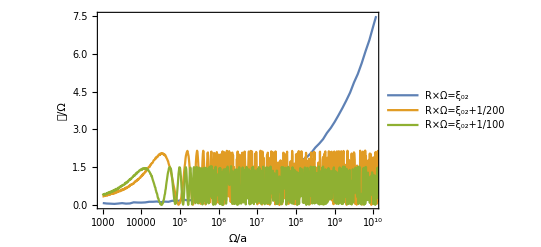

```mathematica
DRResAsyOa1=ListLinePlot[{{Re[#1],Re[#2]}&@@@s11,{Re[#1],Re[#2]}&@@@s22,{Re[#1],Re[#2]}&@@@s33},PlotRange->{{10^3,10^10},{0,7.5}},ScalingFunctions->{"Log","Linear"},PlotLegends->Placed[{"R×Ω=ξ_02","R×Ω=ξ_02+1/200", "R×Ω=ξ_02+1/100"}
,{0.2,0.7}],FrameLabel->{"Ω/a","𝒞/Ω"},ScalingFunctions->{"Linear","Linear"},Frame->True,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black},GridLines->Automatic]
```

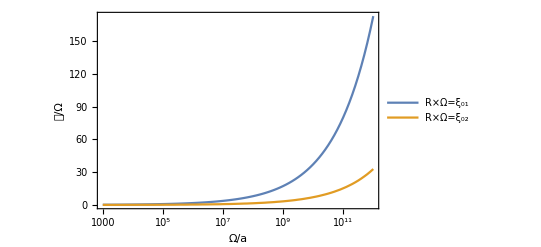

```mathematica
DRResAsyOa2=ListLinePlot[{{Re[#1],Re[#2]}&@@@s1,{Re[#1],Re[#2]}&@@@s11},PlotRange->{{10^3,10^12},Full},ScalingFunctions->{"Log","Linear"},PlotLegends->Placed[{"R×Ω=ξ_01","R×Ω=ξ_02"}
,{0.2,0.7}],FrameLabel->{"Ω/a","𝒞/Ω"},ScalingFunctions->{"Linear","Linear"},Frame->True,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black},GridLines->Automatic]
```

```mathematica
s4=ParallelTable[{RΩ,N[DRAs[RΩ,10^6,3]]},{RΩ,1/100,12,1/1000}]
```

General::munfl: 3.816630688674381383×10^-207517923 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.8453300523844299314×10^-8620263 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.0575193317279662662×10^-3804495 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.5448269478144992377×10^-2170659 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.7315057671430146194×10^-188528968 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.0855130039109750195×10^-8573303 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.5827927986129466916×10^-3792281 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.0870953928627715247×10^-2165239 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.3252813635948938973×10^-172704869 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.1972634137066003889×10^-8526788 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.086052779745462099×10^-3780127 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.5283652799359092177×10^-2159836 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.5759273574420225782×10^-1362109 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.5367273545030396422×10^-888983 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.0348107299786055154×10^-1359116 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.5026952250637314268×10^-887127 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.8379736796131593602×10^-1356130 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.0368736812819806666×10^-885274 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.4635621362086052751×10^-585434 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.4648672314701784714×10^-584202 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.7067992480922715608×10^-582973 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 2.2610064702980825027×10^-379873 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.0732696472790281826×10^-379023 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.4349881056337101674×10^-378174 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 2.3701089525991995681×10^-236486 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.7890351490905193051×10^-235888 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.9670902896963968352×10^-235291 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 7.3955547430408365884×10^-135572 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.9279981466295563481×10^-135152 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.6169088578989699675×10^-134734 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.7797510642833441596×10^-65730 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.1814232867886437946×10^-65447 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.2796803512825446525×10^-65164 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.4932106278221073032×10^-20634 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.9563841565040812173×10^-20466 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.9744392918952121823×10^-20298 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

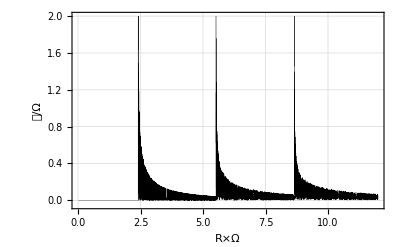

```mathematica
DRResAsyRO4=ListLinePlot[{{Re[#1],Re[#2]}&@@@s4},PlotRange->{{0,12},{-0.05,2}},InterpolationOrder->1,MaxPlotPoints->Infinity,PlotStyle->Directive[Black,Thickness[0.0005]],FrameLabel->{"R×Ω","𝒞/Ω"},ScalingFunctions->{"Linear","Linear"},Frame->True,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black},GridLines->Automatic]
```

```mathematica
s5=ParallelTable[{RΩ,N[DRAs[RΩ,10^12,3]]},{RΩ,1/100,12,1/1000}]
```

General::munfl: 7.62633073618411180672432101178613`20.*^-8620262502495 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.20858779790304337545849191320171507786621`20.*^-2170658129358 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.78498094443282733325541661110984084326931227`20.*^-207517923507448 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.2217481579310234551619148992278`20.*^-8573302730886 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.75764388690435146840784519856074073113512391273`20.*^-2165237359150 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.5401859747351025180230029263720859449098855649`20.*^-3804493874487 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.8666593160868456300934006854640425415139696`20.*^-188528968289468 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.461997712352274208275224522959891595899948875459`20.*^-8526787686294 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.2338732416777970611207009505166694709780100352`20.*^-2159834914074 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.373257029372331188928379517256623699699196`20.*^-3792280069632 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.83205421614738297860129216129610666577733320131`20.*^-172704869040287 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.5077560077538544802434937680810487547`20.*^-3780126444847 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.418589798901086723935054664235532`20.*^-1362108009253 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.9968347450646372414427109188092730884843487`20.*^-1359114301347 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.5506490352122087361732291523456821834504215095`20.*^-888981578343 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.601237739919644267904117450967957617521957`20.*^-1356128439594 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.541221535406852612542691505766657531013024`20.*^-887125313513 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.7026467198525412201162238828516796733292761236`20.*^-585432420047 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 5.122909486111895660333066479033`20.*^-885273110544 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.501112169455760558108437134408764181`20.*^-584200677698 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.04015155213253589970877924194186360770615`20.*^-582971312862 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.9469201869270183681720152699466158466845`20.*^-379871677078 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.233994718978749610614357781262002532876358`20.*^-379021325946 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.340762485429643948964909877651476374369795651`20.*^-378172495162 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.16133119542877597020825765674318`20.*^-236484636646 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.297541590104299200806693513407944649`20.*^-235886565910 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.4510666648703718883271260134884`20.*^-135570143976 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.41786169061487582269819046681360139008`20.*^-235289538984 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.124053136002676757070445486986253685378777402`20.*^-135150727914 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 5.82221588210031732321331904225524175724440149248`20.*^-134732077744 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.086094744112284356470842091534949293814439426`20.*^-65728795995 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 4.9867358930551701207804460574324394656`20.*^-65445255551 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.949716292595828466204783531105263991590707401`20.*^-65162324319 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 5.512684118665206351180617683587774596`20.*^-20632496358 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.079960222087267907883185110795712069306222038`20.*^-20464151687 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.6996655805542880549629511844146534042944`20.*^-20296374371 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

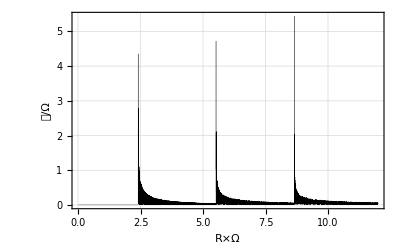

```mathematica
DRResAsyRO5=ListLinePlot[{{Re[#1],Re[#2]}&@@@s5},PlotRange->{{0,12},Full},InterpolationOrder->1,MaxPlotPoints->Infinity,PlotStyle->Directive[Black,Thickness[0.0005]],FrameLabel->{"R×Ω","𝒞/Ω"},ScalingFunctions->{"Linear","Linear"},Frame->True,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black},GridLines->Automatic]
```

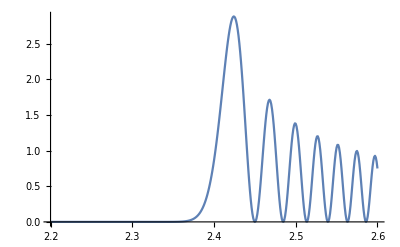

```mathematica
ListLinePlot[s,PlotRange->{{2.2,2.6},Full}]
```

```mathematica
s=ParallelTable[{RΩ,N[DR[RΩ,10^3,1]]},{RΩ,2.2,2.6,1/1000}]
```

{{2.2,1.23629×10^-23},{2.201,1.84896×10^-23},{2.202,2.76168×10^-23},{2.203,4.11964×10^-23},{2.204,6.1374×10^-23},{2.205,9.13165×10^-23},{2.206,1.35692×10^-22},{2.207,2.01371×10^-22},{2.208,2.98456×10^-22},{2.209,4.41775×10^-22},{2.21,6.53072×10^-22},{2.211,9.64184×10^-22},{2.212,1.42166×10^-21},{2.213,2.09349×10^-21},{2.214,3.07882×10^-21},{2.215,4.52204×10^-21},{2.216,6.63319×10^-21},{2.217,9.71734×10^-21},{2.218,1.4217×10^-20},{2.219,2.07734×10^-20},{2.22,3.0314×10^-20},{2.221,4.41788×10^-20},{2.222,6.43015×10^-20},{2.223,9.34681×10^-20},{2.224,1.35688×10^-19},{2.225,1.96723×10^-19},{2.226,2.84841×10^-19},{2.227,4.11893×10^-19},{2.228,5.94841×10^-19},{2.229,8.57928×10^-19},{2.23,1.23576×10^-18},{2.231,1.77767×10^-18},{2.232,2.55388×10^-18},{2.233,3.66423×10^-18},{2.234,5.25045×10^-18},{2.235,7.5135×10^-18},{2.236,1.07379×10^-17},{2.237,1.53259×10^-17},{2.238,2.18457×10^-17},{2.239,3.10981×10^-17},{2.24,4.42112×10^-17},{2.241,6.27711×10^-17},{2.242,8.90052×10^-17},{2.243,1.26038×10^-16},{2.244,1.78243×10^-16},{2.245,2.5174×10^-16},{2.246,3.55074×10^-16},{2.247,5.00164×10^-16},{2.248,7.03609×10^-16},{2.249,9.88498×10^-16},{2.25,1.3869×10^-15},{2.251,1.9433×10^-15},{2.252,2.7193×10^-15},{2.253,3.80013×10^-15},{2.254,5.30349×10^-15},{2.255,7.39176×10^-15},{2.256,1.02886×10^-14},{2.257,1.43016×10^-14},{2.258,1.98533×10^-14},{2.259,2.75234×10^-14},{2.26,3.81056×10^-14},{2.261,5.2686×10^-14},{2.262,7.27477×10^-14},{2.263,1.00314×10^-13},{2.264,1.3814×10^-13},{2.265,1.89973×10^-13},{2.266,2.60904×10^-13},{2.267,3.57835×10^-13},{2.268,4.90116×10^-13},{2.269,6.70391×10^-13},{2.27,9.15734×10^-13},{2.271,1.24917×10^-12},{2.272,1.70171×10^-12},{2.273,2.31504×10^-12},{2.274,3.14513×10^-12},{2.275,4.26706×10^-12},{2.276,5.7813×10^-12},{2.277,7.82219×10^-12},{2.278,1.05691×10^-11},{2.279,1.4261×10^-11},{2.28,1.92161×10^-11},{2.281,2.58574×10^-11},{2.282,3.47461×10^-11},{2.283,4.66259×10^-11},{2.284,6.24811×10^-11},{2.285,8.3612×10^-11},{2.286,1.11734×10^-10},{2.287,1.49108×10^-10},{2.288,1.98706×10^-10},{2.289,2.64432×10^-10},{2.29,3.51408×10^-10},{2.291,4.66339×10^-10},{2.292,6.17992×10^-10},{2.293,8.17813×10^-10},{2.294,1.08072×10^-9},{2.295,1.42614×10^-9},{2.296,1.87929×10^-9},{2.297,2.47294×10^-9},{2.298,3.24949×10^-9},{2.299,4.26383×10^-9},{2.3,5.58684×10^-9},{2.301,7.30991×10^-9},{2.302,9.55073×10^-9},{2.303,1.24606×10^-8},{2.304,1.62336×10^-8},{2.305,2.11186×10^-8},{2.306,2.7434×10^-8},{2.307,3.55864×10^-8},{2.308,4.60945×10^-8},{2.309,5.96185×10^-8},{2.31,7.69981×10^-8},{2.311,9.92988×10^-8},{2.312,1.27871×10^-7},{2.313,1.64422×10^-7},{2.314,2.1111×10^-7},{2.315,2.70654×10^-7},{2.316,3.46479×10^-7},{2.317,4.42888×10^-7},{2.318,5.65279×10^-7},{2.319,7.20416×10^-7},{2.32,9.16753×10^-7},{2.321,1.16484×10^-6},{2.322,1.47784×10^-6},{2.323,1.87211×10^-6},{2.324,2.36796×10^-6},{2.325,2.99059×10^-6},{2.326,3.77117×10^-6},{2.327,4.74819×10^-6},{2.328,5.96916×10^-6},{2.329,7.4925×10^-6},{2.33,9.39006×10^-6},{2.331,0.0000117499},{2.332,0.0000146799},{2.333,0.0000183118},{2.334,0.0000228064},{2.335,0.0000283593},{2.336,0.0000352085},{2.337,0.0000436424},{2.338,0.0000540103},{2.339,0.0000667341},{2.34,0.0000823228},{2.341,0.000101389},{2.342,0.000124668},{2.343,0.000153042},{2.344,0.000187566},{2.345,0.000229501},{2.346,0.000280347},{2.347,0.00034189},{2.348,0.000416247},{2.349,0.000505926},{2.35,0.000613891},{2.351,0.000743635},{2.352,0.000899265},{2.353,0.00108561},{2.354,0.00130831},{2.355,0.00157396},{2.356,0.00189027},{2.357,0.00226617},{2.358,0.00271204},{2.359,0.00323989},{2.36,0.00386359},{2.361,0.0045991},{2.362,0.00546476},{2.363,0.00648157},{2.364,0.00767353},{2.365,0.00906799},{2.366,0.010696},{2.367,0.0125928},{2.368,0.0147982},{2.369,0.0173568},{2.37,0.0203191},{2.371,0.0237412},{2.372,0.0276861},{2.373,0.0322235},{2.374,0.0374307},{2.375,0.0433932},{2.376,0.0502049},{2.377,0.0579687},{2.378,0.0667969},{2.379,0.0768116},{2.38,0.0881446},{2.381,0.100938},{2.382,0.115344},{2.383,0.131524},{2.384,0.149651},{2.385,0.169905},{2.386,0.192475},{2.387,0.217558},{2.388,0.245355},{2.389,0.276072},{2.39,0.309918},{2.391,0.3471},{2.392,0.387824},{2.393,0.432285},{2.394,0.480673},{2.395,0.533159},{2.396,0.589898},{2.397,0.651019},{2.398,0.716622},{2.399,0.78677},{2.4,0.861487},{2.401,0.940749},{2.402,1.02448},{2.403,1.11253},{2.404,1.2047},{2.405,1.30071},{2.406,1.40021},{2.407,1.50274},{2.408,1.6078},{2.409,1.71476},{2.41,1.8229},{2.411,1.93145},{2.412,2.03949},{2.413,2.14606},{2.414,2.2501},{2.415,2.35047},{2.416,2.44599},{2.417,2.53541},{2.418,2.61746},{2.419,2.69084},{2.42,2.75427},{2.421,2.80648},{2.422,2.84627},{2.423,2.8725},{2.424,2.88415},{2.425,2.88035},{2.426,2.86037},{2.427,2.82369},{2.428,2.77001},{2.429,2.69927},{2.43,2.61169},{2.431,2.50778},{2.432,2.38835},{2.433,2.25452},{2.434,2.10773},{2.435,1.94974},{2.436,1.78257},{2.437,1.60856},{2.438,1.43027},{2.439,1.25047},{2.44,1.0721},{2.441,0.898189},{2.442,0.73183},{2.443,0.576078},{2.444,0.433895},{2.445,0.308067},{2.446,0.201129},{2.447,0.115291},{2.448,0.0523562},{2.449,0.0136631},{2.45,0.0000194258},{2.451,0.0116556},{2.452,0.0481891},{2.453,0.108604},{2.454,0.191246},{2.455,0.293841},{2.456,0.413527},{2.457,0.54691},{2.458,0.690137},{2.459,0.838994},{2.46,0.989006},{2.461,1.13557},{2.462,1.27409},{2.463,1.40012},{2.464,1.50949},{2.465,1.59849},{2.466,1.66397},{2.467,1.70347},{2.468,1.71535},{2.469,1.69885},{2.47,1.65415},{2.471,1.58239},{2.472,1.48568},{2.473,1.36705},{2.474,1.23036},{2.475,1.08018},{2.476,0.921655},{2.477,0.760346},{2.478,0.601999},{2.479,0.45235},{2.48,0.3169},{2.481,0.20069},{2.482,0.108094},{2.483,0.0426231},{2.484,0.00675811},{2.485,0.00182504},{2.486,0.027908},{2.487,0.0838145},{2.488,0.167093},{2.489,0.274107},{2.49,0.400161},{2.491,0.53968},{2.492,0.686435},{2.493,0.833801},{2.494,0.975044},{2.495,1.10363},{2.496,1.21351},{2.497,1.29943},{2.498,1.35718},{2.499,1.38383},{2.5,1.37785},{2.501,1.33929},{2.502,1.26972},{2.503,1.17227},{2.504,1.05142},{2.505,0.912898},{2.506,0.763344},{2.507,0.61003},{2.508,0.460497},{2.509,0.322169},{2.51,0.201973},{2.511,0.105969},{2.512,0.039017},{2.513,0.00449852},{2.514,0.00411143},{2.515,0.0377496},{2.516,0.103478},{2.517,0.197606},{2.518,0.314861},{2.519,0.448655},{2.52,0.591426},{2.521,0.735049},{2.522,0.871284},{2.523,0.992244},{2.524,1.09085},{2.525,1.16125},{2.526,1.19918},{2.527,1.20223},{2.528,1.17004},{2.529,1.10431},{2.53,1.00875},{2.531,0.888889},{2.532,0.751769},{2.533,0.605524},{2.534,0.458909},{2.535,0.320764},{2.536,0.199473},{2.537,0.102429},{2.538,0.0355632},{2.539,0.00294742},{2.54,0.00651344},{2.541,0.0459017},{2.542,0.118456},{2.543,0.219364},{2.544,0.341946},{2.545,0.478068},{2.546,0.618657},{2.547,0.75429},{2.548,0.875819},{2.549,0.974982},{2.55,1.04497},{2.551,1.08091},{2.552,1.0802},{2.553,1.04275},{2.554,0.970952},{2.555,0.869622},{2.556,0.745629},{2.557,0.607468},{2.558,0.464671},{2.559,0.327151},{2.56,0.204502},{2.561,0.105309},{2.562,0.0365276},{2.563,0.00296286},{2.564,0.00690307},{2.565,0.0479266},{2.566,0.122906},{2.567,0.226212},{2.568,0.350102},{2.569,0.485276},{2.57,0.621551},{2.571,0.748615},{2.572,0.856804},{2.573,0.937831},{2.574,0.985432},{2.575,0.995858},{2.576,0.968188},{2.577,0.90442},{2.578,0.809348},{2.579,0.690212},{2.58,0.556154},{2.581,0.417523},{2.582,0.285069},{2.583,0.169101},{2.584,0.0786648},{2.585,0.0208134},{2.586,0.0000283671},{2.587,0.0178384},{2.588,0.0726728},{2.589,0.159963},{2.59,0.272493},{2.591,0.40096},{2.592,0.534729},{2.593,0.66269},{2.594,0.774173},{2.595,0.859835},{2.596,0.912448},{2.597,0.927517},{2.598,0.903677},{2.599,0.842829},{2.6,0.750008}}

```mathematica
s=Table[{RΩ,N[RR[RΩ,10^3,100]]},{RΩ,22/10,6,1/100}]
```

General::munfl: Exp[-1140.38] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2490.53] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3882.55] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{11/5,1.23629×10^-23},{221/100,6.53072×10^-22},{111/50,3.0314×10^-20},{223/100,1.23576×10^-18},{56/25,4.42112×10^-17},{9/4,1.3869×10^-15},{113/50,3.81056×10^-14},{227/100,9.15734×10^-13},{57/25,1.92161×10^-11},{229/100,3.51408×10^-10},{23/10,5.58684×10^-9},{231/100,7.69981×10^-8},{58/25,9.16753×10^-7},{233/100,9.39006×10^-6},{117/50,0.0000823228},{47/20,0.000613891},{59/25,0.00386359},{237/100,0.0203191},{119/50,0.0881446},{239/100,0.309918},{12/5,0.861487},{241/100,1.8229},{121/50,2.75427},{243/100,2.61169},{61/25,1.0721},{49/20,0.0000194258},{123/50,0.989006},{247/100,1.65415},{62/25,0.3169},{249/100,0.400161},{5/2,1.37785},{251/100,0.201973},{63/25,0.591426},{253/100,1.00875},{127/50,0.00651344},{51/20,1.04497},{64/25,0.204502},{257/100,0.621551},{129/50,0.556154},{259/100,0.272493},{13/5,0.750008},{261/100,0.103944},{131/50,0.800821},{263/100,0.0462421},{66/25,0.783319},{53/20,0.038257},{133/50,0.734816},{267/100,0.0632592},{67/25,0.653276},{269/100,0.134609},{27/10,0.5189},{271/100,0.269278},{68/25,0.325364},{273/100,0.452071},{137/50,0.11691},{11/4,0.604539},{69/25,0.00155495},{277/100,0.60368},{139/50,0.0888666},{279/100,0.389563},{14/5,0.352107},{281/100,0.0969128},{141/50,0.556668},{283/100,0.010999},{71/25,0.451537},{57/20,0.249191},{143/50,0.126474},{287/100,0.508175},{72/25,0.012065},{289/100,0.393879},{29/10,0.283486},{291/100,0.0617347},{73/25,0.48838},{293/100,0.0671247},{147/50,0.247186},{59/20,0.391934},{74/25,0.000198161},{297/100,0.393109},{149/50,0.227008},{299/100,0.0574073},{3,0.437818},{301/100,0.0911949},{151/50,0.162846},{303/100,0.400945},{76/25,0.0180339},{61/20,0.260441},{153/50,0.324325},{307/100,0.000128287},{77/25,0.326818},{309/100,0.240839},{31/10,0.0169293},{311/100,0.360362},{78/25,0.167915},{313/100,0.0497556},{157/50,0.3686},{63/20,0.111352},{79/25,0.0862613},{317/100,0.360561},{159/50,0.0706606},{319/100,0.119911},{16/5,0.34359},{321/100,0.042889},{161/50,0.148091},{323/100,0.322669},{81/25,0.0246893},{13/4,0.170392},{163/50,0.30076},{327/100,0.0131877},{82/25,0.187446},{329/100,0.279387},{33/10,0.00621854},{331/100,0.200258},{83/25,0.259156},{333/100,0.00228045},{167/50,0.209864},{67/20,0.240134},{84/25,0.000405708},{337/100,0.217181},{169/50,0.222099},{339/100,0.0000276224},{17/5,0.22295},{341/100,0.204686},{171/50,0.000875325},{343/100,0.227723},{86/25,0.187483},{69/20,0.00290024},{173/50,0.231862},{347/100,0.170084},{87/25,0.00622826},{349/100,0.235534},{7/2,0.152133},{351/100,0.0111281},{88/25,0.238701},{353/100,0.133358},{177/50,0.0179849},{71/20,0.241106},{89/25,0.113624},{357/100,0.0272667},{179/50,0.242248},{359/100,0.0929937},{18/5,0.0394722},{361/100,0.241371},{181/50,0.071813},{363/100,0.0550434},{91/25,0.237472},{73/20,0.0508045},{183/50,0.0742324},{367/100,0.229352},{92/25,0.0311643},{369/100,0.0969134},{37/10,0.215747},{371/100,0.0146226},{93/25,0.122346},{373/100,0.195562},{187/50,0.00341738},{15/4,0.148919},{94/25,0.168246},{377/100,0.000108858},{189/50,0.173954},{379/100,0.134282},{19/5,0.00715209},{381/100,0.193679},{191/50,0.0957417},{383/100,0.0261747},{96/25,0.203556},{77/20,0.0567108},{193/50,0.0569884},{387/100,0.199121},{97/25,0.0233214},{389/100,0.0965287},{39/10,0.177434},{391/100,0.00300608},{98/25,0.138149},{393/100,0.138968},{197/50,0.00267855},{79/20,0.171922},{99/25,0.0893787},{397/100,0.0258573},{199/50,0.186624},{399/100,0.0400972},{4,0.0694213},{401/100,0.173701},{201/50,0.00648438},{403/100,0.12157},{101/25,0.132439},{81/20,0.00270815},{203/50,0.163169},{407/100,0.0740615},{102/25,0.0341221},{409/100,0.174161},{41/10,0.0212303},{411/100,0.09045},{103/25,0.144301},{413/100,0.0000168216},{207/50,0.14524},{83/20,0.0833695},{104/25,0.0251433},{417/100,0.166262},{209/50,0.0225738},{419/100,0.0857755},{21/5,0.135556},{421/100,0.000328693},{211/50,0.144202},{423/100,0.0678477},{106/25,0.035341},{17/4,0.156349},{213/50,0.00953346},{427/100,0.104733},{107/25,0.107112},{429/100,0.00825097},{43/10,0.151689},{431/100,0.0328441},{108/25,0.0686693},{433/100,0.130126},{217/50,0.000201089},{87/20,0.135906},{109/25,0.0550034},{437/100,0.044028},{219/50,0.139132},{439/100,0.00140873},{22/5,0.120166},{441/100,0.069219},{221/50,0.0306075},{443/100,0.14},{111/25,0.00412708},{89/20,0.110104},{223/50,0.0741063},{447/100,0.0258304},{112/25,0.137153},{449/100,0.00451692},{9/2,0.107421},{451/100,0.0701473},{113/25,0.0280799},{453/100,0.131964},{227/50,0.00224526},{91/20,0.111507},{114/25,0.058021},{457/100,0.0375831},{229/50,0.122779},{459/100,0.0000271654},{23/5,0.119661},{461/100,0.0390228},{231/50,0.0554599},{463/100,0.105855},{116/25,0.00339331},{93/20,0.126162},{233/50,0.0171467},{467/100,0.0810069},{117/25,0.0778534},{469/100,0.0193212},{47/10,0.121843},{471/100,0.00150854},{118/25,0.107594},{473/100,0.0408225},{237/50,0.0515044},{19/4,0.0973502},{119/25,0.00564063},{477/100,0.120146},{239/50,0.00800264},{479/100,0.0919204},{24/5,0.0528047},{481/100,0.0385536},{241/50,0.101151},{483/100,0.00275921},{121/25,0.115637},{97/20,0.00946371},{243/50,0.0877898},{487/100,0.0503269},{122/25,0.0398481},{489/100,0.094455},{49/10,0.00504501},{491/100,0.112376},{123/25,0.00427352},{493/100,0.094616},{247/50,0.034973},{99/20,0.0543342},{124/25,0.0763776},{497/100,0.0160263},{249/50,0.104295},{499/100,0.000034384},{5,0.104822},{501/100,0.012444},{251/50,0.0798132},{503/100,0.0444415},{126/25,0.0432426},{101/20,0.0791563},{253/50,0.012507},{507/100,0.100819},{127/25,0.0000477559},{509/100,0.101417},{51/10,0.00899612},{511/100,0.0825487},{128/25,0.033672},{513/100,0.0529685},{257/50,0.0634455},{103/20,0.0239475},{129/25,0.0875411},{517/100,0.00482519},{259/50,0.0987346},{519/100,0.000315021},{26/5,0.0949402},{521/100,0.0100018},{261/50,0.078753},{523/100,0.0295652},{131/25,0.0556896},{21/4,0.052838},{263/50,0.0320507},{527/100,0.0738358},{132/25,0.0131433},{529/100,0.088188},{53/10,0.00224517},{531/100,0.0937686},{133/25,0.000354996},{533/100,0.0906151},{267/50,0.0065419},{107/20,0.0803852},{134/25,0.0186229},{537/100,0.0656387},{269/50,0.0339301},{539/100,0.0492147},{27/5,0.0500785},{541/100,0.0340195},{271/50,0.0659788},{543/100,0.0238451},{136/25,0.0840011},{109/20,0.0265322},{273/50,0.115001},{547/100,0.0610561},{137/25,0.186905},{549/100,0.166346},{11/2,0.349452},{551/100,0.396209},{138/25,0.649988},{553/100,0.768154},{277/50,1.05124},{111/20,1.15973},{139/25,1.33437},{557/100,1.26914},{279/50,1.17858},{559/100,0.860464},{28/5,0.562033},{561/100,0.217636},{281/50,0.0696846},{563/100,0.0708942},{141/25,0.293771},{113/20,0.565004},{283/50,0.772298},{567/100,0.768113},{142/25,0.549203},{569/100,0.253877},{57/10,0.0485259},{571/100,0.103803},{143/25,0.329227},{573/100,0.597235},{287/50,0.628379},{23/4,0.454584},{144/25,0.150074},{577/100,0.0516037},{289/50,0.168885},{579/100,0.459527},{29/5,0.558335},{581/100,0.435813},{291/50,0.140992},{583/100,0.0509287},{146/25,0.190235},{117/20,0.460211},{293/50,0.49188},{587/100,0.296392},{147/25,0.0571453},{589/100,0.0954636},{59/10,0.32852},{591/100,0.478509},{148/25,0.339671},{593/100,0.0907027},{297/50,0.0667057},{119/20,0.272417},{149/25,0.454579},{597/100,0.312691},{299/50,0.101784},{599/100,0.0488842},{6,0.30682}}

Inertial decoherence

```mathematica
InDR[RΩ_,n0_]:=1/(2π RΩ)Sum[HeavisideTheta[RΩ-BesselJZero[0,n]]/(√(RΩ^2-BesselJZero[0,n]^2))BesselJ[1,BesselJZero[0,n]]^-2,{n,1,n0}]
```

```mathematica
Indata=ParallelTable[{RΩ,N[InDR[RΩ,4]]},{RΩ,1/10,10,1/100}]
```

{{1/10,0.-9.94231 ⅈ},{11/100,0.-9.039 ⅈ},{3/25,0.-8.28628 ⅈ},{13/100,0.-7.64941 ⅈ},{7/50,0.-7.10357 ⅈ},{3/20,0.-6.63054 ⅈ},{4/25,0.-6.21667 ⅈ},{17/100,0.-5.85153 ⅈ},{9/50,0.-5.52699 ⅈ},{19/100,0.-5.23664 ⅈ},{1/5,0.-4.97536 ⅈ},{21/100,0.-4.73899 ⅈ},{11/50,0.-4.52413 ⅈ},{23/100,0.-4.32798 ⅈ},{6/25,0.-4.1482 ⅈ},{1/4,0.-3.98282 ⅈ},{13/50,0.-3.83019 ⅈ},{27/100,0.-3.68889 ⅈ},{7/25,0.-3.5577 ⅈ},{29/100,0.-3.43558 ⅈ},{3/10,0.-3.32162 ⅈ},{31/100,0.-3.21503 ⅈ},{8/25,0.-3.11512 ⅈ},{33/100,0.-3.02128 ⅈ},{17/50,0.-2.93298 ⅈ},{7/20,0.-2.84975 ⅈ},{9/25,0.-2.77115 ⅈ},{37/100,0.-2.69682 ⅈ},{19/50,0.-2.62642 ⅈ},{39/100,0.-2.55964 ⅈ},{2/5,0.-2.49622 ⅈ},{41/100,0.-2.43591 ⅈ},{21/50,0.-2.37848 ⅈ},{43/100,0.-2.32374 ⅈ},{11/25,0.-2.2715 ⅈ},{9/20,0.-2.2216 ⅈ},{23/50,0.-2.17388 ⅈ},{47/100,0.-2.1282 ⅈ},{12/25,0.-2.08444 ⅈ},{49/100,0.-2.04248 ⅈ},{1/2,0.-2.00222 ⅈ},{51/100,0.-1.96354 ⅈ},{13/25,0.-1.92636 ⅈ},{53/100,0.-1.8906 ⅈ},{27/50,0.-1.85618 ⅈ},{11/20,0.-1.82302 ⅈ},{14/25,0.-1.79106 ⅈ},{57/100,0.-1.76023 ⅈ},{29/50,0.-1.73047 ⅈ},{59/100,0.-1.70173 ⅈ},{3/5,0.-1.67397 ⅈ},{61/100,0.-1.64713 ⅈ},{31/50,0.-1.62116 ⅈ},{63/100,0.-1.59603 ⅈ},{16/25,0.-1.57169 ⅈ},{13/20,0.-1.54812 ⅈ},{33/50,0.-1.52527 ⅈ},{67/100,0.-1.50311 ⅈ},{17/25,0.-1.48162 ⅈ},{69/100,0.-1.46076 ⅈ},{7/10,0.-1.44051 ⅈ},{71/100,0.-1.42083 ⅈ},{18/25,0.-1.40172 ⅈ},{73/100,0.-1.38314 ⅈ},{37/50,0.-1.36507 ⅈ},{3/4,0.-1.3475 ⅈ},{19/25,0.-1.33039 ⅈ},{77/100,0.-1.31375 ⅈ},{39/50,0.-1.29754 ⅈ},{79/100,0.-1.28175 ⅈ},{4/5,0.-1.26636 ⅈ},{81/100,0.-1.25137 ⅈ},{41/50,0.-1.23675 ⅈ},{83/100,0.-1.22249 ⅈ},{21/25,0.-1.20859 ⅈ},{17/20,0.-1.19502 ⅈ},{43/50,0.-1.18178 ⅈ},{87/100,0.-1.16885 ⅈ},{22/25,0.-1.15622 ⅈ},{89/100,0.-1.14389 ⅈ},{9/10,0.-1.13185 ⅈ},{91/100,0.-1.12008 ⅈ},{23/25,0.-1.10857 ⅈ},{93/100,0.-1.09733 ⅈ},{47/50,0.-1.08633 ⅈ},{19/20,0.-1.07558 ⅈ},{24/25,0.-1.06506 ⅈ},{97/100,0.-1.05476 ⅈ},{49/50,0.-1.04469 ⅈ},{99/100,0.-1.03483 ⅈ},{1,0.-1.02518 ⅈ},{101/100,0.-1.01573 ⅈ},{51/50,0.-1.00648 ⅈ},{103/100,0.-0.997413 ⅈ},{26/25,0.-0.988535 ⅈ},{21/20,0.-0.979837 ⅈ},{53/50,0.-0.971314 ⅈ},{107/100,0.-0.96296 ⅈ},{27/25,0.-0.954773 ⅈ},{109/100,0.-0.946747 ⅈ},{11/10,0.-0.938877 ⅈ},{111/100,0.-0.931161 ⅈ},{28/25,0.-0.923593 ⅈ},{113/100,0.-0.916171 ⅈ},{57/50,0.-0.90889 ⅈ},{23/20,0.-0.901748 ⅈ},{29/25,0.-0.89474 ⅈ},{117/100,0.-0.887864 ⅈ},{59/50,0.-0.881115 ⅈ},{119/100,0.-0.874492 ⅈ},{6/5,0.-0.867992 ⅈ},{121/100,0.-0.861611 ⅈ},{61/50,0.-0.855346 ⅈ},{123/100,0.-0.849196 ⅈ},{31/25,0.-0.843158 ⅈ},{5/4,0.-0.837228 ⅈ},{63/50,0.-0.831405 ⅈ},{127/100,0.-0.825687 ⅈ},{32/25,0.-0.820071 ⅈ},{129/100,0.-0.814556 ⅈ},{13/10,0.-0.809138 ⅈ},{131/100,0.-0.803816 ⅈ},{33/25,0.-0.798589 ⅈ},{133/100,0.-0.793454 ⅈ},{67/50,0.-0.78841 ⅈ},{27/20,0.-0.783454 ⅈ},{34/25,0.-0.778586 ⅈ},{137/100,0.-0.773803 ⅈ},{69/50,0.-0.769105 ⅈ},{139/100,0.-0.764488 ⅈ},{7/5,0.-0.759953 ⅈ},{141/100,0.-0.755498 ⅈ},{71/50,0.-0.751121 ⅈ},{143/100,0.-0.746821 ⅈ},{36/25,0.-0.742597 ⅈ},{29/20,0.-0.738448 ⅈ},{73/50,0.-0.734372 ⅈ},{147/100,0.-0.730369 ⅈ},{37/25,0.-0.726437 ⅈ},{149/100,0.-0.722576 ⅈ},{3/2,0.-0.718783 ⅈ},{151/100,0.-0.71506 ⅈ},{38/25,0.-0.711404 ⅈ},{153/100,0.-0.707815 ⅈ},{77/50,0.-0.704291 ⅈ},{31/20,0.-0.700833 ⅈ},{39/25,0.-0.69744 ⅈ},{157/100,0.-0.69411 ⅈ},{79/50,0.-0.690844 ⅈ},{159/100,0.-0.68764 ⅈ},{8/5,0.-0.684498 ⅈ},{161/100,0.-0.681418 ⅈ},{81/50,0.-0.678399 ⅈ},{163/100,0.-0.675441 ⅈ},{41/25,0.-0.672543 ⅈ},{33/20,0.-0.669705 ⅈ},{83/50,0.-0.666926 ⅈ},{167/100,0.-0.664207 ⅈ},{42/25,0.-0.661548 ⅈ},{169/100,0.-0.658947 ⅈ},{17/10,0.-0.656405 ⅈ},{171/100,0.-0.653922 ⅈ},{43/25,0.-0.651498 ⅈ},{173/100,0.-0.649133 ⅈ},{87/50,0.-0.646826 ⅈ},{7/4,0.-0.644579 ⅈ},{44/25,0.-0.642391 ⅈ},{177/100,0.-0.640263 ⅈ},{89/50,0.-0.638195 ⅈ},{179/100,0.-0.636187 ⅈ},{9/5,0.-0.63424 ⅈ},{181/100,0.-0.632354 ⅈ},{91/50,0.-0.63053 ⅈ},{183/100,0.-0.628769 ⅈ},{46/25,0.-0.627071 ⅈ},{37/20,0.-0.625438 ⅈ},{93/50,0.-0.623871 ⅈ},{187/100,0.-0.62237 ⅈ},{47/25,0.-0.620936 ⅈ},{189/100,0.-0.619572 ⅈ},{19/10,0.-0.618279 ⅈ},{191/100,0.-0.617058 ⅈ},{48/25,0.-0.615911 ⅈ},{193/100,0.-0.61484 ⅈ},{97/50,0.-0.613848 ⅈ},{39/20,0.-0.612937 ⅈ},{49/25,0.-0.612109 ⅈ},{197/100,0.-0.611367 ⅈ},{99/50,0.-0.610715 ⅈ},{199/100,0.-0.610155 ⅈ},{2,0.-0.609693 ⅈ},{201/100,0.-0.609332 ⅈ},{101/50,0.-0.609076 ⅈ},{203/100,0.-0.608931 ⅈ},{51/25,0.-0.608903 ⅈ},{41/20,0.-0.608997 ⅈ},{103/50,0.-0.609221 ⅈ},{207/100,0.-0.609583 ⅈ},{52/25,0.-0.61009 ⅈ},{209/100,0.-0.610753 ⅈ},{21/10,0.-0.611582 ⅈ},{211/100,0.-0.61259 ⅈ},{53/25,0.-0.613789 ⅈ},{213/100,0.-0.615195 ⅈ},{107/50,0.-0.616826 ⅈ},{43/20,0.-0.618702 ⅈ},{54/25,0.-0.620844 ⅈ},{217/100,0.-0.62328 ⅈ},{109/50,0.-0.626039 ⅈ},{219/100,0.-0.629157 ⅈ},{11/5,0.-0.632674 ⅈ},{221/100,0.-0.63664 ⅈ},{111/50,0.-0.641111 ⅈ},{223/100,0.-0.646159 ⅈ},{56/25,0.-0.651865 ⅈ},{9/4,0.-0.658333 ⅈ},{113/50,0.-0.665691 ⅈ},{227/100,0.-0.674098 ⅈ},{57/25,0.-0.68376 ⅈ},{229/100,0.-0.694941 ⅈ},{23/10,0.-0.707994 ⅈ},{231/100,0.-0.723401 ⅈ},{58/25,0.-0.741836 ⅈ},{233/100,0.-0.76428 ⅈ},{117/50,0.-0.792228 ⅈ},{47/20,0.-0.828097 ⅈ},{59/25,0.-0.876101 ⅈ},{237/100,0.-0.944458 ⅈ},{119/50,0.-1.05211 ⅈ},{239/100,0.-1.25769 ⅈ},{12/5,0.-1.94566 ⅈ},{241/100,1.55239-0.328562 ⅈ},{121/50,0.901833-0.327373 ⅈ},{243/100,0.696566-0.326195 ⅈ},{61/25,0.586268-0.325028 ⅈ},{49/20,0.514682-0.323871 ⅈ},{123/50,0.463341-0.322725 ⅈ},{247/100,0.424154-0.321589 ⅈ},{62/25,0.392941-0.320464 ⅈ},{249/100,0.367296-0.319348 ⅈ},{5/2,0.345722-0.318243 ⅈ},{251/100,0.327232-0.317147 ⅈ},{63/25,0.311146-0.316062 ⅈ},{253/100,0.296978-0.314986 ⅈ},{127/50,0.284369-0.313919 ⅈ},{51/20,0.273048-0.312862 ⅈ},{64/25,0.262807-0.311815 ⅈ},{257/100,0.253481-0.310776 ⅈ},{129/50,0.244939-0.309747 ⅈ},{259/100,0.237076-0.308727 ⅈ},{13/5,0.229805-0.307716 ⅈ},{261/100,0.223053-0.306713 ⅈ},{131/50,0.216761-0.30572 ⅈ},{263/100,0.210878-0.304735 ⅈ},{66/25,0.20536-0.303759 ⅈ},{53/20,0.200171-0.302791 ⅈ},{133/50,0.195279-0.301832 ⅈ},{267/100,0.190656-0.300881 ⅈ},{67/25,0.186278-0.299938 ⅈ},{269/100,0.182124-0.299004 ⅈ},{27/10,0.178174-0.298077 ⅈ},{271/100,0.174413-0.297159 ⅈ},{68/25,0.170826-0.296248 ⅈ},{273/100,0.1674-0.295345 ⅈ},{137/50,0.164122-0.29445 ⅈ},{11/4,0.160983-0.293563 ⅈ},{69/25,0.157972-0.292683 ⅈ},{277/100,0.155082-0.291811 ⅈ},{139/50,0.152304-0.290946 ⅈ},{279/100,0.149631-0.290089 ⅈ},{14/5,0.147056-0.289239 ⅈ},{281/100,0.144574-0.288396 ⅈ},{141/50,0.14218-0.287561 ⅈ},{283/100,0.139868-0.286732 ⅈ},{71/25,0.137633-0.285911 ⅈ},{57/20,0.135472-0.285096 ⅈ},{143/50,0.13338-0.284289 ⅈ},{287/100,0.131354-0.283488 ⅈ},{72/25,0.129391-0.282694 ⅈ},{289/100,0.127487-0.281907 ⅈ},{29/10,0.125639-0.281127 ⅈ},{291/100,0.123846-0.280353 ⅈ},{73/25,0.122103-0.279585 ⅈ},{293/100,0.120409-0.278825 ⅈ},{147/50,0.118762-0.27807 ⅈ},{59/20,0.117159-0.277322 ⅈ},{74/25,0.115599-0.276581 ⅈ},{297/100,0.11408-0.275845 ⅈ},{149/50,0.1126-0.275116 ⅈ},{299/100,0.111157-0.274393 ⅈ},{3,0.10975-0.273676 ⅈ},{301/100,0.108378-0.272965 ⅈ},{151/50,0.107038-0.272261 ⅈ},{303/100,0.105731-0.271562 ⅈ},{76/25,0.104454-0.270869 ⅈ},{61/20,0.103207-0.270182 ⅈ},{153/50,0.101988-0.269501 ⅈ},{307/100,0.100797-0.268825 ⅈ},{77/25,0.0996319-0.268155 ⅈ},{309/100,0.0984924-0.267491 ⅈ},{31/10,0.0973774-0.266833 ⅈ},{311/100,0.0962862-0.26618 ⅈ},{78/25,0.0952179-0.265533 ⅈ},{313/100,0.0941718-0.264892 ⅈ},{157/50,0.0931472-0.264255 ⅈ},{63/20,0.0921433-0.263625 ⅈ},{79/25,0.0911595-0.262999 ⅈ},{317/100,0.0901952-0.262379 ⅈ},{159/50,0.0892497-0.261765 ⅈ},{319/100,0.0883225-0.261156 ⅈ},{16/5,0.0874131-0.260551 ⅈ},{321/100,0.0865208-0.259953 ⅈ},{161/50,0.0856452-0.259359 ⅈ},{323/100,0.0847858-0.25877 ⅈ},{81/25,0.0839421-0.258187 ⅈ},{13/4,0.0831137-0.257609 ⅈ},{163/50,0.0823001-0.257035 ⅈ},{327/100,0.081501-0.256467 ⅈ},{82/25,0.0807159-0.255904 ⅈ},{329/100,0.0799444-0.255345 ⅈ},{33/10,0.0791862-0.254792 ⅈ},{331/100,0.078441-0.254244 ⅈ},{83/25,0.0777083-0.2537 ⅈ},{333/100,0.0769879-0.253161 ⅈ},{167/50,0.0762794-0.252627 ⅈ},{67/20,0.0755826-0.252098 ⅈ},{84/25,0.0748971-0.251573 ⅈ},{337/100,0.0742226-0.251054 ⅈ},{169/50,0.073559-0.250539 ⅈ},{339/100,0.0729058-0.250028 ⅈ},{17/5,0.0722629-0.249522 ⅈ},{341/100,0.07163-0.249021 ⅈ},{171/50,0.0710069-0.248525 ⅈ},{343/100,0.0703934-0.248033 ⅈ},{86/25,0.0697891-0.247545 ⅈ},{69/20,0.069194-0.247063 ⅈ},{173/50,0.0686077-0.246584 ⅈ},{347/100,0.0680301-0.24611 ⅈ},{87/25,0.067461-0.245641 ⅈ},{349/100,0.0669003-0.245176 ⅈ},{7/2,0.0663476-0.244716 ⅈ},{351/100,0.0658029-0.24426 ⅈ},{88/25,0.065266-0.243808 ⅈ},{353/100,0.0647366-0.243361 ⅈ},{177/50,0.0642147-0.242918 ⅈ},{71/20,0.0637001-0.242479 ⅈ},{89/25,0.0631926-0.242045 ⅈ},{357/100,0.062692-0.241615 ⅈ},{179/50,0.0621983-0.24119 ⅈ},{359/100,0.0617113-0.240768 ⅈ},{18/5,0.0612308-0.240351 ⅈ},{361/100,0.0607568-0.239938 ⅈ},{181/50,0.0602891-0.23953 ⅈ},{363/100,0.0598275-0.239126 ⅈ},{91/25,0.0593719-0.238725 ⅈ},{73/20,0.0589223-0.23833 ⅈ},{183/50,0.0584785-0.237938 ⅈ},{367/100,0.0580404-0.23755 ⅈ},{92/25,0.0576079-0.237167 ⅈ},{369/100,0.0571808-0.236788 ⅈ},{37/10,0.0567592-0.236413 ⅈ},{371/100,0.0563428-0.236042 ⅈ},{93/25,0.0559316-0.235675 ⅈ},{373/100,0.0555255-0.235313 ⅈ},{187/50,0.0551243-0.234955 ⅈ},{15/4,0.0547281-0.2346 ⅈ},{94/25,0.0543366-0.23425 ⅈ},{377/100,0.0539499-0.233904 ⅈ},{189/50,0.0535678-0.233562 ⅈ},{379/100,0.0531903-0.233225 ⅈ},{19/5,0.0528173-0.232891 ⅈ},{381/100,0.0524486-0.232561 ⅈ},{191/50,0.0520843-0.232236 ⅈ},{383/100,0.0517242-0.231915 ⅈ},{96/25,0.0513683-0.231598 ⅈ},{77/20,0.0510164-0.231285 ⅈ},{193/50,0.0506686-0.230976 ⅈ},{387/100,0.0503248-0.230671 ⅈ},{97/25,0.0499849-0.23037 ⅈ},{389/100,0.0496488-0.230073 ⅈ},{39/10,0.0493164-0.229781 ⅈ},{391/100,0.0489878-0.229493 ⅈ},{98/25,0.0486628-0.229208 ⅈ},{393/100,0.0483414-0.228928 ⅈ},{197/50,0.0480235-0.228653 ⅈ},{79/20,0.0477091-0.228381 ⅈ},{99/25,0.0473981-0.228113 ⅈ},{397/100,0.0470904-0.22785 ⅈ},{199/50,0.0467861-0.227591 ⅈ},{399/100,0.046485-0.227336 ⅈ},{4,0.0461871-0.227085 ⅈ},{401/100,0.0458924-0.226839 ⅈ},{201/50,0.0456008-0.226596 ⅈ},{403/100,0.0453122-0.226358 ⅈ},{101/25,0.0450266-0.226125 ⅈ},{81/20,0.0447441-0.225895 ⅈ},{203/50,0.0444644-0.22567 ⅈ},{407/100,0.0441876-0.225449 ⅈ},{102/25,0.0439136-0.225233 ⅈ},{409/100,0.0436424-0.225021 ⅈ},{41/10,0.043374-0.224813 ⅈ},{411/100,0.0431083-0.22461 ⅈ},{103/25,0.0428453-0.224411 ⅈ},{413/100,0.0425848-0.224216 ⅈ},{207/50,0.042327-0.224027 ⅈ},{83/20,0.0420717-0.223841 ⅈ},{104/25,0.041819-0.22366 ⅈ},{417/100,0.0415687-0.223484 ⅈ},{209/50,0.0413209-0.223313 ⅈ},{419/100,0.0410755-0.223146 ⅈ},{21/5,0.0408324-0.222983 ⅈ},{421/100,0.0405917-0.222826 ⅈ},{211/50,0.0403534-0.222673 ⅈ},{423/100,0.0401173-0.222525 ⅈ},{106/25,0.0398834-0.222382 ⅈ},{17/4,0.0396518-0.222243 ⅈ},{213/50,0.0394223-0.22211 ⅈ},{427/100,0.039195-0.221981 ⅈ},{107/25,0.0389699-0.221858 ⅈ},{429/100,0.0387468-0.22174 ⅈ},{43/10,0.0385258-0.221626 ⅈ},{431/100,0.0383069-0.221518 ⅈ},{108/25,0.0380899-0.221415 ⅈ},{433/100,0.037875-0.221318 ⅈ},{217/50,0.037662-0.221225 ⅈ},{87/20,0.037451-0.221139 ⅈ},{109/25,0.0372418-0.221057 ⅈ},{437/100,0.0370346-0.220981 ⅈ},{219/50,0.0368292-0.220911 ⅈ},{439/100,0.0366257-0.220846 ⅈ},{22/5,0.0364239-0.220788 ⅈ},{441/100,0.036224-0.220734 ⅈ},{221/50,0.0360258-0.220687 ⅈ},{443/100,0.0358294-0.220646 ⅈ},{111/25,0.0356347-0.220611 ⅈ},{89/20,0.0354418-0.220582 ⅈ},{223/50,0.0352504-0.22056 ⅈ},{447/100,0.0350608-0.220543 ⅈ},{112/25,0.0348728-0.220534 ⅈ},{449/100,0.0346864-0.22053 ⅈ},{9/2,0.0345016-0.220534 ⅈ},{451/100,0.0343184-0.220544 ⅈ},{113/25,0.0341368-0.220561 ⅈ},{453/100,0.0339567-0.220585 ⅈ},{227/50,0.0337781-0.220617 ⅈ},{91/20,0.033601-0.220655 ⅈ},{114/25,0.0334255-0.220701 ⅈ},{457/100,0.0332513-0.220755 ⅈ},{229/50,0.0330787-0.220816 ⅈ},{459/100,0.0329075-0.220885 ⅈ},{23/5,0.0327377-0.220963 ⅈ},{461/100,0.0325693-0.221048 ⅈ},{231/50,0.0324022-0.221142 ⅈ},{463/100,0.0322366-0.221244 ⅈ},{116/25,0.0320723-0.221355 ⅈ},{93/20,0.0319093-0.221476 ⅈ},{233/50,0.0317477-0.221605 ⅈ},{467/100,0.0315873-0.221743 ⅈ},{117/25,0.0314283-0.221892 ⅈ},{469/100,0.0312705-0.22205 ⅈ},{47/10,0.031114-0.222218 ⅈ},{471/100,0.0309588-0.222397 ⅈ},{118/25,0.0308047-0.222586 ⅈ},{473/100,0.0306519-0.222786 ⅈ},{237/50,0.0305003-0.222997 ⅈ},{19/4,0.0303499-0.22322 ⅈ},{119/25,0.0302007-0.223454 ⅈ},{477/100,0.0300527-0.223701 ⅈ},{239/50,0.0299058-0.22396 ⅈ},{479/100,0.02976-0.224233 ⅈ},{24/5,0.0296154-0.224518 ⅈ},{481/100,0.0294718-0.224817 ⅈ},{241/50,0.0293294-0.22513 ⅈ},{483/100,0.0291881-0.225458 ⅈ},{121/25,0.0290479-0.225801 ⅈ},{97/20,0.0289087-0.22616 ⅈ},{243/50,0.0287706-0.226535 ⅈ},{487/100,0.0286335-0.226926 ⅈ},{122/25,0.0284975-0.227335 ⅈ},{489/100,0.0283625-0.227761 ⅈ},{49/10,0.0282285-0.228206 ⅈ},{491/100,0.0280955-0.228671 ⅈ},{123/25,0.0279635-0.229155 ⅈ},{493/100,0.0278324-0.22966 ⅈ},{247/50,0.0277024-0.230187 ⅈ},{99/20,0.0275733-0.230737 ⅈ},{124/25,0.0274451-0.231309 ⅈ},{497/100,0.0273179-0.231907 ⅈ},{249/50,0.0271917-0.23253 ⅈ},{499/100,0.0270663-0.233179 ⅈ},{5,0.0269419-0.233857 ⅈ},{501/100,0.0268183-0.234563 ⅈ},{251/50,0.0266957-0.235301 ⅈ},{503/100,0.026574-0.23607 ⅈ},{126/25,0.0264531-0.236874 ⅈ},{101/20,0.0263331-0.237712 ⅈ},{253/50,0.0262139-0.238588 ⅈ},{507/100,0.0260956-0.239503 ⅈ},{127/25,0.0259781-0.24046 ⅈ},{509/100,0.0258615-0.241461 ⅈ},{51/10,0.0257457-0.242508 ⅈ},{511/100,0.0256307-0.243604 ⅈ},{128/25,0.0255165-0.244752 ⅈ},{513/100,0.0254031-0.245955 ⅈ},{257/50,0.0252906-0.247218 ⅈ},{103/20,0.0251788-0.248543 ⅈ},{129/25,0.0250677-0.249936 ⅈ},{517/100,0.0249575-0.2514 ⅈ},{259/50,0.024848-0.252941 ⅈ},{519/100,0.0247392-0.254565 ⅈ},{26/5,0.0246312-0.256278 ⅈ},{521/100,0.024524-0.258088 ⅈ},{261/50,0.0244175-0.260001 ⅈ},{523/100,0.0243117-0.262028 ⅈ},{131/25,0.0242066-0.264177 ⅈ},{21/4,0.0241022-0.266461 ⅈ},{263/50,0.0239986-0.268891 ⅈ},{527/100,0.0238956-0.271483 ⅈ},{132/25,0.0237933-0.274253 ⅈ},{529/100,0.0236918-0.27722 ⅈ},{53/10,0.0235909-0.280407 ⅈ},{531/100,0.0234906-0.283838 ⅈ},{133/25,0.0233911-0.287546 ⅈ},{533/100,0.0232922-0.291564 ⅈ},{267/50,0.0231939-0.295937 ⅈ},{107/20,0.0230963-0.300715 ⅈ},{134/25,0.0229994-0.30596 ⅈ},{537/100,0.0229031-0.311751 ⅈ},{269/50,0.0228074-0.318182 ⅈ},{539/100,0.0227123-0.325375 ⅈ},{27/5,0.0226179-0.333486 ⅈ},{541/100,0.0225241-0.342719 ⅈ},{271/50,0.0224309-0.353348 ⅈ},{543/100,0.0223382-0.365753 ⅈ},{136/25,0.0222462-0.380473 ⅈ},{109/20,0.0221548-0.39831 ⅈ},{273/50,0.022064-0.420514 ⅈ},{547/100,0.0219737-0.449176 ⅈ},{137/25,0.021884-0.488119 ⅈ},{549/100,0.0217949-0.545327 ⅈ},{11/2,0.0217064-0.641457 ⅈ},{551/100,0.0216184-0.858284 ⅈ},{138/25,0.021531-8.59013 ⅈ},{553/100,0.772169-0.109819 ⅈ},{277/50,0.549964-0.10972 ⅈ},{111/20,0.451623-0.109622 ⅈ},{139/25,0.392922-0.109525 ⅈ},{557/100,0.352781-0.109428 ⅈ},{279/50,0.32308-0.109333 ⅈ},{559/100,0.299937-0.109238 ⅈ},{28/5,0.281233-0.109145 ⅈ},{561/100,0.265698-0.109052 ⅈ},{281/50,0.252519-0.10896 ⅈ},{563/100,0.241149-0.108868 ⅈ},{141/25,0.231204-0.108778 ⅈ},{113/20,0.222404-0.108689 ⅈ},{283/50,0.214543-0.1086 ⅈ},{567/100,0.207461-0.108512 ⅈ},{142/25,0.201035-0.108425 ⅈ},{569/100,0.195168-0.108339 ⅈ},{57/10,0.189782-0.108254 ⅈ},{571/100,0.184813-0.108169 ⅈ},{143/25,0.180208-0.108085 ⅈ},{573/100,0.175923-0.108003 ⅈ},{287/50,0.171923-0.107921 ⅈ},{23/4,0.168176-0.10784 ⅈ},{144/25,0.164656-0.107759 ⅈ},{577/100,0.16134-0.10768 ⅈ},{289/50,0.158208-0.107601 ⅈ},{579/100,0.155244-0.107523 ⅈ},{29/5,0.152433-0.107447 ⅈ},{581/100,0.14976-0.10737 ⅈ},{291/50,0.147216-0.107295 ⅈ},{583/100,0.144789-0.107221 ⅈ},{146/25,0.14247-0.107147 ⅈ},{117/20,0.140252-0.107075 ⅈ},{293/50,0.138126-0.107003 ⅈ},{587/100,0.136087-0.106932 ⅈ},{147/25,0.134129-0.106861 ⅈ},{589/100,0.132245-0.106792 ⅈ},{59/10,0.130432-0.106724 ⅈ},{591/100,0.128684-0.106656 ⅈ},{148/25,0.126998-0.106589 ⅈ},{593/100,0.12537-0.106523 ⅈ},{297/50,0.123796-0.106458 ⅈ},{119/20,0.122274-0.106394 ⅈ},{149/25,0.1208-0.10633 ⅈ},{597/100,0.119373-0.106268 ⅈ},{299/50,0.117988-0.106206 ⅈ},{599/100,0.116645-0.106145 ⅈ},{6,0.115341-0.106085 ⅈ},{601/100,0.114074-0.106026 ⅈ},{301/50,0.112842-0.105968 ⅈ},{603/100,0.111644-0.10591 ⅈ},{151/25,0.110478-0.105854 ⅈ},{121/20,0.109343-0.105798 ⅈ},{303/50,0.108236-0.105743 ⅈ},{607/100,0.107158-0.105689 ⅈ},{152/25,0.106106-0.105636 ⅈ},{609/100,0.10508-0.105584 ⅈ},{61/10,0.104078-0.105532 ⅈ},{611/100,0.1031-0.105482 ⅈ},{153/25,0.102144-0.105432 ⅈ},{613/100,0.10121-0.105384 ⅈ},{307/50,0.100296-0.105336 ⅈ},{123/20,0.0994024-0.105289 ⅈ},{154/25,0.098528-0.105243 ⅈ},{617/100,0.0976721-0.105197 ⅈ},{309/50,0.096834-0.105153 ⅈ},{619/100,0.096013-0.105109 ⅈ},{31/5,0.0952087-0.105067 ⅈ},{621/100,0.0944203-0.105025 ⅈ},{311/50,0.0936473-0.104984 ⅈ},{623/100,0.0928892-0.104945 ⅈ},{156/25,0.0921456-0.104906 ⅈ},{25/4,0.0914159-0.104868 ⅈ},{313/50,0.0906996-0.10483 ⅈ},{627/100,0.0899964-0.104794 ⅈ},{157/25,0.0893059-0.104759 ⅈ},{629/100,0.0886275-0.104725 ⅈ},{63/10,0.0879611-0.104691 ⅈ},{631/100,0.0873061-0.104659 ⅈ},{158/25,0.0866624-0.104627 ⅈ},{633/100,0.0860294-0.104596 ⅈ},{317/50,0.085407-0.104567 ⅈ},{127/20,0.0847948-0.104538 ⅈ},{159/25,0.0841925-0.10451 ⅈ},{637/100,0.0835998-0.104483 ⅈ},{319/50,0.0830166-0.104457 ⅈ},{639/100,0.0824424-0.104432 ⅈ},{32/5,0.0818772-0.104408 ⅈ},{641/100,0.0813205-0.104385 ⅈ},{321/50,0.0807723-0.104363 ⅈ},{643/100,0.0802323-0.104342 ⅈ},{161/25,0.0797002-0.104322 ⅈ},{129/20,0.079176-0.104303 ⅈ},{323/50,0.0786593-0.104285 ⅈ},{647/100,0.07815-0.104268 ⅈ},{162/25,0.0776479-0.104251 ⅈ},{649/100,0.0771529-0.104236 ⅈ},{13/2,0.0766647-0.104222 ⅈ},{651/100,0.0761832-0.104209 ⅈ},{163/25,0.0757083-0.104197 ⅈ},{653/100,0.0752397-0.104186 ⅈ},{327/50,0.0747774-0.104176 ⅈ},{131/20,0.0743212-0.104167 ⅈ},{164/25,0.0738709-0.10416 ⅈ},{657/100,0.0734265-0.104153 ⅈ},{329/50,0.0729878-0.104147 ⅈ},{659/100,0.0725546-0.104142 ⅈ},{33/5,0.0721269-0.104139 ⅈ},{661/100,0.0717046-0.104136 ⅈ},{331/50,0.0712874-0.104135 ⅈ},{663/100,0.0708754-0.104135 ⅈ},{166/25,0.0704684-0.104135 ⅈ},{133/20,0.0700662-0.104137 ⅈ},{333/50,0.0696689-0.10414 ⅈ},{667/100,0.0692763-0.104145 ⅈ},{167/25,0.0688883-0.10415 ⅈ},{669/100,0.0685048-0.104156 ⅈ},{67/10,0.0681257-0.104164 ⅈ},{671/100,0.0677509-0.104173 ⅈ},{168/25,0.0673805-0.104183 ⅈ},{673/100,0.0670141-0.104194 ⅈ},{337/50,0.0666519-0.104207 ⅈ},{27/4,0.0662937-0.10422 ⅈ},{169/25,0.0659394-0.104235 ⅈ},{677/100,0.065589-0.104251 ⅈ},{339/50,0.0652424-0.104268 ⅈ},{679/100,0.0648995-0.104287 ⅈ},{34/5,0.0645603-0.104307 ⅈ},{681/100,0.0642247-0.104328 ⅈ},{341/50,0.0638926-0.10435 ⅈ},{683/100,0.0635639-0.104374 ⅈ},{171/25,0.0632387-0.104399 ⅈ},{137/20,0.0629168-0.104425 ⅈ},{343/50,0.0625982-0.104452 ⅈ},{687/100,0.0622828-0.104481 ⅈ},{172/25,0.0619706-0.104512 ⅈ},{689/100,0.0616616-0.104543 ⅈ},{69/10,0.0613555-0.104576 ⅈ},{691/100,0.0610526-0.104611 ⅈ},{173/25,0.0607525-0.104647 ⅈ},{693/100,0.0604554-0.104684 ⅈ},{347/50,0.0601612-0.104723 ⅈ},{139/20,0.0598698-0.104763 ⅈ},{174/25,0.0595812-0.104804 ⅈ},{697/100,0.0592953-0.104848 ⅈ},{349/50,0.0590121-0.104892 ⅈ},{699/100,0.0587316-0.104938 ⅈ},{7,0.0584536-0.104986 ⅈ},{701/100,0.0581783-0.105035 ⅈ},{351/50,0.0579054-0.105086 ⅈ},{703/100,0.0576351-0.105139 ⅈ},{176/25,0.0573672-0.105193 ⅈ},{141/20,0.0571017-0.105248 ⅈ},{353/50,0.0568386-0.105306 ⅈ},{707/100,0.0565779-0.105365 ⅈ},{177/25,0.0563194-0.105425 ⅈ},{709/100,0.0560633-0.105488 ⅈ},{71/10,0.0558093-0.105552 ⅈ},{711/100,0.0555576-0.105618 ⅈ},{178/25,0.0553081-0.105685 ⅈ},{713/100,0.0550607-0.105755 ⅈ},{357/50,0.0548154-0.105826 ⅈ},{143/20,0.0545723-0.105899 ⅈ},{179/25,0.0543311-0.105974 ⅈ},{717/100,0.0540921-0.106051 ⅈ},{359/50,0.053855-0.10613 ⅈ},{719/100,0.0536199-0.106211 ⅈ},{36/5,0.0533867-0.106293 ⅈ},{721/100,0.0531554-0.106378 ⅈ},{361/50,0.0529261-0.106465 ⅈ},{723/100,0.0526986-0.106554 ⅈ},{181/25,0.052473-0.106645 ⅈ},{29/4,0.0522492-0.106738 ⅈ},{363/50,0.0520271-0.106833 ⅈ},{727/100,0.0518069-0.106931 ⅈ},{182/25,0.0515884-0.10703 ⅈ},{729/100,0.0513716-0.107132 ⅈ},{73/10,0.0511565-0.107236 ⅈ},{731/100,0.0509432-0.107343 ⅈ},{183/25,0.0507314-0.107452 ⅈ},{733/100,0.0505214-0.107563 ⅈ},{367/50,0.0503129-0.107677 ⅈ},{147/20,0.050106-0.107793 ⅈ},{184/25,0.0499008-0.107912 ⅈ},{737/100,0.049697-0.108034 ⅈ},{369/50,0.0494949-0.108158 ⅈ},{739/100,0.0492942-0.108284 ⅈ},{37/5,0.049095-0.108414 ⅈ},{741/100,0.0488974-0.108546 ⅈ},{371/50,0.0487012-0.108681 ⅈ},{743/100,0.0485064-0.108819 ⅈ},{186/25,0.0483131-0.108959 ⅈ},{149/20,0.0481212-0.109103 ⅈ},{373/50,0.0479307-0.10925 ⅈ},{747/100,0.0477416-0.1094 ⅈ},{187/25,0.0475538-0.109553 ⅈ},{749/100,0.0473674-0.109709 ⅈ},{15/2,0.0471823-0.109868 ⅈ},{751/100,0.0469986-0.110031 ⅈ},{188/25,0.0468161-0.110197 ⅈ},{753/100,0.046635-0.110367 ⅈ},{377/50,0.0464551-0.11054 ⅈ},{151/20,0.0462765-0.110716 ⅈ},{189/25,0.0460991-0.110897 ⅈ},{757/100,0.045923-0.111081 ⅈ},{379/50,0.0457481-0.111269 ⅈ},{759/100,0.0455744-0.111461 ⅈ},{38/5,0.0454018-0.111657 ⅈ},{761/100,0.0452305-0.111857 ⅈ},{381/50,0.0450603-0.112061 ⅈ},{763/100,0.0448913-0.11227 ⅈ},{191/25,0.0447234-0.112483 ⅈ},{153/20,0.0445567-0.1127 ⅈ},{383/50,0.044391-0.112922 ⅈ},{767/100,0.0442265-0.113149 ⅈ},{192/25,0.0440631-0.113381 ⅈ},{769/100,0.0439007-0.113617 ⅈ},{77/10,0.0437395-0.113859 ⅈ},{771/100,0.0435792-0.114105 ⅈ},{193/25,0.0434201-0.114357 ⅈ},{773/100,0.0432619-0.114615 ⅈ},{387/50,0.0431048-0.114878 ⅈ},{31/4,0.0429488-0.115147 ⅈ},{194/25,0.0427937-0.115422 ⅈ},{777/100,0.0426396-0.115703 ⅈ},{389/50,0.0424865-0.11599 ⅈ},{779/100,0.0423344-0.116283 ⅈ},{39/5,0.0421832-0.116583 ⅈ},{781/100,0.042033-0.11689 ⅈ},{391/50,0.0418838-0.117204 ⅈ},{783/100,0.0417355-0.117525 ⅈ},{196/25,0.0415881-0.117853 ⅈ},{157/20,0.0414416-0.118189 ⅈ},{393/50,0.0412961-0.118533 ⅈ},{787/100,0.0411514-0.118884 ⅈ},{197/25,0.0410077-0.119244 ⅈ},{789/100,0.0408648-0.119613 ⅈ},{79/10,0.0407228-0.119991 ⅈ},{791/100,0.0405816-0.120377 ⅈ},{198/25,0.0404414-0.120774 ⅈ},{793/100,0.040302-0.12118 ⅈ},{397/50,0.0401634-0.121596 ⅈ},{159/20,0.0400256-0.122022 ⅈ},{199/25,0.0398887-0.12246 ⅈ},{797/100,0.0397526-0.122908 ⅈ},{399/50,0.0396173-0.123368 ⅈ},{799/100,0.0394829-0.123841 ⅈ},{8,0.0393492-0.124325 ⅈ},{801/100,0.0392163-0.124823 ⅈ},{401/50,0.0390842-0.125334 ⅈ},{803/100,0.0389529-0.12586 ⅈ},{201/25,0.0388223-0.126399 ⅈ},{161/20,0.0386925-0.126954 ⅈ},{403/50,0.0385634-0.127525 ⅈ},{807/100,0.0384351-0.128112 ⅈ},{202/25,0.0383076-0.128717 ⅈ},{809/100,0.0381807-0.129339 ⅈ},{81/10,0.0380546-0.12998 ⅈ},{811/100,0.0379293-0.130641 ⅈ},{203/25,0.0378046-0.131322 ⅈ},{813/100,0.0376807-0.132025 ⅈ},{407/50,0.0375574-0.13275 ⅈ},{163/20,0.0374348-0.133499 ⅈ},{204/25,0.037313-0.134272 ⅈ},{817/100,0.0371918-0.135071 ⅈ},{409/50,0.0370713-0.135898 ⅈ},{819/100,0.0369515-0.136754 ⅈ},{41/5,0.0368323-0.13764 ⅈ},{821/100,0.0367138-0.138559 ⅈ},{411/50,0.036596-0.139511 ⅈ},{823/100,0.0364788-0.140499 ⅈ},{206/25,0.0363622-0.141526 ⅈ},{33/4,0.0362463-0.142592 ⅈ},{413/50,0.036131-0.143702 ⅈ},{827/100,0.0360164-0.144858 ⅈ},{207/25,0.0359024-0.146063 ⅈ},{829/100,0.035789-0.147319 ⅈ},{83/10,0.0356762-0.148632 ⅈ},{831/100,0.035564-0.150004 ⅈ},{208/25,0.0354524-0.151441 ⅈ},{833/100,0.0353414-0.152947 ⅈ},{417/50,0.035231-0.154528 ⅈ},{167/20,0.0351212-0.156189 ⅈ},{209/25,0.035012-0.157939 ⅈ},{837/100,0.0349034-0.159783 ⅈ},{419/50,0.0347953-0.161732 ⅈ},{839/100,0.0346878-0.163795 ⅈ},{42/5,0.0345809-0.165982 ⅈ},{841/100,0.0344745-0.168307 ⅈ},{421/50,0.0343687-0.170785 ⅈ},{843/100,0.0342634-0.173431 ⅈ},{211/25,0.0341587-0.176266 ⅈ},{169/20,0.0340545-0.179313 ⅈ},{423/50,0.0339509-0.182599 ⅈ},{847/100,0.0338478-0.186155 ⅈ},{212/25,0.0337452-0.190021 ⅈ},{849/100,0.0336432-0.194243 ⅈ},{17/2,0.0335416-0.198878 ⅈ},{851/100,0.0334406-0.203997 ⅈ},{213/25,0.0333402-0.209689 ⅈ},{853/100,0.0332402-0.216068 ⅈ},{427/50,0.0331407-0.223283 ⅈ},{171/20,0.0330417-0.231529 ⅈ},{214/25,0.0329433-0.241077 ⅈ},{857/100,0.0328453-0.252305 ⅈ},{429/50,0.0327478-0.265766 ⅈ},{859/100,0.0326508-0.282307 ⅈ},{43/5,0.0325543-0.303304 ⅈ},{861/100,0.0324582-0.331183 ⅈ},{431/50,0.0323627-0.370741 ⅈ},{863/100,0.0322676-0.433291 ⅈ},{216/25,0.032173-0.555547 ⅈ},{173/20,0.0320788-1.02563 ⅈ},{433/50,0.788842-0.0424976 ⅈ},{867/100,0.501107-0.0425062 ⅈ},{217/25,0.400539-0.042515 ⅈ},{869/100,0.345076-0.0425241 ⅈ},{87/10,0.308665-0.0425335 ⅈ},{871/100,0.282392-0.0425431 ⅈ},{218/25,0.262269-0.0425531 ⅈ},{873/100,0.246206-0.0425633 ⅈ},{437/50,0.232991-0.0425739 ⅈ},{35/4,0.221864-0.0425847 ⅈ},{219/25,0.212321-0.0425958 ⅈ},{877/100,0.204016-0.0426072 ⅈ},{439/50,0.196698-0.0426189 ⅈ},{879/100,0.190183-0.0426309 ⅈ},{44/5,0.184332-0.0426432 ⅈ},{881/100,0.179038-0.0426559 ⅈ},{441/50,0.174215-0.0426688 ⅈ},{883/100,0.169796-0.042682 ⅈ},{221/25,0.165726-0.0426955 ⅈ},{177/20,0.161961-0.0427094 ⅈ},{443/50,0.158463-0.0427235 ⅈ},{887/100,0.155201-0.042738 ⅈ},{222/25,0.152149-0.0427527 ⅈ},{889/100,0.149285-0.0427678 ⅈ},{89/10,0.146588-0.0427832 ⅈ},{891/100,0.144044-0.042799 ⅈ},{223/25,0.141638-0.042815 ⅈ},{893/100,0.139357-0.0428314 ⅈ},{447/50,0.13719-0.0428481 ⅈ},{179/20,0.135128-0.0428652 ⅈ},{224/25,0.133161-0.0428825 ⅈ},{897/100,0.131284-0.0429002 ⅈ},{449/50,0.129488-0.0429182 ⅈ},{899/100,0.127768-0.0429366 ⅈ},{9,0.126118-0.0429553 ⅈ},{901/100,0.124533-0.0429744 ⅈ},{451/50,0.123009-0.0429938 ⅈ},{903/100,0.121543-0.0430135 ⅈ},{226/25,0.120129-0.0430336 ⅈ},{181/20,0.118765-0.0430541 ⅈ},{453/50,0.117448-0.0430748 ⅈ},{907/100,0.116176-0.043096 ⅈ},{227/25,0.114944-0.0431175 ⅈ},{909/100,0.113752-0.0431394 ⅈ},{91/10,0.112597-0.0431616 ⅈ},{911/100,0.111477-0.0431842 ⅈ},{228/25,0.11039-0.0432072 ⅈ},{913/100,0.109335-0.0432305 ⅈ},{457/50,0.108309-0.0432543 ⅈ},{183/20,0.107312-0.0432784 ⅈ},{229/25,0.106341-0.0433028 ⅈ},{917/100,0.105397-0.0433277 ⅈ},{459/50,0.104476-0.0433529 ⅈ},{919/100,0.10358-0.0433786 ⅈ},{46/5,0.102705-0.0434046 ⅈ},{921/100,0.101852-0.043431 ⅈ},{461/50,0.101019-0.0434579 ⅈ},{923/100,0.100206-0.0434851 ⅈ},{231/25,0.0994114-0.0435127 ⅈ},{37/4,0.0986349-0.0435407 ⅈ},{463/50,0.0978757-0.0435692 ⅈ},{927/100,0.097133-0.0435981 ⅈ},{232/25,0.0964062-0.0436273 ⅈ},{929/100,0.0956947-0.043657 ⅈ},{93/10,0.0949979-0.0436872 ⅈ},{931/100,0.0943154-0.0437177 ⅈ},{233/25,0.0936465-0.0437487 ⅈ},{933/100,0.0929908-0.0437801 ⅈ},{467/50,0.0923478-0.043812 ⅈ},{187/20,0.0917171-0.0438443 ⅈ},{234/25,0.0910982-0.043877 ⅈ},{937/100,0.0904907-0.0439102 ⅈ},{469/50,0.0898944-0.0439439 ⅈ},{939/100,0.0893087-0.043978 ⅈ},{47/5,0.0887334-0.0440126 ⅈ},{941/100,0.0881681-0.0440476 ⅈ},{471/50,0.0876126-0.0440832 ⅈ},{943/100,0.0870664-0.0441191 ⅈ},{236/25,0.0865294-0.0441556 ⅈ},{189/20,0.0860013-0.0441926 ⅈ},{473/50,0.0854817-0.04423 ⅈ},{947/100,0.0849704-0.044268 ⅈ},{237/25,0.0844673-0.0443064 ⅈ},{949/100,0.083972-0.0443453 ⅈ},{19/2,0.0834843-0.0443848 ⅈ},{951/100,0.0830041-0.0444247 ⅈ},{238/25,0.082531-0.0444652 ⅈ},{953/100,0.082065-0.0445062 ⅈ},{477/50,0.0816059-0.0445477 ⅈ},{191/20,0.0811534-0.0445898 ⅈ},{239/25,0.0807073-0.0446324 ⅈ},{957/100,0.0802676-0.0446755 ⅈ},{479/50,0.079834-0.0447192 ⅈ},{959/100,0.0794064-0.0447634 ⅈ},{48/5,0.0789847-0.0448082 ⅈ},{961/100,0.0785686-0.0448536 ⅈ},{481/50,0.0781581-0.0448995 ⅈ},{963/100,0.0777531-0.0449461 ⅈ},{241/25,0.0773533-0.0449932 ⅈ},{193/20,0.0769587-0.0450408 ⅈ},{483/50,0.0765691-0.0450891 ⅈ},{967/100,0.0761845-0.045138 ⅈ},{242/25,0.0758046-0.0451875 ⅈ},{969/100,0.0754295-0.0452376 ⅈ},{97/10,0.075059-0.0452883 ⅈ},{971/100,0.074693-0.0453397 ⅈ},{243/25,0.0743313-0.0453917 ⅈ},{973/100,0.073974-0.0454443 ⅈ},{487/50,0.0736209-0.0454976 ⅈ},{39/4,0.0732719-0.0455515 ⅈ},{244/25,0.0729269-0.0456061 ⅈ},{977/100,0.0725859-0.0456614 ⅈ},{489/50,0.0722487-0.0457174 ⅈ},{979/100,0.0719154-0.045774 ⅈ},{49/5,0.0715857-0.0458313 ⅈ},{981/100,0.0712597-0.0458894 ⅈ},{491/50,0.0709372-0.0459481 ⅈ},{983/100,0.0706182-0.0460076 ⅈ},{246/25,0.0703026-0.0460678 ⅈ},{197/20,0.0699904-0.0461287 ⅈ},{493/50,0.0696815-0.0461904 ⅈ},{987/100,0.0693758-0.0462528 ⅈ},{247/25,0.0690733-0.046316 ⅈ},{989/100,0.0687739-0.04638 ⅈ},{99/10,0.0684776-0.0464448 ⅈ},{991/100,0.0681842-0.0465103 ⅈ},{248/25,0.0678938-0.0465767 ⅈ},{993/100,0.0676062-0.0466438 ⅈ},{497/50,0.0673215-0.0467118 ⅈ},{199/20,0.0670396-0.0467806 ⅈ},{249/25,0.0667604-0.0468503 ⅈ},{997/100,0.0664839-0.0469208 ⅈ},{499/50,0.06621-0.0469922 ⅈ},{999/100,0.0659387-0.0470645 ⅈ},{10,0.06567-0.0471376 ⅈ}}

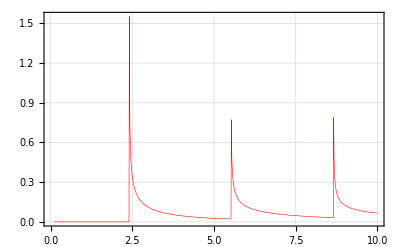

```mathematica
DRResAsyRO5=ListLinePlot[{{Re[#1],Re[#2]}&@@@Indata},PlotRange->{{0,10},Full},InterpolationOrder->1,MaxPlotPoints->Infinity,PlotStyle->Directive[Red,Thickness[0.001]],ScalingFunctions->{"Linear","Linear"},Frame->True,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black},GridLines->Automatic]
```

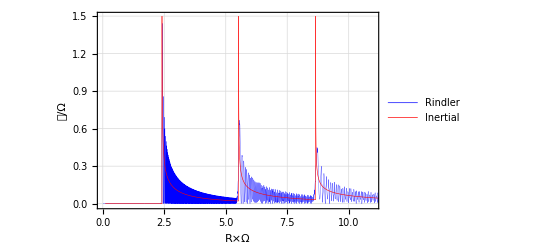

```mathematica
Final=ListLinePlot[{{Re[#1],Re[#2]}&@@@s,{Re[#1],Re[#2]}&@@@Indata},PlotRange->{{0,11},{-0.01,1.5}},InterpolationOrder->1,MaxPlotPoints->Infinity,PlotStyle->{Directive[Blue,Thickness[0.0005]],Directive[Red,Thickness[0.001]]},FrameLabel->{"R×Ω","𝒞/Ω"},PlotLegends->Placed[{"Rindler","Inertial"}
,{0.82,0.8}],ScalingFunctions->{"Linear","Linear"},Frame->True,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black},GridLines->Automatic]
```

```mathematica
s1=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,1],10^Oa,3]]},{Oa,3,8,1/10}]
```

{{1000,0.172988},{1000 10^(1/10),0.186788},{1000 10^(1/5),0.201689},{1000 10^(3/10),0.217778},{1000 10^(2/5),0.235152},{1000 √10,0.253911},{1000 10^(3/5),0.274167},{1000 10^(7/10),0.296038},{1000 10^(4/5),0.319655},{1000 10^(9/10),0.345156},{10000,0.37269},{10000 10^(1/10),0.402422},{10000 10^(1/5),0.434525},{10000 10^(3/10),0.469189},{10000 10^(2/5),0.506619},{10000 √10,0.547035},{10000 10^(3/5),0.590674},{10000 10^(7/10),0.637796},{10000 10^(4/5),0.688676},{10000 10^(9/10),0.743615},{100000,0.802937},{100000 10^(1/10),0.866992},{100000 10^(1/5),0.936156},{100000 10^(3/10),1.01084},{100000 10^(2/5),1.09148},{100000 √10,1.17855},{100000 10^(3/5),1.27257},{100000 10^(7/10),1.37409},{100000 10^(4/5),1.48371},{100000 10^(9/10),1.60207},{1000000,1.72988},{1000000 10^(1/10),1.86788},{1000000 10^(1/5),2.01689},{1000000 10^(3/10),2.17778},{1000000 10^(2/5),2.35152},{1000000 √10,2.53911},{1000000 10^(3/5),2.74167},{1000000 10^(7/10),2.96038},{1000000 10^(4/5),3.19655},{1000000 10^(9/10),3.45156},{10000000,3.7269},{10000000 10^(1/10),4.02422},{10000000 10^(1/5),4.34525},{10000000 10^(3/10),4.69189},{10000000 10^(2/5),5.06619},{10000000 √10,5.47035},{10000000 10^(3/5),5.90674},{10000000 10^(7/10),6.37796},{10000000 10^(4/5),6.88676},{10000000 10^(9/10),7.43615},{100000000,8.02937}}

```mathematica
s2=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,1]+1/200,10^Oa,3]]},{Oa,3,8,1/100}]
```

{{1000,0.901994},{1000 10^(1/100),0.913222},{1000 10^(1/50),0.924638},{1000 10^(3/100),0.936247},{1000 10^(1/25),0.948051},{1000 10^(1/20),0.960055},{1000 10^(3/50),0.972262},{1000 10^(7/100),0.984677},{1000 10^(2/25),0.997303},{1000 10^(9/100),1.01014},{1000 10^(1/10),1.02321},{1000 10^(11/100),1.03649},{1000 10^(3/25),1.05},{1000 10^(13/100),1.06375},{1000 10^(7/50),1.07773},{1000 10^(3/20),1.09195},{1000 10^(4/25),1.10642},{1000 10^(17/100),1.12114},{1000 10^(9/50),1.13611},{1000 10^(19/100),1.15134},{1000 10^(1/5),1.16683},{1000 10^(21/100),1.1826},{1000 10^(11/50),1.19863},{1000 10^(23/100),1.21494},{1000 10^(6/25),1.23154},{1000 10^(1/4),1.24841},{1000 10^(13/50),1.26559},{1000 10^(27/100),1.28305},{1000 10^(7/25),1.30082},{1000 10^(29/100),1.31889},{1000 10^(3/10),1.33727},{1000 10^(31/100),1.35596},{1000 10^(8/25),1.37497},{1000 10^(33/100),1.3943},{1000 10^(17/50),1.41396},{1000 10^(7/20),1.43395},{1000 10^(9/25),1.45427},{1000 10^(37/100),1.47493},{1000 10^(19/50),1.49593},{1000 10^(39/100),1.51728},{1000 10^(2/5),1.53897},{1000 10^(41/100),1.56102},{1000 10^(21/50),1.58341},{1000 10^(43/100),1.60616},{1000 10^(11/25),1.62927},{1000 10^(9/20),1.65274},{1000 10^(23/50),1.67656},{1000 10^(47/100),1.70075},{1000 10^(12/25),1.7253},{1000 10^(49/100),1.7502},{1000 √10,1.77547},{1000 10^(51/100),1.80109},{1000 10^(13/25),1.82706},{1000 10^(53/100),1.85339},{1000 10^(27/50),1.88007},{1000 10^(11/20),1.90708},{1000 10^(14/25),1.93444},{1000 10^(57/100),1.96212},{1000 10^(29/50),1.99012},{1000 10^(59/100),2.01844},{1000 10^(3/5),2.04705},{1000 10^(61/100),2.07596},{1000 10^(31/50),2.10514},{1000 10^(63/100),2.13458},{1000 10^(16/25),2.16426},{1000 10^(13/20),2.19417},{1000 10^(33/50),2.22428},{1000 10^(67/100),2.25458},{1000 10^(17/25),2.28503},{1000 10^(69/100),2.31561},{1000 10^(7/10),2.34628},{1000 10^(71/100),2.37702},{1000 10^(18/25),2.40779},{1000 10^(73/100),2.43856},{1000 10^(37/50),2.46927},{1000 10^(3/4),2.49988},{1000 10^(19/25),2.53035},{1000 10^(77/100),2.56062},{1000 10^(39/50),2.59064},{1000 10^(79/100),2.62034},{1000 10^(4/5),2.64966},{1000 10^(81/100),2.67854},{1000 10^(41/50),2.70688},{1000 10^(83/100),2.73462},{1000 10^(21/25),2.76168},{1000 10^(17/20),2.78795},{1000 10^(43/50),2.81335},{1000 10^(87/100),2.83778},{1000 10^(22/25),2.86112},{1000 10^(89/100),2.88326},{1000 10^(9/10),2.90409},{1000 10^(91/100),2.92348},{1000 10^(23/25),2.9413},{1000 10^(93/100),2.95741},{1000 10^(47/50),2.97166},{1000 10^(19/20),2.98391},{1000 10^(24/25),2.994},{1000 10^(97/100),3.00177},{1000 10^(49/50),3.00705},{1000 10^(99/100),3.00966},{10000,3.00944},{10000 10^(1/100),3.0062},{10000 10^(1/50),2.99975},{10000 10^(3/100),2.9899},{10000 10^(1/25),2.97648},{10000 10^(1/20),2.95929},{10000 10^(3/50),2.93814},{10000 10^(7/100),2.91285},{10000 10^(2/25),2.88324},{10000 10^(9/100),2.84913},{10000 10^(1/10),2.81036},{10000 10^(11/100),2.76677},{10000 10^(3/25),2.71823},{10000 10^(13/100),2.66461},{10000 10^(7/50),2.6058},{10000 10^(3/20),2.54174},{10000 10^(4/25),2.47237},{10000 10^(17/100),2.39766},{10000 10^(9/50),2.31766},{10000 10^(19/100),2.2324},{10000 10^(1/5),2.14201},{10000 10^(21/100),2.04665},{10000 10^(11/50),1.94654},{10000 10^(23/100),1.84195},{10000 10^(6/25),1.73326},{10000 10^(1/4),1.62089},{10000 10^(13/50),1.50534},{10000 10^(27/100),1.38723},{10000 10^(7/25),1.26724},{10000 10^(29/100),1.14616},{10000 10^(3/10),1.02487},{10000 10^(31/100),0.904355},{10000 10^(8/25),0.785713},{10000 10^(33/100),0.670128},{10000 10^(17/50),0.558886},{10000 10^(7/20),0.453367},{10000 10^(9/25),0.355032},{10000 10^(37/100),0.265414},{10000 10^(19/50),0.186105},{10000 10^(39/100),0.11873},{10000 10^(2/5),0.0649301},{10000 10^(41/100),0.0263289},{10000 10^(21/50),0.00450062},{10000 10^(43/100),0.000930627},{10000 10^(11/25),0.0169712},{10000 10^(9/20),0.0537919},{10000 10^(23/50),0.112326},{10000 10^(47/100),0.19321},{10000 10^(12/25),0.296728},{10000 10^(49/100),0.42274},{10000 √10,0.570626},{10000 10^(51/100),0.739223},{10000 10^(13/25),0.926767},{10000 10^(53/100),1.13085},{10000 10^(27/50),1.34838},{10000 10^(11/20),1.57556},{10000 10^(14/25),1.8079},{10000 10^(57/100),2.04024},{10000 10^(29/50),2.2668},{10000 10^(59/100),2.48129},{10000 10^(3/5),2.67705},{10000 10^(61/100),2.8472},{10000 10^(31/50),2.98489},{10000 10^(63/100),3.08356},{10000 10^(16/25),3.13727},{10000 10^(13/20),3.14102},{10000 10^(33/50),3.09115},{10000 10^(67/100),2.98571},{10000 10^(17/25),2.82485},{10000 10^(69/100),2.61114},{10000 10^(7/10),2.34986},{10000 10^(71/100),2.04918},{10000 10^(18/25),1.72018},{10000 10^(73/100),1.37672},{10000 10^(37/50),1.03511},{10000 10^(3/4),0.713489},{10000 10^(19/25),0.431006},{10000 10^(77/100),0.206718},{10000 10^(39/50),0.0582666},{10000 10^(79/100),0.00037684},{10000 10^(4/5),0.0432716},{10000 10^(81/100),0.19112},{10000 10^(41/50),0.44068},{10000 10^(83/100),0.780316},{10000 10^(21/25),1.1896},{10000 10^(17/20),1.63969},{10000 10^(43/50),2.09462},{10000 10^(87/100),2.51368},{10000 10^(22/25),2.85481},{10000 10^(89/100),3.07883},{10000 10^(9/10),3.15439},{10000 10^(91/100),3.06293},{10000 10^(23/25),2.80308},{10000 10^(93/100),2.39379},{10000 10^(47/50),1.87525},{10000 10^(19/20),1.30693},{10000 10^(24/25),0.762296},{10000 10^(97/100),0.320141},{10000 10^(49/50),0.0531095},{10000 10^(99/100),0.014778},{100000,0.227269},{100000 10^(1/100),0.67198},{100000 10^(1/50),1.28615},{100000 10^(3/100),1.9676},{100000 10^(1/25),2.58875},{100000 10^(1/20),3.01939},{100000 10^(3/50),3.15499},{100000 10^(7/100),2.94516},{100000 10^(2/25),2.41493},{100000 10^(9/100),1.67112},{100000 10^(1/10),0.888042},{100000 10^(11/100),0.271028},{100000 10^(3/25),0.00276447},{100000 10^(13/100),0.184862},{100000 10^(7/50),0.792537},{100000 10^(3/20),1.66159},{100000 10^(4/25),2.52113},{100000 10^(17/100),3.07216},{100000 10^(9/50),3.0941},{100000 10^(19/100),2.54331},{100000 10^(1/5),1.60008},{100000 10^(21/100),0.629306},{100000 10^(11/50),0.0496551},{100000 10^(23/100),0.149244},{100000 10^(6/25),0.925473},{100000 10^(1/4),2.03884},{100000 10^(13/50),2.93634},{100000 10^(27/100),3.11988},{100000 10^(7/25),2.44016},{100000 10^(29/100),1.24208},{100000 10^(3/10),0.229114},{100000 10^(31/100),0.0631451},{100000 10^(8/25),0.908558},{100000 10^(33/100),2.23693},{100000 10^(17/50),3.10806},{100000 10^(7/20),2.82993},{100000 10^(9/25),1.55374},{100000 10^(37/100),0.278265},{100000 10^(19/50),0.107674},{100000 10^(39/100),1.26149},{100000 10^(2/5),2.73107},{100000 10^(41/100),3.09216},{100000 10^(21/50),1.91171},{100000 10^(43/100),0.361214},{100000 10^(11/25),0.142756},{100000 10^(9/20),1.58261},{100000 10^(23/50),3.03529},{100000 10^(47/100),2.67844},{100000 10^(12/25),0.883178},{100000 10^(49/100),0.015566},{100000 √10,1.34922},{100000 10^(51/100),3.032},{100000 10^(13/25),2.50857},{100000 10^(53/100),0.506498},{100000 10^(27/50),0.261703},{100000 10^(11/20),2.27177},{100000 10^(14/25),3.05872},{100000 10^(57/100),1.11966},{100000 10^(29/50),0.0564998},{100000 10^(59/100),2.01154},{100000 10^(3/5),3.07692},{100000 10^(61/100),0.955024},{100000 10^(31/50),0.215309},{100000 10^(63/100),2.58414},{100000 10^(16/25),2.57171},{100000 10^(13/20),0.148083},{100000 10^(33/50),1.34128},{100000 10^(67/100),3.13391},{100000 10^(17/25),0.754063},{100000 10^(69/100),0.683625},{100000 10^(7/10),3.14346},{100000 10^(71/100),1.00396},{100000 10^(18/25),0.63903},{100000 10^(73/100),3.15804},{100000 10^(37/50),0.645498},{100000 10^(3/4),1.22607},{100000 10^(19/25),2.93382},{100000 10^(77/100),0.0348525},{100000 10^(39/50),2.55436},{100000 10^(79/100),1.53603},{100000 10^(4/5),0.750866},{100000 10^(81/100),2.96639},{100000 10^(41/50),0.00124544},{100000 10^(83/100),3.05928},{100000 10^(21/25),0.360457},{100000 10^(17/20),2.49001},{100000 10^(43/50),0.943327},{100000 10^(87/100),2.02021},{100000 10^(22/25),1.23249},{100000 10^(89/100),1.94203},{100000 10^(9/10),1.08945},{100000 10^(91/100),2.30054},{100000 10^(23/25),0.550004},{100000 10^(93/100),2.92864},{100000 10^(47/50),0.0181376},{100000 10^(19/20),3.07577},{100000 10^(24/25),0.58166},{100000 10^(97/100),1.63619},{100000 10^(49/50),2.59686},{100000 10^(99/100),0.00155676},{1000000,2.59249},{1000000 10^(1/100),2.07157},{1000000 10^(1/50),0.0162874},{1000000 10^(3/100),2.34398},{1000000 10^(1/25),2.71797},{1000000 10^(1/20),0.320669},{1000000 10^(3/50),0.690103},{1000000 10^(7/100),2.83074},{1000000 10^(2/25),2.73994},{1000000 10^(9/100),0.874765},{1000000 10^(1/10),0.0031473},{1000000 10^(11/100),0.884986},{1000000 10^(3/25),2.30221},{1000000 10^(13/100),3.09302},{1000000 10^(7/50),3.04083},{1000000 10^(3/20),2.51515},{1000000 10^(4/25),1.92398},{1000000 10^(17/100),1.48857},{1000000 10^(9/50),1.27314},{1000000 10^(19/100),1.28174},{1000000 10^(1/5),1.52008},{1000000 10^(21/100),1.99207},{1000000 10^(11/50),2.62041},{1000000 10^(23/100),3.11391},{1000000 10^(6/25),2.93883},{1000000 10^(1/4),1.73629},{1000000 10^(13/50),0.245362},{1000000 10^(27/100),0.384351},{1000000 10^(7/25),2.46524},{1000000 10^(29/100),2.82849},{1000000 10^(3/10),0.336351},{1000000 10^(31/100),1.2214},{1000000 10^(8/25),3.03368},{1000000 10^(33/100),0.0921554},{1000000 10^(17/50),2.57955},{1000000 10^(7/20),1.03638},{1000000 10^(9/25),1.93618},{1000000 10^(37/100),1.08035},{1000000 10^(19/50),2.51846},{1000000 10^(39/100),0.119719},{1000000 10^(2/5),3.04464},{1000000 10^(41/100),1.30216},{1000000 10^(21/50),0.187508},{1000000 10^(43/100),2.41735},{1000000 10^(11/25),3.05086},{1000000 10^(9/20),1.69969},{1000000 10^(23/50),0.468654},{1000000 10^(47/100),0.0338285},{1000000 10^(12/25),0.00742575},{1000000 10^(49/100),0.0105674},{1000000 √10,0.0196212},{1000000 10^(51/100),0.402895},{1000000 10^(13/25),1.63981},{1000000 10^(53/100),3.06798},{1000000 10^(27/50),2.19322},{1000000 10^(11/20),0.0132727},{1000000 10^(14/25),2.30208},{1000000 10^(57/100),1.81088},{1000000 10^(29/50),0.938089},{1000000 10^(59/100),2.09048},{1000000 10^(3/5),1.77937},{1000000 10^(61/100),0.285559},{1000000 10^(31/50),2.87613},{1000000 10^(63/100),2.53434},{1000000 10^(16/25),0.855337},{1000000 10^(13/20),0.113752},{1000000 10^(33/50),0.00662115},{1000000 10^(67/100),0.0429144},{1000000 10^(17/25),0.499663},{1000000 10^(69/100),2.02247},{1000000 10^(7/10),3.12276},{1000000 10^(71/100),0.665032},{1000000 10^(18/25),1.47709},{1000000 10^(73/100),1.97116},{1000000 10^(37/50),1.69199},{1000000 10^(3/4),0.329413},{1000000 10^(19/25),2.77094},{1000000 10^(77/100),2.95949},{1000000 10^(39/50),2.18891},{1000000 10^(79/100),2.04503},{1000000 10^(4/5),2.69629},{1000000 10^(81/100),3.08929},{1000000 10^(41/50),0.93466},{1000000 10^(83/100),0.960519},{1000000 10^(21/25),2.45325},{1000000 10^(17/20),1.39704},{1000000 10^(43/50),0.2299},{1000000 10^(87/100),2.03373},{1000000 10^(22/25),2.82335},{1000000 10^(89/100),2.71748},{1000000 10^(9/10),1.52922},{1000000 10^(91/100),0.00186918},{1000000 10^(23/25),2.74942},{1000000 10^(93/100),0.407726},{1000000 10^(47/50),3.15472},{1000000 10^(19/20),1.7856},{1000000 10^(24/25),0.770751},{1000000 10^(97/100),1.04763},{1000000 10^(49/50),2.63657},{1000000 10^(99/100),2.23528},{10000000,0.604001},{10000000 10^(1/100),1.5119},{10000000 10^(1/50),3.14146},{10000000 10^(3/100),3.0751},{10000000 10^(1/25),3.12358},{10000000 10^(1/20),1.24087},{10000000 10^(3/50),1.12921},{10000000 10^(7/100),1.12501},{10000000 10^(2/25),3.02593},{10000000 10^(9/100),3.15077},{10000000 10^(1/10),2.49598},{10000000 10^(11/100),0.0173222},{10000000 10^(3/25),3.15805},{10000000 10^(13/100),1.21128},{10000000 10^(7/50),0.519432},{10000000 10^(3/20),1.68878},{10000000 10^(4/25),2.84665},{10000000 10^(17/100),0.733971},{10000000 10^(9/50),0.107044},{10000000 10^(19/100),0.0777347},{10000000 10^(1/5),1.01447},{10000000 10^(21/100),2.32038},{10000000 10^(11/50),2.83873},{10000000 10^(23/100),2.66998},{10000000 10^(6/25),2.84914},{10000000 10^(1/4),0.261994},{10000000 10^(13/50),0.632724},{10000000 10^(27/100),0.391343},{10000000 10^(7/25),1.082},{10000000 10^(29/100),1.09762},{10000000 10^(3/10),2.13157},{10000000 10^(31/100),0.379632},{10000000 10^(8/25),2.78867},{10000000 10^(33/100),1.13661},{10000000 10^(17/50),2.44707},{10000000 10^(7/20),1.00097},{10000000 10^(9/25),2.77217},{10000000 10^(37/100),1.45368},{10000000 10^(19/50),1.7227},{10000000 10^(39/100),0.479041},{10000000 10^(2/5),2.58371},{10000000 10^(41/100),0.0277056},{10000000 10^(21/50),0.032792},{10000000 10^(43/100),2.59219},{10000000 10^(11/25),0.726616},{10000000 10^(9/20),2.67656},{10000000 10^(23/50),0.00279603},{10000000 10^(47/100),0.199346},{10000000 10^(12/25),2.87769},{10000000 10^(49/100),3.02255},{10000000 √10,0.000113752},{10000000 10^(51/100),0.22892},{10000000 10^(13/25),2.17602},{10000000 10^(53/100),1.17224},{10000000 10^(27/50),2.76148},{10000000 10^(11/20),3.0982},{10000000 10^(14/25),0.00157531},{10000000 10^(57/100),0.00850746},{10000000 10^(29/50),2.93782},{10000000 10^(59/100),1.81524},{10000000 10^(3/5),3.08951},{10000000 10^(61/100),1.29807},{10000000 10^(31/50),1.89956},{10000000 10^(63/100),1.91431},{10000000 10^(16/25),3.15705},{10000000 10^(13/20),2.57293},{10000000 10^(33/50),0.323432},{10000000 10^(67/100),0.444405},{10000000 10^(17/25),0.0851793},{10000000 10^(69/100),2.03822},{10000000 10^(7/10),0.250663},{10000000 10^(71/100),1.41219},{10000000 10^(18/25),0.629695},{10000000 10^(73/100),0.639108},{10000000 10^(37/50),2.61654},{10000000 10^(3/4),2.03194},{10000000 10^(19/25),0.362878},{10000000 10^(77/100),0.102681},{10000000 10^(39/50),0.421222},{10000000 10^(79/100),1.80952},{10000000 10^(4/5),3.15874},{10000000 10^(81/100),1.324},{10000000 10^(41/50),0.197251},{10000000 10^(83/100),2.79907},{10000000 10^(21/25),2.22651},{10000000 10^(17/20),0.134637},{10000000 10^(43/50),0.422466},{10000000 10^(87/100),1.22602},{10000000 10^(22/25),1.02714},{10000000 10^(89/100),0.0286597},{10000000 10^(9/10),2.07553},{10000000 10^(91/100),0.838226},{10000000 10^(23/25),2.97223},{10000000 10^(93/100),2.96085},{10000000 10^(47/50),0.541645},{10000000 10^(19/20),3.10582},{10000000 10^(24/25),2.82618},{10000000 10^(97/100),2.03199},{10000000 10^(49/50),2.95101},{10000000 10^(99/100),3.01409},{100000000,1.00566}}

```mathematica
s3=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,1]+1/100,10^Oa,3]]},{Oa,3,8,1/100}]
```

{{1000,1.16664},{1000 10^(1/100),1.18346},{1000 10^(1/50),1.20053},{1000 10^(3/100),1.21786},{1000 10^(1/25),1.23544},{1000 10^(1/20),1.25327},{1000 10^(3/50),1.27136},{1000 10^(7/100),1.28969},{1000 10^(2/25),1.30828},{1000 10^(9/100),1.3271},{1000 10^(1/10),1.34617},{1000 10^(11/100),1.36548},{1000 10^(3/25),1.38501},{1000 10^(13/100),1.40478},{1000 10^(7/50),1.42476},{1000 10^(3/20),1.44495},{1000 10^(4/25),1.46535},{1000 10^(17/100),1.48594},{1000 10^(9/50),1.50672},{1000 10^(19/100),1.52766},{1000 10^(1/5),1.54877},{1000 10^(21/100),1.57001},{1000 10^(11/50),1.59139},{1000 10^(23/100),1.61287},{1000 10^(6/25),1.63444},{1000 10^(1/4),1.65608},{1000 10^(13/50),1.67776},{1000 10^(27/100),1.69946},{1000 10^(7/25),1.72116},{1000 10^(29/100),1.74281},{1000 10^(3/10),1.7644},{1000 10^(31/100),1.78588},{1000 10^(8/25),1.80722},{1000 10^(33/100),1.82838},{1000 10^(17/50),1.84931},{1000 10^(7/20),1.86998},{1000 10^(9/25),1.89032},{1000 10^(37/100),1.91029},{1000 10^(19/50),1.92983},{1000 10^(39/100),1.94887},{1000 10^(2/5),1.96737},{1000 10^(41/100),1.98524},{1000 10^(21/50),2.00243},{1000 10^(43/100),2.01884},{1000 10^(11/25),2.03441},{1000 10^(9/20),2.04904},{1000 10^(23/50),2.06265},{1000 10^(47/100),2.07515},{1000 10^(12/25),2.08643},{1000 10^(49/100),2.0964},{1000 √10,2.10496},{1000 10^(51/100),2.11198},{1000 10^(13/25),2.11735},{1000 10^(53/100),2.12097},{1000 10^(27/50),2.12269},{1000 10^(11/20),2.12241},{1000 10^(14/25),2.11999},{1000 10^(57/100),2.1153},{1000 10^(29/50),2.10821},{1000 10^(59/100),2.09859},{1000 10^(3/5),2.0863},{1000 10^(61/100),2.07122},{1000 10^(31/50),2.0532},{1000 10^(63/100),2.03213},{1000 10^(16/25),2.00788},{1000 10^(13/20),1.98033},{1000 10^(33/50),1.94938},{1000 10^(67/100),1.91494},{1000 10^(17/25),1.8769},{1000 10^(69/100),1.83521},{1000 10^(7/10),1.7898},{1000 10^(71/100),1.74065},{1000 10^(18/25),1.68774},{1000 10^(73/100),1.63109},{1000 10^(37/50),1.57074},{1000 10^(3/4),1.50678},{1000 10^(19/25),1.43931},{1000 10^(77/100),1.36851},{1000 10^(39/50),1.29457},{1000 10^(79/100),1.21775},{1000 10^(4/5),1.13834},{1000 10^(81/100),1.05673},{1000 10^(41/50),0.973337},{1000 10^(83/100),0.888648},{1000 10^(21/25),0.803224},{1000 10^(17/20),0.717693},{1000 10^(43/50),0.632757},{1000 10^(87/100),0.549186},{1000 10^(22/25),0.467824},{1000 10^(89/100),0.389582},{1000 10^(9/10),0.315436},{1000 10^(91/100),0.246421},{1000 10^(23/25),0.18362},{1000 10^(93/100),0.128157},{1000 10^(47/50),0.0811805},{1000 10^(19/20),0.0438475},{1000 10^(24/25),0.0173016},{1000 10^(97/100),0.00265018},{1000 10^(49/50),0.000936046},{1000 10^(99/100),0.0131062},{10000,0.0399767},{10000 10^(1/100),0.0821942},{10000 10^(1/50),0.140195},{10000 10^(3/100),0.214161},{10000 10^(1/25),0.303975},{10000 10^(1/20),0.409179},{10000 10^(3/50),0.528927},{10000 10^(7/100),0.66195},{10000 10^(2/25),0.806519},{10000 10^(9/100),0.960425},{10000 10^(1/10),1.12096},{10000 10^(11/100),1.28493},{10000 10^(3/25),1.44867},{10000 10^(13/100),1.60808},{10000 10^(7/50),1.7587},{10000 10^(3/20),1.89582},{10000 10^(4/25),2.01458},{10000 10^(17/100),2.11016},{10000 10^(9/50),2.17797},{10000 10^(19/100),2.21382},{10000 10^(1/5),2.21426},{10000 10^(21/100),2.17677},{10000 10^(11/50),2.10004},{10000 10^(23/100),1.98429},{10000 10^(6/25),1.83142},{10000 10^(1/4),1.6453},{10000 10^(13/50),1.4318},{10000 10^(27/100),1.19885},{10000 10^(7/25),0.956362},{10000 10^(29/100),0.715906},{10000 10^(3/10),0.490345},{10000 10^(31/100),0.293204},{10000 10^(8/25),0.137891},{10000 10^(33/100),0.0367557},{10000 10^(17/50),0.0000244826},{10000 10^(7/20),0.0346814},{10000 10^(9/25),0.143378},{10000 10^(37/100),0.32349},{10000 10^(19/50),0.566441},{10000 10^(39/100),0.857455},{10000 10^(2/5),1.17585},{10000 10^(41/100),1.49602},{10000 10^(21/50),1.78911},{10000 10^(43/100),2.02548},{10000 10^(11/25),2.17775},{10000 10^(9/20),2.22424},{10000 10^(23/50),2.15251},{10000 10^(47/100),1.96239},{10000 10^(12/25),1.66817},{10000 10^(49/100),1.29904},{10000 √10,0.897688},{10000 10^(51/100),0.516342},{10000 10^(13/25),0.210552},{10000 10^(53/100),0.0310104},{10000 10^(27/50),0.0144063},{10000 10^(11/20),0.174772},{10000 10^(14/25),0.497138},{10000 10^(57/100),0.935416},{10000 10^(29/50),1.41611},{10000 10^(59/100),1.84865},{10000 10^(3/5),2.14168},{10000 10^(61/100),2.22323},{10000 10^(31/50),2.06062},{10000 10^(63/100),1.67495},{10000 10^(16/25),1.14485},{10000 10^(13/20),0.595472},{10000 10^(33/50),0.171801},{10000 10^(67/100),0.000396227},{10000 10^(17/25),0.148311},{10000 10^(69/100),0.592141},{10000 10^(7/10),1.21057},{10000 10^(71/100),1.8095},{10000 10^(18/25),2.17919},{10000 10^(73/100),2.16979},{10000 10^(37/50),1.75958},{10000 10^(3/4),1.08499},{10000 10^(19/25),0.408804},{10000 10^(77/100),0.0245888},{10000 10^(39/50),0.125925},{10000 10^(79/100),0.696561},{10000 10^(4/5),1.48433},{10000 10^(81/100),2.09549},{10000 10^(41/50),2.18808},{10000 10^(83/100),1.67648},{10000 10^(21/25),0.823999},{10000 10^(17/20),0.134331},{10000 10^(43/50),0.061577},{10000 10^(87/100),0.693326},{10000 10^(22/25),1.63035},{10000 10^(89/100),2.20548},{10000 10^(9/10),1.95704},{10000 10^(91/100),1.03299},{10000 10^(23/25),0.161318},{10000 10^(93/100),0.101645},{10000 10^(47/50),0.95609},{10000 10^(19/20),1.97175},{10000 10^(24/25),2.15848},{10000 10^(97/100),1.27724},{10000 10^(49/50),0.209642},{10000 10^(99/100),0.134412},{100000,1.1935},{100000 10^(1/100),2.16876},{100000 10^(1/50),1.82886},{100000 10^(3/100),0.549884},{100000 10^(1/25),0.0260492},{100000 10^(1/20),1.03788},{100000 10^(3/50),2.16994},{100000 10^(7/100),1.69362},{100000 10^(2/25),0.291661},{100000 10^(9/100),0.24039},{100000 10^(1/10),1.6878},{100000 10^(11/100),2.11824},{100000 10^(3/25),0.693572},{100000 10^(13/100),0.0721925},{100000 10^(7/50),1.51988},{100000 10^(3/20),2.13036},{100000 10^(4/25),0.573203},{100000 10^(17/100),0.21452},{100000 10^(9/50),1.90881},{100000 10^(19/100),1.71667},{100000 10^(1/5),0.0588063},{100000 10^(21/100),1.07085},{100000 10^(11/50),2.18041},{100000 10^(23/100),0.424081},{100000 10^(6/25),0.597233},{100000 10^(1/4),2.22759},{100000 10^(13/50),0.580516},{100000 10^(27/100),0.571684},{100000 10^(7/25),2.22166},{100000 10^(29/100),0.339976},{100000 10^(3/10),1.01712},{100000 10^(31/100),1.97858},{100000 10^(8/25),0.0023757},{100000 10^(33/100),1.92363},{100000 10^(17/50),0.915093},{100000 10^(7/20),0.683518},{100000 10^(9/25),1.99534},{100000 10^(37/100),0.0227769},{100000 10^(19/50),2.2077},{100000 10^(39/100),0.146484},{100000 10^(2/5),1.9044},{100000 10^(41/100),0.491341},{100000 10^(21/50),1.614},{100000 10^(43/100),0.671494},{100000 10^(11/25),1.57118},{100000 10^(9/20),0.56895},{100000 10^(23/50),1.80957},{100000 10^(47/100),0.231114},{100000 10^(12/25),2.16521},{100000 10^(49/100),0.00220911},{100000 √10,2.06627},{100000 10^(51/100),0.620424},{100000 10^(13/25),0.899088},{100000 10^(53/100),2.01041},{100000 10^(27/50),0.0214315},{100000 10^(11/20),1.59832},{100000 10^(14/25),1.71419},{100000 10^(57/100),0.00727757},{100000 10^(29/50),1.38001},{100000 10^(59/100),2.09387},{100000 10^(3/5),0.443616},{100000 10^(61/100),0.254601},{100000 10^(31/50),1.76563},{100000 10^(63/100),2.11736},{100000 10^(16/25),0.937328},{100000 10^(13/20),0.0338544},{100000 10^(33/50),0.336265},{100000 10^(67/100),1.28083},{100000 10^(17/25),2.01916},{100000 10^(69/100),2.22647},{100000 10^(7/10),2.04043},{100000 10^(71/100),1.72084},{100000 10^(18/25),1.45058},{100000 10^(73/100),1.31107},{100000 10^(37/50),1.32666},{100000 10^(3/4),1.4991},{100000 10^(19/25),1.80048},{100000 10^(77/100),2.12072},{100000 10^(39/50),2.20984},{100000 10^(79/100),1.75055},{100000 10^(4/5),0.743669},{100000 10^(81/100),0.00753081},{100000 10^(41/50),0.680974},{100000 10^(83/100),2.0884},{100000 10^(21/25),1.57991},{100000 10^(17/20),0.0166253},{100000 10^(43/50),1.41598},{100000 10^(87/100),1.79258},{100000 10^(22/25),0.0187415},{100000 10^(89/100),2.16187},{100000 10^(9/10),0.239419},{100000 10^(91/100),1.90717},{100000 10^(23/25),0.241832},{100000 10^(93/100),2.163},{100000 10^(47/50),0.025221},{100000 10^(19/20),1.71421},{100000 10^(24/25),1.60556},{100000 10^(97/100),0.0135446},{100000 10^(49/50),0.998071},{100000 10^(99/100),2.17566},{1000000,1.89009},{1000000 10^(1/100),1.037},{1000000 10^(1/50),0.452262},{1000000 10^(3/100),0.225384},{1000000 10^(1/25),0.224447},{1000000 10^(1/20),0.454482},{1000000 10^(3/50),1.06629},{1000000 10^(7/100),1.95404},{1000000 10^(2/25),2.09433},{1000000 10^(9/100),0.623876},{1000000 10^(1/10),0.294976},{1000000 10^(11/100),2.20547},{1000000 10^(3/25),0.339515},{1000000 10^(13/100),1.66643},{1000000 10^(7/50),0.458169},{1000000 10^(3/20),2.11076},{1000000 10^(4/25),0.0850784},{1000000 10^(17/100),1.04233},{1000000 10^(9/50),2.21839},{1000000 10^(19/100),1.74262},{1000000 10^(1/5),1.01611},{1000000 10^(21/100),0.729322},{1000000 10^(11/50),0.90986},{1000000 10^(23/100),1.57527},{1000000 10^(6/25),2.22431},{1000000 10^(1/4),1.24892},{1000000 10^(13/50),0.0533621},{1000000 10^(27/100),2.16329},{1000000 10^(7/25),0.135149},{1000000 10^(29/100),2.21613},{1000000 10^(3/10),0.28272},{1000000 10^(31/100),0.518821},{1000000 10^(8/25),1.76753},{1000000 10^(33/100),2.17446},{1000000 10^(17/50),2.19362},{1000000 10^(7/20),1.91359},{1000000 10^(9/25),0.76522},{1000000 10^(37/100),0.124982},{1000000 10^(19/50),2.17574},{1000000 10^(39/100),0.111768},{1000000 10^(2/5),2.22589},{1000000 10^(41/100),0.751426},{1000000 10^(21/50),0.000694779},{1000000 10^(43/100),0.199566},{1000000 10^(11/25),0.116816},{1000000 10^(9/20),0.0963239},{1000000 10^(23/50),1.62968},{1000000 10^(47/100),1.39708},{1000000 10^(12/25),0.884111},{1000000 10^(49/100),0.441929},{1000000 √10,1.92357},{1000000 10^(51/100),2.21693},{1000000 10^(13/25),2.14574},{1000000 10^(53/100),1.17428},{1000000 10^(27/50),0.0922132},{1000000 10^(11/20),2.19884},{1000000 10^(14/25),0.506711},{1000000 10^(57/100),0.093371},{1000000 10^(29/50),0.359938},{1000000 10^(59/100),0.0286818},{1000000 10^(3/5),0.936556},{1000000 10^(61/100),1.74332},{1000000 10^(31/50),1.16541},{1000000 10^(63/100),0.0306048},{1000000 10^(16/25),0.0000402783},{1000000 10^(13/20),0.433063},{1000000 10^(33/50),2.22051},{1000000 10^(67/100),0.00339518},{1000000 10^(17/25),1.17148},{1000000 10^(69/100),1.62308},{1000000 10^(7/10),0.670355},{1000000 10^(71/100),0.570149},{1000000 10^(18/25),1.18128},{1000000 10^(73/100),2.2012},{1000000 10^(37/50),2.15596},{1000000 10^(3/4),0.680864},{1000000 10^(19/25),1.51431},{1000000 10^(77/100),0.050182},{1000000 10^(39/50),0.0308448},{1000000 10^(79/100),1.34395},{1000000 10^(4/5),0.832691},{1000000 10^(81/100),2.13289},{1000000 10^(41/50),1.94473},{1000000 10^(83/100),0.0622639},{1000000 10^(21/25),2.1382},{1000000 10^(17/20),2.21505},{1000000 10^(43/50),1.53502},{1000000 10^(87/100),0.826329},{1000000 10^(22/25),0.0413685},{1000000 10^(89/100),0.775288},{1000000 10^(9/10),1.53733},{1000000 10^(91/100),2.22437},{1000000 10^(23/25),1.57333},{1000000 10^(93/100),0.806751},{1000000 10^(47/50),0.17462},{1000000 10^(19/20),1.74066},{1000000 10^(24/25),0.0101234},{1000000 10^(97/100),8.43203×10^-6},{1000000 10^(49/50),2.07868},{1000000 10^(99/100),1.04203},{10000000,2.21707},{10000000 10^(1/100),0.408704},{10000000 10^(1/50),1.03422},{10000000 10^(3/100),0.89719},{10000000 10^(1/25),0.912588},{10000000 10^(1/20),1.06135},{10000000 10^(3/50),0.656887},{10000000 10^(7/100),1.96903},{10000000 10^(2/25),2.19651},{10000000 10^(9/100),0.0129953},{10000000 10^(1/10),0.0883999},{10000000 10^(11/100),2.12616},{10000000 10^(3/25),2.21306},{10000000 10^(13/100),0.126867},{10000000 10^(7/50),1.13062},{10000000 10^(3/20),0.004616},{10000000 10^(4/25),1.90979},{10000000 10^(17/100),1.78501},{10000000 10^(9/50),0.0394694},{10000000 10^(19/100),0.80375},{10000000 10^(1/5),0.258531},{10000000 10^(21/100),1.52717},{10000000 10^(11/50),0.0397771},{10000000 10^(23/100),0.105411},{10000000 10^(6/25),1.90393},{10000000 10^(1/4),0.0708852},{10000000 10^(13/50),1.07965},{10000000 10^(27/100),0.811032},{10000000 10^(7/25),0.0380185},{10000000 10^(29/100),2.2191},{10000000 10^(3/10),0.173987},{10000000 10^(31/100),0.444619},{10000000 10^(8/25),1.13043},{10000000 10^(33/100),1.07811},{10000000 10^(17/50),0.434854},{10000000 10^(7/20),0.0128008},{10000000 10^(9/25),1.06429},{10000000 10^(37/100),2.22487},{10000000 10^(19/50),1.19693},{10000000 10^(39/100),0.0214487},{10000000 10^(2/5),0.496477},{10000000 10^(41/100),1.30313},{10000000 10^(21/50),1.49704},{10000000 10^(43/100),0.885996},{10000000 10^(11/25),0.0048754},{10000000 10^(9/20),2.07991},{10000000 10^(23/50),0.00599665},{10000000 10^(47/100),0.510032},{10000000 10^(12/25),0.139156},{10000000 10^(49/100),1.32907},{10000000 √10,0.0440176},{10000000 10^(51/100),0.0163685},{10000000 10^(13/25),1.85028},{10000000 10^(53/100),0.54049},{10000000 10^(27/50),2.02486},{10000000 10^(11/20),0.273233},{10000000 10^(14/25),1.66698},{10000000 10^(57/100),0.188455},{10000000 10^(29/50),2.13208},{10000000 10^(59/100),1.9644},{10000000 10^(3/5),0.00039748},{10000000 10^(61/100),1.42111},{10000000 10^(31/50),1.61231},{10000000 10^(63/100),0.322049},{10000000 10^(16/25),1.20712},{10000000 10^(13/20),0.793695},{10000000 10^(33/50),2.12728},{10000000 10^(67/100),0.328825},{10000000 10^(17/25),0.564253},{10000000 10^(69/100),2.22715},{10000000 10^(7/10),0.204658},{10000000 10^(71/100),2.14574},{10000000 10^(18/25),0.481027},{10000000 10^(73/100),0.207094},{10000000 10^(37/50),1.6186},{10000000 10^(3/4),0.275448},{10000000 10^(19/25),0.544683},{10000000 10^(77/100),0.972164},{10000000 10^(39/50),0.329022},{10000000 10^(79/100),2.08585},{10000000 10^(4/5),1.73231},{10000000 10^(81/100),2.06132},{10000000 10^(41/50),0.172339},{10000000 10^(83/100),0.874134},{10000000 10^(21/25),1.98456},{10000000 10^(17/20),2.22594},{10000000 10^(43/50),1.86056},{10000000 10^(87/100),0.549713},{10000000 10^(22/25),0.672969},{10000000 10^(89/100),1.05426},{10000000 10^(9/10),1.87902},{10000000 10^(91/100),0.326594},{10000000 10^(23/25),2.11125},{10000000 10^(93/100),0.733364},{10000000 10^(47/50),1.74957},{10000000 10^(19/20),0.777927},{10000000 10^(24/25),2.20042},{10000000 10^(97/100),1.15658},{10000000 10^(49/50),0.147692},{10000000 10^(99/100),0.444146},{100000000,2.20927}}

```mathematica
s01=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,1]+1/100,10^Oa,2]]/N[InDR[BesselJZero[0,1]+1/100,2]]},{Oa,3,5,1/500}]
```

{{1000,1.04735},{1000 10^(1/500),1.05035},{1000 10^(1/250),1.05336},{1000 10^(3/500),1.05638},{1000 10^(1/125),1.05941},{1000 10^(1/100),1.06245},{1000 10^(3/250),1.0655},{1000 10^(7/500),1.06855},{1000 10^(2/125),1.07162},{1000 10^(9/500),1.07469},{1000 10^(1/50),1.07778},{1000 10^(11/500),1.08087},{1000 10^(3/125),1.08397},{1000 10^(13/500),1.08708},{1000 10^(7/250),1.0902},{1000 10^(3/100),1.09333},{1000 10^(4/125),1.09647},{1000 10^(17/500),1.09962},{1000 10^(9/250),1.10277},{1000 10^(19/500),1.10594},{1000 10^(1/25),1.10911},{1000 10^(21/500),1.1123},{1000 10^(11/250),1.11549},{1000 10^(23/500),1.11869},{1000 10^(6/125),1.1219},{1000 10^(1/20),1.12512},{1000 10^(13/250),1.12835},{1000 10^(27/500),1.13159},{1000 10^(7/125),1.13484},{1000 10^(29/500),1.13809},{1000 10^(3/50),1.14136},{1000 10^(31/500),1.14463},{1000 10^(8/125),1.14792},{1000 10^(33/500),1.15121},{1000 10^(17/250),1.15451},{1000 10^(7/100),1.15782},{1000 10^(9/125),1.16114},{1000 10^(37/500),1.16447},{1000 10^(19/250),1.1678},{1000 10^(39/500),1.17115},{1000 10^(2/25),1.1745},{1000 10^(41/500),1.17787},{1000 10^(21/250),1.18124},{1000 10^(43/500),1.18462},{1000 10^(11/125),1.18801},{1000 10^(9/100),1.1914},{1000 10^(23/250),1.19481},{1000 10^(47/500),1.19823},{1000 10^(12/125),1.20165},{1000 10^(49/500),1.20508},{1000 10^(1/10),1.20852},{1000 10^(51/500),1.21197},{1000 10^(13/125),1.21543},{1000 10^(53/500),1.2189},{1000 10^(27/250),1.22237},{1000 10^(11/100),1.22585},{1000 10^(14/125),1.22935},{1000 10^(57/500),1.23285},{1000 10^(29/250),1.23635},{1000 10^(59/500),1.23987},{1000 10^(3/25),1.24339},{1000 10^(61/500),1.24693},{1000 10^(31/250),1.25047},{1000 10^(63/500),1.25402},{1000 10^(16/125),1.25757},{1000 10^(13/100),1.26114},{1000 10^(33/250),1.26471},{1000 10^(67/500),1.26829},{1000 10^(17/125),1.27188},{1000 10^(69/500),1.27547},{1000 10^(7/50),1.27908},{1000 10^(71/500),1.28269},{1000 10^(18/125),1.28631},{1000 10^(73/500),1.28993},{1000 10^(37/250),1.29357},{1000 10^(3/20),1.29721},{1000 10^(19/125),1.30085},{1000 10^(77/500),1.30451},{1000 10^(39/250),1.30817},{1000 10^(79/500),1.31184},{1000 10^(4/25),1.31552},{1000 10^(81/500),1.3192},{1000 10^(41/250),1.32289},{1000 10^(83/500),1.32659},{1000 10^(21/125),1.33029},{1000 10^(17/100),1.33401},{1000 10^(43/250),1.33772},{1000 10^(87/500),1.34145},{1000 10^(22/125),1.34518},{1000 10^(89/500),1.34891},{1000 10^(9/50),1.35266},{1000 10^(91/500),1.3564},{1000 10^(23/125),1.36016},{1000 10^(93/500),1.36392},{1000 10^(47/250),1.36769},{1000 10^(19/100),1.37146},{1000 10^(24/125),1.37524},{1000 10^(97/500),1.37902},{1000 10^(49/250),1.38281},{1000 10^(99/500),1.38661},{1000 10^(1/5),1.3904},{1000 10^(101/500),1.39421},{1000 10^(51/250),1.39802},{1000 10^(103/500),1.40183},{1000 10^(26/125),1.40565},{1000 10^(21/100),1.40948},{1000 10^(53/250),1.41331},{1000 10^(107/500),1.41714},{1000 10^(27/125),1.42098},{1000 10^(109/500),1.42482},{1000 10^(11/50),1.42867},{1000 10^(111/500),1.43252},{1000 10^(28/125),1.43637},{1000 10^(113/500),1.44023},{1000 10^(57/250),1.44409},{1000 10^(23/100),1.44795},{1000 10^(29/125),1.45182},{1000 10^(117/500),1.45569},{1000 10^(59/250),1.45956},{1000 10^(119/500),1.46344},{1000 10^(6/25),1.46732},{1000 10^(121/500),1.4712},{1000 10^(61/250),1.47508},{1000 10^(123/500),1.47896},{1000 10^(31/125),1.48285},{1000 10^(1/4),1.48674},{1000 10^(63/250),1.49063},{1000 10^(127/500),1.49452},{1000 10^(32/125),1.49842},{1000 10^(129/500),1.50231},{1000 10^(13/50),1.50621},{1000 10^(131/500),1.5101},{1000 10^(33/125),1.514},{1000 10^(133/500),1.5179},{1000 10^(67/250),1.52179},{1000 10^(27/100),1.52569},{1000 10^(34/125),1.52959},{1000 10^(137/500),1.53348},{1000 10^(69/250),1.53738},{1000 10^(139/500),1.54127},{1000 10^(7/25),1.54517},{1000 10^(141/500),1.54906},{1000 10^(71/250),1.55295},{1000 10^(143/500),1.55684},{1000 10^(36/125),1.56072},{1000 10^(29/100),1.56461},{1000 10^(73/250),1.56849},{1000 10^(147/500),1.57237},{1000 10^(37/125),1.57625},{1000 10^(149/500),1.58012},{1000 10^(3/10),1.58399},{1000 10^(151/500),1.58785},{1000 10^(38/125),1.59172},{1000 10^(153/500),1.59557},{1000 10^(77/250),1.59943},{1000 10^(31/100),1.60327},{1000 10^(39/125),1.60712},{1000 10^(157/500),1.61095},{1000 10^(79/250),1.61479},{1000 10^(159/500),1.61861},{1000 10^(8/25),1.62243},{1000 10^(161/500),1.62625},{1000 10^(81/250),1.63005},{1000 10^(163/500),1.63385},{1000 10^(41/125),1.63764},{1000 10^(33/100),1.64143},{1000 10^(83/250),1.6452},{1000 10^(167/500),1.64897},{1000 10^(42/125),1.65273},{1000 10^(169/500),1.65648},{1000 10^(17/50),1.66022},{1000 10^(171/500),1.66395},{1000 10^(43/125),1.66767},{1000 10^(173/500),1.67138},{1000 10^(87/250),1.67508},{1000 10^(7/20),1.67877},{1000 10^(44/125),1.68245},{1000 10^(177/500),1.68611},{1000 10^(89/250),1.68976},{1000 10^(179/500),1.6934},{1000 10^(9/25),1.69703},{1000 10^(181/500),1.70065},{1000 10^(91/250),1.70425},{1000 10^(183/500),1.70783},{1000 10^(46/125),1.7114},{1000 10^(37/100),1.71496},{1000 10^(93/250),1.7185},{1000 10^(187/500),1.72202},{1000 10^(47/125),1.72553},{1000 10^(189/500),1.72902},{1000 10^(19/50),1.7325},{1000 10^(191/500),1.73596},{1000 10^(48/125),1.7394},{1000 10^(193/500),1.74282},{1000 10^(97/250),1.74622},{1000 10^(39/100),1.7496},{1000 10^(49/125),1.75296},{1000 10^(197/500),1.7563},{1000 10^(99/250),1.75963},{1000 10^(199/500),1.76293},{1000 10^(2/5),1.7662},{1000 10^(201/500),1.76946},{1000 10^(101/250),1.77269},{1000 10^(203/500),1.7759},{1000 10^(51/125),1.77909},{1000 10^(41/100),1.78225},{1000 10^(103/250),1.78539},{1000 10^(207/500),1.7885},{1000 10^(52/125),1.79159},{1000 10^(209/500),1.79464},{1000 10^(21/50),1.79768},{1000 10^(211/500),1.80068},{1000 10^(53/125),1.80366},{1000 10^(213/500),1.80661},{1000 10^(107/250),1.80952},{1000 10^(43/100),1.81241},{1000 10^(54/125),1.81527},{1000 10^(217/500),1.8181},{1000 10^(109/250),1.82089},{1000 10^(219/500),1.82366},{1000 10^(11/25),1.82639},{1000 10^(221/500),1.82908},{1000 10^(111/250),1.83175},{1000 10^(223/500),1.83437},{1000 10^(56/125),1.83697},{1000 10^(9/20),1.83952},{1000 10^(113/250),1.84204},{1000 10^(227/500),1.84453},{1000 10^(57/125),1.84697},{1000 10^(229/500),1.84938},{1000 10^(23/50),1.85174},{1000 10^(231/500),1.85407},{1000 10^(58/125),1.85636},{1000 10^(233/500),1.8586},{1000 10^(117/250),1.8608},{1000 10^(47/100),1.86296},{1000 10^(59/125),1.86508},{1000 10^(237/500),1.86715},{1000 10^(119/250),1.86918},{1000 10^(239/500),1.87116},{1000 10^(12/25),1.87309},{1000 10^(241/500),1.87498},{1000 10^(121/250),1.87682},{1000 10^(243/500),1.87861},{1000 10^(61/125),1.88035},{1000 10^(49/100),1.88205},{1000 10^(123/250),1.88369},{1000 10^(247/500),1.88527},{1000 10^(62/125),1.88681},{1000 10^(249/500),1.88829},{1000 √10,1.88972},{1000 10^(251/500),1.8911},{1000 10^(63/125),1.89241},{1000 10^(253/500),1.89368},{1000 10^(127/250),1.89488},{1000 10^(51/100),1.89603},{1000 10^(64/125),1.89711},{1000 10^(257/500),1.89814},{1000 10^(129/250),1.89911},{1000 10^(259/500),1.90001},{1000 10^(13/25),1.90085},{1000 10^(261/500),1.90163},{1000 10^(131/250),1.90235},{1000 10^(263/500),1.90299},{1000 10^(66/125),1.90358},{1000 10^(53/100),1.9041},{1000 10^(133/250),1.90454},{1000 10^(267/500),1.90493},{1000 10^(67/125),1.90524},{1000 10^(269/500),1.90548},{1000 10^(27/50),1.90565},{1000 10^(271/500),1.90574},{1000 10^(68/125),1.90577},{1000 10^(273/500),1.90572},{1000 10^(137/250),1.90559},{1000 10^(11/20),1.90539},{1000 10^(69/125),1.90512},{1000 10^(277/500),1.90476},{1000 10^(139/250),1.90433},{1000 10^(279/500),1.90381},{1000 10^(14/25),1.90322},{1000 10^(281/500),1.90255},{1000 10^(141/250),1.90179},{1000 10^(283/500),1.90095},{1000 10^(71/125),1.90002},{1000 10^(57/100),1.89901},{1000 10^(143/250),1.89791},{1000 10^(287/500),1.89673},{1000 10^(72/125),1.89546},{1000 10^(289/500),1.8941},{1000 10^(29/50),1.89265},{1000 10^(291/500),1.89111},{1000 10^(73/125),1.88947},{1000 10^(293/500),1.88774},{1000 10^(147/250),1.88592},{1000 10^(59/100),1.88401},{1000 10^(74/125),1.882},{1000 10^(297/500),1.87989},{1000 10^(149/250),1.87768},{1000 10^(299/500),1.87538},{1000 10^(3/5),1.87298},{1000 10^(301/500),1.87047},{1000 10^(151/250),1.86787},{1000 10^(303/500),1.86516},{1000 10^(76/125),1.86235},{1000 10^(61/100),1.85943},{1000 10^(153/250),1.85641},{1000 10^(307/500),1.85328},{1000 10^(77/125),1.85005},{1000 10^(309/500),1.84671},{1000 10^(31/50),1.84326},{1000 10^(311/500),1.8397},{1000 10^(78/125),1.83603},{1000 10^(313/500),1.83224},{1000 10^(157/250),1.82835},{1000 10^(63/100),1.82434},{1000 10^(79/125),1.82022},{1000 10^(317/500),1.81598},{1000 10^(159/250),1.81163},{1000 10^(319/500),1.80716},{1000 10^(16/25),1.80257},{1000 10^(321/500),1.79786},{1000 10^(161/250),1.79304},{1000 10^(323/500),1.78809},{1000 10^(81/125),1.78303},{1000 10^(13/20),1.77784},{1000 10^(163/250),1.77253},{1000 10^(327/500),1.7671},{1000 10^(82/125),1.76154},{1000 10^(329/500),1.75586},{1000 10^(33/50),1.75006},{1000 10^(331/500),1.74413},{1000 10^(83/125),1.73807},{1000 10^(333/500),1.73189},{1000 10^(167/250),1.72557},{1000 10^(67/100),1.71913},{1000 10^(84/125),1.71256},{1000 10^(337/500),1.70586},{1000 10^(169/250),1.69904},{1000 10^(339/500),1.69208},{1000 10^(17/25),1.68499},{1000 10^(341/500),1.67776},{1000 10^(171/250),1.67041},{1000 10^(343/500),1.66292},{1000 10^(86/125),1.65531},{1000 10^(69/100),1.64756},{1000 10^(173/250),1.63967},{1000 10^(347/500),1.63165},{1000 10^(87/125),1.6235},{1000 10^(349/500),1.61521},{1000 10^(7/10),1.60679},{1000 10^(351/500),1.59824},{1000 10^(88/125),1.58955},{1000 10^(353/500),1.58072},{1000 10^(177/250),1.57176},{1000 10^(71/100),1.56266},{1000 10^(89/125),1.55343},{1000 10^(357/500),1.54407},{1000 10^(179/250),1.53457},{1000 10^(359/500),1.52493},{1000 10^(18/25),1.51516},{1000 10^(361/500),1.50526},{1000 10^(181/250),1.49522},{1000 10^(363/500),1.48505},{1000 10^(91/125),1.47475},{1000 10^(73/100),1.46431},{1000 10^(183/250),1.45373},{1000 10^(367/500),1.44303},{1000 10^(92/125),1.43219},{1000 10^(369/500),1.42123},{1000 10^(37/50),1.41013},{1000 10^(371/500),1.3989},{1000 10^(93/125),1.38755},{1000 10^(373/500),1.37606},{1000 10^(187/250),1.36445},{1000 10^(3/4),1.35271},{1000 10^(94/125),1.34084},{1000 10^(377/500),1.32885},{1000 10^(189/250),1.31674},{1000 10^(379/500),1.3045},{1000 10^(19/25),1.29214},{1000 10^(381/500),1.27966},{1000 10^(191/250),1.26707},{1000 10^(383/500),1.25435},{1000 10^(96/125),1.24152},{1000 10^(77/100),1.22858},{1000 10^(193/250),1.21552},{1000 10^(387/500),1.20235},{1000 10^(97/125),1.18907},{1000 10^(389/500),1.17569},{1000 10^(39/50),1.1622},{1000 10^(391/500),1.1486},{1000 10^(98/125),1.13491},{1000 10^(393/500),1.12111},{1000 10^(197/250),1.10722},{1000 10^(79/100),1.09323},{1000 10^(99/125),1.07915},{1000 10^(397/500),1.06498},{1000 10^(199/250),1.05072},{1000 10^(399/500),1.03637},{1000 10^(4/5),1.02195},{1000 10^(401/500),1.00744},{1000 10^(201/250),0.992859},{1000 10^(403/500),0.978203},{1000 10^(101/125),0.963476},{1000 10^(81/100),0.948681},{1000 10^(203/250),0.933823},{1000 10^(407/500),0.918903},{1000 10^(102/125),0.903926},{1000 10^(409/500),0.888894},{1000 10^(41/50),0.873813},{1000 10^(411/500),0.858684},{1000 10^(103/125),0.843513},{1000 10^(413/500),0.828303},{1000 10^(207/250),0.813059},{1000 10^(83/100),0.797783},{1000 10^(104/125),0.782481},{1000 10^(417/500),0.767156},{1000 10^(209/250),0.751814},{1000 10^(419/500),0.736458},{1000 10^(21/25),0.721093},{1000 10^(421/500),0.705725},{1000 10^(211/250),0.690357},{1000 10^(423/500),0.674995},{1000 10^(106/125),0.659644},{1000 10^(17/20),0.644308},{1000 10^(213/250),0.628994},{1000 10^(427/500),0.613707},{1000 10^(107/125),0.598451},{1000 10^(429/500),0.583232},{1000 10^(43/50),0.568057},{1000 10^(431/500),0.55293},{1000 10^(108/125),0.537859},{1000 10^(433/500),0.522848},{1000 10^(217/250),0.507903},{1000 10^(87/100),0.493032},{1000 10^(109/125),0.478239},{1000 10^(437/500),0.463532},{1000 10^(219/250),0.448917},{1000 10^(439/500),0.4344},{1000 10^(22/25),0.419989},{1000 10^(441/500),0.405689},{1000 10^(221/250),0.391508},{1000 10^(443/500),0.377453},{1000 10^(111/125),0.36353},{1000 10^(89/100),0.349747},{1000 10^(223/250),0.336111},{1000 10^(447/500),0.322629},{1000 10^(112/125),0.309309},{1000 10^(449/500),0.296158},{1000 10^(9/10),0.283183},{1000 10^(451/500),0.270392},{1000 10^(113/125),0.257793},{1000 10^(453/500),0.245393},{1000 10^(227/250),0.233201},{1000 10^(91/100),0.221224},{1000 10^(114/125),0.20947},{1000 10^(457/500),0.197947},{1000 10^(229/250),0.186663},{1000 10^(459/500),0.175626},{1000 10^(23/25),0.164844},{1000 10^(461/500),0.154326},{1000 10^(231/250),0.14408},{1000 10^(463/500),0.134113},{1000 10^(116/125),0.124435},{1000 10^(93/100),0.115053},{1000 10^(233/250),0.105975},{1000 10^(467/500),0.0972109},{1000 10^(117/125),0.0887681},{1000 10^(469/500),0.0806549},{1000 10^(47/50),0.0728797},{1000 10^(471/500),0.0654508},{1000 10^(118/125),0.0583766},{1000 10^(473/500),0.0516652},{1000 10^(237/250),0.045325},{1000 10^(19/20),0.0393641},{1000 10^(119/125),0.0337906},{1000 10^(477/500),0.0286127},{1000 10^(239/250),0.0238384},{1000 10^(479/500),0.0194757},{1000 10^(24/25),0.0155325},{1000 10^(481/500),0.0120166},{1000 10^(241/250),0.0089358},{1000 10^(483/500),0.00629762},{1000 10^(121/125),0.00410962},{1000 10^(97/100),0.0023792},{1000 10^(243/250),0.00111364},{1000 10^(487/500),0.000320057},{1000 10^(122/125),5.4544×10^-6},{1000 10^(489/500),0.000176658},{1000 10^(49/50),0.000840334},{1000 10^(491/500),0.00200297},{1000 10^(123/125),0.00367087},{1000 10^(493/500),0.00585013},{1000 10^(247/250),0.00854664},{1000 10^(99/100),0.0117661},{1000 10^(124/125),0.0155139},{1000 10^(497/500),0.0197953},{1000 10^(249/250),0.0246152},{1000 10^(499/500),0.0299783},{10000,0.0358891},{10000 10^(1/500),0.0423515},{10000 10^(1/250),0.0493695},{10000 10^(3/500),0.0569464},{10000 10^(1/125),0.0650856},{10000 10^(1/100),0.0737898},{10000 10^(3/250),0.0830615},{10000 10^(7/500),0.0929028},{10000 10^(2/125),0.103315},{10000 10^(9/500),0.114301},{10000 10^(1/50),0.12586},{10000 10^(11/500),0.137993},{10000 10^(3/125),0.1507},{10000 10^(13/500),0.163982},{10000 10^(7/250),0.177836},{10000 10^(3/100),0.192262},{10000 10^(4/125),0.207259},{10000 10^(17/500),0.222823},{10000 10^(9/250),0.238953},{10000 10^(19/500),0.255644},{10000 10^(1/25),0.272893},{10000 10^(21/500),0.290697},{10000 10^(11/250),0.309049},{10000 10^(23/500),0.327944},{10000 10^(6/125),0.347377},{10000 10^(1/20),0.36734},{10000 10^(13/250),0.387827},{10000 10^(27/500),0.40883},{10000 10^(7/125),0.43034},{10000 10^(29/500),0.452348},{10000 10^(3/50),0.474844},{10000 10^(31/500),0.497818},{10000 10^(8/125),0.52126},{10000 10^(33/500),0.545156},{10000 10^(17/250),0.569496},{10000 10^(7/100),0.594265},{10000 10^(9/125),0.61945},{10000 10^(37/500),0.645037},{10000 10^(19/250),0.67101},{10000 10^(39/500),0.697354},{10000 10^(2/25),0.724052},{10000 10^(41/500),0.751086},{10000 10^(21/250),0.778439},{10000 10^(43/500),0.806092},{10000 10^(11/125),0.834026},{10000 10^(9/100),0.86222},{10000 10^(23/250),0.890654},{10000 10^(47/500),0.919306},{10000 10^(12/125),0.948153},{10000 10^(49/500),0.977173},{10000 10^(1/10),1.00634},{10000 10^(51/500),1.03564},{10000 10^(13/125),1.06503},{10000 10^(53/500),1.0945},{10000 10^(27/250),1.12401},{10000 10^(11/100),1.15355},{10000 10^(14/125),1.18308},{10000 10^(57/500),1.21257},{10000 10^(29/250),1.242},{10000 10^(59/500),1.27133},{10000 10^(3/25),1.30054},{10000 10^(61/500),1.3296},{10000 10^(31/250),1.35847},{10000 10^(63/500),1.38712},{10000 10^(16/125),1.41553},{10000 10^(13/100),1.44365},{10000 10^(33/250),1.47146},{10000 10^(67/500),1.49892},{10000 10^(17/125),1.526},{10000 10^(69/500),1.55266},{10000 10^(7/50),1.57887},{10000 10^(71/500),1.6046},{10000 10^(18/125),1.62981},{10000 10^(73/500),1.65446},{10000 10^(37/250),1.67853},{10000 10^(3/20),1.70197},{10000 10^(19/125),1.72475},{10000 10^(77/500),1.74684},{10000 10^(39/250),1.7682},{10000 10^(79/500),1.78879},{10000 10^(4/25),1.80859},{10000 10^(81/500),1.82755},{10000 10^(41/250),1.84565},{10000 10^(83/500),1.86284},{10000 10^(21/125),1.8791},{10000 10^(17/100),1.8944},{10000 10^(43/250),1.90869},{10000 10^(87/500),1.92196},{10000 10^(22/125),1.93416},{10000 10^(89/500),1.94528},{10000 10^(9/50),1.95527},{10000 10^(91/500),1.96411},{10000 10^(23/125),1.97178},{10000 10^(93/500),1.97824},{10000 10^(47/250),1.98348},{10000 10^(19/100),1.98746},{10000 10^(24/125),1.99017},{10000 10^(97/500),1.99158},{10000 10^(49/250),1.99168},{10000 10^(99/500),1.99044},{10000 10^(1/5),1.98785},{10000 10^(101/500),1.9839},{10000 10^(51/250),1.97857},{10000 10^(103/500),1.97184},{10000 10^(26/125),1.96372},{10000 10^(21/100),1.95419},{10000 10^(53/250),1.94325},{10000 10^(107/500),1.93089},{10000 10^(27/125),1.91711},{10000 10^(109/500),1.90192},{10000 10^(11/50),1.88531},{10000 10^(111/500),1.8673},{10000 10^(28/125),1.84789},{10000 10^(113/500),1.82709},{10000 10^(57/250),1.80492},{10000 10^(23/100),1.78139},{10000 10^(29/125),1.75652},{10000 10^(117/500),1.73034},{10000 10^(59/250),1.70287},{10000 10^(119/500),1.67413},{10000 10^(6/25),1.64416},{10000 10^(121/500),1.61299},{10000 10^(61/250),1.58065},{10000 10^(123/500),1.54719},{10000 10^(31/125),1.51265},{10000 10^(1/4),1.47707},{10000 10^(63/250),1.4405},{10000 10^(127/500),1.40299},{10000 10^(32/125),1.3646},{10000 10^(129/500),1.32538},{10000 10^(13/50),1.28539},{10000 10^(131/500),1.24471},{10000 10^(33/125),1.20338},{10000 10^(133/500),1.16148},{10000 10^(67/250),1.11909},{10000 10^(27/100),1.07627},{10000 10^(34/125),1.0331},{10000 10^(137/500),0.989668},{10000 10^(69/250),0.946045},{10000 10^(139/500),0.902318},{10000 10^(7/25),0.858573},{10000 10^(141/500),0.814897},{10000 10^(71/250),0.77138},{10000 10^(143/500),0.728113},{10000 10^(36/125),0.68519},{10000 10^(29/100),0.642704},{10000 10^(73/250),0.600751},{10000 10^(147/500),0.559427},{10000 10^(37/125),0.51883},{10000 10^(149/500),0.479057},{10000 10^(3/10),0.440207},{10000 10^(151/500),0.402377},{10000 10^(38/125),0.365667},{10000 10^(153/500),0.330173},{10000 10^(77/250),0.295993},{10000 10^(31/100),0.263224},{10000 10^(39/125),0.231959},{10000 10^(157/500),0.202293},{10000 10^(79/250),0.174317},{10000 10^(159/500),0.148121},{10000 10^(8/25),0.123792},{10000 10^(161/500),0.101414},{10000 10^(81/250),0.0810699},{10000 10^(163/500),0.0628367},{10000 10^(41/125),0.046789},{10000 10^(33/100),0.0329974},{10000 10^(83/250),0.0215279},{10000 10^(167/500),0.0124418},{10000 10^(42/125),0.00579567},{10000 10^(169/500),0.00164057},{10000 10^(17/50),0.0000219792},{10000 10^(171/500),0.000979432},{10000 10^(43/125),0.00454621},{10000 10^(173/500),0.010749},{10000 10^(87/250),0.0196078},{10000 10^(7/20),0.0311352},{10000 10^(44/125),0.0453366},{10000 10^(177/500),0.0622099},{10000 10^(89/250),0.0817447},{10000 10^(179/500),0.103923},{10000 10^(9/25),0.128718},{10000 10^(181/500),0.156094},{10000 10^(91/250),0.186009},{10000 10^(183/500),0.218409},{10000 10^(46/125),0.253234},{10000 10^(37/100),0.290412},{10000 10^(93/250),0.329866},{10000 10^(187/500),0.371505},{10000 10^(47/125),0.415233},{10000 10^(189/500),0.460944},{10000 10^(19/50),0.508522},{10000 10^(191/500),0.557843},{10000 10^(48/125),0.608774},{10000 10^(193/500),0.661175},{10000 10^(97/250),0.714896},{10000 10^(39/100),0.769779},{10000 10^(49/125),0.825661},{10000 10^(197/500),0.882368},{10000 10^(99/250),0.939721},{10000 10^(199/500),0.997536},{10000 10^(2/5),1.05562},{10000 10^(201/500),1.11378},{10000 10^(101/250),1.17181},{10000 10^(203/500),1.2295},{10000 10^(51/125),1.28665},{10000 10^(41/100),1.34305},{10000 10^(103/250),1.39848},{10000 10^(207/500),1.45272},{10000 10^(52/125),1.50556},{10000 10^(209/500),1.55678},{10000 10^(21/50),1.60617},{10000 10^(211/500),1.65352},{10000 10^(53/125),1.69862},{10000 10^(213/500),1.74126},{10000 10^(107/250),1.78124},{10000 10^(43/100),1.81838},{10000 10^(54/125),1.85247},{10000 10^(217/500),1.88336},{10000 10^(109/250),1.91085},{10000 10^(219/500),1.93481},{10000 10^(11/25),1.95507},{10000 10^(221/500),1.97152},{10000 10^(111/250),1.98401},{10000 10^(223/500),1.99245},{10000 10^(56/125),1.99674},{10000 10^(9/20),1.99681},{10000 10^(113/250),1.9926},{10000 10^(227/500),1.98407},{10000 10^(57/125),1.97119},{10000 10^(229/500),1.95397},{10000 10^(23/50),1.93241},{10000 10^(231/500),1.90656},{10000 10^(58/125),1.87648},{10000 10^(233/500),1.84224},{10000 10^(117/250),1.80395},{10000 10^(47/100),1.76174},{10000 10^(59/125),1.71574},{10000 10^(237/500),1.66612},{10000 10^(119/250),1.61308},{10000 10^(239/500),1.55683},{10000 10^(12/25),1.49759},{10000 10^(241/500),1.43563},{10000 10^(121/250),1.37121},{10000 10^(243/500),1.30462},{10000 10^(61/125),1.23618},{10000 10^(49/100),1.16621},{10000 10^(123/250),1.09506},{10000 10^(247/500),1.02307},{10000 10^(62/125),0.950631},{10000 10^(249/500),0.878109},{10000 √10,0.805898},{10000 10^(251/500),0.734396},{10000 10^(63/125),0.664003},{10000 10^(253/500),0.595127},{10000 10^(127/250),0.528173},{10000 10^(51/100),0.463545},{10000 10^(64/125),0.401644},{10000 10^(257/500),0.342864},{10000 10^(129/250),0.287588},{10000 10^(259/500),0.236188},{10000 10^(13/25),0.189023},{10000 10^(261/500),0.146432},{10000 10^(131/250),0.108734},{10000 10^(263/500),0.0762264},{10000 10^(66/125),0.0491806},{10000 10^(53/100),0.0278395},{10000 10^(133/250),0.0124155},{10000 10^(267/500),0.00308779},{10000 10^(67/125),4.02444×10^-7},{10000 10^(269/500),0.00325983},{10000 10^(27/50),0.0129332},{10000 10^(271/500),0.0290465},{10000 10^(68/125),0.051583},{10000 10^(273/500),0.0804823},{10000 10^(137/250),0.115639},{10000 10^(11/20),0.156901},{10000 10^(69/125),0.204073},{10000 10^(277/500),0.256911},{10000 10^(139/250),0.315125},{10000 10^(279/500),0.378383},{10000 10^(14/25),0.446305},{10000 10^(281/500),0.518471},{10000 10^(141/250),0.594418},{10000 10^(283/500),0.673647},{10000 10^(71/125),0.755621},{10000 10^(57/100),0.839768},{10000 10^(143/250),0.925491},{10000 10^(287/500),1.01216},{10000 10^(72/125),1.09914},{10000 10^(289/500),1.18575},{10000 10^(29/50),1.27132},{10000 10^(291/500),1.35516},{10000 10^(73/125),1.43659},{10000 10^(293/500),1.51492},{10000 10^(147/250),1.58949},{10000 10^(59/100),1.65962},{10000 10^(74/125),1.72469},{10000 10^(297/500),1.78409},{10000 10^(149/250),1.83724},{10000 10^(299/500),1.8836},{10000 10^(3/5),1.92269},{10000 10^(301/500),1.95407},{10000 10^(151/250),1.97737},{10000 10^(303/500),1.99226},{10000 10^(76/125),1.9985},{10000 10^(61/100),1.99591},{10000 10^(153/250),1.98439},{10000 10^(307/500),1.96393},{10000 10^(77/125),1.93458},{10000 10^(309/500),1.8965},{10000 10^(31/50),1.84992},{10000 10^(311/500),1.79516},{10000 10^(78/125),1.73262},{10000 10^(313/500),1.6628},{10000 10^(157/250),1.58627},{10000 10^(63/100),1.50368},{10000 10^(79/125),1.41577},{10000 10^(317/500),1.32333},{10000 10^(159/250),1.22724},{10000 10^(319/500),1.1284},{10000 10^(16/25),1.02779},{10000 10^(321/500),0.926432},{10000 10^(161/250),0.825362},{10000 10^(323/500),0.725648},{10000 10^(81/125),0.628363},{10000 10^(13/20),0.534584},{10000 10^(163/250),0.445371},{10000 10^(327/500),0.36176},{10000 10^(82/125),0.284746},{10000 10^(329/500),0.215277},{10000 10^(33/50),0.154234},{10000 10^(331/500),0.102425},{10000 10^(83/125),0.0605688},{10000 10^(333/500),0.029285},{10000 10^(167/250),0.0090837},{10000 10^(67/100),0.000355712},{10000 10^(84/125),0.00336353},{10000 10^(337/500),0.0182342},{10000 10^(169/250),0.0449532},{10000 10^(339/500),0.0833603},{10000 10^(17/25),0.133146},{10000 10^(341/500),0.193853},{10000 10^(171/250),0.264873},{10000 10^(343/500),0.345454},{10000 10^(86/125),0.434703},{10000 10^(69/100),0.531594},{10000 10^(173/250),0.634977},{10000 10^(347/500),0.743589},{10000 10^(87/125),0.85607},{10000 10^(349/500),0.970973},{10000 10^(7/10),1.08679},{10000 10^(351/500),1.20196},{10000 10^(88/125),1.31489},{10000 10^(353/500),1.424},{10000 10^(177/250),1.52771},{10000 10^(71/100),1.62448},{10000 10^(89/125),1.71285},{10000 10^(357/500),1.79142},{10000 10^(179/250),1.85894},{10000 10^(359/500),1.91425},{10000 10^(18/25),1.95637},{10000 10^(361/500),1.9845},{10000 10^(181/250),1.99801},{10000 10^(363/500),1.99651},{10000 10^(91/125),1.9798},{10000 10^(73/100),1.94793},{10000 10^(183/250),1.90119},{10000 10^(367/500),1.84011},{10000 10^(92/125),1.76545},{10000 10^(369/500),1.67822},{10000 10^(37/50),1.57966},{10000 10^(371/500),1.47122},{10000 10^(93/125),1.35454},{10000 10^(373/500),1.23145},{10000 10^(187/250),1.10392},{10000 10^(3/4),0.974045},{10000 10^(94/125),0.84401},{10000 10^(377/500),0.71605},{10000 10^(189/250),0.592421},{10000 10^(379/500),0.475351},{10000 10^(19/25),0.367003},{10000 10^(381/500),0.269434},{10000 10^(191/250),0.184553},{10000 10^(383/500),0.11408},{10000 10^(96/125),0.0595102},{10000 10^(77/100),0.0220745},{10000 10^(193/250),0.00271123},{10000 10^(387/500),0.00203638},{10000 10^(97/125),0.020322},{10000 10^(389/500),0.0574795},{10000 10^(39/50),0.113049},{10000 10^(391/500),0.186199},{10000 10^(98/125),0.275727},{10000 10^(393/500),0.380073},{10000 10^(197/250),0.497344},{10000 10^(79/100),0.625337},{10000 10^(99/125),0.761576},{10000 10^(397/500),0.903356},{10000 10^(199/250),1.0478},{10000 10^(399/500),1.19189},{10000 10^(4/5),1.33256},{10000 10^(401/500),1.46675},{10000 10^(201/250),1.59145},{10000 10^(403/500),1.70382},{10000 10^(101/125),1.8012},{10000 10^(81/100),1.88122},{10000 10^(203/250),1.94183},{10000 10^(407/500),1.9814},{10000 10^(102/125),1.99873},{10000 10^(409/500),1.99311},{10000 10^(41/50),1.96434},{10000 10^(411/500),1.9128},{10000 10^(103/125),1.83938},{10000 10^(413/500),1.74554},{10000 10^(207/250),1.63328},{10000 10^(83/100),1.50506},{10000 10^(104/125),1.36384},{10000 10^(417/500),1.21293},{10000 10^(209/250),1.056},{10000 10^(419/500),0.896924},{10000 10^(21/25),0.739745},{10000 10^(421/500),0.58854},{10000 10^(211/250),0.447326},{10000 10^(423/500),0.319949},{10000 10^(106/125),0.209979},{10000 10^(17/20),0.120595},{10000 10^(213/250),0.0544981},{10000 10^(427/500),0.0138094},{10000 10^(107/125),5.61941×10^-8},{10000 10^(429/500),0.0138253},{10000 10^(43/50),0.0552807},{10000 10^(431/500),0.123577},{10000 10^(108/125),0.217139},{10000 10^(433/500),0.333622},{10000 10^(217/250),0.469961},{10000 10^(87/100),0.622433},{10000 10^(109/125),0.786751},{10000 10^(437/500),0.958172},{10000 10^(219/250),1.13163},{10000 10^(439/500),1.30188},{10000 10^(22/25),1.46364},{10000 10^(441/500),1.6118},{10000 10^(221/250),1.74154},{10000 10^(443/500),1.84849},{10000 10^(111/125),1.92895},{10000 10^(89/100),1.97997},{10000 10^(223/250),1.99947},{10000 10^(447/500),1.9864},{10000 10^(112/125),1.94072},{10000 10^(449/500),1.86351},{10000 10^(9/10),1.75693},{10000 10^(451/500),1.62419},{10000 10^(113/125),1.46949},{10000 10^(453/500),1.29786},{10000 10^(227/250),1.11505},{10000 10^(91/100),0.927366},{10000 10^(114/125),0.741393},{10000 10^(457/500),0.563831},{10000 10^(229/250),0.401224},{10000 10^(459/500),0.259718},{10000 10^(23/25),0.144823},{10000 10^(461/500),0.0611812},{10000 10^(231/250),0.0123661},{10000 10^(463/500),0.00070883},{10000 10^(116/125),0.0271689},{10000 10^(93/100),0.0912518},{10000 10^(233/250),0.190981},{10000 10^(467/500),0.322929},{10000 10^(117/125),0.482306},{10000 10^(469/500),0.663109},{10000 10^(47/50),0.858329},{10000 10^(471/500),1.0602},{10000 10^(118/125),1.26052},{10000 10^(473/500),1.45093},{10000 10^(237/250),1.62331},{10000 10^(19/20),1.77014},{10000 10^(119/125),1.88478},{10000 10^(477/500),1.96185},{10000 10^(239/250),1.99748},{10000 10^(479/500),1.98954},{10000 10^(24/25),1.93778},{10000 10^(481/500),1.8439},{10000 10^(241/250),1.71155},{10000 10^(483/500),1.54624},{10000 10^(121/125),1.3551},{10000 10^(97/100),1.14664},{10000 10^(243/250),0.930369},{10000 10^(487/500),0.716394},{10000 10^(122/125),0.514944},{10000 10^(489/500),0.335881},{10000 10^(49/50),0.188206},{10000 10^(491/500),0.0795841},{10000 10^(123/125),0.015925},{10000 10^(493/500),0.00102476},{10000 10^(247/250),0.036306},{10000 10^(99/100),0.120668},{10000 10^(124/125),0.250462},{10000 10^(497/500),0.419597},{10000 10^(249/250),0.619783},{10000 10^(499/500),0.840895},{100000,1.07146}}

```mathematica
s02=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,2]+1/100,10^Oa,3]]/N[InDR[BesselJZero[0,2]+1/100,3]]},{Oa,3,5,1/1000}]
```

```mathematica
s03=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,3]+1/100,10^Oa,4]]/N[InDR[BesselJZero[0,3]+1/100,4]]},{Oa,3,5,1/1500}]
```

```mathematica
s04=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,4]+1/100,10^Oa,5]]/N[InDR[BesselJZero[0,4]+1/100,5]]},{Oa,3,5,1/2000}]
```

```mathematica
s05=ParallelTable[{10^Oa,N[DRAs[BesselJZero[0,5]+1/100,10^Oa,6]]/N[InDR[BesselJZero[0,5]+1/100,6]]},{Oa,3,5,1/500}]
```

{{1000,0.388574},{1000 10^(1/500),0.339189},{1000 10^(1/250),0.325065},{1000 10^(3/500),0.265588},{1000 10^(1/125),0.289595},{1000 10^(1/100),0.316018},{1000 10^(3/250),0.358765},{1000 10^(7/500),0.343098},{1000 10^(2/125),0.334346},{1000 10^(9/500),0.298482},{1000 10^(1/50),0.29695},{1000 10^(11/500),0.324205},{1000 10^(3/125),0.369627},{1000 10^(13/500),0.355917},{1000 10^(7/250),0.35068},{1000 10^(3/100),0.282913},{1000 10^(4/125),0.293167},{1000 10^(17/500),0.301001},{1000 10^(9/250),0.371969},{1000 10^(19/500),0.368708},{1000 10^(1/25),0.371227},{1000 10^(21/500),0.287723},{1000 10^(11/250),0.301437},{1000 10^(23/500),0.288153},{1000 10^(6/125),0.378445},{1000 10^(1/20),0.363645},{1000 10^(13/250),0.368541},{1000 10^(27/500),0.302164},{1000 10^(7/125),0.297356},{1000 10^(29/500),0.326017},{1000 10^(3/50),0.342482},{1000 10^(31/500),0.38551},{1000 10^(8/125),0.3342},{1000 10^(33/500),0.350037},{1000 10^(17/250),0.286333},{1000 10^(7/100),0.324393},{1000 10^(9/125),0.340947},{1000 10^(37/500),0.39868},{1000 10^(19/250),0.364035},{1000 10^(39/500),0.288195},{1000 10^(2/25),0.318317},{1000 10^(41/500),0.319924},{1000 10^(21/250),0.40044},{1000 10^(43/500),0.360211},{1000 10^(11/125),0.338818},{1000 10^(9/100),0.321253},{1000 10^(23/250),0.283977},{1000 10^(47/500),0.390972},{1000 10^(12/125),0.385},{1000 10^(49/500),0.348603},{1000 10^(1/10),0.320234},{1000 10^(51/500),0.299868},{1000 10^(13/125),0.366201},{1000 10^(53/500),0.378949},{1000 10^(27/250),0.383615},{1000 10^(11/100),0.329938},{1000 10^(14/125),0.284445},{1000 10^(57/500),0.354237},{1000 10^(29/250),0.373066},{1000 10^(59/500),0.381398},{1000 10^(3/25),0.355185},{1000 10^(61/500),0.300162},{1000 10^(31/250),0.340212},{1000 10^(63/500),0.400117},{1000 10^(16/125),0.385848},{1000 10^(13/100),0.341767},{1000 10^(33/250),0.339997},{1000 10^(67/500),0.311256},{1000 10^(17/125),0.404051},{1000 10^(69/500),0.40192},{1000 10^(7/50),0.310994},{1000 10^(71/500),0.330779},{1000 10^(18/125),0.342777},{1000 10^(73/500),0.380911},{1000 10^(37/250),0.394521},{1000 10^(3/20),0.364343},{1000 10^(19/125),0.286859},{1000 10^(77/500),0.379009},{1000 10^(39/250),0.40532},{1000 10^(79/500),0.364979},{1000 10^(4/25),0.325854},{1000 10^(81/500),0.356873},{1000 10^(41/250),0.364856},{1000 10^(83/500),0.386468},{1000 10^(21/125),0.396036},{1000 10^(17/100),0.308567},{1000 10^(43/250),0.340654},{1000 10^(87/500),0.407703},{1000 10^(22/125),0.414823},{1000 10^(89/500),0.31931},{1000 10^(9/50),0.314734},{1000 10^(91/500),0.416238},{1000 10^(23/125),0.410538},{1000 10^(93/500),0.339825},{1000 10^(47/250),0.330232},{1000 10^(19/100),0.37838},{1000 10^(24/125),0.42167},{1000 10^(97/500),0.367045},{1000 10^(49/250),0.316243},{1000 10^(99/500),0.386056},{1000 10^(1/5),0.414893},{1000 10^(101/500),0.364427},{1000 10^(51/250),0.34629},{1000 10^(103/500),0.36777},{1000 10^(26/125),0.407729},{1000 10^(21/100),0.388311},{1000 10^(53/250),0.347443},{1000 10^(107/500),0.354524},{1000 10^(27/125),0.40254},{1000 10^(109/500),0.417701},{1000 10^(11/50),0.359129},{1000 10^(111/500),0.326378},{1000 10^(28/125),0.390737},{1000 10^(113/500),0.439165},{1000 10^(57/250),0.384573},{1000 10^(23/100),0.333505},{1000 10^(29/125),0.37259},{1000 10^(117/500),0.409956},{1000 10^(59/250),0.380076},{1000 10^(119/500),0.371644},{1000 10^(6/25),0.417692},{1000 10^(121/500),0.411286},{1000 10^(61/250),0.343721},{1000 10^(123/500),0.349076},{1000 10^(31/125),0.426729},{1000 10^(1/4),0.426474},{1000 10^(63/250),0.354801},{1000 10^(127/500),0.359454},{1000 10^(32/125),0.417778},{1000 10^(129/500),0.399922},{1000 10^(13/50),0.363969},{1000 10^(131/500),0.420215},{1000 10^(33/125),0.46441},{1000 10^(133/500),0.396852},{1000 10^(67/250),0.348046},{1000 10^(27/100),0.390563},{1000 10^(34/125),0.387988},{1000 10^(137/500),0.32937},{1000 10^(69/250),0.361431},{1000 10^(139/500),0.430929},{1000 10^(7/25),0.397758},{1000 10^(141/500),0.370019},{1000 10^(71/250),0.440072},{1000 10^(143/500),0.449959},{1000 10^(36/125),0.381264},{1000 10^(29/100),0.399092},{1000 10^(73/250),0.445411},{1000 10^(147/500),0.400697},{1000 10^(37/125),0.35485},{1000 10^(149/500),0.406561},{1000 10^(3/10),0.405999},{1000 10^(151/500),0.324593},{1000 10^(38/125),0.374195},{1000 10^(153/500),0.420894},{1000 10^(77/250),0.379573},{1000 10^(31/100),0.37873},{1000 10^(39/125),0.442776},{1000 10^(157/500),0.393262},{1000 10^(79/250),0.344445},{1000 10^(159/500),0.437459},{1000 10^(8/25),0.436944},{1000 10^(161/500),0.360646},{1000 10^(81/250),0.408268},{1000 10^(163/500),0.432213},{1000 10^(41/125),0.370241},{1000 10^(33/100),0.399453},{1000 10^(83/250),0.423852},{1000 10^(167/500),0.365933},{1000 10^(42/125),0.39946},{1000 10^(169/500),0.428219},{1000 10^(17/50),0.356699},{1000 10^(171/500),0.389408},{1000 10^(43/125),0.438404},{1000 10^(173/500),0.380479},{1000 10^(87/250),0.413789},{1000 10^(7/20),0.464591},{1000 10^(44/125),0.41868},{1000 10^(177/500),0.427763},{1000 10^(89/250),0.468205},{1000 10^(179/500),0.417779},{1000 10^(9/25),0.390787},{1000 10^(181/500),0.460145},{1000 10^(91/250),0.376044},{1000 10^(183/500),0.398912},{1000 10^(46/125),0.461963},{1000 10^(37/100),0.396993},{1000 10^(93/250),0.463788},{1000 10^(187/500),0.480058},{1000 10^(47/125),0.389825},{1000 10^(189/500),0.43121},{1000 10^(19/50),0.430812},{1000 10^(191/500),0.380387},{1000 10^(48/125),0.473729},{1000 10^(193/500),0.467898},{1000 10^(97/250),0.403078},{1000 10^(39/100),0.471579},{1000 10^(49/125),0.392398},{1000 10^(197/500),0.407236},{1000 10^(99/250),0.513314},{1000 10^(199/500),0.404685},{1000 10^(2/5),0.450342},{1000 10^(201/500),0.444262},{1000 10^(101/250),0.385934},{1000 10^(203/500),0.501012},{1000 10^(51/125),0.449239},{1000 10^(41/100),0.410828},{1000 10^(103/250),0.449548},{1000 10^(207/500),0.42231},{1000 10^(52/125),0.508594},{1000 10^(209/500),0.433983},{1000 10^(21/50),0.386475},{1000 10^(211/500),0.494049},{1000 10^(53/125),0.424707},{1000 10^(213/500),0.455422},{1000 10^(107/250),0.457593},{1000 10^(43/100),0.43386},{1000 10^(54/125),0.470842},{1000 10^(217/500),0.378782},{1000 10^(109/250),0.482634},{1000 10^(219/500),0.466282},{1000 10^(11/25),0.416354},{1000 10^(221/500),0.529473},{1000 10^(111/250),0.439278},{1000 10^(223/500),0.472246},{1000 10^(56/125),0.472917},{1000 10^(9/20),0.470488},{1000 10^(113/250),0.476328},{1000 10^(227/500),0.449827},{1000 10^(57/125),0.515151},{1000 10^(229/500),0.423747},{1000 10^(23/50),0.523871},{1000 10^(231/500),0.448487},{1000 10^(58/125),0.469834},{1000 10^(233/500),0.495682},{1000 10^(117/250),0.406217},{1000 10^(47/100),0.515119},{1000 10^(59/125),0.400249},{1000 10^(237/500),0.522316},{1000 10^(119/250),0.449367},{1000 10^(239/500),0.487451},{1000 10^(12/25),0.487446},{1000 10^(241/500),0.422265},{1000 10^(121/250),0.519835},{1000 10^(243/500),0.424929},{1000 10^(61/125),0.54146},{1000 10^(49/100),0.401236},{1000 10^(123/250),0.551909},{1000 10^(247/500),0.433506},{1000 10^(62/125),0.525894},{1000 10^(249/500),0.439498},{1000 √10,0.534781},{1000 10^(251/500),0.440329},{1000 10^(63/125),0.511425},{1000 10^(253/500),0.465583},{1000 10^(127/250),0.476166},{1000 10^(51/100),0.508162},{1000 10^(64/125),0.456605},{1000 10^(257/500),0.52855},{1000 10^(129/250),0.43001},{1000 10^(259/500),0.558089},{1000 10^(13/25),0.41729},{1000 10^(261/500),0.557056},{1000 10^(131/250),0.437613},{1000 10^(263/500),0.530596},{1000 10^(66/125),0.467768},{1000 10^(53/100),0.515239},{1000 10^(133/250),0.469512},{1000 10^(267/500),0.529839},{1000 10^(67/125),0.459337},{1000 10^(269/500),0.533511},{1000 10^(27/50),0.468833},{1000 10^(271/500),0.514589},{1000 10^(68/125),0.507146},{1000 10^(273/500),0.506453},{1000 10^(137/250),0.472647},{1000 10^(11/20),0.51651},{1000 10^(69/125),0.529497},{1000 10^(277/500),0.450942},{1000 10^(139/250),0.507444},{1000 10^(279/500),0.497396},{1000 10^(14/25),0.565557},{1000 10^(281/500),0.456335},{1000 10^(141/250),0.551941},{1000 10^(283/500),0.486624},{1000 10^(71/125),0.5398},{1000 10^(57/100),0.458565},{1000 10^(143/250),0.497858},{1000 10^(287/500),0.512606},{1000 10^(72/125),0.513249},{1000 10^(289/500),0.543547},{1000 10^(29/50),0.449782},{1000 10^(291/500),0.523759},{1000 10^(73/125),0.470368},{1000 10^(293/500),0.546146},{1000 10^(147/250),0.540813},{1000 10^(59/100),0.529208},{1000 10^(74/125),0.559029},{1000 10^(297/500),0.470014},{1000 10^(149/250),0.543429},{1000 10^(299/500),0.476577},{1000 10^(3/5),0.528562},{1000 10^(301/500),0.571948},{1000 10^(151/250),0.516454},{1000 10^(303/500),0.585045},{1000 10^(76/125),0.527342},{1000 10^(61/100),0.578413},{1000 10^(153/250),0.569225},{1000 10^(307/500),0.509895},{1000 10^(77/125),0.593811},{1000 10^(309/500),0.512285},{1000 10^(31/50),0.553945},{1000 10^(311/500),0.57453},{1000 10^(78/125),0.514115},{1000 10^(313/500),0.579025},{1000 10^(157/250),0.569878},{1000 10^(63/100),0.526668},{1000 10^(79/125),0.614282},{1000 10^(317/500),0.542996},{1000 10^(159/250),0.562058},{1000 10^(319/500),0.587959},{1000 10^(16/25),0.519265},{1000 10^(321/500),0.53163},{1000 10^(161/250),0.559435},{1000 10^(323/500),0.509492},{1000 10^(81/125),0.561972},{1000 10^(13/20),0.598185},{1000 10^(163/250),0.539271},{1000 10^(327/500),0.587434},{1000 10^(82/125),0.600934},{1000 10^(329/500),0.498229},{1000 10^(33/50),0.5295},{1000 10^(331/500),0.606687},{1000 10^(83/125),0.556382},{1000 10^(333/500),0.539978},{1000 10^(167/250),0.592933},{1000 10^(67/100),0.573721},{1000 10^(84/125),0.565144},{1000 10^(337/500),0.614694},{1000 10^(169/250),0.574381},{1000 10^(339/500),0.54633},{1000 10^(17/25),0.609285},{1000 10^(341/500),0.593631},{1000 10^(171/250),0.533066},{1000 10^(343/500),0.551182},{1000 10^(86/125),0.586832},{1000 10^(69/100),0.601196},{1000 10^(173/250),0.573275},{1000 10^(347/500),0.547214},{1000 10^(87/125),0.619402},{1000 10^(349/500),0.591941},{1000 10^(7/10),0.529184},{1000 10^(351/500),0.601376},{1000 10^(88/125),0.614564},{1000 10^(353/500),0.604574},{1000 10^(177/250),0.531217},{1000 10^(71/100),0.596469},{1000 10^(89/125),0.62827},{1000 10^(357/500),0.606936},{1000 10^(179/250),0.557191},{1000 10^(359/500),0.573198},{1000 10^(18/25),0.617052},{1000 10^(361/500),0.642474},{1000 10^(181/250),0.585095},{1000 10^(363/500),0.561995},{1000 10^(91/125),0.595656},{1000 10^(73/100),0.659301},{1000 10^(183/250),0.602647},{1000 10^(367/500),0.619094},{1000 10^(92/125),0.572422},{1000 10^(369/500),0.578706},{1000 10^(37/50),0.647708},{1000 10^(371/500),0.62685},{1000 10^(93/125),0.614957},{1000 10^(373/500),0.60461},{1000 10^(187/250),0.573811},{1000 10^(3/4),0.627934},{1000 10^(94/125),0.688266},{1000 10^(377/500),0.666585},{1000 10^(189/250),0.615913},{1000 10^(379/500),0.607786},{1000 10^(19/25),0.605322},{1000 10^(381/500),0.592899},{1000 10^(191/250),0.607937},{1000 10^(383/500),0.654238},{1000 10^(96/125),0.687009},{1000 10^(77/100),0.665256},{1000 10^(193/250),0.599875},{1000 10^(387/500),0.561829},{1000 10^(97/125),0.582289},{1000 10^(389/500),0.61143},{1000 10^(39/50),0.650756},{1000 10^(391/500),0.70254},{1000 10^(98/125),0.69276},{1000 10^(393/500),0.711699},{1000 10^(197/250),0.657728},{1000 10^(79/100),0.65541},{1000 10^(99/125),0.61045},{1000 10^(397/500),0.620878},{1000 10^(199/250),0.598591},{1000 10^(399/500),0.600198},{1000 10^(4/5),0.632194},{1000 10^(401/500),0.631604},{1000 10^(201/250),0.638419},{1000 10^(403/500),0.681137},{1000 10^(101/125),0.716441},{1000 10^(81/100),0.714684},{1000 10^(203/250),0.715462},{1000 10^(407/500),0.686595},{1000 10^(102/125),0.677597},{1000 10^(409/500),0.672459},{1000 10^(41/50),0.680716},{1000 10^(411/500),0.706731},{1000 10^(103/125),0.719181},{1000 10^(413/500),0.703374},{1000 10^(207/250),0.691637},{1000 10^(83/100),0.717247},{1000 10^(104/125),0.741218},{1000 10^(417/500),0.711839},{1000 10^(209/250),0.691278},{1000 10^(419/500),0.735304},{1000 10^(21/25),0.745777},{1000 10^(421/500),0.684473},{1000 10^(211/250),0.740597},{1000 10^(423/500),0.714521},{1000 10^(106/125),0.68555},{1000 10^(17/20),0.707385},{1000 10^(213/250),0.688044},{1000 10^(427/500),0.654229},{1000 10^(107/125),0.689353},{1000 10^(429/500),0.62899},{1000 10^(43/50),0.670755},{1000 10^(431/500),0.652765},{1000 10^(108/125),0.715994},{1000 10^(433/500),0.680544},{1000 10^(217/250),0.747677},{1000 10^(87/100),0.735644},{1000 10^(109/125),0.763309},{1000 10^(437/500),0.728586},{1000 10^(219/250),0.682091},{1000 10^(439/500),0.707071},{1000 10^(22/25),0.671181},{1000 10^(441/500),0.716073},{1000 10^(221/250),0.767826},{1000 10^(443/500),0.734065},{1000 10^(111/125),0.726866},{1000 10^(89/100),0.73547},{1000 10^(223/250),0.688465},{1000 10^(447/500),0.671004},{1000 10^(112/125),0.709186},{1000 10^(449/500),0.804296},{1000 10^(9/10),0.771309},{1000 10^(451/500),0.701291},{1000 10^(113/125),0.661445},{1000 10^(453/500),0.696458},{1000 10^(227/250),0.760815},{1000 10^(91/100),0.803897},{1000 10^(114/125),0.743993},{1000 10^(457/500),0.719837},{1000 10^(229/250),0.762826},{1000 10^(459/500),0.799472},{1000 10^(23/25),0.755382},{1000 10^(461/500),0.70546},{1000 10^(231/250),0.744991},{1000 10^(463/500),0.814637},{1000 10^(116/125),0.801214},{1000 10^(93/100),0.747415},{1000 10^(233/250),0.775205},{1000 10^(467/500),0.811364},{1000 10^(117/125),0.73176},{1000 10^(469/500),0.684924},{1000 10^(47/50),0.779942},{1000 10^(471/500),0.811325},{1000 10^(118/125),0.739809},{1000 10^(473/500),0.773485},{1000 10^(237/250),0.797881},{1000 10^(19/20),0.725521},{1000 10^(119/125),0.799617},{1000 10^(477/500),0.791667},{1000 10^(239/250),0.748173},{1000 10^(479/500),0.799018},{1000 10^(24/25),0.788543},{1000 10^(481/500),0.761485},{1000 10^(241/250),0.81422},{1000 10^(483/500),0.774805},{1000 10^(121/125),0.766644},{1000 10^(97/100),0.805178},{1000 10^(243/250),0.795765},{1000 10^(487/500),0.771307},{1000 10^(122/125),0.856537},{1000 10^(489/500),0.740537},{1000 10^(49/50),0.84789},{1000 10^(491/500),0.7535},{1000 10^(123/125),0.806271},{1000 10^(493/500),0.847546},{1000 10^(247/250),0.77122},{1000 10^(99/100),0.817024},{1000 10^(124/125),0.811299},{1000 10^(497/500),0.832737},{1000 10^(249/250),0.758164},{1000 10^(499/500),0.854795},{10000,0.82025},{10000 10^(1/500),0.859458},{10000 10^(1/250),0.764069},{10000 10^(3/500),0.854181},{10000 10^(1/125),0.777191},{10000 10^(1/100),0.871398},{10000 10^(3/250),0.794745},{10000 10^(7/500),0.883358},{10000 10^(2/125),0.808291},{10000 10^(9/500),0.871163},{10000 10^(1/50),0.842979},{10000 10^(11/500),0.852675},{10000 10^(3/125),0.894335},{10000 10^(13/500),0.826186},{10000 10^(7/250),0.864845},{10000 10^(3/100),0.784875},{10000 10^(4/125),0.860216},{10000 10^(17/500),0.851257},{10000 10^(9/250),0.866414},{10000 10^(19/500),0.901806},{10000 10^(1/25),0.810318},{10000 10^(21/500),0.86558},{10000 10^(11/250),0.920152},{10000 10^(23/500),0.810801},{10000 10^(6/125),0.878124},{10000 10^(1/20),0.939931},{10000 10^(13/250),0.831032},{10000 10^(27/500),0.91326},{10000 10^(7/125),0.919786},{10000 10^(29/500),0.861551},{10000 10^(3/50),0.871283},{10000 10^(31/500),0.914379},{10000 10^(8/125),0.868583},{10000 10^(33/500),0.8759},{10000 10^(17/250),0.868528},{10000 10^(7/100),0.962048},{10000 10^(9/125),0.876723},{10000 10^(37/500),0.845168},{10000 10^(19/250),0.922168},{10000 10^(39/500),0.969918},{10000 10^(2/25),0.899608},{10000 10^(41/500),0.843366},{10000 10^(21/250),0.882026},{10000 10^(43/500),0.953801},{10000 10^(11/125),0.965041},{10000 10^(9/100),0.922205},{10000 10^(23/250),0.865551},{10000 10^(47/500),0.85757},{10000 10^(12/125),0.893903},{10000 10^(49/500),0.93879},{10000 10^(1/10),0.945931},{10000 10^(51/500),0.96163},{10000 10^(13/125),0.943707},{10000 10^(53/500),0.940754},{10000 10^(27/250),0.921921},{10000 10^(11/100),0.924565},{10000 10^(14/125),0.885723},{10000 10^(57/500),0.883443},{10000 10^(29/250),0.939272},{10000 10^(59/500),0.987075},{10000 10^(3/25),0.966255},{10000 10^(61/500),0.985269},{10000 10^(31/250),1.01216},{10000 10^(63/500),0.965684},{10000 10^(16/125),1.00228},{10000 10^(13/100),0.986261},{10000 10^(33/250),1.01792},{10000 10^(67/500),0.980019},{10000 10^(17/125),1.02203},{10000 10^(69/500),0.955175},{10000 10^(7/50),1.01486},{10000 10^(71/500),0.970576},{10000 10^(18/125),0.932862},{10000 10^(73/500),0.957092},{10000 10^(37/250),0.950345},{10000 10^(3/20),0.94345},{10000 10^(19/125),0.986225},{10000 10^(77/500),1.03132},{10000 10^(39/250),1.05221},{10000 10^(79/500),1.05299},{10000 10^(4/25),1.03135},{10000 10^(81/500),0.958894},{10000 10^(41/250),0.976182},{10000 10^(83/500),1.00401},{10000 10^(21/125),1.06493},{10000 10^(17/100),1.05044},{10000 10^(43/250),1.02873},{10000 10^(87/500),1.01639},{10000 10^(22/125),1.03227},{10000 10^(89/500),1.05832},{10000 10^(9/50),1.04961},{10000 10^(91/500),1.03469},{10000 10^(23/125),1.04214},{10000 10^(93/500),1.05608},{10000 10^(47/250),1.04663},{10000 10^(19/100),0.999648},{10000 10^(24/125),1.09645},{10000 10^(97/500),1.05617},{10000 10^(49/250),1.0345},{10000 10^(99/500),1.06139},{10000 10^(1/5),1.08308},{10000 10^(101/500),1.02931},{10000 10^(51/250),1.12132},{10000 10^(103/500),1.07378},{10000 10^(26/125),1.07694},{10000 10^(21/100),1.08059},{10000 10^(53/250),1.02704},{10000 10^(107/500),1.15058},{10000 10^(27/125),1.06342},{10000 10^(109/500),1.12091},{10000 10^(11/50),1.06079},{10000 10^(111/500),1.12005},{10000 10^(28/125),1.07292},{10000 10^(113/500),1.10778},{10000 10^(57/250),1.09386},{10000 10^(23/100),1.14578},{10000 10^(29/125),1.07684},{10000 10^(117/500),1.1098},{10000 10^(59/250),1.05274},{10000 10^(119/500),1.18687},{10000 10^(6/25),1.0736},{10000 10^(121/500),1.11757},{10000 10^(61/250),1.14135},{10000 10^(123/500),1.08977},{10000 10^(31/125),1.1851},{10000 10^(1/4),1.08947},{10000 10^(63/250),1.13033},{10000 10^(127/500),1.14905},{10000 10^(32/125),1.12076},{10000 10^(129/500),1.12793},{10000 10^(13/50),1.17574},{10000 10^(131/500),1.14543},{10000 10^(33/125),1.14206},{10000 10^(133/500),1.17391},{10000 10^(67/250),1.20703},{10000 10^(27/100),1.12746},{10000 10^(34/125),1.09466},{10000 10^(137/500),1.13945},{10000 10^(69/250),1.18995},{10000 10^(139/500),1.18157},{10000 10^(7/25),1.16647},{10000 10^(141/500),1.16665},{10000 10^(71/250),1.16818},{10000 10^(143/500),1.15511},{10000 10^(36/125),1.21886},{10000 10^(29/100),1.25792},{10000 10^(73/250),1.20427},{10000 10^(147/500),1.22588},{10000 10^(37/125),1.21059},{10000 10^(149/500),1.20054},{10000 10^(3/10),1.17816},{10000 10^(151/500),1.20362},{10000 10^(38/125),1.1844},{10000 10^(153/500),1.20146},{10000 10^(77/250),1.22235},{10000 10^(31/100),1.19454},{10000 10^(39/125),1.21351},{10000 10^(157/500),1.24448},{10000 10^(79/250),1.2748},{10000 10^(159/500),1.28863},{10000 10^(8/25),1.30743},{10000 10^(161/500),1.28108},{10000 10^(81/250),1.22026},{10000 10^(163/500),1.19966},{10000 10^(41/125),1.19378},{10000 10^(33/100),1.28269},{10000 10^(83/250),1.31305},{10000 10^(167/500),1.25828},{10000 10^(42/125),1.25012},{10000 10^(169/500),1.21875},{10000 10^(17/50),1.28666},{10000 10^(171/500),1.32514},{10000 10^(43/125),1.25687},{10000 10^(173/500),1.24332},{10000 10^(87/250),1.34219},{10000 10^(7/20),1.30688},{10000 10^(44/125),1.25013},{10000 10^(177/500),1.33102},{10000 10^(89/250),1.29405},{10000 10^(179/500),1.32142},{10000 10^(9/25),1.36042},{10000 10^(181/500),1.27917},{10000 10^(91/250),1.3765},{10000 10^(183/500),1.27668},{10000 10^(46/125),1.31498},{10000 10^(37/100),1.29872},{10000 10^(93/250),1.37915},{10000 10^(187/500),1.33255},{10000 10^(47/125),1.34521},{10000 10^(189/500),1.31394},{10000 10^(19/50),1.37619},{10000 10^(191/500),1.31476},{10000 10^(48/125),1.37997},{10000 10^(193/500),1.35068},{10000 10^(97/250),1.34458},{10000 10^(39/100),1.37965},{10000 10^(49/125),1.30336},{10000 10^(197/500),1.35253},{10000 10^(99/250),1.41225},{10000 10^(199/500),1.37147},{10000 10^(2/5),1.34114},{10000 10^(201/500),1.40375},{10000 10^(101/250),1.41491},{10000 10^(203/500),1.36708},{10000 10^(51/125),1.37694},{10000 10^(41/100),1.40127},{10000 10^(103/250),1.39682},{10000 10^(207/500),1.47888},{10000 10^(52/125),1.40608},{10000 10^(209/500),1.42887},{10000 10^(21/50),1.37238},{10000 10^(211/500),1.40392},{10000 10^(53/125),1.39626},{10000 10^(213/500),1.36755},{10000 10^(107/250),1.36451},{10000 10^(43/100),1.40744},{10000 10^(54/125),1.39689},{10000 10^(217/500),1.39623},{10000 10^(109/250),1.39374},{10000 10^(219/500),1.38521},{10000 10^(11/25),1.38103},{10000 10^(221/500),1.45737},{10000 10^(111/250),1.50621},{10000 10^(223/500),1.4771},{10000 10^(56/125),1.48719},{10000 10^(9/20),1.42796},{10000 10^(113/250),1.44611},{10000 10^(227/500),1.45239},{10000 10^(57/125),1.51652},{10000 10^(229/500),1.51309},{10000 10^(23/50),1.42684},{10000 10^(231/500),1.49958},{10000 10^(58/125),1.50782},{10000 10^(233/500),1.4427},{10000 10^(117/250),1.50811},{10000 10^(47/100),1.49876},{10000 10^(59/125),1.47257},{10000 10^(237/500),1.58476},{10000 10^(119/250),1.45669},{10000 10^(239/500),1.55277},{10000 10^(12/25),1.46868},{10000 10^(241/500),1.55046},{10000 10^(121/250),1.48769},{10000 10^(243/500),1.58842},{10000 10^(61/125),1.49064},{10000 10^(49/100),1.53597},{10000 10^(123/250),1.50169},{10000 10^(247/500),1.51492},{10000 10^(62/125),1.58364},{10000 10^(249/500),1.52319},{10000 √10,1.51025},{10000 10^(251/500),1.60061},{10000 10^(63/125),1.59165},{10000 10^(253/500),1.51635},{10000 10^(127/250),1.53541},{10000 10^(51/100),1.63833},{10000 10^(64/125),1.59051},{10000 10^(257/500),1.58892},{10000 10^(129/250),1.56763},{10000 10^(259/500),1.53958},{10000 10^(13/25),1.52782},{10000 10^(261/500),1.54633},{10000 10^(131/250),1.56431},{10000 10^(263/500),1.56428},{10000 10^(66/125),1.57898},{10000 10^(53/100),1.60738},{10000 10^(133/250),1.58295},{10000 10^(267/500),1.54439},{10000 10^(67/125),1.60515},{10000 10^(269/500),1.56613},{10000 10^(27/50),1.67106},{10000 10^(271/500),1.68841},{10000 10^(68/125),1.64974},{10000 10^(273/500),1.59702},{10000 10^(137/250),1.59045},{10000 10^(11/20),1.68318},{10000 10^(69/125),1.6767},{10000 10^(277/500),1.58823},{10000 10^(139/250),1.64051},{10000 10^(279/500),1.71512},{10000 10^(14/25),1.60742},{10000 10^(281/500),1.70215},{10000 10^(141/250),1.63814},{10000 10^(283/500),1.69933},{10000 10^(71/125),1.64454},{10000 10^(57/100),1.6922},{10000 10^(143/250),1.65629},{10000 10^(287/500),1.73057},{10000 10^(72/125),1.65943},{10000 10^(289/500),1.70757},{10000 10^(29/50),1.65402},{10000 10^(291/500),1.65555},{10000 10^(73/125),1.73635},{10000 10^(293/500),1.68316},{10000 10^(147/250),1.679},{10000 10^(59/100),1.64761},{10000 10^(74/125),1.73632},{10000 10^(297/500),1.75147},{10000 10^(149/250),1.7527},{10000 10^(299/500),1.73625},{10000 10^(3/5),1.70992},{10000 10^(301/500),1.68634},{10000 10^(151/250),1.68198},{10000 10^(303/500),1.68171},{10000 10^(76/125),1.70166},{10000 10^(61/100),1.66916},{10000 10^(153/250),1.72307},{10000 10^(307/500),1.71372},{10000 10^(77/125),1.72365},{10000 10^(309/500),1.75969},{10000 10^(31/50),1.74417},{10000 10^(311/500),1.70545},{10000 10^(78/125),1.69377},{10000 10^(313/500),1.79436},{10000 10^(157/250),1.81841},{10000 10^(63/100),1.70894},{10000 10^(79/125),1.79687},{10000 10^(317/500),1.76658},{10000 10^(159/250),1.72975},{10000 10^(319/500),1.82101},{10000 10^(16/25),1.76447},{10000 10^(321/500),1.82795},{10000 10^(161/250),1.7772},{10000 10^(323/500),1.82333},{10000 10^(81/125),1.76452},{10000 10^(13/20),1.7732},{10000 10^(163/250),1.81892},{10000 10^(327/500),1.77672},{10000 10^(82/125),1.7288},{10000 10^(329/500),1.7994},{10000 10^(33/50),1.84463},{10000 10^(331/500),1.80949},{10000 10^(83/125),1.78101},{10000 10^(333/500),1.74666},{10000 10^(167/250),1.73999},{10000 10^(67/100),1.81831},{10000 10^(84/125),1.76318},{10000 10^(337/500),1.81618},{10000 10^(169/250),1.79486},{10000 10^(339/500),1.75858},{10000 10^(17/25),1.76049},{10000 10^(341/500),1.75689},{10000 10^(171/250),1.80689},{10000 10^(343/500),1.84908},{10000 10^(86/125),1.86178},{10000 10^(69/100),1.74096},{10000 10^(173/250),1.83447},{10000 10^(347/500),1.85897},{10000 10^(87/125),1.74175},{10000 10^(349/500),1.82359},{10000 10^(7/10),1.79725},{10000 10^(351/500),1.80035},{10000 10^(88/125),1.80926},{10000 10^(353/500),1.85433},{10000 10^(177/250),1.7977},{10000 10^(71/100),1.87703},{10000 10^(89/125),1.77874},{10000 10^(357/500),1.80788},{10000 10^(179/250),1.87266},{10000 10^(359/500),1.84834},{10000 10^(18/25),1.7696},{10000 10^(361/500),1.78899},{10000 10^(181/250),1.84966},{10000 10^(363/500),1.86442},{10000 10^(91/125),1.88226},{10000 10^(73/100),1.85932},{10000 10^(183/250),1.86106},{10000 10^(367/500),1.85166},{10000 10^(92/125),1.86982},{10000 10^(369/500),1.83686},{10000 10^(37/50),1.82404},{10000 10^(371/500),1.78525},{10000 10^(93/125),1.81959},{10000 10^(373/500),1.84842},{10000 10^(187/250),1.81245},{10000 10^(3/4),1.83428},{10000 10^(94/125),1.89625},{10000 10^(377/500),1.79118},{10000 10^(189/250),1.83968},{10000 10^(379/500),1.81705},{10000 10^(19/25),1.83279},{10000 10^(381/500),1.80674},{10000 10^(191/250),1.86963},{10000 10^(383/500),1.83882},{10000 10^(96/125),1.80493},{10000 10^(77/100),1.84455},{10000 10^(193/250),1.85228},{10000 10^(387/500),1.82738},{10000 10^(97/125),1.775},{10000 10^(389/500),1.77801},{10000 10^(39/50),1.77074},{10000 10^(391/500),1.76658},{10000 10^(98/125),1.77826},{10000 10^(393/500),1.77005},{10000 10^(197/250),1.73461},{10000 10^(79/100),1.8},{10000 10^(99/125),1.82216},{10000 10^(397/500),1.81571},{10000 10^(199/250),1.74916},{10000 10^(399/500),1.75491},{10000 10^(4/5),1.78142},{10000 10^(401/500),1.7407},{10000 10^(201/250),1.82308},{10000 10^(403/500),1.74885},{10000 10^(101/125),1.78684},{10000 10^(81/100),1.7101},{10000 10^(203/250),1.76283},{10000 10^(407/500),1.75655},{10000 10^(102/125),1.74116},{10000 10^(409/500),1.71322},{10000 10^(41/50),1.80518},{10000 10^(411/500),1.78818},{10000 10^(103/125),1.77119},{10000 10^(413/500),1.74974},{10000 10^(207/250),1.74416},{10000 10^(83/100),1.70539},{10000 10^(104/125),1.74398},{10000 10^(417/500),1.73859},{10000 10^(209/250),1.7304},{10000 10^(419/500),1.69384},{10000 10^(21/25),1.63822},{10000 10^(421/500),1.72501},{10000 10^(211/250),1.74607},{10000 10^(423/500),1.63754},{10000 10^(106/125),1.71947},{10000 10^(17/20),1.64564},{10000 10^(213/250),1.72823},{10000 10^(427/500),1.63179},{10000 10^(107/125),1.62286},{10000 10^(429/500),1.71813},{10000 10^(43/50),1.66052},{10000 10^(431/500),1.57993},{10000 10^(108/125),1.59337},{10000 10^(433/500),1.61033},{10000 10^(217/250),1.64862},{10000 10^(87/100),1.60592},{10000 10^(109/125),1.63253},{10000 10^(437/500),1.61227},{10000 10^(219/250),1.56855},{10000 10^(439/500),1.59467},{10000 10^(22/25),1.61629},{10000 10^(441/500),1.56554},{10000 10^(221/250),1.49738},{10000 10^(443/500),1.62209},{10000 10^(111/125),1.51379},{10000 10^(89/100),1.59084},{10000 10^(223/250),1.47858},{10000 10^(447/500),1.57232},{10000 10^(112/125),1.53068},{10000 10^(449/500),1.46046},{10000 10^(9/10),1.45514},{10000 10^(451/500),1.5149},{10000 10^(113/125),1.52882},{10000 10^(453/500),1.51537},{10000 10^(227/250),1.48879},{10000 10^(91/100),1.48914},{10000 10^(114/125),1.46988},{10000 10^(457/500),1.39322},{10000 10^(229/250),1.42343},{10000 10^(459/500),1.40609},{10000 10^(23/25),1.4114},{10000 10^(461/500),1.35736},{10000 10^(231/250),1.42441},{10000 10^(463/500),1.37061},{10000 10^(116/125),1.3881},{10000 10^(93/100),1.36458},{10000 10^(233/250),1.34799},{10000 10^(467/500),1.40577},{10000 10^(117/125),1.33013},{10000 10^(469/500),1.34531},{10000 10^(47/50),1.25129},{10000 10^(471/500),1.27007},{10000 10^(118/125),1.2656},{10000 10^(473/500),1.26804},{10000 10^(237/250),1.31121},{10000 10^(19/20),1.28627},{10000 10^(119/125),1.18188},{10000 10^(477/500),1.21476},{10000 10^(239/250),1.25491},{10000 10^(479/500),1.16386},{10000 10^(24/25),1.25243},{10000 10^(481/500),1.18997},{10000 10^(241/250),1.15172},{10000 10^(483/500),1.23451},{10000 10^(121/125),1.13781},{10000 10^(97/100),1.1473},{10000 10^(243/250),1.10938},{10000 10^(487/500),1.10486},{10000 10^(122/125),1.05313},{10000 10^(489/500),1.0813},{10000 10^(49/50),1.08737},{10000 10^(491/500),1.07301},{10000 10^(123/125),0.983597},{10000 10^(493/500),1.04496},{10000 10^(247/250),1.02336},{10000 10^(99/100),1.00033},{10000 10^(124/125),1.03463},{10000 10^(497/500),0.991256},{10000 10^(249/250),0.91135},{10000 10^(499/500),0.928712},{100000,0.968563}}

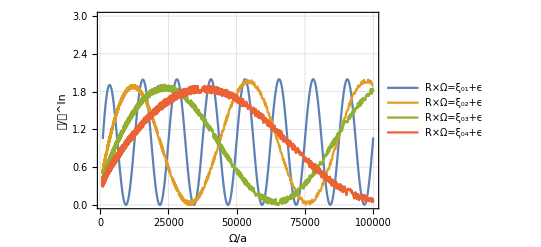

```mathematica
DRResAsyOaIn=ListLinePlot[{{Re[#1],Re[#2]}&@@@s01,{Re[#1],Re[#2]}&@@@s02,{Re[#1],Re[#2]}&@@@s03,{Re[#1],Re[#2]}&@@@s04},PlotRange->{{1000,100000},{0,3}},ScalingFunctions->{"Linear","Linear"},PlotLegends->Placed[LineLegend[{"R×Ω=ξ_01+ϵ", "R×Ω=ξ_02+ϵ","R×Ω=ξ_03+ϵ","R×Ω=ξ_04+ϵ","R×Ω=ξ_05+ϵ"}
,LegendLayout->"Row",LabelStyle->{FontSize->12,FontFamily->"Latin Modern Roman"}
],{0.5,0.85}],FrameLabel->{"Ω/a","𝒞/𝒞^In"},ScalingFunctions->{"Linear","Linear"},Frame->True,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->13,FontColor->Black},GridLines->Automatic]
```

```mathematica
Export["DRRes_Asy_Oa_In.pdf",DRResAsyOaIn]
```

DRRes_Asy_Oa_In.pdf